## Essential code (redone):

### SSS & Causal Network Construction

Build a causal network from a SSS, modeling the Sequential Substituion System using tags.  This allows us to build the SSS evolution and the causal network simultaneously.  
(Based on code from NKS, pp. 1033, and suggestions of Matthew Szudzik.)

#### Alphabet: fromAlpha, toAlpha, SSSConvert

```mathematica
fromAlpha[string_String] :=(ToCharacterCode[string]-65);  
toAlpha[l:{___Integer}] := FromCharacterCode[l+65];

Attributes[s]=Flat;
SSSConvert[string_String] := s @@ fromAlpha[string];
SSSConvert[s[x__]] := toAlpha[{x}];
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats, using the functions fromAlpha and toAlpha.";
```

If it is considered desirable to use a different alphabet, only the functions fromAlpha and toAlpha need be changed.  The only requirement is that the alphabet be enumerable, i.e., set in 1-1 correspondence with {0,1,2,…}.

#### Character, string, ruleset weight & ruleset length: ToCharacterWeights, FromCharacterWeights, StringWeight, RuleSetWeight, RuleSetLength

For later iteration through the complete enumeration of rulesets, we require the weight of a character, a string or a ruleset.  The weight of a character is closely akin to what is already done by the fromAlpha function, but with A→1, B→2, etc., reserving 0 for the weight of the empty string.  The weight of a string is the sum of the weights of its characters, and the weight of a ruleset is sum of the weights of its strings:

```mathematica
ToCharacterWeights[s_String] := (1+fromAlpha[s]);
FromCharacterWeights[l:{___Integer}] := toAlpha[l-1];
(* Note: To avoid breaking the ruleset (un-)rank functions, avoid the temptation to define:  
ToCharacterWeights[""] = 0;  FromCharacterWeights[{0}]="";  *)
StringWeight[s_String] := Plus @@ ToCharacterWeights[s];
RuleSetWeight[rs_List] := Plus @@ (StringWeight /@ Flatten[rs /. Rule->List]);
RuleSetLength[rs_List] := Plus @@ (StringLength /@ Flatten[rs /. Rule->List]);
```

Now StringWeight can be applied to either strings or characters (single-character strings):

RuleSetWeight and the comparably defined RuleSetLength give the sum of the weights or sum of the lengths, respectively, of the strings in the ruleset:

#### SSSRuleIcon (defines & uses $MaxColor, myColors, patternPrint)

```mathematica
$MaxColor=6;  (* If you want to display SSSs with more than 6 symbols, just change this variable, otherwise the colors wrap.  (Now SSSInititialize modifies this automatically.) *)
```

```mathematica
myColors=Sequence[ColorFunction->(Hue[(#-1)/$MaxColor]&),ColorFunctionScaling->False];
```

```mathematica
patternPrint[pattern_,opts___] := ArrayPlot[{{##}/. 0->LightGray}& @@pattern,myColors,Mesh->True,opts,ImageSize->{Automatic,20}];
```

```mathematica
Clear[SSSRuleIcon];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,opts___] := Panel[Grid[Map[patternPrint[#,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
```

```mathematica
SSSRuleIcon::usage="SSSRuleIcon[rule(s)] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```

#### Generate a ruleset for the tagged SSS: SSSNewRule

We need a convenient way to convert old style rulesets (using letters only) to a new style ruleset, with the ability to handle tags.  For example, “BA”→“ABA” or s[1,0]→s[0,1,0] should be rewritten as

s[{1, a_}, {0, b_}] :> (AppendTo[$SSSConnectionList, {a, b} → $SSSTagIndex + {0, 1, 2}];  s[{0, $SSSTagIndex++}, {1, $SSSTagIndex++}, {0, $SSSTagIndex++}])

```mathematica
SSSNewRule[rule_Rule | rule_RuleDelayed] := Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@Transpose[{fromAlpha[lhs],ToString@#<>"_"& /@ lhsNames}]];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2=ToString[SSSConvert[rhs] /. n_Integer :> {n,"$SSSTagIndex++"}];
ToExpression[newlhs<>" :> ("<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := SSSNewRule/@rules;
SSSNewRule::usage= 
"SSSNewRule[rule(s)] generates the needed rule(s) for the tagged SSS (sequential substitution system) from the rule(s) given in string-format: e.g., \"BA\"→\"ABA\"";
```

#### Stripping out tags: SSSStrip

Internally an SSS state will include not only information about the cells/letters, but in addition, unique identifiers or tags.  For visualization purposes a one-way conversion from tagged to untagged form will be needed.  Here's a convert/strip function to strip out tags and recover the String notation:

```mathematica
Clear[SSSStrip];
SSSStrip[x_s] := SSSConvert[x⟦All,1⟧] /; MatrixQ[List@@x]   (* if dim=2, take only 1st component, and convert *)
SSSStrip[s[]]=""   (* treat empty string case *)  ;
SSSStrip::usage="SSSStrip[state] strips out tags from a state given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

#### Some needed functions to deal with the strings & cells:

cellsDeleted, safeStringTake, abbrev, envelopeSubtractStrings

```mathematica
cellsDeleted[{l1_,l2_}] := Flatten[Position[l1,_?(!MemberQ[l2,#]& ),{1},Heads->False] ];
```

```mathematica
safeStringTake[s_String,{n1_Integer,n2_Integer}] := StringTake[s,{Max[1,n1],Min[StringLength[s],n2]}];
safeStringTake[s_String,{n1_Integer,n2_Integer}] := safeStringTake[s,{StringLength[s]+1+n1,n2}]  /; -StringLength[s]≤n1<0
safeStringTake[s_String,{n1_Integer,n2_Integer}] := safeStringTake[s,{n1,StringLength[s]+1+n2}]  /; -StringLength[s]≤n2<0
```

abbrev[string] now always returns a list of 2 strings, the beginning and ending of string

```mathematica
Clear[abbrev];
abbrev[s_String,n_Integer] :={safeStringTake[s,{1,n}],safeStringTake[s,{-n,-1}]};
abbrev[s_String,0]:= {"",""};
 (* use as "abbreviation" of long strings the list of substrings of the first & last n characters *)
```

```mathematica
abbrev[s_String,n_] := (Print[Stack[]];s)  (* anything else happens, let's debug! *)
```

```mathematica
abbrev["ABCDEFGHI",4]
```

{ABCD,FGHI}

```mathematica
envelopeSubtractStrings[big_String,little_String] := Module[{lenbig=StringLength[big],lenlittle=StringLength[little],i=1,j=1,bigc=Characters[big],littlec=Characters[little]},
If[lenbig<lenlittle,Return[Reverse[envelopeSubtractStrings[little,big]]]];
For[i=1,i≤lenlittle,i++,If[bigc⟦i⟧≠littlec⟦i⟧,Break[]]];  (* now i is the first NON-matching character, or lenlittle + 1 *)
For[j=1,j≤lenlittle+1-i,j++,If[bigc⟦-j⟧≠littlec⟦-j⟧,Break[]]]; (* now j is the first non-matching character starting from the end, or the first character that matched from the beginning *)
{StringJoin @ bigc⟦;;i-1⟧,StringJoin /@ Rule[littlec⟦i;;-j⟧,bigc⟦i;;-j⟧],StringJoin @ bigc⟦-j+1;;⟧};
{{i,-j},StringJoin /@ Rule[littlec⟦i;;-j⟧,bigc⟦i;;-j⟧]};
StringJoin /@ Rule[littlec⟦i;;-j⟧,bigc⟦i;;-j⟧]
]; (* returns a list of replacements made *)
```

#### SSSInitialize (revamped): Initializing globals

Creating a causal network from a tagged SSS system requires at least two global variables, $SSSConnectionList and $SSSTagIndex, so we might as well keep track of other useful things in global variables, to avoid unnecessary recomputations.  (Now adjusts $MaxColor up/down as needed.)

SSSInitialize now does first single-step, checks for death (removes need for SSSSingleStep verifying that SSSEvolution and SSSTEvolution have at least 2 elements, and that SSSConnectionList has at least 1 element.  Returns True|False and optionally prints a clarifying message.

```mathematica
Clear[SSSInitialize];
SSSInitialize[rs:{___Rule},state_String,mode_:"Silent" (* "Silent" | "Loud" *)] :=
(
(* Tweak $MaxColor *)
$MaxColor:=Max[Flatten[{6,ToCharacterWeights /@ Flatten[rs/.Rule->List]}]];
(* initial setup *)
$SSSNet={};
$SSSOutDegreePotential=$SSSOutDegreeRemaining=$SSSOutDegreeActual={};
$SSSInDegree={}; (* {0} will be starting with one node, of in-degree 0 *)
$SSSDistance={0}; (* The starting node is 0 steps away from the starting node *)
$SSSConnectionList={}; 
$SSSTagIndex=StringLength[state]+1;                     (* value of next tag to use *)
$SSSTEvolution={s@@Transpose[{#,Range[Length[#]]}& @ fromAlpha[state]]};
$SSSEvolution = {state};
$SSSRuleSet = rs;
$SSSTRuleSet =SSSNewRule[rs];
$SSSRuleSetWeight = RuleSetWeight[rs];
$SSSRuleSetLength = RuleSetLength[rs];
$SSSMatchLengthHistory = $SSSHistory = {};
$SSSRepetitionInterval = $SSSRepetitionStart = 0;
$SSSStart = 1;
$SSSVerdict = "";
$SSSRuleUsage=Table[0,{Length[rs]}];  (* none of the rules have been used as yet *)

(* now do first singlestep, so we have at least 2 strings for the 
comparison tests used to determine $SSSVerdict and to build $SSSOutDegreeActual and $SSSOutDegreeRemaining *)
AppendTo[$SSSTEvolution,Last[$SSSTEvolution]/.$SSSTRuleSet];
AppendTo[$SSSEvolution,SSSStrip[Last[$SSSTEvolution]]];

If[ !MatchQ[mode, ("Silent"|"Quiet")],
Switch[Length[$SSSConnectionList],
0,Print["Error: No evolution possible starting from \""<>state<>"\" using ruleset: ",rs];Return[False],
_,Print["Successful initialization of ruleset: ",rs,", evolution: ",$SSSEvolution]
]
];

(* or if the first step of the evolution worked, update the global variables: *)
updateHistory;  (* $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual, $SSSMatchLengthHistory, $SSSHistory, $SSSRuleUsage *)
True  (* = Success *)
);
```

```mathematica
(* Below is code that must be executed each time a step is performed by SSSSingleStep, but it must also be done after for the first step, done by SSSInitialize, so it has been put into a separate function that both can call, updating $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual, $SSSMatchLengthHistory, $SSSHistory. *)

updateHistory := Module[{cd},
AppendTo[$SSSInDegree,Length[$SSSConnectionList⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[$SSSOutDegreePotential,Length[$SSSConnectionList⟦-1,-1⟧]];  (* # of cells created by last rule *)
AppendTo[$SSSOutDegreeRemaining,Last[$SSSOutDegreePotential]];
AppendTo[$SSSOutDegreeActual,0];

(* find cells deleted by latest event, use info to update $SSSHistory and $SSSMatchLengthHistory *)
cd=cellsDeleted[$SSSTEvolution⟦-2;;⟧];  (* comparing last 2 states, find deleted cell positions *)
cd=If[Length[cd]==0,{1,0},{First@cd,Last@cd}];  (* Take first & last or if no deletions -- there was an insertion at beginning of state string: match at pos 1, length 0 *)

(* $SSSMatchLengthHistory gets 3 numbers: lengths of pre-match, match, and post-match substrings *)
AppendTo[$SSSMatchLengthHistory,{First[cd]-1,Last[cd]-First[cd]+1,StringLength[$SSSEvolution⟦-2⟧]-Last[cd]}];

(* $SSSHistory gets 4 items: pre-match abbreviation, match rule #, post-match abbreviation, 0 *)
AppendTo[$SSSHistory,{
abbrev[#,$SSSRuleSetLength]& @ safeStringTake[$SSSEvolution⟦-2⟧,{1,First[cd]-1}],  (* pre-match substring *)
StringTake[$SSSEvolution⟦-2⟧,cd] /. Thread[$SSSRuleSet⟦All,1⟧->Range[Length[$SSSRuleSet]]],  (* matching rule # *)
(* Print["Trying to do safeStringTake[$SSSEvolution⟦-2⟧,{Last[cd]+1,-1}]: safeStringTake[",$SSSEvolution⟦-2⟧,", {Last[",cd,"} ]+1,-1}]"]; *)
abbrev[#,$SSSRuleSetLength]& @ safeStringTake[$SSSEvolution⟦-2⟧,{Last[cd]+1,-1}],     (* post-match substring *)
0  (* tag to be used later to indicate shrinkage before/after match *)
}];
If[$SSSVerdict=!="Dead",$SSSRuleUsage⟦$SSSHistory⟦-1,2⟧⟧++ ] (* increment the usage counter for the rule that was used on this step *)
];
```

```mathematica
SSSInitialize::usage = "SSSInitialize[ruleset,string,(mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,\nstarting with a ruleset (e.g., {\"BA\"→\"ABA\"}) and an initial state string (e.g., \"BABA\").  The True|False return value indicates whether initialization was successful.\n\nIf omitted, mode defaults to \"Silent\", suppressing the short error or success message.\n\nThe following global variables are reset by this operation:\n\n$SSSNet:\t\t\t\tthe causal network of the current SSS,\n$SSSInDegree:\t\t\tthe list of in-degrees for each node,\n$SSSOutDegreeActual:\t\tthe list of currently found out-degrees for each node,\n$SSSOutDegreePotential:\t\tthe list of maximum possible out-degrees for each node,\n$SSSOutDegreeRemaining:\tthe list of numbers of possible remaining out-connections for each node,\n$SSSConnectionList:\t\tthe current list of all causal network connections,\n$SSSDistance:\t\t\tthe list of minimum distances from the current node back to the starting node.\n$SSSTagIndex:\t\t\tthe current tag index being used,\n$SSSTEvolution:\t\t\tthe complete evolution of the tagged SSS so far,\n$SSSEvolution:\t\t\tthe stripped (tagless) version of $SSSTEvolution,\n$SSSRuleSet:\t\t\tthe ruleset used for creating the SSS,\n$SSSTRuleSet:\t\t\tthe version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,\n$SSSRuleSetWeight:\t\tthe total weight of $SSSRuleSet,\n$SSSRuleSetLength:\t\tthe total length of $SSSRuleSet,\n$SSSHistory:\t\t\tan annotated/translated version of $SSSEvolution used to detect repeating patterns,\n$SSSMatchLengthHistory:\ta list of the match positions that occurred in forming the SSS,\n$SSSRuleUsage:\t\t\tthe list of rule usage counters, later adjusted to identified portion of SSS,\n$SSSRepetitionInterval:\t\tthe length of the repeating section (if any) of the SSS,\n$SSSRepetitionStart:\t\tthe start of the repeating section (if any) of the SSS,\n$SSSStart:\t\t\tthe starting position for displaying the SSS and its causal network,\n$SSSVerdict:\t\t\tset to \"Dead\" | \"Repeating\" | \"Pseudorepeating\" as soon as the future of the SSS becomes clear.";
```

```mathematica
?SSSInitialize
```

SSSInitialize[ruleset,string,(mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,
starting with a ruleset (e.g., {"BA"→"ABA"}) and an initial state string (e.g., "BABA").  The True|False return value indicates whether initialization was successful.

If omitted, mode defaults to "Silent", suppressing the short error or success message.

The following global variables are reset by this operation:

$SSSNet:				the causal network of the current SSS,
$SSSInDegree:			the list of in-degrees for each node,
$SSSOutDegreeActual:		the list of currently found out-degrees for each node,
$SSSOutDegreePotential:		the list of maximum possible out-degrees for each node,
$SSSOutDegreeRemaining:	the list of numbers of possible remaining out-connections for each node,
$SSSConnectionList:		the current list of all causal network connections,
$SSSDistance:			the list of minimum distances from the current node back to the starting node.
$SSSTagIndex:			the current tag index being used,
$SSSTEvolution:			the complete evolution of the tagged SSS so far,
$SSSEvolution:			the stripped (tagless) version of $SSSTEvolution,
$SSSRuleSet:			the ruleset used for creating the SSS,
$SSSTRuleSet:			the version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,
$SSSRuleSetWeight:		the total weight of $SSSRuleSet,
$SSSRuleSetLength:		the total length of $SSSRuleSet,
$SSSHistory:			an annotated/translated version of $SSSEvolution used to detect repeating patterns,
$SSSMatchLengthHistory:	a list of the match positions that occurred in forming the SSS,
$SSSRuleUsage:			the list of rule usage counters, later adjusted to identified portion of SSS,
$SSSRepetitionInterval:		the length of the repeating section (if any) of the SSS,
$SSSRepetitionStart:		the start of the repeating section (if any) of the SSS,
$SSSStart:			the starting position for displaying the SSS and its causal network,
$SSSVerdict:			set to "Dead" | "Repeating" | "Pseudorepeating" as soon as the future of the SSS becomes clear.

#### SSSSingleStep (revamped):

SSSSingleStep no longer has “modes”:  if you call it, you want the full package treatment:  evolve the SSS ($SSSTEvolution and $SSSEvolution) and causal network ($SSSConnectionList, $SSSNet), update node info ($SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual), and distance list ($SSSDistance).  No need to verify whether $SSSEvolution has at least 2 entries, and $SSSConnectionList at least 1, since this is now guaranteed if SSSInitialize returns True.  Updating $SSSVerdict is a separate task to be moved to PronounceVerdict, called after each evolution step (to catch dead [important!] | repeating cases immediately).  But note that only if the SSS is dead does SSSSingleStep return False and refuse to proceed.

SSSSingleStep now updates the tags (column 4) in $SSSHistory, might as well do it as we go since each tag only depends on two successive lines.  (These tags used by the new function VerifyPseudorepeating.)

SSSSingleStep now refuses to modify anything if the SSS is already dead, and calls PronounceVerdict after each step, so Dead | Repeating cases are guaranteed to be caught immediately.  The main disadvantage is slightly slower execution, but the problem is limited by making PronounceVerdict return immediately if a verdict already exists.

```mathematica
$SSSEvolution[[;;5]]
```

{A,ABA,AAB,ABAAB,AABAB}

```mathematica
$SSSTEvolution[[;;5]]//Column
```

s[{0,1}]
s[{0,2},{1,3},{0,4}]
s[{0,5},{0,6},{1,7}]
s[{0,8},{1,9},{0,10},{0,6},{1,7}]
s[{0,11},{0,12},{1,13},{0,6},{1,7}]

```mathematica
Clear[SSSSingleStep];
SSSSingleStep := Module[{cd, ri, pri, rs, prs,len,startingEvents},
If[$SSSVerdict==="Dead",Return[False]];  (* if already dead, do nothing *)

(* do the actual evolution step *)
AppendTo[$SSSTEvolution,Last[$SSSTEvolution]/.$SSSTRuleSet];
AppendTo[$SSSEvolution,SSSStrip[Last[$SSSTEvolution]]];

If[!MatchQ[$SSSVerdict,"Dead"|"Repeating"],PronounceVerdict];  (* to limit wasted time, don't call if verdict is already in! *)

If[$SSSVerdict==="Dead",Return[False]];  (* if died this step, return immediately:  fixes BUG! extra link was added after sessie died *)

(* Now update globals:  first the part that is done for each step, including the first one (by SSSInitialize): *)
updateHistory; (* $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual, $SSSMatchLengthHistory, $SSSHistory *)

(* now the steps that are only done for non-initial steps, comparing to previous entries in $SSSConnectionList: *)
len=Length[$SSSConnectionList];
startingEvents=Flatten[If[Length[#]>0,First[First[#]],#]& /@ (Position[$SSSConnectionList⟦;;-2⟧,#]& /@ $SSSConnectionList⟦-1,1⟧)];
$SSSOutDegreeActual⟦#⟧++& /@ startingEvents; (* update out-degee list for events involved *)
$SSSOutDegreeRemaining⟦#⟧--& /@ startingEvents; (* update out-degee list for events involved *)
$SSSNet=Join[$SSSNet,#->len& /@ startingEvents];           (* add new links to the causal network *)

AppendTo[$SSSDistance,Min[$SSSDistance⟦startingEvents⟧]+1];  (* Find minimum path length of cause nodes, add 1 *)

(* fix tag: 4th item of current line of $SSSHistory *)
If[Length[$SSSMatchLengthHistory]>1,
Switch[$SSSMatchLengthHistory⟦-1⟧-$SSSMatchLengthHistory⟦-2⟧, (* compare to previous line *)
{_?Negative,0,_},$SSSHistory⟦-1,4⟧=$SSSHistory⟦-2,4⟧+1,  (* prematch shrinking *)
{_,0,_?Negative},$SSSHistory⟦-1,4⟧=$SSSHistory⟦-2,4⟧-1     (* postmatch shrinking *)
]
];

Return[True];
];
```

```mathematica
SSSSingleStep::usage=
"SSSSingleStep performs a single step of the current sequential substitution system (SSS) evolution (if not already dead), applying the current SSS ruleset (saved in $SSSRuleSet and $SSSTRuleSet) to the most recent state, the last entry in $SSSTEvolution and $SSSEvolution.  This operation updates the global variables $SSSConnectionList, $SSSTagIndex, $SSSTEvolution, $SSSEvolution, $SSSHistory, $SSSMatchLengthHistory, $SSSRuleUsage, $SSSVerdict, $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual,$SSSDistance.  Use SSSInitialize to set up the global variables.";
```

```mathematica
?SSSSingleStep
```

SSSSingleStep performs a single step of the current sequential substitution system (SSS) evolution (if not already dead), applying the current SSS ruleset (saved in $SSSRuleSet and $SSSTRuleSet) to the most recent state, the last entry in $SSSTEvolution and $SSSEvolution.  This operation updates the global variables $SSSConnectionList, $SSSTagIndex, $SSSTEvolution, $SSSEvolution, $SSSHistory, $SSSMatchLengthHistory, $SSSRuleUsage, $SSSVerdict, $SSSOutDegreePotential, $SSSOutDegreeRemaining, $SSSOutDegreeActual,$SSSDistance.  Use SSSInitialize to set up the global variables.

#### PronounceVerdict

Separate function to test the current SSS at the current point in its evolution, and save the result in $SSSVerdict, as well as updating $SSSRepetitionStart and $SSSRepetitionInterval.  Must not be called until the SSS has been initialized by SSSInitialize and at least one step made by SSSSingleStep, since we assume that Length[$SSSTEvolution] > 1 (true after initialization) and Length[$SSSHistory] > 1 (true after first call to SSSSingleStep).  Verdict options:  “Dead”, “Repeating” and “Pseudorepeating”.  Returns {$SSSVerdict, {$SSSRepetitionStart, $SSSRepetitionInterval}.  SSSSingleStep checks $SSSVerdict before each actual evolution step and calls this function after each step if $SSSVerdict is the empty string in order to update $SSSVerdict, but it ignores the output, which is mostly for the benefit of the human operator. 

Returns:

“Dead”		(last 2 elements of $SSSTEvolution are identical),
“Repeating”		(last element of $SSSEvolution is identical to some earlier element: slower test, but time-saving if it works),
“Pseudorepeating”	(last element of $SSSHistory = at least 3 earlier elements, inconclusive, use VerifyPseudorepeating to test),
 
-- unless a verdict has already been pronounced.  Side effects:  sets $SSSVerdict, $SSSRepetitionStart, $SSSRepetitionInterval (0 if “Dead”).

```mathematica
Clear[PronounceVerdict];
PronounceVerdict := Module[{matches,poslist},
Which[
MatchQ[$SSSVerdict,"Dead"|"Repeating"],{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}},  (* Dead/Repeating SSSs don't ever change their spots. Otherwise, check/recheck: *)

Last[$SSSTEvolution]===$SSSTEvolution⟦-2⟧,(* Dead, since last check *)
poslist=Flatten@Position[$SSSTEvolution,Last@$SSSTEvolution];
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}={"Dead",{First[poslist],0}},

Length[poslist=Flatten@Position[$SSSEvolution,Last[$SSSEvolution]]]>1, (* Repeating, since last check *)
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}={"Repeating",{First[poslist],poslist⟦-1⟧-poslist⟦-2⟧}};
(* Print["rule usage: ",$SSSRuleUsage]; *)
$SSSRuleUsage=Table[0,{Length[$SSSRuleSet]}]; (* Zero out rule usage counters *)
Do[$SSSRuleUsage⟦$SSSHistory⟦k,2⟧⟧++,{k,$SSSRepetitionStart,Length[$SSSHistory]}]; (* count only identified part *)
(* Print["rule usage: ",$SSSRuleUsage]; *)
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}},

(* Note that the above tests take precedence over Pseudorepeating *)

$SSSVerdict=!="", {$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}, (* Verdict already pronounced, stick with it *)

poslist=Flatten@Position[$SSSHistory,Last[$SSSHistory]];
Length[poslist]≥5, (* We may enough repeats in the history to test *)
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}={"Pseudorepeating",{First[poslist],poslist⟦-1⟧-poslist⟦-2⟧}},

True, {$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}
]]
```

#### SSSEvolve

And finally the evolve function, which will attempts do perform a specified number of single steps of the current SSS evolution, optionally returning early if a repetition or pseudo-repetition interval has been found.  Returns $SSSVerdict if a verdict has been pronounced, else “OK”.  Use after initialization by SSSInitialize.

SSSEvolve now takes option EarlyReturn -> True | False

```mathematica
Clear[SSSEvolve];
Options[SSSEvolve]={EarlyReturn->False};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSEvolve[n_Integer/;n>0,opts:OptionsPattern[]] := (
If[OptionValue[EarlyReturn],
Do[If[MatchQ[$SSSVerdict, ("Dead"|"Repeating"|"Pseudorepeating")],Break[],SSSSingleStep],{n}],
Do[SSSSingleStep,{n}]
];
If[$SSSVerdict=="","OK",$SSSVerdict]
)
```

```mathematica
SSSEvolve::usage="SSSEvolve[n] generates an additional n levels of the current SSS (sequential substitution system), which must have been previously initialized using SSSInitialize.  Use the option EarlyReturn → True (default) to allow early termination for repeating or pseudorepeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.  Proposed pseudo-repeating cases are currently ignored.)  Returns the current verdict, or \"OK\" if none known.  Global variables set up by SSSInitialize are updated, with $SSSEvolution containing the tagless SSS, $SSSConnectionList the updated causal network connection list, etc.  mode can be \"Silent\", \"Quiet\", or \"Loud\".";
```

```mathematica
?SSSEvolve
```

SSSEvolve[n] generates an additional n levels of the current SSS (sequential substitution system), which must have been previously initialized using SSSInitialize.  Use the option EarlyReturn → True (default) to allow early termination for repeating or pseudorepeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.  Proposed pseudo-repeating cases are currently ignored.)  Returns the current verdict, or "OK" if none known.  Global variables set up by SSSInitialize are updated, with $SSSEvolution containing the tagless SSS, $SSSConnectionList the updated causal network connection list, etc.  mode can be "Silent", "Quiet", or "Loud".

#### Identification strategies

1.  If $SSSTEvolution stops changing (last 2 elements are equal), the SSS is Dead, as of the first instance of the repetition.  If the SSS is Dead, so is the network.  [Done]

2a.  If any two elements of $SSSEvolution are the same, the SSS is Repeating, and will repeat from then on.  Note:  for efficency, we only test whether the last element is repeated anywhere before.  Since the test happens every step, it will catch the first time it happens, and assign a value to $SSSVerdict, which remains until reinitialized.  If the SSS is Repeating, so is the network.  [Done]

2b.  If Repeating, also look for unused rules (in the repeating part):  possible long-jump.  This is implemented in TestForUnusedRules.  [Need to check.]

3.  Having “enough” repetitons in $SSSHistory sets $SSSVerdict to Pseudorepeating, meaning the SSS may be repeating, n-dimensional, or exponential.  Before this happens there’s no point in applying additional tests to the SSS or its network.  [Done]

Possible strategies:

4.  Old network test (should be reinvoked?):  Take a section of $SSSNet including 500 consecutive nodes, and look for matches elsewhere in $SSSNet.  An identical match gives a high probability of a 1-d network, even though the SSS never repeats.  (Better:  require 5 matches)

5.  If a large segment of $SSSRuleUsage repeats, it is likely that the network is repeating.  Even if exact repetition does not occur, find the positions where the least frequently used rule was used and try to fit that data to a polynomial or exponential curve and/or identify the pattern from repeated differences and ratios of differences.  (NOTE:  It is currently unclear whether an exponential fit for this data implies an exponential network.  Look at apparent exponential cases, including NKS 91e, comparing the SSS behavior and the network behavior. Caution:  many exponential networks use the same rule or subset of rules for a long time before a different rule can be applied again.)  To decrease the likelihood of incorrect identification, require at least 500 steps of evolution and that the last 90% of $SSSRuleUsage repeats, including 5 repetitions, and merge intervals before testing.  [Implementing as MinRulePositions.]

6.  In working with intervals, such as above, always make sure each interval uses the same rules, working backward from the last completed interval:  if a change occurs, adjust or merge intervals.  If n^th interval uses fewer rules than the (n-1)^st, merge the n^th with whatever follows.  If n^th interval uses more rules than the (n-1)^st, merge the (n-1)^st with whatever precedes it.  If the number of prospective intervals falls below 5, abandon attempt.  [Implementing as MergeIntervals.]

7.  Look for a pattern in the positions of the commonest element of $SSSHistory.  Since the addition of the tag (4^th part of each element, set to increment or decrement to avoid false positives when pre- or post-match strings are changing length), the commonest element is likely to have a 0 tag, and may follow a simple pattern.  Note:  merge intervals before testing.  [Implementing as CommonestHistoryPositions.]

8.  If after 500 steps the last 90% of $SSSRuleUsage (see #5) all uses the same subset of the ruleset, whether or not the behavior can be identified, if not all rules are used in the the last 90%, it is likely that the SSS (and network) is a duplicate of an earlier case, and can be skipped or can even trigger a long-jump.  This would be highly desirable. [Need to do.]

9.  New network test:  Use $SSSOutDegreeRemaining to decide which is the first node that might have new paths leading off it.  Ideally this would be the first non-zero in the list, but Pseudorepeating (growing) SSSs may repeatedly create some cells that will never be destroyed, corresponding to some nodes that retain a non-zero value in $SSSOutDegreeRemaining, in which case it may be difficult to definitely determine the index. Tally $SSSDistance⟦1;;index⟧ to give the number of nodes (n) a distance (d) from the network origin.  (Any data past this index is probably incomplete, and should be disregarded.)  Try to fit that data to a polynomial or exponential curve and/or identify the pattern from repeated differences and ratios of differences.  [Implementing as DistanceTally.]

Note: Any identifiable pattern in the first half of $SSSOutDegreeRemaining might allow a larger index to be used, indicating a pattern among the nodes that never will be “complete”, in which case distance data could be used up to where the pattern breaks, i.e., where new branches can be expected.  OR: if there are any 1s in the first half of $SSSOutDegreeRemaining, use the position of the first 2 as the index, etc.

10.  For each n, find the last node that is a distance n from the origin, up to the index mentioned in #9.  After merging intervals, seek a pattern in these values.  [Implementing as DistanceLastPositions.]

11.  Look for a pattern in the list of positions of maximum-length states in $SSSEvolution (greatest string length seen up to that point).  [Implementing as MaxStateLengthPositions.]

12.  Consider position of match in the state string.  Does a minimum or maximum position (minimum distance from end) keep recurring?  If so, restart at first such position, skipping junk before this point in the evolution and deleting unused stuff at beginning/end of state string.

13.  Consider positions of least-frequent repeated case in last 2/3 of $SSSInDegree and and reliable part of $SSSOutDegree.

```mathematica
$SSSRuleUsage
MinRulePositions
checkDimension/@MergeIntervals/@%
MaxStateLengthPositions
checkDimension@MergeIntervals@%
CommonestHistoryPositions
checkDimension@MergeIntervals@%
DistanceLastPositions
checkDimension@MergeIntervals@%
checkDimension@DistanceTally
```

#### SSS & Net Tests

Needed functions:

```mathematica
MergeIntervals[l0_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
While[n>2,
rulesused1=Union[$SSSHistory⟦l⟦n-2⟧;;l⟦n-1⟧-1,2⟧];
rulesused2=Union[$SSSHistory⟦l⟦n-1⟧;;l⟦n⟧-1,2⟧];
If[$debug,Print["rules used:", rulesused1,", ",rulesused2]];
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
myRatios[l_List,n_Integer?Positive] := 
If[n≥Length[l],{},
ListConvolve[Flatten[{1,Table[0,{n-1}],-1}],l,{-1,1},{},Power[#2,#1]&,Times]
]
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
checkDimension[l_List]:=Module[{diffs={l,Differences@l},ptrn,rats,identified={False},dim=1,expdim,n=1,i=1,ans,toobig=0},
Off[General::infy];
Off[Divide::indet];
(* 3 nested loops until identified: one difference row at a time until too short, increasing clump size, increasing initial skip *) 
While[identified==={False}&&Length[diffs⟦-1⟧]/n≥4&&i≤Length[diffs⟦-1⟧]/n-3,
If[$debug,Print[{identified,"===",{False}," && ",Length[diffs⟦-1⟧]/n,"≥",4," && ",i,"≤",Length[diffs⟦-1⟧]/n-3}]];
toobig++;
If[toobig>500,If[$debug,Print["too big, something is probably wrong, quitting"]];  Break[]];
(* try to identify pattern in clump totals of this difference row *)
If[
MatchQ[ptrn=Total/@Partition[diffs⟦-1⟧⟦i;;⟧,n];
If[$debug,Print["{dim,n,i}=",{dim,n,i},", considering differences: ",ptrn]];
ptrn
,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
identified={"dim",ToString@dim,l⟦i⟧,l⟦i+1⟧-l⟦i⟧};If[n>1,If[$debug,Print["match (",ptrn,") with Partition[data,",n,"], starting at ",i]]], 
(* else look at pattern in largest positive subsequence of ratios *)
If[MatchQ[rats=LongestPositiveSubsequence[Ratios[ptrn]],{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
identified={"exp",l⟦i⟧};
expdim=First@Commonest[rats];
If[n>1,If[$debug,Print["match (",ptrn,") with Partition[data,",n,"], starting at ",i]]],
i++;If[i>Length[diffs⟦-1⟧]/n-3,n++;i=1;If[Length[diffs⟦-1⟧]/n<4,n=1;dim++;AppendTo[diffs,Differences[diffs⟦-1⟧]]]]
]
]
];
ans=Switch[identified⟦1⟧,
"dim",{identified⟦2⟧,{identified⟦3⟧,If[identified⟦2⟧=="1",identified⟦4⟧,∞]},Grid[diffs]},
"exp",{"exp",(* ToString[expdim], *)  {identified⟦2⟧,∞},Grid[diffs],Ratios[ptrn]/.ComplexInfinity->∞},
_,{"failed",Grid[diffs],N[Ratios[diffs⟦-1⟧]]/.ComplexInfinity->∞}];
On[General::infy];
On[Divide::indet];
ans]
```

### Consider returning the whole i^th column that would allow the first row to be reconstructed from that point on: ###

{"2",{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | } ⇒ {2, {4,4,2}}

SSS Tests:

```mathematica
MaxStateLengthPositions:=Module[{maxlen=0},
Rest@Last@Last@Reap[
Do[
If[StringLength[$SSSEvolution⟦n⟧]>maxlen,Sow[n];maxlen=StringLength[$SSSEvolution⟦n⟧]],
{n,1,Length[$SSSEvolution]}]
]]
```

```mathematica
MaxStateLengthPositions
```

{3,5,7,9,11,13,15,17,19,21,23,25,27}

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{1,{3,2},3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
MinRulePositions := Module[{len=Length[$SSSHistory],ruletally,least},
ruletally=Tally[$SSSHistory⟦Round[.1len];;len,2⟧];
least=Min[Last/@ruletally];
Flatten[Position[$SSSHistory⟦All,2⟧,#]]& /@ (First /@ Select[ruletally,Last[#]==least&])
]
```

```mathematica
MinRulePositions
```

{{1,3,5,7,9,11,13,15,17,19,21,23,25},{2,4,6,8,10,12,14,16,18,20,22,24,26}}

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{1,{1,2},1 | 3 | 5 | 7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | },{1,{2,2},2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }}

```mathematica
CommonestHistoryPositions := If[MatchQ[$SSSVerdict,""|"Dead"],{},
Flatten@Position[$SSSHistory,First@Commonest[$SSSHistory⟦;;Round[Length[$SSSHistory]/2,1]⟧]]]
```

```mathematica
SSSEvolve[50]
```

1

```mathematica
CommonestHistoryPositions
```

{16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126}

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{1,{16,2},16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

Net Tests:

```mathematica
DistanceLastPositions:= 
Module[{tally,pos,maxdistance,odr,z=Min[$SSSOutDegreeRemaining]},
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees,nulling out (with ∞) the first tenth so as to get past initial oddities. This hopefully advances past most nodes that will never be complete due to never-to-be deleted cells *) 

odr=ReplacePart[$SSSOutDegreeRemaining,_?(#<.1Length[$SSSOutDegreeRemaining]&)->∞];
z=Min[odr];
tally=First /@ Tally  /@ Split[odr /. _?(#≠z&)->z+1];
pos=Total[Last /@ tally⟦;;Last@Last@Position[tally,{z,Max[Last/@Cases[tally,{z,_}]]}]⟧]+1;
(* Starting at this position any node with a positive entry in $SSSOutDegreeRemaining is treated as incomplete *)
(* Find distances to them all, take the minimum distance as our maximum reliable distance *)
maxdistance=Min[$SSSDistance⟦Select[Flatten@Position[$SSSDistance,_?Positive],#≥pos&]⟧];
(* Find the position of the last instance of each distance, out to maxdistance, in $SSSDistance *) 
Last[Last[Position[$SSSDistance,#]]]& /@ Range[maxdistance]
]
```

```mathematica
checkDimension@DistanceLastPositions
```

{1,{2,2},2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
DistanceTally:= 
Module[{tally,pos,maxdistance,odr,z=Min[$SSSOutDegreeRemaining]},
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees,nulling out (with ∞) the first tenth so as to get past initial oddities. This hopefully advances past most nodes that will never be complete due to never-to-be deleted cells *) 

odr=ReplacePart[$SSSOutDegreeRemaining,_?(#<.1Length[$SSSOutDegreeRemaining]&)->∞];
z=Min[odr];
tally=First /@ Tally  /@ Split[odr /. _?(#≠z&)->z+1];

(* Starting at this position any node with a positive entry in $SSSOutDegreeRemaining is treated as incomplete *)
(* Find distances to them all, take the minimum distance as our maximum reliable distance *)

maxdistance=Min[$SSSDistance⟦Select[Flatten@Position[$SSSDistance,_?Positive],#≥pos&]⟧];
Accumulate[Last /@ Tally[Sort[Select[$SSSDistance,#≤maxdistance&]]]]
(* This gives, in order, the number of nodes a distance ≤1, ≤2, ... from the origin *)
];
```

```mathematica
checkDimension@DistanceTally
```

{1,{1,1},1 | 2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 60 | 62 | 64 | 66 | 68 | 70 | 72 | 74 | 76 | 78 | 80 | 82 | 84 | 86 | 88 | 90 | 92 | 94 | 96 | 98 | 100 | 102 | 104 | 106 | 108 | 110 | 112 | 114 | 116 | 118 | 120 | 122 | 124 | 126
1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
RiffleDistanceTally := Module[{diffs,rats,identified=False,n,data=Differences[DistanceTally],mx},
Off[Power::infy,Infinity::indet,Power::indet];
mx=Length[data];
n=1;
While[identified===False && n≤mx,
If[MatchQ[diffs=Differences[data,1,n],
{Repeated[_,{0,5}],Repeated[b_,{4,∞}],Repeated[_,{0,3}]}],
identified="2",
If[MatchQ[rats=myRatios[diffs,n],
{Repeated[_,{0,5}],Repeated[b_,{3,∞}],Repeated[_,{0,3}]}],
identified="exp",
n++]
]
];
On[Power::infy,Infinity::indet,Power::indet];
Switch[identified,
False,{"failed"},
"exp",{"exp"," riffling by ",n,": ",rats},
"2",{"2"," riffling by ",n,": ",diffs}
]
]
```

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Differences[DistanceTally]
```

{1,2,3,5,7,10,13}

```mathematica
Differences[Differences[DistanceTally],1,2]
```

{2,3,4,5,6}

```mathematica
Differences@%
```

{1,1,1,1}

```mathematica
{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756}[[1;;-1;;2]]
FindSequenceFunction[%,n]
```

{1,5,29,137,503,1507,3863,8779}

1/180 (-180+534 n-253 n^2+30 n^3+65 n^4-24 n^5+8 n^6)

```mathematica
{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756}[[2;;-1;;2]]
FindSequenceFunction[%,n]
```

{2,12,65,270,890,2454,5901,12756}

1/180 (330 n-133 n^2+120 n^3+35 n^4+8 n^6)

```mathematica
Differences[{1,2,5,12,29,65,137,270,503,890,1507,2454,3863,5901,8779,12756},1,2]
Differences@%
Differences@%
Differences@%
Differences@%
Differences@%
```

{4,10,24,53,108,205,366,620,1004,1564,2356,3447,4916,6855}

{6,14,29,55,97,161,254,384,560,792,1091,1469,1939}

{8,15,26,42,64,93,130,176,232,299,378,470}

{7,11,16,22,29,37,46,56,67,79,92}

{4,5,6,7,8,9,10,11,12,13}

{1,1,1,1,1,1,1,1,1}

```mathematica
Differences[{1,2,5,12,29,65,137,270,503,890,1507,2454},1,2]
Differences@%
Differences@%
Differences@%
Differences@%
Differences@%
```

{4,10,24,53,108,205,366,620,1004,1564}

{6,14,29,55,97,161,254,384,560}

{8,15,26,42,64,93,130,176}

{7,11,16,22,29,37,46}

{4,5,6,7,8,9}

{1,1,1,1,1}

#### This shows that I must extend RiffleDistanceTally to do the same sort of multiline operation that checkDimension already does! ####

#### IdentifyPseudorepeating

```mathematica
$debug=False
```

False

```mathematica
IdentifyPseudorepeating := Module[{sssAns,distanceTallyAns,sssSummary,distanceTallySummary},
Which[
$SSSVerdict=="Dead", Return[{}],

10Max[$SSSNet/.Rule->List]<Length[$SSSEvolution],
If[$debug,Print[n,". ",rs," : No network after step ",Max[$SSSNet/.Rule->List],", now at ",Length[$SSSEvolution]]];
Return[{}]
];
sssAns=checkDimension/@MergeIntervals /@ MinRulePositions;
sssAns=Which[
Length[sssAns]==0,{"failed"},
Length[sssAns]== 1,sssAns⟦1⟧,
!(Equivalent@@sssAns⟦All,1⟧),{"failed"},
Equivalent@@sssAns⟦All,1⟧, {sssAns⟦1,1⟧,First[Sort[sssAns⟦All,2;;3⟧]]},
True,{"failed"}
];
sssAns={
sssAns, (* simplified ans from MinRulePositions *)
checkDimension@MergeIntervals@MaxStateLengthPositions,
checkDimension@MergeIntervals@CommonestHistoryPositions,
checkDimension@MergeIntervals@DistanceLastPositions
}; (* combine with results of the other tests *)

If[$debug,Print[sssAns]]; 

sssSummary=Select[sssAns,First[#]≠"failed"&];
If[Length[sssSummary]>0,
sssSummary=sssSummary⟦All,1;;2⟧;
If[!(Equivalent@@(First/@sssSummary)),
If[$debug,Print["SSS tests give different answers: ", sssSummary];Print[sssAns]];sssSummary={}
]
];

If[$debug,Print["sssSummary: ",sssSummary]]; 

distanceTallyAns = {checkDimension@DistanceTally,RiffleDistanceTally};

(*
If[Length[sssSummary]>0 && sssSummary⟦1,1⟧=="1", (* DistanceTally & RiffleDistanceTally catastrophically fail for 1-d *)
distanceTallyAns={{"1","overriding!"}},
distanceTallyAns = {checkDimension@DistanceTally,RiffleDistanceTally}
];  
*)

If[$debug,Print["distanceTallyAns: ",distanceTallyAns]];

distanceTallySummary = Union[Select[First /@ distanceTallyAns,#≠"failed"&]];

If[$debug,Print["distanceTallySummary: ",distanceTallySummary]]; 


If[Length[distanceTallySummary]>0 && distanceTallySummary[[1]]=="1",distanceTallySummary={"1"}];  (* remove this kludge when function is extended, currently RiffleDistanceTally  *)

If[Length[distanceTallySummary]==2,
If[$debug,Print["Error: checkDimension@DistanceTally and RiffleDistanceTally disagree:  "]; Print[distanceTallySummary]];
distanceTallySummary={}
];

Which[
Length[distanceTallySummary]==0, 
If[$debug,Print["Distance tally tests unsuccessful"]]; {False,{sssAns,distanceTallyAns}},

Length[sssSummary]==0,
If[$debug,Print["No successful SSS tests"]];
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,$SSSRepetitionInterval,$SSSRepetitionStart}={distanceTallySummary⟦1⟧,∞,∞}
];
{True,distanceTallySummary⟦1⟧<>"qq"},

Length[sssSummary]==1 && sssSummary⟦1,1⟧== distanceTallySummary⟦1⟧,
If[$debug,Print["Only one successful SSS test"]]; 
If[$SSSVerdict=!="Repeating",{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}=sssSummary⟦1⟧];
{True,sssSummary⟦1⟧/.s_String:>s<>"q"},

Union[First/@sssSummary,distanceTallySummary]≠Union[distanceTallySummary],
If[$debug,Print["CAUTION: SSS tests and distance tally tests disagree: ",{First/@sssSummary,distanceTallySummary}]]; 
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}=Sort[sssSummary]⟦1⟧;
$SSSVerdict=distanceTallySummary⟦1⟧<>"x"<>Sort[sssSummary]⟦1,1⟧
];
{True,distanceTallySummary⟦1⟧<>"x"<>Sort[sssSummary]⟦1,1⟧,Sort[sssSummary]⟦1,2;;⟧},

True,
If[$SSSVerdict=!="Repeating",
{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval}}=Sort[sssSummary]⟦1⟧
];
{True,Sort[sssSummary]⟦1⟧}
]
];
```

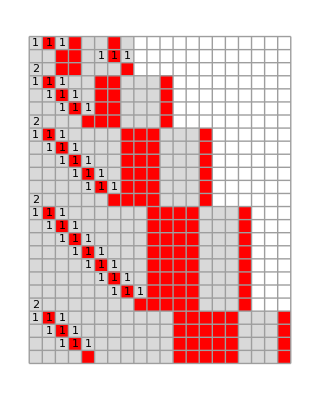


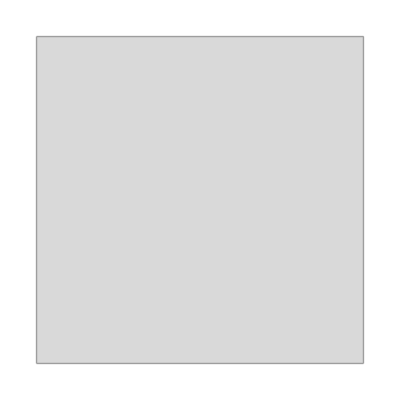
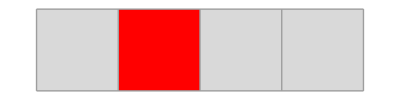
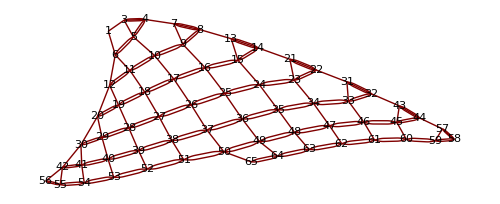
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"ABA"->"AAB","A"->"ABAA"}, "ABABAABA",75,EarlyReturn->True,SSSMax->25,NetMax->65,NetSize->500]
```

```mathematica
SSSEvolve[50]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

match ({3,3,3,3,-8,-1,-1,-1,-1,-1}) with Partition[data,2], starting at 1

{True,{2,{3,∞}}}

```mathematica
SSSEvolve[10]
IdentifyPseudorepeating
```

2

{{2,{3,∞},3 | 7 | 13 | 21 | 31 | 43 | 57 | 73
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74
4 | 6 | 8 | 10 | 12 | 14 | 16 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{failed,1
,{}},{failed,6 | 12 | 20 | 30 | 42 | 56
6 | 8 | 10 | 12 | 14 | 
2 | 2 | 2 | 2 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}}}

sssSummary: {{2,{3,∞}},{2,{4,∞}}}

distanceTallyAns: {{failed,1 | 3 | 7 | 12 | 19 | 27 | 37
2 | 4 | 5 | 7 | 8 | 10 | 
2 | 1 | 2 | 1 | 2 |  | 
-1 | 1 | -1 | 1 |  |  | 
2 | -2 | 2 |  |  |  | ,{-1.,-1.}},{2, riffling by ,2,: ,{3,3,3,3}}}

distanceTallySummary: {2}

{True,{2,{3,∞}}}

```mathematica
SSSEvolve[100]
IdentifyPseudorepeating
```

2

{{2,{3,∞},3 | 7 | 13 | 21 | 31 | 43 | 57 | 73 | 91 | 111 | 133 | 157 | 183
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{4,∞},4 | 8 | 14 | 22 | 32 | 44 | 58 | 74 | 92 | 112 | 134 | 158 | 184
4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{43,∞},43 | 57 | 73 | 91 | 111 | 133 | 157 | 183
14 | 16 | 18 | 20 | 22 | 24 | 26 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2,{6,∞},6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }}

sssSummary: {{2,{3,∞}},{2,{4,∞}},{2,{43,∞}},{2,{6,∞}}}

match ({3,3,3,3,3}) with Partition[data,2], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 3 | 7 | 12 | 19 | 27 | 37 | 48 | 61 | 75 | 91 | 108
2 | 4 | 5 | 7 | 8 | 10 | 11 | 13 | 14 | 16 | 17 | 
2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 |  | },{2, riffling by ,2,: ,{3,3,3,3,3,3,3,3,3}}}

distanceTallySummary: {2}

{True,{2,{3,∞}}}

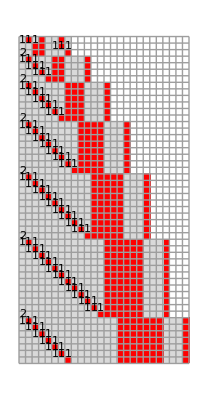
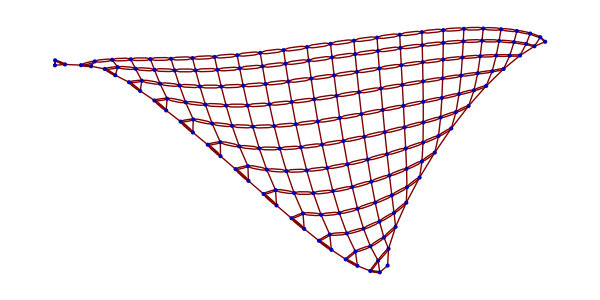
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[SSSMax->50,NetSize->{600,300},VertexLabeling->Tooltip]
```

```mathematica
DistanceTally
```

{1,3,6,10,16,23,31,40,50,61,73,86,100,115,131,148,166,185}

```mathematica
checkDimension@%
```

{dim,2,1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
{2,2,2,"failed","failed","failed"}
```

#### BestNetStart

```mathematica
BestNetStart := Module[{diffs=Differences[$SSSOutDegreeActual-$SSSInDegree],mx,candidates},
(* Print[diffs]; *)
mx=Max[diffs⟦$SSSRepetitionStart;;$SSSRepetitionStart+First@Flatten@{$SSSRepetitionInterval}⟧];
(* Print@mx; *)
candidates=Select[Flatten@Position[diffs,mx],$SSSRepetitionStart≤#&];
(* Print@candidates; *)
If[Length[candidates]==0,0,First[candidates]]
]
```

#### FilterSSSNet

FilterSSSNet[{start,end}] returns the subset of the network with starting nodes in the range specified.  (Additional functionality)

Create an abbreviated version of the network, skipping the initial irregularity (mode: “start”) or keeping only the repeating section (mode: “both”), or keeping only the repeating section and renumbering it starting at 1 (mode: “reduced”).

```mathematica
Clear[FilterSSSNet];
FilterSSSNet[mode_:"reduced" (* | "start" | "both" *)]:= Module[{start, interval,end},

If[Head[mode]===List,{start,end}=mode,
(* else *)
If[$SSSVerdict==" " || $SSSVerdict=="Pseudorepeating",{start, interval,end}={1,∞,∞},
(* else "Repeating"|"D<n>"|"E<n>": *)
start=Max[BestNetStart,$SSSRepetitionStart];
interval=First@Flatten[{$SSSRepetitionInterval}]; (* maybe treat R & D1 differently from rest? *)
end=If[mode==="start",∞,start+interval-1];
]
];

$SSSNetFiltered = 
Sort@(If[mode=!="reduced",#,#/.n_Integer :>n-start+1]& @ Cases[$SSSNet,_?(start ≤ First@# ≤ end&)])
];
```

Summary of information needed to identify this network:

```mathematica
{$SSSVerdict,$SSSRepetitionInterval,$SSSNetFiltered}
```

#### SSSDisplay

Fixed bug in SSSDisplay:  Min, SSSMin, and NetMin now work corrrectly, all defaulting to Automatic unless overridden.

¿ Add option to SSSDisplay to highlight nodes that are n steps from the origin and/or omit nodes that are farther away ?

```mathematica
?*Vertex*
```

RowBox[{"VertexEccentricity", "[", RowBox[{StyleBox["g", "TI"], ",", StyleBox["s", "TI"]}], "]"}] gives the length of the longest shortest path from the source StyleBox["s", "TI"] to every other vertex in the graph StyleBox["g", "TI"].
RowBox[{"VertexEccentricity", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}], ",", StyleBox["…", "TR"]}], "}"}], ",", "…"}], "]"}] uses rules RowBox[{StyleBox["v", "TI"], "→", StyleBox["w", "TI"]}] to specify the graph StyleBox["g", "TI"].

```mathematica
Clear[SSSDisplay]
```

```mathematica
Options[SSSDisplay]=
{HighlightMethod->True,ShowRule->Bottom,Mesh->True,NetSize->{Automatic,500},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,HideStart->False, (* False | True | Best *)  
Max->∞,SSSMax->Automatic,NetMax->Automatic,
Min->1,SSSMin->Automatic,NetMin->Automatic, 
DistanceMax->∞,
UseDistances->False,
Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
SyntaxInformation[SSSDisplay]={"ArgumentsPattern"->{OptionsPattern[]}};
```

```mathematica
SSSDisplay[opts:OptionsPattern[]] := Module[{HlM,SR,mesh,IcS,ImS,SS,NS,RP,NM,UD,DM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,mn,netmn,sssmn,hs,start,ev,net},

HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
SR=OptionValue[ShowRule];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
hs=OptionValue[HideStart];

mx=OptionValue[Max];
If[mx===Automatic,mx=∞];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];

mn=OptionValue[Min];
If[mn===Automatic,mn=1];
sssmn=OptionValue[SSSMin]; 
If[sssmn===Automatic,sssmn=mn];
netmn=OptionValue[NetMin]; 
If[netmn===Automatic,netmn=mn];

UD=OptionValue[UseDistances];
DM=OptionValue[DistanceMax];

Switch[hs,
True, start=Max[$SSSRepetitionStart,1]; netmx+=start-1; sssmx+=start-1,
Best, start=Max[BestNetStart,1]; netmx+=start-1; sssmx+=start-1,
False, start=1
];

net=(Select[$SSSNet,And@@Thread[Max[start,netmn]≤List@@#≤netmx]&] /. n_Integer:>(n+1-start));
If[UD||(DM<∞),net=(net /.nn_Integer:>Subscript[$SSSDistance⟦nn⟧,Style[nn,Tiny]])];
If[DM<∞,
net=Cases[net,r:Rule[Subscript[_?(#≤DM&),_],Subscript[_?(#≤DM&),_]]:> r];
If[!UD,net=(net /. Subscript[_,Style[n_Integer,_]]:>n)]
];

doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];

If[hs && $SSSVerdict=="Dead",doGP=doLGP=doTP=doGP3D=False];

cellsToHighlight=Flatten[#,2]&@MapIndexed[Outer[List,#1,#2]&,Reverse[#⟦1⟧+Range[#⟦2⟧]& /@ ($SSSMatchLengthHistory⟦Max[start,sssmn];;Min[sssmx-1,Length[$SSSMatchLengthHistory]]⟧ )]];
(* #⟦1⟧+Range[#⟦2⟧]& /@ $SSSMatchLengthHistory generates a list of the cells deleted at each step *)
rulesApplied=Reverse[$SSSHistory⟦Max[start,sssmn];;Min[sssmx-1,Length[$SSSHistory]],2⟧ ];
ans = 
ArrayPlot[(fromAlpha/@ $SSSEvolution⟦Max[start,sssmn];;Min[sssmx,Length[$SSSEvolution]]⟧)/. 0->LightGray,myColors,Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied⟦y⟧,{x,y}+.5{-1,1}}),
_,{}]];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[SR,
Right, Row[{ans," ",SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]}],
Left, Row[{SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]," ",ans}], 
Bottom|True, Column[{ans," ",SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]}], 
Top,  Column[{SSSRuleIcon[$SSSRuleSet,ImageSize->IcS]," ",ans}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],VertexLabeling->True}]],{}],
If[doLGP,LayeredGraphPlot[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexLabeling->True}]],{}],
If[doTP,TreePlot[net,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexLabeling->True,DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[net,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexLabeling->True}]],{}]
},"  "]]
```

```mathematica
$SSSNet /.nn_Integer:>Subscript[$SSSDistance⟦nn⟧,Style[nn,Tiny]]
```

{0_1→1_2,0_1→1_2,0_1→1_2,1_2→2_3,2_3→3_4,2_3→3_4,2_3→3_4,3_4→2_5,3_4→2_5,1_2→2_5,3_4→4_6,4_6→5_7,4_6→5_7,4_6→5_7,5_7→3_8,5_7→3_8,2_5→3_8,3_8→3_9,3_8→3_9,2_5→3_9,5_7→6_10,6_10→7_11,6_10→7_11,6_10→7_11,7_11→4_12,7_11→4_12,3_8→4_12,4_12→4_13,4_12→4_13,3_9→4_13,4_13→4_14,4_13→4_14,3_9→4_14,7_11→8_15,8_15→9_16,8_15→9_16,8_15→9_16,9_16→5_17,9_16→5_17,4_12→5_17,5_17→5_18,5_17→5_18,4_13→5_18,5_18→5_19,5_18→5_19,4_14→5_19,5_19→5_20,5_19→5_20,4_14→5_20,9_16→10_21,10_21→11_22,10_21→11_22,10_21→11_22,11_22→6_23,11_22→6_23,5_17→6_23,6_23→6_24,6_23→6_24,5_18→6_24,6_24→6_25,6_24→6_25,5_19→6_25,6_25→6_26,6_25→6_26,5_20→6_26,6_26→6_27,6_26→6_27,5_20→6_27,11_22→12_28,12_28→13_29,12_28→13_29,12_28→13_29,13_29→7_30,13_29→7_30,6_23→7_30,7_30→7_31,7_30→7_31,6_24→7_31,7_31→7_32,7_31→7_32,6_25→7_32,7_32→7_33,7_32→7_33,6_26→7_33,7_33→7_34,7_33→7_34,6_27→7_34,7_34→7_35,7_34→7_35,6_27→7_35,13_29→14_36,14_36→15_37,14_36→15_37,14_36→15_37,15_37→8_38,15_37→8_38,7_30→8_38,8_38→8_39,8_38→8_39,7_31→8_39,8_39→8_40,8_39→8_40,7_32→8_40,8_40→8_41,8_40→8_41,7_33→8_41,8_41→8_42,8_41→8_42,7_34→8_42,8_42→8_43,8_42→8_43,7_35→8_43,8_43→8_44,8_43→8_44,7_35→8_44,15_37→16_45,16_45→17_46,16_45→17_46,16_45→17_46,17_46→9_47,17_46→9_47,8_38→9_47,9_47→9_48,9_47→9_48,8_39→9_48,9_48→9_49,9_48→9_49,8_40→9_49,9_49→9_50,9_49→9_50,8_41→9_50,9_50→9_51,9_50→9_51,8_42→9_51,9_51→9_52,9_51→9_52,8_43→9_52,9_52→9_53,9_52→9_53,8_44→9_53,9_53→9_54,9_53→9_54,8_44→9_54,17_46→18_55,18_55→19_56,18_55→19_56,18_55→19_56,19_56→10_57,19_56→10_57,9_47→10_57,10_57→10_58,10_57→10_58,9_48→10_58,10_58→10_59,10_58→10_59,9_49→10_59,10_59→10_60,10_59→10_60,9_50→10_60,10_60→10_61,10_60→10_61,9_51→10_61,10_61→10_62,10_61→10_62,9_52→10_62,10_62→10_63,10_62→10_63,9_53→10_63,10_63→10_64,10_63→10_64,9_54→10_64,10_64→10_65,10_64→10_65,9_54→10_65,19_56→20_66,20_66→21_67,20_66→21_67,20_66→21_67,21_67→11_68,21_67→11_68,10_57→11_68,11_68→11_69,11_68→11_69,10_58→11_69,11_69→11_70,11_69→11_70,10_59→11_70,11_70→11_71,11_70→11_71,10_60→11_71,11_71→11_72,11_71→11_72,10_61→11_72,11_72→11_73,11_72→11_73,10_62→11_73,11_73→11_74,11_73→11_74,10_63→11_74,11_74→11_75,11_74→11_75,10_64→11_75,11_75→11_76,11_75→11_76,10_65→11_76,11_76→11_77,11_76→11_77,10_65→11_77,21_67→22_78,22_78→23_79,22_78→23_79,22_78→23_79,23_79→12_80,23_79→12_80,11_68→12_80}

```mathematica
SSSDisplay::usage="SSSDisplay[opts] displays the current SSS (sequential substitution system) and/or SSS causal network, typically after a call to SSS (or to SSSInitialize and SSSEvolve).

Options:
\tHideStart → True | False | Best determines whether any initial, non-(pseudo-)repeating part of the SSS and/or causal network is suppressed.
\tMin → n cuts off the display before the first n steps of the system.  (Separate values can be specified for SSSMin and NetMin.)
\tMax → n cuts off the display after the first n steps of the system.  (Separate values can be specified for SSSMax and NetMax.)
\tUseDistances → False | True determines whether vertex distances are displayed with subscripted node numbers.

\tHighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

\tShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

\tSizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

\tNetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, \n\t\twhere NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.  

(This function uses data stored in the global variables $SSSRuleSet, $SSSEvolution, $SSSHistory, $SSSMatchLengthHistory, and $SSSNet.)";
```

```mathematica
?SSSDisplay
```

SSSDisplay[
StyleBox["opts",
FontSlant->"Italic"]] displays the current SSS (sequential substitution system) and/or SSS causal network, typically after a call to SSS (or to SSSInitialize and SSSEvolve).

Options:
	HideStart → True | False | Best determines whether any initial, non-(pseudo-)repeating part of the SSS and/or causal network is suppressed.
	Min → 
StyleBox["n",
FontSlant->"Italic"] cuts off the display before the first 
StyleBox["n",
FontSlant->"Italic"] steps of the system.  (Separate values can be specified for SSSMin and NetMin.)
	Max → 
StyleBox["n",
FontSlant->"Italic"] cuts off the display after the first 
StyleBox["n",
FontSlant->"Italic"] steps of the system.  (Separate values can be specified for SSSMax and NetMax.)
	UseDistances → False | True determines whether vertex distances are displayed with subscripted node numbers.

	HighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

	ShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

	Sizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

	NetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, 
		where NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.  

(This function uses data stored in the global variables $SSSRuleSet, $SSSEvolution, $SSSHistory, $SSSMatchLengthHistory, and $SSSNet.)

#### SSSInteractiveDisplay

Interactive use of common options for SSSDisplay

```mathematica
Clear[SSSInteractiveDisplay];
SSSInteractiveDisplay := With[{mxmx=Max[List @@@ $SSSNet]},
Manipulate[
If[mx<mn,mx=mn+1];
If[sssmx<sssmn,sssmx=sssmn+1];
If[ntmx<ntmn,ntmx=ntmn+1];
SSSDisplay[HideStart->hs,Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,ShowRule->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexLabeling->If[vl,Tooltip,True]],
Grid[{{
Control[{{hlm,Number,"HighlightMethod"},{Dot,Frame,Number,None}}],
Control[{{sr,Bottom,"ShowRule"},{Bottom,Top,Left,Right}}],
Control[{{nm,GraphPlot,"NetMethod"},{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D,All}}],
Button["Save these options",
CellPrint[ExpressionCell[Defer[SSSDisplay][HideStart->hs,Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,ShowRule->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexLabeling->If[vl,Tooltip,True]],"Input"]];
SelectionMove[InputNotebook[],Previous,Cell];
]
}},Spacings->2],
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],Control[{{no,False,"NoSSS"},{False,True}}]},
{Control[{{sssmn,0,"SSSMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{sssmx,mxmx+1,"SSSMax"},0,mxmx+1,1,Appearance->"Labeled"}],"(a NetMethod option)"},{Control[{{ntmn,0,"NetMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{ntmx,mxmx+1,"NetMax"},0,mxmx+1,1,Appearance->"Labeled"}],""},
{Control[{{cns,20,"IconSize"},10,50,Appearance->"Labeled"}],Control[{{is,350,"ImageSize"},10,500,Appearance->"Labeled"}],Control[{{vl,True,"VertexLabeling→Tooltip"},{False,True}}]},
{Control[{{ssss,220,"SSSSize"},10,500,Appearance->"Labeled"}],Control[{{ns,400,"NetSize"},10,800,Appearance->"Labeled"}],Control[{{hs,False,"HideStart"},{False,True,Best}}]}
},Alignment->Right,Spacings->2]
]]
SSSInteractiveDisplay::usage="SSSInteractiveDisplay provides an interactive display of the current SSS and causal network, with controls for easy adjustment of common options.  Click the button to create a SSSDisplay object with the selected options.";
```

```mathematica
SSSInteractiveDisplay
```

#### SSS

The default workhorse function to build and display SSSs and their causal networks.  (After use, they can be used and redisplayed without rebuilding, using SSSDisplay, etc.)

```mathematica
SSS[rs:{___Rule},init_String,n_Integer?Positive,opts___] := 
If[SSSInitialize[rs,init], 
SSSEvolve[n-1,Sequence@@FilterRules[{opts},Options[SSSEvolve]]]; 
SSSDisplay[Sequence@@FilterRules[{opts},Options[SSSDisplay]]]
];
Options[SSS]=Join[Options[SSSEvolve],Options[SSSDisplay]];
SyntaxInformation[SSS]={"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};
```

```mathematica
SSS::usage="SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRuleSet, $SSSEvolution and $SSSNet.)";
```

```mathematica
?SSS
```

SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRuleSet, $SSSEvolution and $SSSNet.)

#### SSSAnimate, SSSAnimateByDistance (* updated *)

```mathematica
Clear[SSSAnimate];
SSSAnimate := Module[{g},
g=SSSDisplay[VertexLabeling->True,NetMethod->{GraphPlot,NoSSS}]⟦1,1,1,1⟧;
Animate[
Graphics[g/.
Text[Framed[n,_List],node_]:>
Text[Framed[n,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->10],
node] /.
Text[Framed[m:Except[n,_Integer],l_List],node_] :>Point[node],ImageSize->Large
],
{n,1,Length[$SSSEvolution],1,Appearance->"Labeled",AnimationRate->2,AnimationRunning->True}]]
```

```mathematica
SSSAnimateByDistance := Module[{g,mx=Length[DistanceTally]},
g=SSSDisplay[UseDistances->True,VertexLabeling->True,NetMethod->{GraphPlot,NoSSS}]⟦1,1,1,1⟧;
Animate[
Graphics[
g/.Text[Framed[Subscript[n,s_Style],_List],node_]:>
Text[Framed[Subscript[n,s],List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->10],
node]/.
Text[Framed[Subscript[m:Except[n,_Integer],s_Style],_List],node_] :>Point[node],ImageSize->Large
],
{n,1,mx,1,Appearance->"Labeled",AnimationRate->1,AnimationRunning->True}]]
```

```mathematica
SSSAnimate
```

```mathematica
SSSAnimateByDistance
```

#### SSSInteractiveHistory

```mathematica
SSSInteractiveHistory := With[{mxmx=Length[$SSSEvolution]},
Manipulate[
mn=Min[Max[1,mn],mxmx];
mx=Min[Max[1,mn,mx],mxmx];
Grid@Transpose[{Range[mn,mx],If[showEvolution,$SSSEvolution⟦mn;;mx⟧,Table["",{i,mn,mx}]],Append[$SSSHistory,""]⟦mn;;mx⟧,Append[$SSSMatchLengthHistory,""]⟦mn;;mx⟧}],
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],
Control[{showEvolution,{False,True}}],"Current Verdict: "<>$SSSVerdict<>", {start,interval} = "<>ToString[{$SSSRepetitionStart,$SSSRepetitionInterval}]}
},Alignment->Right,Spacings->2]
]];

SSSInteractiveHistory::usage="SSSInteractiveHistory provides an interactive display of the current SSS and its history, with controls for easy adjustment of the region to display.";
```

### Universal enumeration and rulesets tests

#### Initial string for a given ruleset: SSSInitialState (defines & uses nextLyndon, deBruijn)

```mathematica
Clear[nextLyndon,deBruijn];
nextLyndon[k_,n_,w_List] := Module[{x=Table[0,{n}],l=Length[w],lastchar=n},
x=w⟦Mod[Range[1,n],l,1]⟧;   (* permute the digits appropriately *)
While[lastchar≥0 && x⟦lastchar⟧==k-1,lastchar--];  (* back up past end trash *)
If[lastchar==0,
{}, (* nothing left, we're done *)
x⟦lastchar⟧++;x⟦;;lastchar⟧  (* increment last digit, return appropriate part *)
]];
deBruijn[k_,n_] := deBruijn[k,n]=Module[{s,d=Divisors[n]},
s=NestWhileList[nextLyndon[k,n,#]&,{0},#≠{}&];
Join @@ Select[s,MemberQ[d,Length[#]]&]
];
```

```mathematica
SSSInitialState[r_Rule] := Module[{lhs,k,n,chars,s,len},
lhs=First[r];
If[lhs=="",lhs="A"];
chars=Union[Characters [lhs]];
k=Length[chars];
n=StringLength[lhs];
s=deBruijn[k,n]⟦Mod[Range[k^n+n-1],k^n,1]⟧;
StringJoin[s /. Thread[Range[k]-1->chars]]
];
SSSInitialState[rs:{Rule[_,_]...}] := Module[{lhs=First /@ rs,runs,bigruns,full=StringJoin[Union[SSSInitialState /@ rs]],dels},
runs = Union[Flatten[StringJoin /@ Split[Characters[#]]& /@ lhs]]; (* runs of same character existing in lhs *)
bigruns=Last /@ SplitBy[runs,StringTake[#,1]&]; (* biggest run of each character *)
dels=StringJoin[#,StringTake[#,1]]& /@ bigruns; (* next bigger for each character *)
FixedPoint[StringReplace[#,Thread[dels->bigruns]]&,full]  (* keep replacing the too big runs by the max allowed size, stop when no futher change *)
];
```

#### Universal Enumeration of SSS RuleSets: from/toOldRuleSetRank, UniqueRuleSetQ

```mathematica
fromOldRuleSetRank[iplusflag_Integer/;iplusflag>0] := Module[{i,extraflag,n,j,quaternaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
extraflag = OddQ[iplusflag];
i=Quotient[iplusflag+1,2];       (* offset so i can start at 1 instead of 0 *)
n=Floor[Log[4,3 i-2]];
j=i-(4^n+2)/3;
quaternaryDigits=IntegerDigits[j,4,n];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{1}}] ,
1,AppendTo[ans,{1}],
2,AppendTo[ans⟦-1⟧,1],
3,ans⟦-1⟧⟦-1⟧++
]&,
quaternaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[extraflag,strings=Join[Most[strings],{"",Last[strings]}]];
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule @@@ Partition[strings,2,2]
];
```

```mathematica
toOldRuleSetRank[rs_List] := Module[{rl,wl,w,code="",extrabit=1},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
If[Length[rl]>1 && rl⟦-2⟧=="",extrabit=0;rl=Drop[rl,{-2}]]; 
(* remove "→" and drop penultimate empty string, if needed *)
(* wl=1+fromAlpha /@ rl; *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
If[wl⟦-1⟧⟦-1⟧>1, code="3"<>code; wl⟦-1⟧⟦-1⟧--,
If[wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="2"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
If[Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="0"<>code; wl=Drop[wl,-2],
If[wl⟦-1⟧=={1},  code="1"<>code; wl=Drop[wl,-1]]]]]];
2(FromDigits[code,4]+(4^(w-1)+2)/3)+extrabit-1](* add number of rulesets of smaller weights to reconstructed quaternary code, leftshift and add extrabit at the end, subtract 1 so we can start at 1 instead of at 2 (2 × basic ruleset number, which has a minimum of 1) *)
```

```mathematica
Clear[UniqueRuleSetQ];
UniqueRuleSetQ[n_Integer] := (n==toOldRuleSetRank[fromOldRuleSetRank[n]]);
```

#### Universal Enumeration of Generalized Substituion System (GSS) RuleSets: from/toGeneralizedRank

The old rank/unrank algorithms above were a generalization of the universal string enumeration, which used the binary digits of the enumeration index to indicate (by 0 or 1, respectively) whether to modify the string (initially a single ‘A’) by appending an ‘A’ or by incrementing the final character, thus generating all possible length strings for any finite or countably infinite alphabet.  An extension to trinary codes allowed the enumeration of all lists of such strings, where the additional digit signaled the end of one string and the start of a new string, again initialized to ‘A’.  But a consideration of sequential substitution systems (SSS) showed the desirability of allowing deletion rules (something→nothing) anywhere in the ruleset, as well as final creation rules (nothing→something).  Extending the algorithm to quaternary codes and designating the new digit as a signal to end the current string, add an empty string, and start a new string with ‘A’ allowed empty strings at any interior position in the string list, but never adjacent to one another.  Initially this seemed to be a good solution, since “”→”” rules were obviously unwanted.  But empty strings in every other position could also allow rulesets with one or more non-final creation rules, and it was soon realized that any such rule meant that any later rules in the ruleset would be unused, resulting in a functionally equivalent ruleset.  Although this meant that large sections of the enumeration would need to be discarded, since rulesets with the same non-final creation rule in a certain position would naturally appear consecutively, it was hoped that these sections could be jumped over without great time cost due to the very regularity of the enumeration.  A more serious issue was that the possibly desirable case of a penultimate deletion rule followed by a final creation rule could never appear in the enumeration. The missing cases were added by including an extra final bit, used as an instruction to insert an empty string in the penultimate position.  Finally, any odd-length string list was padded by the addition of another empty string at the end of the list, and pairs of strings interpreted as the rules of the ruleset.  This strategy included all desired SSS cases, but at the cost of allowing 1/4 of all index codes to be duplicates, generating the same ruleset as an earlier index.  But such cases could also simply be discarded, while treating valid SSS rulesets in the enumeration order.  Far worse was the introduction of some irregularity into the enumeration, making jumps over sections to be discarded difficult to implement.

A significant breakthrough resulted from considering how the SSS enumeration would need to be adapted for other, more general substitution systems (GSS), where the rules could be applied in other ways than the default SSS manner:  in an SSS only the earliest possible substitution of the first rule is performed, or if no match is found, only then are attempted matches indicated by the second rule, then the third, etc.  A GSS might represent a multi-way network where all rules are applied at all possible match positions, for example.  Clearly, in such a case creation rules could follow deletion rules anywhere in the ruleset, and thus adjacent empty strings would have to be allowed, but never more than two together.  The index codes for the GSS enumeration are quinary (base-5), with the new digit signaling the need for two added empty strings.  Ironically, this addition results in a great simplification overall, since no extra bit is required in the rank/unrank algorithm, no duplicate rulesets are produced, and most importantly, no irregularity is introduced into the enumeration.  We now use this new algorithm for all substitution systems, including the SSS case.

In addition to the convenience of using the same indexing system for any SSS or GSS, the regularity of this new algorithm allows easily calculated long-jumps over sequentially appearing rulesets that will all be eliminated for the same reason.  Although in general the indices are higher than with the previous SSS ruleset enumeration, this advantage, coupled with the advantage of having no duplicate rulesets and no rulesets generated by distinct indices, makes the usage preferable.  As we will see, the additional bulk comes from allowing "nothing-to-something" and interior “”→”” rules, but given the symmetry and generality thus obtained, there is no loss of speed when enumerating rulesets.  All this is obtained by two changes:

1. The “extra bit” is moved to the beginning, becoming an initial binary digit signaling the first action to be taken in constructing the ruleset:  
		(0)	start the list of strings with an empty string and a string containing a single “A”, 
		(1)	omit the empty string, starting with a single “A”.
	2. Any further digits are base-5:
		(0)	end this string, insert two empty strings, and start a new string with an “A”.
		(1)	end this string, insert one empty string, and start a new string with an “A”.
		(2)	end this string and start a new string with an “A”.
		(3)	append an “A” to the end of the current string.
		(4)	increment the last character of the current string.

Criteria have been established for long jumps over sections of the enumeration containing internal “”→”” rules, non-final creation rules, and other similar situations.  The regularity of the GSS enumeration makes it is easy to jump over them, while the cost of eliminating them while maintaining the (needed) possibility of sequential  “nothing-to-something” and “nothing-to-something” rules is too high.

#### from/toReducedRank (& fromReducedRankShowSteps)

The reduced rank/unrank method excludes rulesets having initial “nothing → something” rules, simply by omitting the initial binary digit of the generalized rank/unrank method.
	1. No duplicate rulesets whatsoever -- a feature shared by the generalized enumeration above.  Each index generates a unique ruleset, and no important rulesets are left out.
	2. The only rulesets left out are those having an initial “nothing → something” rule, and for the SSS treatment these would have been skipped anyway, except possibly the first such:  {“”→“A”}.
	3. Long-jumps are now completely regular: the end point should be calculatable, probably by adding 5^(w-1) to the first problematic ruleset index, where w is the weight of its tail following the problematic position.
		Note: it is not always clear that we’ll start the jump at the first possible place, so it may still be well to use simple addition cautiously.
	4. Although not so defined here, if it were absolutely essential to include {“”→”A”}, it could be assigned the index 0, thus including all non-skippable SSS rulesets.

```mathematica
fromReducedRank[i_Integer/;i>0] := Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4i-3]];
j=i-(5^n+3)/4;
quinaryDigits=IntegerDigits[j,5,n];  (* the base-5 code for this ruleset will contain n digits, the ruleset weight is n+1 *)
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
(* Print@quinaryDigits; *)
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule @@@ Partition[strings,2,2]
];
```

```mathematica
fromReducedRankShowSteps[i_Integer/;i>0] := Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4i-3]];
j=i-(5^n+3)/4;
quinaryDigits=IntegerDigits[j,5,n];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
{i,":"," w="<>ToString[n+1]<>", offset=(",Superscript[5,n]+3,")/4, reduced = "<>ToString[j]<>" = ",Subscript[Row@quinaryDigits,5]," => ",Rule @@@ Partition[strings,2,2]} 
];
```

```mathematica
toReducedRank[rs_List] := Module[{rl,wl,w,code=""},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
(* wl=1+fromAlpha /@ rl; *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
Which[
wl⟦-1⟧⟦-1⟧>1, code="4"<>code; wl⟦-1⟧⟦-1⟧--,
wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="3"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
Length[wl]≥3 && wl⟦-3;;⟧=={{},{},{1}}, code="0"<>code; wl=Drop[wl,-3],
Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="1"<>code; wl=Drop[wl,-2],
wl⟦-1⟧=={1},  code="2"<>code; wl=Drop[wl,-1]
]
];
(FromDigits[code,5]+(5^(w-1)+3)/4)  (* add number of rulesets of smaller weights to reconstructed quinary code *)
];
```

#### from/toGeneralizedRank (& fromGeneralizedRankShowSteps), overload SSS[n, steps, opts]

```mathematica
fromGeneralizedRank[i_Integer/;i>0] := Module[{n,j,bit,quinaryDigits,numberOfEOS,chopPos,ans,strings,ruleset},
n=Floor[Log[5,10i-5]];
j=i-(5^n+5)/10;
{bit,j}=QuotientRemainder[j,5^(n-1)];
quinaryDigits=IntegerDigits[j,5,n-1];
ans=Switch[bit,
0,{{},{1}},
1,{{1}}
];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
(* {"i: ",i," n:",n," j: ",i-(5^n+5)/10,{bit,j},Flatten[{bit,quinaryDigits}],Rule @@@ Partition[strings,2,2]} *)
 Rule @@@ Partition[strings,2,2]
];
```

Notes:	fixed/regularized output of fromGeneralizedRankShowSteps and fromReducedRankShowSteps
	fixed fromReducedRankShowSteps to display correct weight!  (was w-1)

```mathematica
fromGeneralizedRankShowSteps[i_Integer/;i>0] := Module[{n,j,bit,quinaryDigits,numberOfEOS,chopPos,ans,strings,ruleset},
n=Floor[Log[5,10i-5]];
j=i-(5^n+5)/10;
{bit,j}=QuotientRemainder[j,5^(n-1)];
quinaryDigits=IntegerDigits[j,5,n-1];
ans=Switch[bit,
0,{{},{1}},
1,{{1}}
];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
{i,":"," w="<>ToString[n]<>", offset=(",Superscript[5,n]+5,")/10, reduced = "<>ToString[i-(5^n+5)/10]<>" = ",Subscript[bit,2],Subscript[Row@quinaryDigits,5]," => ",Rule @@@ Partition[strings,2,2]} 
 ];
```

```mathematica
toGeneralizedRank[rs_List] := Module[{rl,wl,w,bit,quincode=""},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
(* wl=1+fromAlpha /@ rl; *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}} && wl≠{{},{1}},
Which[
wl⟦-1⟧⟦-1⟧>1, quincode="4"<>quincode; wl⟦-1⟧⟦-1⟧--,
wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  quincode="3"<>quincode; wl⟦-1⟧=Most[wl⟦-1⟧],
Length[wl]≥3 && wl⟦-3;;⟧=={{},{},{1}}, quincode="0"<>quincode; wl=Drop[wl,-3],
Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, quincode="1"<>quincode; wl=Drop[wl,-2],
wl⟦-1⟧=={1},  quincode="2"<>quincode; wl=Drop[wl,-1]
]
];
Switch[wl,
{{},{1}}, bit=0,
{{1}} ,bit=1
];
(* {"w:",w,(ToCharacterWeights /@ rl) /. 0->{},Row@{bit,"×", 5^(w-1)," + ",quincode," (",FromDigits[quincode,5],") + ",(5^w+5)/10}," => ",bit×5^(w-1)+FromDigits[quincode,5]+(5^w+5)/10} *)
bit×5^(w-1)+FromDigits[quincode,5]+(5^w+5)/10
];
```

```mathematica
SSS[index_Integer,steps_Integer,opts___] := SSS[#,SSSInitialState[#],steps,opts]&[fromGeneralizedRank[index]]
```

#### Enumeration Examples

```mathematica
fromReducedRank /@ Range[25]//Column
```

{A→}
{A→,→A}
{A→,A→}
{A→A}
{AA→}
{B→}
{A→,→A,→,A→}
{A→,→A,→A}
{A→,→A,A→}
{A→,→AA}
{A→,→B}
{A→,A→,→A}
{A→,A→,A→}
{A→,A→A}
{A→,AA→}
{A→,B→}
{A→A,→,A→}
{A→A,→A}
{A→A,A→}
{A→AA}
{A→B}
{AA→,→A}
{AA→,A→}
{AA→A}
{AAA→}

```mathematica
toReducedRank/@ First[%]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
fromReducedRankShowSteps[#]& /@ Range[32]//Grid[#,Alignment->Left]&
```

1 | : |  w=1, offset=( | 3+5^0 | )/4, reduced = 0 =  | _5 |  =>  | {A→}
2 | : |  w=2, offset=( | 3+5^1 | )/4, reduced = 0 =  | 0_5 |  =>  | {A→,→A}
3 | : |  w=2, offset=( | 3+5^1 | )/4, reduced = 1 =  | 1_5 |  =>  | {A→,A→}
4 | : |  w=2, offset=( | 3+5^1 | )/4, reduced = 2 =  | 2_5 |  =>  | {A→A}
5 | : |  w=2, offset=( | 3+5^1 | )/4, reduced = 3 =  | 3_5 |  =>  | {AA→}
6 | : |  w=2, offset=( | 3+5^1 | )/4, reduced = 4 =  | 4_5 |  =>  | {B→}
7 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 0 =  | 00_5 |  =>  | {A→,→A,→,A→}
8 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 1 =  | 01_5 |  =>  | {A→,→A,→A}
9 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 2 =  | 02_5 |  =>  | {A→,→A,A→}
10 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 3 =  | 03_5 |  =>  | {A→,→AA}
11 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 4 =  | 04_5 |  =>  | {A→,→B}
12 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 5 =  | 10_5 |  =>  | {A→,A→,→A}
13 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 6 =  | 11_5 |  =>  | {A→,A→,A→}
14 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 7 =  | 12_5 |  =>  | {A→,A→A}
15 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 8 =  | 13_5 |  =>  | {A→,AA→}
16 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 9 =  | 14_5 |  =>  | {A→,B→}
17 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 10 =  | 20_5 |  =>  | {A→A,→,A→}
18 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 11 =  | 21_5 |  =>  | {A→A,→A}
19 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 12 =  | 22_5 |  =>  | {A→A,A→}
20 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 13 =  | 23_5 |  =>  | {A→AA}
21 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 14 =  | 24_5 |  =>  | {A→B}
22 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 15 =  | 30_5 |  =>  | {AA→,→A}
23 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 16 =  | 31_5 |  =>  | {AA→,A→}
24 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 17 =  | 32_5 |  =>  | {AA→A}
25 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 18 =  | 33_5 |  =>  | {AAA→}
26 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 19 =  | 34_5 |  =>  | {AB→}
27 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 20 =  | 40_5 |  =>  | {B→,→A}
28 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 21 =  | 41_5 |  =>  | {B→,A→}
29 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 22 =  | 42_5 |  =>  | {B→A}
30 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 23 =  | 43_5 |  =>  | {BA→}
31 | : |  w=3, offset=( | 3+5^2 | )/4, reduced = 24 =  | 44_5 |  =>  | {C→}
32 | : |  w=4, offset=( | 3+5^3 | )/4, reduced = 0 =  | 000_5 |  =>  | {A→,→A,→,A→,→A}

```mathematica
fromGeneralizedRankShowSteps[#]& /@ Range[63]//Grid[#,Alignment->Left]&
```

1 | : |  w=1, offset=( | 5+5^1 | )/10, reduced = 0 =  | 0_2 | _5 |  =>  | {→A}
2 | : |  w=1, offset=( | 5+5^1 | )/10, reduced = 1 =  | 1_2 | _5 |  =>  | {A→}
3 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 0 =  | 0_2 | 0_5 |  =>  | {→A,→,A→}
4 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 1 =  | 0_2 | 1_5 |  =>  | {→A,→A}
5 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 2 =  | 0_2 | 2_5 |  =>  | {→A,A→}
6 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 3 =  | 0_2 | 3_5 |  =>  | {→AA}
7 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 4 =  | 0_2 | 4_5 |  =>  | {→B}
8 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 5 =  | 1_2 | 0_5 |  =>  | {A→,→A}
9 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 6 =  | 1_2 | 1_5 |  =>  | {A→,A→}
10 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 7 =  | 1_2 | 2_5 |  =>  | {A→A}
11 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 8 =  | 1_2 | 3_5 |  =>  | {AA→}
12 | : |  w=2, offset=( | 5+5^2 | )/10, reduced = 9 =  | 1_2 | 4_5 |  =>  | {B→}
13 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 0 =  | 0_2 | 00_5 |  =>  | {→A,→,A→,→A}
14 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 1 =  | 0_2 | 01_5 |  =>  | {→A,→,A→,A→}
15 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 2 =  | 0_2 | 02_5 |  =>  | {→A,→,A→A}
16 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 3 =  | 0_2 | 03_5 |  =>  | {→A,→,AA→}
17 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 4 =  | 0_2 | 04_5 |  =>  | {→A,→,B→}
18 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 5 =  | 0_2 | 10_5 |  =>  | {→A,→A,→,A→}
19 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 6 =  | 0_2 | 11_5 |  =>  | {→A,→A,→A}
20 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 7 =  | 0_2 | 12_5 |  =>  | {→A,→A,A→}
21 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 8 =  | 0_2 | 13_5 |  =>  | {→A,→AA}
22 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 9 =  | 0_2 | 14_5 |  =>  | {→A,→B}
23 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 10 =  | 0_2 | 20_5 |  =>  | {→A,A→,→A}
24 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 11 =  | 0_2 | 21_5 |  =>  | {→A,A→,A→}
25 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 12 =  | 0_2 | 22_5 |  =>  | {→A,A→A}
26 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 13 =  | 0_2 | 23_5 |  =>  | {→A,AA→}
27 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 14 =  | 0_2 | 24_5 |  =>  | {→A,B→}
28 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 15 =  | 0_2 | 30_5 |  =>  | {→AA,→,A→}
29 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 16 =  | 0_2 | 31_5 |  =>  | {→AA,→A}
30 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 17 =  | 0_2 | 32_5 |  =>  | {→AA,A→}
31 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 18 =  | 0_2 | 33_5 |  =>  | {→AAA}
32 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 19 =  | 0_2 | 34_5 |  =>  | {→AB}
33 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 20 =  | 0_2 | 40_5 |  =>  | {→B,→,A→}
34 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 21 =  | 0_2 | 41_5 |  =>  | {→B,→A}
35 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 22 =  | 0_2 | 42_5 |  =>  | {→B,A→}
36 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 23 =  | 0_2 | 43_5 |  =>  | {→BA}
37 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 24 =  | 0_2 | 44_5 |  =>  | {→C}
38 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 25 =  | 1_2 | 00_5 |  =>  | {A→,→A,→,A→}
39 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 26 =  | 1_2 | 01_5 |  =>  | {A→,→A,→A}
40 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 27 =  | 1_2 | 02_5 |  =>  | {A→,→A,A→}
41 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 28 =  | 1_2 | 03_5 |  =>  | {A→,→AA}
42 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 29 =  | 1_2 | 04_5 |  =>  | {A→,→B}
43 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 30 =  | 1_2 | 10_5 |  =>  | {A→,A→,→A}
44 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 31 =  | 1_2 | 11_5 |  =>  | {A→,A→,A→}
45 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 32 =  | 1_2 | 12_5 |  =>  | {A→,A→A}
46 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 33 =  | 1_2 | 13_5 |  =>  | {A→,AA→}
47 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 34 =  | 1_2 | 14_5 |  =>  | {A→,B→}
48 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 35 =  | 1_2 | 20_5 |  =>  | {A→A,→,A→}
49 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 36 =  | 1_2 | 21_5 |  =>  | {A→A,→A}
50 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 37 =  | 1_2 | 22_5 |  =>  | {A→A,A→}
51 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 38 =  | 1_2 | 23_5 |  =>  | {A→AA}
52 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 39 =  | 1_2 | 24_5 |  =>  | {A→B}
53 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 40 =  | 1_2 | 30_5 |  =>  | {AA→,→A}
54 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 41 =  | 1_2 | 31_5 |  =>  | {AA→,A→}
55 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 42 =  | 1_2 | 32_5 |  =>  | {AA→A}
56 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 43 =  | 1_2 | 33_5 |  =>  | {AAA→}
57 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 44 =  | 1_2 | 34_5 |  =>  | {AB→}
58 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 45 =  | 1_2 | 40_5 |  =>  | {B→,→A}
59 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 46 =  | 1_2 | 41_5 |  =>  | {B→,A→}
60 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 47 =  | 1_2 | 42_5 |  =>  | {B→A}
61 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 48 =  | 1_2 | 43_5 |  =>  | {BA→}
62 | : |  w=3, offset=( | 5+5^3 | )/10, reduced = 49 =  | 1_2 | 44_5 |  =>  | {C→}
63 | : |  w=4, offset=( | 5+5^4 | )/10, reduced = 0 =  | 0_2 | 000_5 |  =>  | {→A,→,A→,→A,→,A→}

#### TestForConflictingRules

BUG Fixed:  TestForConflictingRules now correctly chooses conflict with largest tail => longest jump

Note:  despite the following paragraph, we’re now only returning the index of the second of the conflicting rules.  Could streamline all tests to return { problem rule #, jump-past ruleset }, or { problem rule #, jump-to ruleset }.

TestForConflictingRules[rs] returns as first element the positions in ruleset of two rules that conflict with each other, if such exist, i.e., the left-hand-side of the earlier rule is a substring of the lhs of the later, conflicting, rule, and as second element, the target ruleset, the first one after the current problem sequence.  In the case of conflicting rules in a ruleset, the ruleset is effectively equivalent to a previously seen ruleset (omitting the second conflicting rule).  In the case of multiple conflicting rules, we take the one that will provide the greatest long-jump:  the earliest match in the earliest second rule..

Check rule by rule, starting with j = 2, see whether rule j conflicts with any previous rules.  If so, find the match that ends earliest in lhs j, and let rule i be the one that gave this match.  Stop on any match.

In the reduced enumeration of SSS rulesets we can "long-jump" past all rulesets sharing the initial part of the ruleset, including the conflicting rules.  (Jump to a ruleset that may have the first rule but does not have the second.)

Take 2:  Christen has convinced me that after every long-jump of this type, there will be a series of additional jumps due to creation rules, ending with the ruleset that has tailweight of appended As.  This means longer long-jumps!  Unfortunately there appears to be a different goal ruleset depending on whether the original match in the conflicting rules’ lhs is the empty string or something else, and if something else we still have two sub-cases, depending on whether the tailweight is 1 or more.  And if the match is the empty string, the first of the conflicting rules is a non-final creation rule, so does this case simply duplicate that test?

Take 3:  Despite the correctness of Christen’s  position, seeking an operation on the quinary codes justifies treating only two (2) cases:  (1) a conflicting rules case with a non-empty match, triggered by a ‘2’, ‘3’ or ‘4’ in the quinary code, (2) a conflicting rules case with an empty match string, “”, triggered by a ‘0’ or ‘1’.  Only in the second case will we jump past the additional mini-jumps due to the creation rule.  For the first case, we actually set up a creation rule for the next application of the test to take care of, but it is a different problem.  This seems like extra work, but it is a minimalist strategy, in both cases we jump past the immediate problem, in the first we know that there will immediately be another problem, but it will be resolved without special treatment in one additional step.

I'm rewriting the code to do this, using ops on the qcode.

non-creation case:  replace last tailweight digits of qcode by ‘4000...0’.  (Equivalent to:  
keep all rules up to j-1, keep lhs of rule j up to but not including last character of match position, increment that character and terminate the string, append tailweight-1 repetitions of  Sequence[“”, “”, “A”] to the rulelist, convert to a ruleset as usual, adding a final “” if needed.)

creation case:  replace last tailweight digits of the qcode by ‘3’s.  (Equivalent to:  keep rules up to j-2, append tailweight string of As to the rhs of rule j-1, stop)

Returns {j (problem position), resolution index}

```mathematica
TestForConflictingRules@{"A"->"B",""->"C",""->"A","B"->"AB"}
```

{3,{A→B,→CAAAAAA}}

```mathematica
fromReducedRankToQuinaryCode@toReducedRank[{"A"->"B",""->"C",""->"A","B"->"AB"}]
```

24144124234

```mathematica
fromReducedRankToQuinaryCode@toReducedRank[{"A"->"B",""->"CAAAAAA"}]
```

24144333333

```mathematica
toReducedRankFromQuinaryCode@"3432334234340000"
```

158448843907

```mathematica
fromReducedRank[%]
```

{ABA→AAB,ABB→,→A,→,A→,→A,→,A→}

```mathematica
TestForConflictingRules[{"ABA"->"AAB","ABB"->"",""->"A",""->"","A"->"",""->"A",""->"","A"->""}]
```

{{1,0}} => Rule 4, match: {1,0}

Pre-problem rules: {ABA→AAB,ABB→,→A}; problem at end of this substring: ; remaining part(s) of ruleset: {→,A→,→A,→,A→}

{4,{ABA→AAB,ABB→,→AAAA}}

```mathematica
2
```

2

```mathematica
?*Quinary*
```

```mathematica
$debug=True;
```

```mathematica
$debug=False;
```

```mathematica
TestForConflictingRules[{"A"->"B",""->"A","B"->"AB"}]
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

{2,321875}

{A→B,→AAAAAA}

24133333

```mathematica
TestForConflictingRules[{"A"->"B",""->"C","B"->"AB"}]
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

{2,8065625}

{A→B,→CAAAAA}

2414433333

```mathematica
TestForConflictingRules[{"A"->"B",""->"","B"->"AB"}]
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

{2,64375}

{A→B,→AAAAA}

2413333

```mathematica
TestForConflictingRules[{"A"->"B",""->"C",""->"A","B"->"AB"}]
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

{2,40328125}

{A→B,→CAAAAAA}

24144333333

```mathematica
TestForConflictingRules[rs_List]:=Module[{index,qcode,lhs,max,i,j,poslist,matchstart,matchend,tailweight,newqcode,newrs},
index=toReducedRank[rs];
qcode=fromReducedRankToQuinaryCode[index];
lhs=First/@rs;
max=Length[lhs];
(* first check for non-final creation rules *)
For[j=2,j<max,j++,
If[StringLength[lhs⟦j⟧]==0, (* found first case, if any! *)
tailweight=RuleSetWeight[rs⟦j+1;;⟧]; (* weight after creation rule *)
If[tailweight==0,Return[{j}]]; (* this shouldn't happen, the creation rule isn't last, since j<max *)
newrs=Append[rs⟦;;j-1⟧, ""->rs⟦j,2⟧<>(StringJoin @@ Table["A",{tailweight}])];
Return[{j,toReducedRank[newrs]}] (* We're outta here *)
]
];
(* now check for other conflicting rules cases *)
j=2;
While[j≤max,  (* j starts at 2 and counts up, look for conflicts in earlier rules *)
If[Length[poslist=StringPosition[lhs⟦j⟧,lhs⟦;;j-1⟧]]>0,  (* we have a conflicting rules case *)
{matchstart,matchend}=First[Sort[poslist,Last[#1]<Last[#2]&]];  (* take the earliest ending match in the string, note where it ends *)

tailweight=RuleSetWeight[Prepend[rs⟦j+1;;⟧,StringDrop[rs⟦j,1⟧,matchend]->rs⟦j,2⟧]];
If[tailweight==0,Return[{j}]];  (* skip this ruleset: but no long-jump *)
(* else *)
newqcode= StringDrop[qcode,-tailweight]<>"4"<>(StringJoin@@Table["0",{tailweight-1}]);
newrs=toReducedRankFromQuinaryCode[newqcode];

If[$debug,
Print["ruleset: ",index," ⇒ ",Subscript[qcode,5],": ",rs];
Print[poslist," => Rule ",j,", match: ",{matchstart,matchend}]; 
Print@Row@{"Pre-problem rules: ",rs⟦;;j-1⟧,"; problem at end of this substring: ",,StringTake[rs⟦j,1⟧,matchend],"; remaining part(s) of ruleset: ",Prepend[rs⟦j+1;;⟧,StringDrop[rs⟦j,1⟧,matchend]->rs⟦j,2⟧]};
Print["new qcode: ",newqcode];
];

Return[{j,newrs}] (* temp mod: return new jump rs, old jump rs *)

(*return problem position:j, jump-to ruleset: 
creation case:  keep rules up to j-2, append tailweight As to the rhs of rule j-1, stop;
non-creation case:  keep all rules up to j-1, keep lhs of rule j up to but not including last character of match position,increment final character of match, use "" as rhs. Now spread out remaining weight as much as possible.  Or...: If weight of tail is greater than 1, append tailweight-1 As to rhs of an additional ""->"" rule *)
];
j++
];
{}]; (*return empty set-- there are no conflicting rules*)
```

```mathematica
TestForConflictingRules[{"A"->"D","A"->"",""->"A"}]
fromReducedRank[Last@%]
```

ruleset: 13267 ⇒ 244420_5: {A→D,A→,→A}

{{1,1}} => Rule 2, match: {1,1}

Pre-problem rules: {A→D}; problem at end of this substring: A; remaining part(s) of ruleset: {→,→A}

new qcode: 244424

{2,13271}

{A→D,B→}

Read this as:  The conflict is between rule 2 and some previous rule.  The next ruleset in the enumeration that does not have this problem is {A→D,B→}.

```mathematica
TestForConflictingRules[{"A"->"",""->"B",""->"A"}]
fromReducedRank[Last@%]
```

{2,55}

{A→,→BA}

```mathematica
TestForConflictingRules[{"A"->"",""->"B",""->"E"}]
fromReducedRank[Last@%]
```

{2,34375}

{A→,→BAAAAA}

```mathematica
$debug=True
```

True

```mathematica
{#,Sequence@@TestForConflictingRules[#]}& /@ {
{"A"->""},
{"A"->"B","A"->""},
{"A"->"B","A"->"A"},
{"A"->"B","A"->"C","AA"->"B",""->"A"},
{"A"->"B","A"->"AA","AA"->"B",""->"A"},
{"A"->"","B"->"A","B"->"B"},
{"A"->"",""->"B",""->"A"},
{"A"->"B","A"->"C","B"->"B"}}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","Problem at ","Target ruleset"}]& //
Grid[#,Alignment->Left]&
```

ruleset: 519 ⇒ 2422_5: {A→B,A→A}

{{1,1}} => Rule 2, match: {1,1}

Pre-problem rules: {A→B}; problem at end of this substring: A; remaining part(s) of ruleset: {→A}

new qcode: 2424

ruleset: 40564978 ⇒ 24224423241_5: {A→B,A→C,AA→B,→A}

{{1,1}} => Rule 2, match: {1,1}

Pre-problem rules: {A→B}; problem at end of this substring: A; remaining part(s) of ruleset: {→C,AA→B,→A}

new qcode: 24240000000

ruleset: 8108728 ⇒ 2422323241_5: {A→B,A→AA,AA→B,→A}

{{1,1}} => Rule 2, match: {1,1}

Pre-problem rules: {A→B}; problem at end of this substring: A; remaining part(s) of ruleset: {→AA,AA→B,→A}

new qcode: 2424000000

ruleset: 49271 ⇒ 1422424_5: {A→,B→A,B→B}

{{1,1}} => Rule 3, match: {1,1}

Pre-problem rules: {A→,B→A}; problem at end of this substring: B; remaining part(s) of ruleset: {→B}

new qcode: 1422440

ruleset: 8113021 ⇒ 2422442424_5: {A→B,A→C,B→B}

{{1,1}} => Rule 2, match: {1,1}

Pre-problem rules: {A→B}; problem at end of this substring: A; remaining part(s) of ruleset: {→C,B→B}

new qcode: 2424000000

Ruleset | Problem at  | Target ruleset
{A→} |  | 
{A→B,A→} | 2 | 
{A→B,A→A} | 2 | 521
{A→B,A→C,AA→B,→A} | 2 | 40644532
{A→B,A→AA,AA→B,→A} | 2 | 8128907
{A→,B→A,B→B} | 3 | 49277
{A→,→B,→A} | 2 | 55
{A→B,A→C,B→B} | 2 | 8128907

```mathematica
fromReducedRank /@ {521,40644532,8128907,49277,55,8128907}//Column
```

{A→B,B→}
{A→B,B→,→A,→,A→,→A,→,A→,→A,→,A→,→A}
{A→B,B→,→A,→,A→,→A,→,A→,→A,→,A→}
{A→,B→A,C→,→A}
{A→,→BA}
{A→B,B→,→A,→,A→,→A,→,A→,→A,→,A→}

In one case a ‘0’ in the RSS quinary code does not trigger a conflicting rules situation, namely where a deletion rule is followed by a final creation rule, such as,

```mathematica
fromReducedRankToQuinaryCode @ toReducedRank[{"AB"->"",""->"AB"}]
```

34034

Such cases will never be created as the resolution of a (different) conflicting rules situation, nor as the resolution of an identity rule situation.

```mathematica
$debug=True
```

True

```mathematica
TestForConflictingRules[{"A"->"B",""->"A","B"->"AB"}]
```

{2,321875}

```mathematica
fromReducedRank @321875
```

{A→B,→AAAAAA}

```mathematica
TestForConflictingRules[{"A"->"B",""->"C",""->"A","B"->"AB"}]
```

{2,40328125}

```mathematica
fromReducedRank@40328125
```

{A→B,→CAAAAAA}

#### TestForIdentityRule, TestForNonSoloIdentityRule

TestForIdentityRule[rs] returns as first element the position in the ruleset of the first identity rule: a rule in which a string is replaced by itself.  The second element returned (if any) is the first ruleset in the current subsequence of the RSS enumeration that does not have the same problematic rule.  If such a rule occurs and is not alone in the ruleset, the ruleset is effectively equivalent to one or the other of two lower-weight, previously seen rulesets:  omitting the identity rule, or omitting all rules that follow it.  If the ruleset only contains one rule, no such reduction by rule omission is possible, and if the rule is the last of the ruleset, only the ruleset itself may be skipped and so the next ruleset to treat is the next in the enumeration.  A solo identity rule is not a problem, but it will generate a simple single- or multiple-stranded chain -- depending on the length of the string in the rule.  Therefore at this point we may optionally discard out of hand all rulesets containing an identity rule, IF solo identity rules are considered separately.

We can "long-jump" past all rulesets sharing the initial part of the ruleset, including the identity rule in question.  This is done by adding up the weight of the tail (if any) and forming a ruleset having the initial part, followed by char → “”, where char has the weight found, a ruleset that still has the problem rule.  The next ruleset will not have the identity rule, but it will probably have other problems, such as non-final creation rules.

We can pass those following small problems as well:  (1) If the tail weight > 0, append one ‘A’ to the problem identity rule rhs.  In addition, if the tail weight > 1, append a creation rule “”→”AA...A” (tailweight - 1).  (2) If the tail weight = 0, and if the weight of the problem identity rule rhs > 0, append one “A” to the lhs, and set the rhs = “”.  Again, append a creation rule if needed to make up the needed weight.  (Note:  For a valid ruleset, we can’t have tail weight = 0 and rhs == 0, that would mean a final “”→”” rule.)

On the other hand, jumping over “small hops” may be reinventing the wheel.  Is it 
simpler to just jump over the identity rule run, and let TestForConflictingRules pick up the possibly newly created subsequent creation rule and small hops?  But to create either the jump-past ruleset or the target ruleset, we need the tail weight. Might as well use it intelligently, jumping over small hops as in (1), above.

TestForIdentityRule either returns {} ⇒ NA or {n, target ruleset}, never just {n}.

TestForNonSoloIdentityRule does a preliminary check for singleton rulesets, returning {} if applicable, and only tests for identity rules otherwise.

```mathematica
TestForNonSoloIdentityRule[rs_List] := If[Length[rs]==1,{},TestForIdentityRule[rs]]
```

```mathematica
TestForIdentityRule[rs_List] := Module[{poslist,rulenum,tailweight,rhsweight,newrs,qcode,newqcode},
poslist=Flatten@Position[Equal @@@rs,True];
If[Length[poslist]==0,Return[{}]];                                  (* no identity rules *)

rulenum=First[poslist];
tailweight=RuleSetWeight[rs⟦rulenum+1;;⟧];
If[tailweight==0,Return[{rulenum}]];                 (* can't long jump *)

qcode=fromReducedRankToQuinaryCode[toReducedRank[rs]];

If[StringLength[rs⟦rulenum,1⟧]==0,
newqcode=StringDrop[qcode,-tailweight]<>"1"<>(StringJoin@@Table["0",{tailweight-1}]),
newqcode=StringDrop[qcode,-tailweight]<>"3"<>(StringJoin@@Table["0",{tailweight-1}])
];

Return[{rulenum,toReducedRankFromQuinaryCode[newqcode]}]
];
```

```mathematica
TestForIdentityRule@{"A"->"BB","C"->"C","AA"->"B",""->"A"}
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

{2,25676112032}

{A→BB,C→CA,→,A→,→A,→,A→,→A}

243424424430000

Read this as:  The problem occurs at rule 2.  The first subsequent ruleset without this problem and after small hops is {A→BB,C→CA,→AAAA}.

```mathematica
TestForIdentityRule@{"A"->"BB","C"->"C"}
```

{2}

```mathematica
fromReducedRank[toReducedRank[{"A"->"BB","C"->"C"}]+#]& /@Range[0,4]//Column
```

{A→BB,C→C}
{A→BB,CA→,→A,→,A→}
{A→BB,CA→,→A,→A}
{A→BB,CA→,→A,A→}
{A→BB,CA→,→AA}

```mathematica
TestForIdentityRule@{"A"->"BB",""->"","A"->"A"}
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

243410

{A→BB,→A,→,A→}

{2,13137}

Yes, that’s as far as we can jump based on passing the identity rule and short hops due to subsequent rules.  But TestForConflictingRules would have jumped farther, taking into account short hops due to the creation rule itself and subsequent rules:

```mathematica
TestForConflictingRules@{"A"->"BB",""->"","A"->"A"}
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

{2,13140}

{A→BB,→AA}

243413

```mathematica
fromReducedRank[toReducedRank[{"A"->"BB",""->"","A"->"A"}]+#]& /@Range[0,6]//Column
```

{A→BB,→,A→A}
{A→BB,→,AA→}
{A→BB,→,B→}
{A→BB,→A,→,A→}
{A→BB,→A,→A}
{A→BB,→A,A→}
{A→BB,→AA}

```mathematica
{#,Sequence@@TestForIdentityRule[#]}& /@ 
{{"A"->"B","B"->"A","B"->"BA"},{"A"->"BB","C"->"C","AA"->"B",""->"A"},{"A"->"ABA","C"->"C","AA"->"B",""->"A"},{"A"->"A"},{"A"->"B","B"->"A","B"->"B"},{"A"->"A",""->"B","B"->"B"},{"A"->"B","A"->"C","B"->"B","C"->"AB"}}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","Problem at ","Target ruleset"}]& //
Grid[#,Alignment->Left]&
```

Ruleset | Problem at  | Target ruleset
{A→B,B→A,B→BA} |  | 
{A→BB,C→C,AA→B,→A} | 2 | 25676112032
{A→ABA,C→C,AA→B,→A} | 2 | 24650721407
{A→A} | 1 | 
{A→B,B→A,B→B} | 3 | 
{A→A,→B,B→B} | 1 | 60157
{A→B,A→C,B→B,C→AB} | 3 | 126765950782

```mathematica
fromReducedRank/@{25676112032,24650721407,60157,126765950782}//Column
```

{A→BB,C→CA,→,A→,→A,→,A→,→A}
{A→ABA,C→CA,→,A→,→A,→,A→,→A}
{A→AA,→,A→,→A,→,A→,→A,→,A→}
{A→B,A→C,B→BA,→,A→,→A,→,A→,→A,→,A→}

Ruleset | Problem at  | Target ruleset
{A→B,B→A,B→BA} |  | 
{A→BB,C→C,AA→B,→A} | 2 | {A→BB,C→CA,→AAAA}
{A→ABA,C→C,AA→B,→A} | 2 | {A→ABA,C→CA,→AAAA}
{A→A} | 1 | {AA→}
{A→B,B→A,B→B} | 3 | {A→B,B→A,BA→,→A}
{A→A,→B,B→B} | 1 | {A→AA,→AAAAA}
{A→B,A→C,B→B,C→AB} | 3 | {A→B,A→C,B→BA,→AAAAA}

```mathematica
TestForIdentityRule[{"A"->"A"}]
```

{1}

```mathematica
TestForNonSoloIdentityRule[{"A"->"A"}]
```

{}

```mathematica
fromReducedRank[toReducedRank[{"A"->"A"}]+#]& /@Range[0,1]//Column
```

{A→A}
{AA→}

#### TestForInitialSubstringRule (includes initial identity rule), TestForNonSoloInitialProperSubstringRule

TestForInitialSubstringRule[rs] tests whether a ruleset begins with any substring rule: a rule in which a string is replaced by a string of which it is a substring, returning either the empty set (first rule is not a substring rule) or (if applicable) the last ruleset in the current subsequence of the enumeration that has the same problem.  If not solo, such a ruleset is effectively equivalent to one or the other of two lower-weight, previously seen rulesets:  omitting the problem substring rule, or omitting all rules that follow it.  In the case of a solo substring rule, such a ruleset produces the same causal network (although not the same SSS) as a simpler solo identity rule case:  e.g., {A→ABC} has the same causal network as {A→A}.  In any case initial substring rulesets can be discarded.  Note: solo identity rules may also be ruled out here, if they are explicitly treated separately (easily done):  an identity rule of lhs string length n creates a chain where each node is linked n times to the subsequent node.  Also ruled out here are initial creation rules (although they appear only in the GSS enumeration, not the reduced enumeration), whose causal networks are empty (only cell creation, no destruction: no links).

Note:  Although non-initial identity rules will be ruled out by the TestForIdentityRule test, non-initial substring rules should not be ruled out, since in general they are not guaranteed to prevent execution of any following rules.  Ex/ {AC→, AB→AA, A→BAC, B→AA}.  Rule 3 is a substring rule, but whenever it is invoked Rule 1 cleans up the mess, and Rule 3 will not necessarily prevent Rule 4 from being executed, repeatedly.  A non-final “nothing→something” is guaranteed to prevent execution of any following rules is because it is not possible for any preceding rule to fix things so that our problem rule might be occasionally bypassed.  (But such cases will be caught by TestForConflictingRules anyway.)  Thus the only substring rule cases that should trigger longjumps are (1) initial substring rule cases and (2) non-final creation rule cases.  This function catches the first type.

In order to jump past all rulesets containing an initial substring rule, the match must be changed. If the substring is “”, the target ruleset (skipping small hops too) is {“A”->””} (the next ruleset) or {“A”->””, “”->”A...A”}.  Else increment the last character of the first match in the rhs. If the match occurs at the end of the rhs in a singleton ruleset, this means going on to the very next ruleset in the enumeration.  Otherwise, increment the last character of the substring match in rhs and end the string.  In order to also jump over the subsequent short hops, complete the ruleset by appending a “”→”AAA...” rule with the needed weight.

TestForInitialProperSubstringRule does a preliminary check for initial identity rules, returning {} if applicable, and only tests for initial substring rules otherwise.

```mathematica
TestForNonSoloInitialProperSubstringRule[rs_List] := If[Length[rs]==1 || rs⟦1,1⟧==rs⟦1,2⟧,{},TestForInitialSubstringRule[rs]];
```

```mathematica
$debug=True;
```

```mathematica
$debug=False;
TestForInitialSubstringRule[rs_List] := Module[{poslist,duppos,tail,tailweight,newrs},
poslist=StringPosition[rs⟦1,2⟧,rs⟦1,1⟧];
(* test for initial substring rule including initial identity rule! *)
If[Length[Flatten[poslist]]==0, Return[{}]];    (* no initial substring rule, quit *)

duppos=Last@First@poslist;  (* end of first match *)

tailweight=RuleSetWeight[Flatten[{StringDrop[rs⟦1,2⟧,duppos],rs⟦2;;⟧}]];
(* include the rest of rhs of rule 1 in tailweight *)

If[$debug,Print["poslist: ",poslist,", duppos: ",duppos,", tailweight: ",tailweight]]; 

If[tailweight==0,Return[{1}]];  (* no longjump possible, skip this case only *)

If[duppos==0,newrs={"A"->""};
If[tailweight>1,AppendTo[newrs,""->StringJoin[Table["A",{tailweight-1}]]]];
Return[{1,newrs}]
];

newrs=Flatten[{
rs⟦1,1⟧->toAlpha @ Flatten[{Most[#],Last[#]+1}]& @ fromAlpha[StringTake[rs⟦1,2⟧,duppos]],
If[tailweight≤1,{},""->StringJoin[Table["A",{tailweight-1}]]]
}];
{1,newrs}
]
```

```mathematica
$debug=False;
TestForInitialSubstringRule[rs_List] := Module[{poslist,duppos,tail,tailweight,newrs,qcode,newqcode},
poslist=StringPosition[rs⟦1,2⟧,rs⟦1,1⟧];
(* test for initial substring rule including initial identity rule! *)
If[Length[Flatten[poslist]]==0, Return[{}]];    (* no initial substring rule, quit *)

duppos=Last@First@poslist;  (* end of first match *)

tailweight=RuleSetWeight[Flatten[{StringDrop[rs⟦1,2⟧,duppos],rs⟦2;;⟧}]];
(* include the rest of rhs of rule 1 in tailweight *)

If[$debug,Print["poslist: ",poslist,", duppos: ",duppos,", tailweight: ",tailweight]]; 

If[tailweight≤1,Return[{1}]];  (* no longjump possible, skip this case only *)

qcode=fromReducedRankToQuinaryCode[toReducedRank[rs]];
newqcode=StringDrop[qcode,-tailweight]<>"4"<>(StringJoin@@Table["0",{tailweight-1}]);

Return[{1,toReducedRankFromQuinaryCode[newqcode]}]
]
```

```mathematica
$debug=True;
TestForInitialSubstringRule[{"AB"->"ABC","C"->"A"}]
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

poslist: {{1,2}}, duppos: 2, tailweight: 7

{1,252035157}

{AB→AC,→,A→,→A,→,A→,→A,→,A→,→A}

342344000000

```mathematica
TestForInitialSubstringRule[{"A"->"BA","B"->"BA"}]
fromReducedRank[Last@%]
fromReducedRankToQuinaryCode[Last@%%]
```

poslist: {{2,2}}, duppos: 2, tailweight: 5

{1,328282}

{A→BB,→,A→,→A,→,A→,→A}

24340000

```mathematica
TestForInitialSubstringRule[{"A"->"BA"}]
```

poslist: {{2,2}}, duppos: 2, tailweight: 0

{1}

```mathematica
{#,Sequence@@TestForInitialSubstringRule[#]}& /@ {
{""->"A"},
{""->"B"},
{"A"->"B","B"->"A","B"->"BA"},
{"A"->"A","B"->"A","B"->"BA"},
{"A"->"AA","B"->"BA"},
{"A"->"AB","B"->"BA"},
{"A"->"BA","B"->"BA"},
{"A"->"BA",""->"A"},
{"A"->"BA"},
{"AB"->"BBAB"},
{"A"->"A"},
{"A"->"A","B"->"BA"},
{""->"D"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","Problem at ","Target ruleset"}]& //
Grid[#,Alignment->Left]&
```

Ruleset | Problem at  | Target ruleset
{→A} | 1 | {A→}
{→B} | 1 | {A→,→A}
{A→B,B→A,B→BA} |  | 
{A→A,B→A,B→BA} | 1 | {A→B,→AAAAAAA}
{A→AA,B→BA} | 1 | {A→B,→AAAAA}
{A→AB,B→BA} | 1 | {A→B,→AAAAAA}
{A→BA,B→BA} | 1 | {A→BB,→AAAA}
{A→BA,→A} | 1 | {A→BB}
{A→BA} | 1 | 
{AB→BBAB} | 1 | 
{A→A} | 1 | 
{A→A,B→BA} | 1 | {A→B,→AAAA}
{→D} | 1 | {A→,→AAA}

```mathematica
{#,Sequence@@TestForInitialProperSubstringRule[#]}& /@ {
{""->"A"},
{""->"B"},
{"A"->"B","B"->"A","B"->"BA"},
{"A"->"A","B"->"A","B"->"BA"},
{"A"->"AA","B"->"BA"},
{"A"->"AB","B"->"BA"},
{"A"->"BA","B"->"BA"},
{"A"->"BA",""->"A"},
{"A"->"BA"},
{"AB"->"BBAB"},
{"A"->"A"},
{"A"->"A","B"->"BA"},
{""->"D"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","Problem at ","Target ruleset"}]& //
Grid[#,Alignment->Left]&
```

Ruleset | Problem at  | Target ruleset
{→A} | {→A} | 
{→B} | {→B} | 
{A→B,B→A,B→BA} | {A→B,B→A,B→BA} | 
{A→A,B→A,B→BA} | {A→A,B→A,B→BA} | 
{A→AA,B→BA} | {A→AA,B→BA} | 
{A→AB,B→BA} | {A→AB,B→BA} | 
{A→BA,B→BA} | {A→BA,B→BA} | 
{A→BA,→A} | {A→BA,→A} | 
{A→BA} | {A→BA} | 
{AB→BBAB} | {AB→BBAB} | 
{A→A} | {A→A} | 
{A→A,B→BA} | {A→A,B→BA} | 
{→D} | {→D} |

#### TestForRenamedRuleSet

If the characters used in the strings of the ruleset are permuted or replaced by other characters, the SSS will look the same up to a permutation of colors, and the causal network will be identical.  Such cases can be identified without generating the SSS, as follows:

Examine the characters of all the strings of the ruleset in order, one character at a time.  The first character must be “A” (else renaming could make it so -- a previously seen case), the first character that is not an “A” must be a “B”, and the first that is not “A” or “B” must be “C”, etc.  As soon as an offending character is found, take the total weight of it and all further characters, and replace the offending character by the character having this total weight.  Terminate the current string and ruleset (adding an empty string if needed).  This gives the last ruleset having a too large character at the problem position and same pre-problem (sub)strings, so this is the last ruleset we’re sure we can long-jump over.  To construct the target ruleset (after the problem run and the small hops caused by creation rules, it would be necessary to increment the pre-problem character (or to append an A to the previous string, if the problem character is initial), before appending a “”→”AAA...” rule, but this is too complicated, since the problem character could be anywhere in the ruleset, lhs or rhs, initial or middle or final character in string.  In this case it is simpler to use to/fromReducedRank or to/fromGeneralizedRank to find the ruleset after the last problem.  Very likely further jumps will follow immediately, but we’ll let the loop continue and apply the tests to this new ruleset, not trying to pre-guess problems.

Alternative method, not requiring a change depending on whether reduced or generalized rank is used:  If the test is negative, return {} as usual.  If the current ruleset is the last one in the sequence, the “jump over” ruleset, then return {n}, a set containing only the offending rule number (indicating that the calling loop should skip only this ruleset, increment and go on.  Otherwise, return {n, jumpover ruleset}, and rely on the calling routine to handle the additional increment by 1.  Worst case: TestForRenamedRuleset gets called twice, once to get to the last ruleset of the longjump, then to advance past it.  Not a real problem.

(Equivalently, a direct manipulation of the quinary code could take us to the “jump-over” ruleset and probably to the target ruleset beyond it.  Adding the whole tailweight to the problem character (and the empty string, if needed) is the same as changing the last tailweight digits to 4s.  Incrementing by one would be equivalent to incrementing the pre-problem digit (if there is one, if not, prepend a 1 instead) and setting all following digits to 0.  Those 0s give rise to the possibility of extra creation rules and short hops.  The incremented (pre-problem) character is now the last character of its string, but it might be lhs or rhs of its rule, and the short hops could be skipped over by setting the remaining digits to 0333... or 1333..., respectively, in order to terminate the current rule (adding an empty string for the rhs, if necessary) and adding a “”→”AAA...” rule.)

Important note:  Although the renamed ruleset may actually have a greater weight than the original version, this jump is safe and will allow us to skip all but one version of each ruleset (up to a permutation of the characters themselves).  It is true that we may have to wait until later in the enumeration to find some interesting case, since the renaming process preserves ruleset length, not ruleset weight.  But the advantage of being able to jump over huge intervals is too good to be missed, and we can always later find the canonical representative, the lowest index of the possible renamings of any interesting case.  [NOTE TO SELF:  WRITE THAT FUNCTION!  Ok, it’s done.]

Note:  For now I’ve modified this function to return both the rule containing the offending character and the target ruleset, rather than only the latter.

The function returns {offending rule number, last problem ruleset}, or {} if there is no jump to be made.

```mathematica
TestForRenamedRuleSet[rs_List] := Module[{rsn,maxChar=0,badChar=0, sumTail=0,pos, badrule,newrs},
rsn=1+fromAlpha /@ Flatten[rs,2,Rule];
Scan[
If[badChar>0,sumTail+=#,
Switch[#-(maxChar+1),
0,maxChar++,
_?Positive,badChar=#;sumTail+=#]]&,rsn,{2}];
If[badChar==0,Return[{}]]; (* no problems, return empty set *)
pos=First@Position[rsn,badChar];
rsn=Join[rsn⟦;;pos⟦1⟧-1⟧,{rsn⟦pos⟦1⟧,;;pos⟦2⟧⟧}] /. badChar ->sumTail;
If[OddQ[Length[rsn]],AppendTo[rsn,{}]];

(* Give both string number and character number: *)
(* {First@Position[rsn,_?(#≥badChar&)],Rule @@@ Partition[toAlpha[#-1]& /@ rsn,2,2]}  *) 

(* Give rule number without the character number: *)
badrule=IntegerPart[(1/2)(1+First@First@Position[rsn,_?(#≥badChar&)])];  (* could I just use pos⟦1⟧ ? *)
newrs=Rule @@@ Partition[toAlpha[#-1]& /@ rsn,2,2];  (* CAUTION: this is "jump-over" not target ruleset: 
If[newrs===rs,{badrule},{badrule,newrs}] *)
(* now returning target ruleset RSS index: *)
If[newrs===rs,{badrule},{badrule,1+toReducedRank[newrs]}] 
];
```

```mathematica
TestForRenamedRuleSet /@ 
{
{"A"->"A","B"->"C","AA"->"B",""->"A"},
{"A"->"A","BACEA"->"A"},
{"A"->"A","BACG"->""},
{"A"->"C","B"->"C",""->"A"},
{"A"->"I"},
{"A"->"A","C"->"B","AA"->"B",""->"A"},
{"A"->"C","A"->"B","AA"->"B",""->"A"},
{"ACB"->"E",""->"A"},
{"B"->"",""->"A",""->"","A"->"",""->"A",""->"","A"->"",""->"A"}
}
```

{{},{2,4687972657},{2},{1,1660157},{1},{2,37597657},{1,41503907},{1,51269532},{1,19532}}

```mathematica
fromReducedRank /@ {4687972657,1660157,37597657,41503907,51269532,19532}//Column
```

{A→A,BAD→,→A,→,A→,→A,→,A→,→A,→,A→}
{AA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}
{A→AA,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}
{AA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}
{B→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}
{A→,→A,→,A→,→A,→,A→,→A,→,A→,→A}

```mathematica
{#,Sequence@@TestForRenamedRuleSet[#]}& /@ 
{
{"A"->"A","B"->"C","AA"->"B",""->"A"},
{"A"->"A","BACEA"->"A"},
{"A"->"A","BACG"->""},
{"A"->"C","B"->"C",""->"A"},
{"A"->"I"},
{"A"->"A","C"->"B","AA"->"B",""->"A"},
{"A"->"C","A"->"B","AA"->"B",""->"A"},
{"ACB"->"E",""->"A"},
{"B"->"",""->"A",""->"","A"->"",""->"A",""->"","A"->"",""->"A"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","Bad rule ","Jumpover ruleset"}]& //
Grid[#,Alignment->Left]&
```

Ruleset | Bad rule  | Jumpover ruleset
{A→A,B→C,AA→B,→A} |  | 
{A→A,BACEA→A} | 2 | {A→A,BACG→}
{A→A,BACG→} | 2 | 
{A→C,B→C,→A} | 1 | {A→I}
{A→I} | 1 | 
{A→A,C→B,AA→B,→A} | 2 | {A→A,J→}
{A→C,A→B,AA→B,→A} | 1 | {A→K}
{ACB→E,→A} | 1 | {AK→}
{B→,→A,→,A→,→A,→,A→,→A} | 1 | {G→}

#### ShorteningRuleSetQ (improved)

If all of the rules shorten the state string, the SSS must inevitably die out when the rules cease to be applied, either when the state string has shrunk to zero length or possibly before.  In addition, if none of the rules lengthen the state string, and at least one of them shortens it, that shortening rule will eventually cease to be applied, and therefore the SSS reduces to a previously considered simpler one.  In either case we designate such a ruleset as a shortening ruleset, and it may be discarded without generating the SSS, although no long-jumps can be justified.  The following function tests whether this situation occurs:

```mathematica
Map[StringLength,{"CC"->"","AA"->"AA"},{2}]
```

{2→0,2→2}

```mathematica
Map[StringLength,{"CC"->"","AA"->"AA"},{2}] /. Rule->Subtract
```

{2,0}

```mathematica
Sign[Map[StringLength,{"CC"->"","AA"->"AA"},{2}] /. Rule->Subtract]
```

{1,0}

```mathematica
ShorteningRuleSetQ[rs_List] := Module[{ruletypes=Union[Sign[Map[StringLength,rs,{2}] /. Rule->Subtract]]},
Return[MemberQ[ruletypes,1] && FreeQ[ruletypes,-1]]  (* at least one shortening & no lengthening rule *) 
]
```

```mathematica
{#,ShorteningRuleSetQ[#]}& /@ {{"A"->""},{"A"->"A"},{"A"->"B","B"->"A"},{"A"->"B","B"->""},{"A"->"BC","B"->""}}//Grid[#,Alignment->Left]&
```

{A→} | True
{A→A} | False
{A→B,B→A} | False
{A→B,B→} | True
{A→BC,B→} | False

A previous deactivated version, the purpose of which I’ve forgotten, returned {{1},{2},...,{ruleset length}} | {} instead of T | F:

ShorteningRuleSetQ[rs_List] := Module[{ruletypes = Union[Sign[Map[StringLength, rs, {2}] /. Rule -> Subtract]]},
  Return[
   If[#, {List /@ Range[Length[rs]]}, {}] & [
     MemberQ[ruletypes, 1] && FreeQ[ruletypes, -1]
    ]]
  ]  (* contains at least one shortening rule, no lengthening rules *)

{#,ShorteningRuleSetQ[#]}& /@ {{“A”→””},{“A”→”A”},{“A”→”B”,”B”→”A”},{“A”→”B”,”B”→””},{“A”→”BC”,”B”→””}}//Grid[#,Alignment→Left]&

#### UnbalancedRuleSetQ

If any letter appears in one or more left-hand side rule strings but not in any right-hand side rule string, or vice versa, we call the ruleset unbalanced.  The behavior of such a ruleset will always duplicate that of some simpler ruleset.  If the extra letter is on a LHS, the rule concerned can at most be executed a finite number of times until all initial occurrences of the letter are “used up”.  On the other hand, if the extra letter occurs in the RHS of some rule, additional unmoveable instances of the letter are produced whenever the rule is executed.  If the rule stops being used, the future behavior of the ruleset simplifies to that of a simpler ruleset, else it creates an infinite number of “barriers” in the state string, separating portions that are thereafter mutually unreachable.  Even two such regions cannot be active indefinitely, since our rulesets are finite.  From some point on the activity will be limited to one of the regions, and again the behavior becomes that of a simpler ruleset.  (Note:  TRY TO VERIFY THIS!)  These considerations allow the exclusion of unbalanced rulesets without the need for stepping through their evolution.

```mathematica
UnbalancedRuleSetQ[rs_List] :=
(Union[Flatten[Characters /@ First /@ rs] ] ≠ Union[Flatten[Characters /@ Last /@ rs]]);
```

UnbalancedRuleSetQ[rs_List] :=
  If[#, {List /@ Range[Length[rs]]}, {}] & [
   (Union[Flatten[Characters /@ First /@ rs] ] != Union[Flatten[Characters /@ Last /@ rs]])
   ];

```mathematica
UnbalancedRuleSetQ[{"A"->"B","B"->"A","A"->"C"}]
```

True

#### TestForUnusedRules (old version)

(* “jump over” version *)

TestForUnusedRules := (* only used after the SSS has been generated, no arguments needed, may call ValidatePseudoRepetition! *)
    Module[{rulesused = {}, mx, len, more, w, unusedrules},
   If[$SSSVerdict == "" && $SSSRepetitionInterval > 0,
    more = ValidatePseudoRepetition[]; (* attempt refine, if possible *)
    If[more > 0, SSSEvolve[-more]]
    ];
   rulesused = Switch[$SSSVerdict,
     "Repeating", Union[$SSSHistory[[$SSSRepetitionStart ;; $SSSRepetitionStart + $SSSRepetitionInterval - 1, 2]]],
     "Pseudorepeating", Union[$SSSHistory[[$SSSRepetitionStart ;; $SSSRepetitionStart + $SSSRepetitionInterval - 1, 2]]],
     _, Union[$SSSHistory[[All, 2]]]
     ];
   mx = Max[rulesused];
   len = Length[$SSSRuleSet];
   (* Print["mx: ",mx,", len: ",len]; *)
   If[rulesused == Range[len], Return[{{}}]];                                                           (* all rules were used, 1st element returned = empty set *)
   unusedrules = Complement[Range[Length[$SSSRuleSet]], rulesused];
   If[mx == len, Return[{unusedrules}]];                                                                          (* return list of unused rules, but no tail to skip *)
   w = RuleSetWeight[$SSSRuleSet[[mx + 1 ;;]]];
   If[w == 0, Return[{unusedrules}]];                                                                             (* return list of unused rules, but no tail to skip *)
   Return[{unusedrules, Flatten[{$SSSRuleSet[[;; mx]], FromCharacterWeights[{w}] -> ""}]}]
      ];

#### TestForUnusedRules (new version)

The non-solo identity and initial substring rules are cases of the more general situation in which, for whatever reason, one or more rules of the ruleset are never used or never again used after some point.  The later rules will never be invoked if the begining part of the ruleset results in a repeating (or pseudorepeating) SSS, and thus a repeating network.  For example, since {“A”→”B”, “B”→”A”} forms a repeating network, any ruleset of the form {“A”→”B”, “B”→”A”, …} can be discarded.  In simplest form, a function identifying such cases would need access to a global list of all successfully created and identified SSS causal networks, which of course grows without bound.

A more practical way to handle this type of case is to actually generate the SSS, and if it has been identified (as Repeating, n-dimensional or some variant of exponential), find the maximum rule number used in the identified section (by position in the ruleset).  Any subsequent rules then form the unused tail whose weight allows us to find the last problematic ruleset in the sequence and make a long-jump past it.  (Note that the earlier part of the SSS that led into the identified portion doesn’t contribute to the main structure of the network and can be ignored, or even deleted by choice of a suitable initial state.)  Now make sure that all rules are used.  If a rule is skipped over, skip this case.  In addition, if one or multiple rules at the end of the ruleset are unused, take the combined weight of this unused tail as w, and replace the tail by w→"" to form the last ruleset in the sequence that has this same problem and so determine how far to jump.  To reach the target ruleset, the first one after the problem sequence and any small hops due to creation rules, we need to append an “A” to the rhs of the last rule that is used (note that there must be at least one rule used, or the SSS would have been marked “Dead”), and then append a “”→”AAA...” rule to provide the rest of the weight (if any).  Since w>0, appending an “A” to change the last used rule should always work: only the final rule is ever modified in other ways.

This version of the function returns the empty set, if all rules were used or the ruleset has not been identified [as repeating, n-dimensional or exponential]), or a list of up to two elements, the first being the list of unused rules, and if applicable, the second element being the long-jump target ruleset.  Note:  in the case of unidentified networks, this function returns the empty set, but we can still look at $SSSRuleUsage to see whether all the rules have been used or not.  Caution:  for identified networks, $SSSRuleUsage only contains info for the identified part, since both PronounceVerdict and VerifyPseudorepeating have been modified to recalculate the usage summaries.

At the moment, this function does not call PronounceVerdict (SSSEvolve does that anyway) or VerifyPseudorepeating, which is left to the main loop to handle.

At the moment, this function does not call PronounceVerdict (SSSEvolve does that anyway) or call IdentifyPseudorepeating.  VerifyPseudorepeating is now defunct, and this function gets rule usage from $SSSHistory, not $SSSRuleUsage

```mathematica
$debug=False;
```

```mathematica
$debug=True;
```

```mathematica
TestForUnusedRules := (* only used after the SSS has been generated, no arguments needed *)
  Module[{rulesused, mx, len,identified, w, unusedrules,start,stop},

start= If[$SSSRepetitionStart===∞||$SSSRepetitionStart===0,1,$SSSRepetitionStart];
stop = If[$SSSRepetitionInterval===∞||$SSSRepetitionInterval===0,-1,Min[Length[$SSSEvolution],start+$SSSRepetitionInterval-1]];

rulesused=Union[$SSSHistory⟦All,2⟧⟦start;;stop⟧];
If[$debug,Print[start,",",stop,": ",rulesused]];

mx = Max[rulesused];
len = Length[$SSSRuleSet];
unusedrules=Complement[Range[len],rulesused];
If[$debug,Print[mx,",",len,": ",unusedrules]];


If[Length[unusedrules]==0,Return[{}]];

w = RuleSetWeight[$SSSRuleSet⟦mx + 1 ;;⟧];
(* Print["mx: ",mx,", len: ",len,", w: ",w]; *)

Switch[w,
0, Return[{unusedrules}],  (* return list of unused rules, but no tail to skip so increment by 1 *)
1, Return[{unusedrules, Flatten[{$SSSRuleSet⟦;; mx-1⟧,$SSSRuleSet⟦mx,1⟧->$SSSRuleSet⟦mx,2⟧<>"A"}]}],
_, Return[{unusedrules, Flatten[{$SSSRuleSet⟦;; mx-1⟧, $SSSRuleSet⟦mx,1⟧->$SSSRuleSet⟦mx,2⟧<>"A",""->StringJoin@Table["A",{w-1}]}]}]
   ]
]
```

```mathematica
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

{Repeating,{5,1}}

```mathematica
TestForUnusedRules
```

1,5: {1,2}

2,2: {}

{}

```mathematica
$SSSHistory[[All,2]]
```

{1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1}

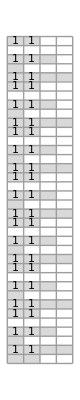
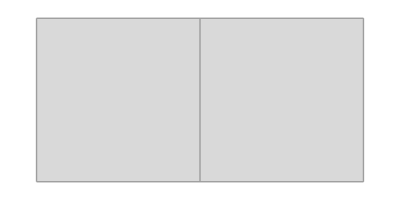
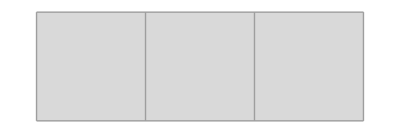
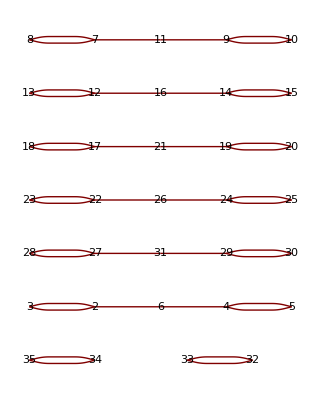
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[]
```

```mathematica
TestForUnusedRules
```

{{2},{AA→A,→AA}}

```mathematica
$SSSRuleSet
```

{AB→A,→B}

```mathematica
Length[$SSSEvolution]
```

212

```mathematica
$debug=True;
IdentifyPseudorepeating
```

3218. {AB→A,A→,→A} : No network after step -∞, now at 212

{}

```mathematica
$SSSNet
```

{}

```mathematica
TestForUnusedRules::usage="Usage:\nTestForUnusedRules\n\nReturns:\n{} ⇒ test does not apply\n{unused rules} ⇒ which rules weren't used, no jump possible since last rule was used\n{unused rules, target ruleset} ⇒ which rules weren't used & which ruleset to jump to";
```

```mathematica
?TestForUnusedRules
```

Usage:
TestForUnusedRules

Returns:
{} ⇒ test does not apply
{unused rules} ⇒ which rules weren't used, no jump possible since last rule was used
{unused rules, target ruleset} ⇒ which rules weren't used & which ruleset to jump to

```mathematica
SSSInitialize[{"A"->"B","B"->"BA",""->"A"},""]
SSSEvolve[20]
IdentifyPseudorepeating
```

True

OK

{True,{1,{3,2}}}

```mathematica
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

{1,{2,3}}

```mathematica
TestForUnusedRules
$SSSVerdict
```

{{3},{A→B,B→BAA}}

1

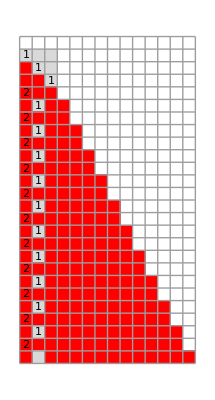


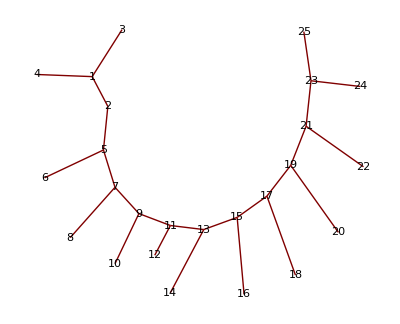
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Pseudorepeating

27

{{3},{A→B,B→BAA,→AA}}

```mathematica
SSS[{"A"->"B","B"->"BA",""->"AAA"},"",25]
SSSEvolve[200,EarlyReturn->True]
Length[$SSSEvolution]
TestForUnusedRules
```

```mathematica
SSSInitialize[{"A"->"B","B"->"BA","C"->"",""->"A"},"A"];
SSSEvolve[25]
TestForUnusedRules
```

Pseudorepeating

{{3,4},{A→B,B→BAA,→AAA}}

```mathematica
SSSInitialize[{"A"->"B","C"->"","B"->"BA"},"A"];
SSSEvolve[25]
TestForUnusedRules
```

Pseudorepeating

{2}

```mathematica
?TestForUnusedRules
```

Usage:
TestForUnusedRules

Returns:
{} ⇒ test does not apply
{unused rules} ⇒ which rules weren't used, no jump possible since last rule was used
{unused rules, target ruleset} ⇒ which rules weren't used & which ruleset to jump to

```mathematica
SSSInitialize[{"AB" -> "BBA", "B" -> "A"},"ABAB","Silent"];
```

```mathematica
SSSEvolve[269];
```

```mathematica
IdentifyPseudorepeating
```

{True,{exp,{5,∞}}}

```mathematica
SSSInitialize[{"AB" -> "BBA", "B" -> "A","A"->""},"ABAB","Silent"];
```

```mathematica
SSSEvolve[200];
Length[$SSSEvolution]
TestForUnusedRules
```

202

{{3},{AB→BBA,B→AA}}

```mathematica
MapAt[Style[#,Red]&,$SSSRuleSet,List/@First[%]]
```

{AB→BBA,B→A,A→}

#### TestAgainstKnownRuleSets (not yet in use)

TestAgainstKnownRuleSets[rs] returns the last ruleset to jump over, if the ruleset rs begins with a known ruleset.  (The jump will be to the ruleset following the one returned.)  The list of known rulesets, knownList, should be occasionally updated by human identification of results returned by the main loop of this program.  These results are printed and saved to file to avoid loss of information during crashes, and can be read in for treatment by the function testSSS.

```mathematica
(* SetDirectory["C:\\Users\\caviness\\Desktop\\Research"] *)
```

```mathematica
{d2List,expList,deadList}=ReadList["identifiedSSSs.txt"];
```

```mathematica
Last[d2List]
```

```mathematica
Length[d2List]
```

```mathematica
knownList=fromGeneralizedRank /@ Union[d2List,expList];
```

```mathematica
With[{rs=$SSSRuleSet},
Alternatives @@ (Take[rs,#]&/@Range[Length[rs]])]
```

```mathematica
TestAgainstKnownRuleSets[rs_List] := Module[{match,tailweight},
match=If[Length[#]==0,Return[#],First[#]]& @ Cases[knownList,Alternatives @@ (Take[rs,#]&/@Range[Length[rs]])];
tailweight=RuleSetWeight[Drop[rs,Length[match]]];
If[tailweight==0,match,Append[match,FromCharacterWeights[{tailweight}] -> ""]]
];
```

```mathematica
TestAgainstKnownRuleSets[{"AB"->"BBA","B"->"A"}]
```

```mathematica
TestAgainstKnownRuleSets[{"AB"->"BBA","B"->"A","A"->"B"}]
```

#### NonLengtheningRuleSetQ (more restrictive than ShorteningRuleSetQ, which is normally preferred)

If we’re planning on discarding all 1-dimensional cases anyway, we might as well strengthen the criteria for ShorteningRuleSetQ, testing instead for a non-growing ruleset.  If the state string stays the same length, it must sooner or later die out or begin to repeat, since there are a finite number of permutations of a finite number of characters.  The following function tests whether the ruleset has no lengthening rule:

```mathematica
NonLengtheningRuleSetQ[rs_List] := FreeQ[Union[Sign[Map[StringLength,rs,{2}] /. Rule->Subtract]],-1]
```

```mathematica
{#,NonLengtheningRuleSetQ[#]}& /@ {{"A"->""},{"A"->"A"},{"A"->"B","B"->"A"},{"A"->"B","B"->""},{"A"->"BC","B"->""}}//Grid[#,Alignment->Left]&
```

{A→} | True
{A→A} | True
{A→B,B→A} | True
{A→B,B→} | True
{A→BC,B→} | False

#### TestForNonFinalCreationRule (now defunct)

This test has now been retired, since TestForConflictingRules will always catch it automatically.  Any non-final creation rule will conflict with the first rule that follows it.

TestForNonFinalCreationRule[rs] tests whether a ruleset has a non-final “nothing→something” rule, returning the position of the problem and (if other than itself) the last ruleset in the current subsequence of the enumeration that has the same problem.  Such a ruleset is effectively equivalent to a lower-weight, previously seen ruleset, omitting all rules that follow the problem rule.  This is because a non-final “nothing→something” (creation) is guaranteed to prevent execution of any following rules.

How to "long-jump" past all rulesets having the same problem?  Given a tail weight w, append a string of w-1 copies of “A” to the rhs of the creation rule, then append a final “A”→“” rule.  This new ruleset will still have the problem rule, and it will still not be the final rule of the ruleset.  The very next ruleset will move the weight of this final rule into the creation rule, making it final, i.e., not problematic.  This is as far as can be safely jumped: we haven’t jumped over a ruleset in which the creation rule ceased to exist or ceased to be non-final.

Take 3:  Truncate the ruleset at the problematic creation rule, append “AA…A” (w-1 characters) its rhs, then tack on a final “A” → “” rule.

Take 4:  Truncate the ruleset at the problematic creation rule, append “AA…A” (w characters) its rhs.  This will be the first non-problematic ruleset that needs to be considered.  It has a creation rule, but that rule is now final; all earlier skipped rulesets have a non-final creation rule.

```mathematica
TestForNonFinalCreationRule[rs_List] := Module[{poslist,probpos,tail,tailweight,newrs},
poslist=Position[First /@ rs,""];                           (* list positions of creation (nothing-to-something) rules *)
If[Length[Flatten[poslist]]==0, Return[{}]];   (* No nothing-to-something rules found, nothing to skip *)
probpos=First@First@poslist;                                           (* position of first creation rule *)
If[probpos==Length[rs],Return[{}]];                         (* allowed final-position nothing->something rule, nothing to skip *)
tailweight=RuleSetWeight[rs⟦probpos+1;;⟧];     (* Take weight of tail, construct new final rule using it ... *)
newrs=rs⟦;;probpos⟧;
newrs⟦-1,-1⟧=StringJoin[newrs⟦-1,-1⟧,Table["A",{tailweight}]];
Return[{probpos,newrs}]
]
```

```mathematica
{#,Sequence@@With[{ans=TestForNonFinalCreationRule[#]},
Which[
ans=={},{},
Length[ans]==2,ans,
True,Print["Error, invalid return from test: ",ans]]
]}& /@ 
{{"A"->"B","B"->"A","B"->"BA"},
{"A"->"BB","C"->"C","AA"->"B",""->"A"},
{"A"->"BB","C"->"C",""->"A","B"->"A"},
{"A"->"BB",""->"A",""->"A"},
{"C"->"C",""->"ABA","AA"->"B",""->"A"},
{"A"->"A",""->"B","B"->"B"},
{"A"->"B","A"->"C",""->"B","C"->"AB"}}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","Problem at ","Jump to"}]& //
Grid[#,Alignment->Left]&
```

Ruleset | Problem at  | Jump to
{A→B,B→A,B→BA} |  | 
{A→BB,C→C,AA→B,→A} |  | 
{A→BB,C→C,→A,B→A} | 3 | {A→BB,C→C,→AAAA}
{A→BB,→A,→A} | 2 | {A→BB,→AA}
{C→C,→ABA,AA→B,→A} | 2 | {C→C,→ABAAAAAA}
{A→A,→B,B→B} | 2 | {A→A,→BAAAA}
{A→B,A→C,→B,C→AB} | 3 | {A→B,A→C,→BAAAAAA}

#### ToLeastWeight, ToCanonical (first renamed duplicate in enumeration not skipped over)

The long jumps serve an important role in accelerating the loop through the enumeration, but it will sometimes skip over the first occurence of a renamed duplicate.  For example, {“B” → “A”, “A” → “A”} has a lower weight than {“A” → “B”, “B” → “B”} and appears first in the full enumeration, but will be skipped over by the TestForRenamedRuleSet long jump.  The long jumps guarantee that only one example of each permutation of character names will be considered -- A Good Thing, but we may have to go farther in the loop before coming to a particular network of interest.  The following functions will then easily give the two main versions of interest:

```mathematica
ToCanonical[rs_List]:=Module[{unsortedchars,alphabetizedchars,reprules},
unsortedchars=DeleteDuplicates[Flatten[Characters/@Flatten[rs,∞,Rule]]];
alphabetizedchars=Characters[FromCharacterWeights[Range[Length[unsortedchars]]]];
reprules=Thread[unsortedchars->alphabetizedchars];
Map[StringReplace[#,reprules]&,rs,{2}]];
```

```mathematica
ToLeastWeight[rs_List] := Module[{weightsortedchars,alphabetizedchars,reprules},
weightsortedchars = First /@ Sort[Tally[Flatten[Characters /@ Flatten[rs,∞,Rule]]],Last[#1]≥Last[#2]&];
alphabetizedchars = Characters[FromCharacterWeights[Range[Length[weightsortedchars]]]];
reprules=Thread[weightsortedchars->alphabetizedchars];
Map[StringReplace[#,reprules]&,rs,{2}]
];
```

```mathematica
ToCanonical[{"B"->"A","A"->"A"}]
```

{A→B,B→B}

```mathematica
ToLeastWeight[ToCanonical[{"B"->"A","A"->"A"}]]
```

{B→A,A→A}

```mathematica
{"B"->"D","DA"->"AD","AD"->"AC","AC"->"CA","CA"->"BA"};
```

```mathematica
ToLeastWeight[%]
```

{D→B,BA→AB,AB→AC,AC→CA,CA→DA}

```mathematica
ToCanonical[%]
```

{A→B,BC→CB,CB→CD,CD→DC,DC→AC}

```mathematica
RuleSetWeight /@ {%%%,%%,%}
```

{40,36,50}

```mathematica
{#,ToCanonical[#]}& /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","ToCanonical"}]& //Grid[#,Alignment->Left]&
```

Ruleset | ToCanonical
{BB→BA,AA→AB,A→BA} | {AA→AB,BB→BA,B→AB}
{BAB→ABA,A→B,B→AA} | {ABA→BAB,B→A,A→BB}
{BAB→ABA,A→B,B→BAA} | {ABA→BAB,B→A,A→ABB}
{BBB→BA,AA→AB,BA→AAB} | {AAA→AB,BB→BA,AB→BBA}
{AAA→AB,BB→BA,B→BAA} | {AAA→AB,BB→BA,B→BAA}
{BBB→BA,AA→AB,A→BA} | {AAA→AB,BB→BA,B→AB}
{AAAB→BAA,AAA→BB,B→AAB} | {AAAB→BAA,AAA→BB,B→AAB}
{BAA→ABBB,BABB→ABA,A→AABB} | {ABB→BAAA,ABAA→BAB,B→BBAA}

```mathematica
RuleSetWeight /@ (ToCanonical/@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
})
```

{17,17,18,21,19,18,22,28}

These indicate in which weight class the (longjumping) iteration will find them.

```mathematica
RuleSetWeight/@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}
```

{16,16,18,21,19,18,22,29}

```mathematica
{#,ToLeastWeight[#]}& /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","ToLeastWeight"}]& //Grid[#,Alignment->Left]&
```

Ruleset | ToLeastWeight
{BB→BA,AA→AB,A→BA} | {BB→BA,AA→AB,A→BA}
{BAB→ABA,A→B,B→AA} | {BAB→ABA,A→B,B→AA}
{BAB→ABA,A→B,B→BAA} | {ABA→BAB,B→A,A→ABB}
{BBB→BA,AA→AB,BA→AAB} | {AAA→AB,BB→BA,AB→BBA}
{AAA→AB,BB→BA,B→BAA} | {AAA→AB,BB→BA,B→BAA}
{BBB→BA,AA→AB,A→BA} | {AAA→AB,BB→BA,B→AB}
{AAAB→BAA,AAA→BB,B→AAB} | {AAAB→BAA,AAA→BB,B→AAB}
{BAA→ABBB,BABB→ABA,A→AABB} | {ABB→BAAA,ABAA→BAB,B→BBAA}

```mathematica
RuleSetWeight /@ (ToLeastWeight /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
})
```

{16,16,18,21,19,18,22,28}

Only in first two cases would the (slow!) full enumeration find them one weight earlier.  Clearly for these examples and presumably for many other equally interesting cases, the exponentially accelerating loop has little cost for the huge benefits.

## Examples

### Examples from NKS

#### p. 90

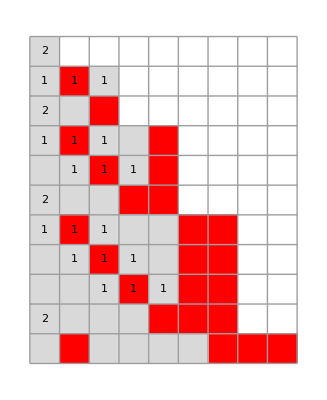
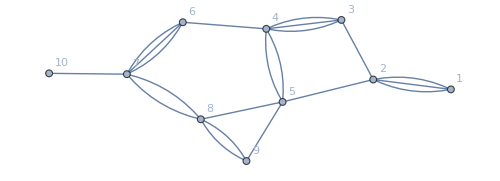
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 11

```mathematica
SSS[{"ABA"->"AAB","A"->"ABA"}, "A",10,EarlyReturn->True,SSSMax->25,NetMax->65,NetSize->500]
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
$SSSEvolution
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB}

```mathematica
$SSSNet//Sort
```

{1→2,1→2,1→2,2→3,2→5,3→4,3→4,3→4,4→5,4→5,4→6,5→8,5→9,6→7,6→7,6→7,7→8,7→8,7→10,8→9,8→9}

```mathematica
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

{{failed,1 | 3 | 6 | 10 | 15 | 21
2 | 3 | 4 | 5 | 6 | 
1 | 1 | 1 | 1 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}},{failed,2 | 4 | 7 | 11 | 16 | 22
2 | 3 | 4 | 5 | 6 | 
1 | 1 | 1 | 1 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}},{failed,
,{}},{failed,2 | 5 | 9 | 14 | 20
3 | 4 | 5 | 6 | 
1 | 1 | 1 |  | ,{1.,1.}}}

sssSummary: {}

distanceTallyAns: {{failed,1 | 2 | 4 | 7 | 11 | 16
1 | 2 | 3 | 4 | 5 | 
1 | 1 | 1 | 1 |  | 
0 | 0 | 0 |  |  | ,{Indeterminate,Indeterminate}},{2, riffling by ,1,: ,{1,1,1,1}}}

distanceTallySummary: {2}

No successful SSS tests

{True,2qq}

{2,{∞,∞}}

```mathematica
SSSEvolve[20]
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

2

{{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{failed,1
,{}},{2,{2,∞},2 | 5 | 9 | 14 | 20 | 27 | 35
3 | 4 | 5 | 6 | 7 | 8 | 
1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{2,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 2 | 4 | 7 | 11 | 16 | 22 | 29
1 | 2 | 3 | 4 | 5 | 6 | 7 | 
1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

{2,{∞,1}}

```mathematica
SSSEvolve[100]
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

2

{{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105 | 120 | 136
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106 | 121 | 137
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{failed,1
,{}},{2,{2,∞},2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 | 90 | 104 | 119
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{2,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79 | 92 | 106
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

{2,{∞,1}}

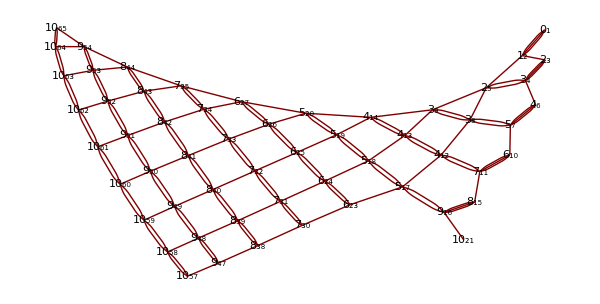

```mathematica
SSSDisplay[UseDistances->True,DistanceMax->10,NetMethod->{NoSSS,GraphPlot},NetSize->600]
```

```mathematica
SSSAnimateByDistance
```

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,2,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56 | 67 | 79
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
$SSSDistance
```

{0,1,2,3,2,4,5,3,3,6,7,4,4,4,8,9,5,5,5,5,10,11,6,6,6,6,6,12,13,7,7,7,7,7,7,14,15,8,8,8,8,8,8,8,16,17,9,9,9,9,9,9,9,9,18,19,10,10,10,10,10,10,10,10,10,20,21,11,11,11,11,11,11,11,11,11,11,22,23,12}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

{dim,2,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension@DistanceTally
```

{dim,2,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension /@ MergeIntervals /@ MinRulePositions
```

{{dim,2,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
CommonestHistoryPositions
```

Insufficient data

{}

```mathematica
SSSEvolve[100]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,2,66 | 78 | 91 | 105 | 120 | 136 | 153 | 171
12 | 13 | 14 | 15 | 16 | 17 | 18 | 
1 | 1 | 1 | 1 | 1 | 1 |  | }

#### p. 91a

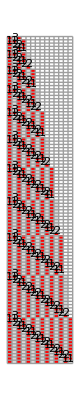
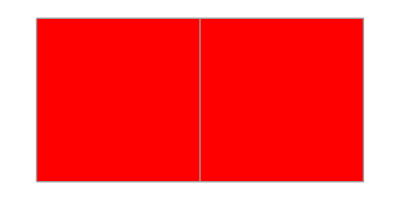

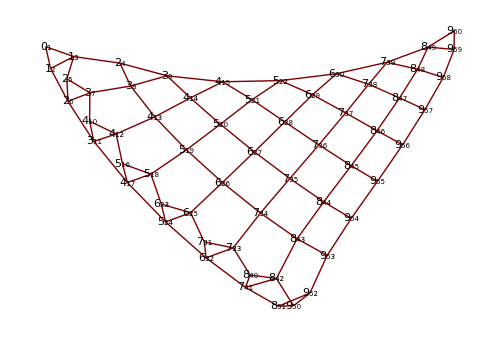
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
(*a*)SSS[{"BB"->"BA","AA"->"AB","A"->"BA"},"BAB",200,EarlyReturn->True,SSSMax->100,NetMax->60,NetSize->500,UseDistances->True]
```

```mathematica
IdentifyPseudorepeating
```

{{2,{1,∞},1 | 5 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{failed,
,{}},{2,{3,∞},3 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{3,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

```mathematica
SSSEvolve[500]
IdentifyPseudorepeating
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

2

{{2,{1,∞},1 | 5 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185 | 205 | 226 | 248 | 271 | 295 | 320 | 346 | 373 | 401 | 430 | 460 | 491 | 523 | 556 | 590 | 625 | 661 | 698
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186 | 206 | 227 | 249 | 272 | 296 | 321 | 347 | 374 | 402 | 431 | 461 | 492 | 524 | 557 | 591 | 626 | 662 | 699
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{74,∞},74 | 101 | 132 | 167 | 206 | 249 | 296 | 347 | 402 | 461 | 524 | 591 | 662
27 | 31 | 35 | 39 | 43 | 47 | 51 | 55 | 59 | 63 | 67 | 71 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | },{2,{3,∞},3 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186 | 206 | 227 | 249 | 272 | 296 | 321 | 347 | 374 | 402 | 431 | 461 | 492 | 524 | 557 | 591 | 626 | 662 | 699
3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{74,∞}},{2,{3,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185 | 205 | 226 | 248 | 271 | 295 | 320 | 346 | 373 | 401 | 430 | 460 | 491 | 523 | 556 | 590 | 625 | 661 | 698
2 | 3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

{2,{∞,1}}

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,2,2 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

{dim,2,3 | 6 | 11 | 17 | 24 | 32 | 41 | 51 | 62 | 74 | 87 | 101 | 116 | 132 | 149 | 167 | 186
3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension@DistanceTally
```

{dim,2,3 | 6 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
3 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
checkDimension/@MergeIntervals /@ MinRulePositions
```

{{dim,2,1 | 5 | 10 | 16 | 23 | 31 | 40 | 50 | 61 | 73 | 86 | 100 | 115 | 131 | 148 | 166 | 185
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
SSSEvolve[200];
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,2,74 | 101 | 132 | 167 | 206 | 249 | 296 | 347
27 | 31 | 35 | 39 | 43 | 47 | 51 | 
4 | 4 | 4 | 4 | 4 | 4 |  | }

#### p. 91b

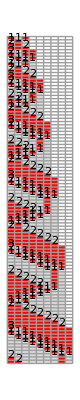
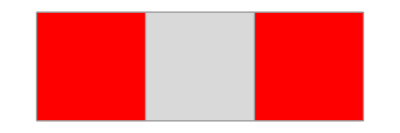
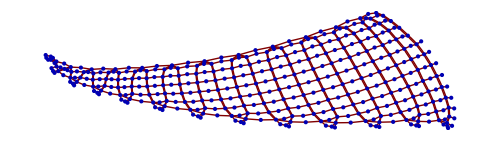
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 401

```mathematica
(*b*)SSS[{"BAB"->"ABA","A"->"B","B"->"AA"},"BAB",400,EarlyReturn->True,SSSMax->100,NetSize->500,VertexLabeling->Tooltip]
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
IdentifyPseudorepeating
```

{{2,{4,∞},4 | 13 | 26 | 43 | 64 | 89 | 118 | 151 | 188 | 229 | 274 | 323 | 376
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | },{2,{5,∞},5 | 14 | 27 | 44 | 65 | 90 | 119 | 152 | 189 | 230 | 275 | 324 | 377
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | },{failed,
,{}},{2,{12,∞},12 | 25 | 42 | 63 | 88 | 117 | 150 | 187 | 228 | 273 | 322 | 375 | 391
13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 16 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | -37 |  | }}

sssSummary: {{2,{4,∞}},{2,{5,∞}},{2,{12,∞}}}

match ({1,2,2,2,2,2,2,2}) with Partition[data,3], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 4 | 7 | 10 | 14 | 19 | 24 | 30 | 37 | 44 | 52 | 61 | 70 | 80 | 91 | 102 | 114 | 127 | 140 | 154 | 169 | 184 | 200 | 217 | 234 | 252 | 271
3 | 3 | 3 | 4 | 5 | 5 | 6 | 7 | 7 | 8 | 9 | 9 | 10 | 11 | 11 | 12 | 13 | 13 | 14 | 15 | 15 | 16 | 17 | 17 | 18 | 19 | 
0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 |  | },{2, riffling by ,3,: ,{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}}}

distanceTallySummary: {2}

{True,{2,{4,∞}}}

```mathematica
$SSSVerdict
```

2

```mathematica
SSSAnimateByDistance
```

```mathematica
SSSEvolve[200]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,2,5 | 14 | 27 | 44 | 65 | 90 | 119 | 152 | 189 | 230 | 275 | 324 | 377 | 434 | 495 | 560
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 57 | 61 | 65 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | }

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension[%]
```

{6,8,12,17,25,31,42,49,63,71,88,97,117,127,150,161,187,199,228,241,273,287,322,337,375,391,432,449,493,511,558,577}

{12,25,42,63,88,117,150,187,228,273,322,375,432,493,558,577}

{dim,2,12 | 25 | 42 | 63 | 88 | 117 | 150 | 187 | 228 | 273 | 322 | 375 | 432 | 493 | 558 | 577
13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 57 | 61 | 65 | 19 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | -46 |  | }

```mathematica
checkDimension[DistanceTally]
```

match ({2,2,2,2,2,2,2,2,2,2}) with Partition[data,3], starting at 1

{dim,2,4 | 7 | 10 | 14 | 19 | 24 | 30 | 37 | 44 | 52 | 61 | 70 | 80 | 91 | 102 | 114 | 127 | 140 | 154 | 169 | 184 | 200 | 217 | 234 | 252 | 271 | 290 | 310 | 331 | 352 | 374 | 397
3 | 3 | 4 | 5 | 5 | 6 | 7 | 7 | 8 | 9 | 9 | 10 | 11 | 11 | 12 | 13 | 13 | 14 | 15 | 15 | 16 | 17 | 17 | 18 | 19 | 19 | 20 | 21 | 21 | 22 | 23 | 
0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 |  | }

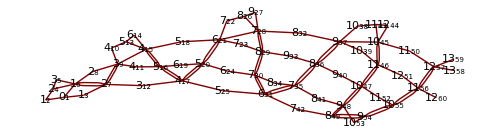

```mathematica
SSSDisplay[UseDistances->True,NetSize->500,NetMax->60,NetMethod->{GraphPlot,NoSSS}]
```

```mathematica
checkDimension/@ MergeIntervals /@ MinRulePositions
```

{{dim,2,4 | 13 | 26 | 43 | 64 | 89 | 118 | 151 | 188 | 229 | 274 | 323 | 376 | 433 | 494 | 559
9 | 13 | 17 | 21 | 25 | 29 | 33 | 37 | 41 | 45 | 49 | 53 | 57 | 61 | 65 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | }}

```mathematica
SSSEvolve[200]
checkDimension @ MergeIntervals @ CommonestHistoryPositions
```

Pseudorepeating

{dim,2,230 | 275 | 324 | 377 | 434 | 495 | 560 | 629 | 702 | 779 | 860 | 945
45 | 49 | 53 | 57 | 61 | 65 | 69 | 73 | 77 | 81 | 85 | 
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 |  | }

#### p. 91c

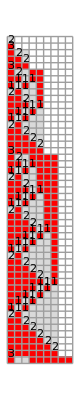
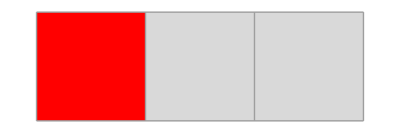
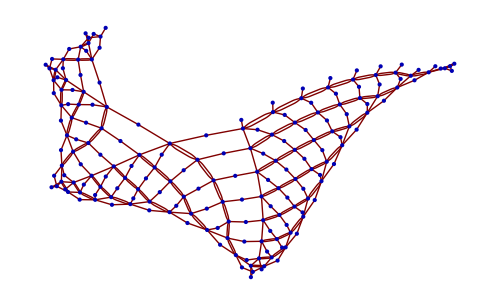
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 201

```mathematica
(*c*)SSS[{"BAB"->"ABA","A"->"B","B"->"BAA"},"A",200,EarlyReturn->True,SSSMax->50,NetSize->500,VertexLabeling->Tooltip]
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
SSSEvolve[1300]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

{{3,{5,∞},5 | 18 | 49 | 106 | 197 | 330 | 513 | 754 | 1061 | 1442
13 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 381 | 
18 | 26 | 34 | 42 | 50 | 58 | 66 | 74 |  | 
8 | 8 | 8 | 8 | 8 | 8 | 8 |  |  | },{3,{6,∞},6 | 19 | 50 | 107 | 198 | 331 | 514 | 755 | 1062 | 1443
13 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 381 | 
18 | 26 | 34 | 42 | 50 | 58 | 66 | 74 |  | 
8 | 8 | 8 | 8 | 8 | 8 | 8 |  |  | },{failed,331 | 514 | 755 | 1062 | 1443
183 | 241 | 307 | 381 | 
58 | 66 | 74 |  | ,{1.13793,1.12121}},{3,{5,∞},5 | 17 | 48 | 105 | 196 | 329 | 512 | 753 | 1060 | 1403
12 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 343 | 
19 | 26 | 34 | 42 | 50 | 58 | 66 | 36 |  | 
7 | 8 | 8 | 8 | 8 | 8 | -30 |  |  | }}

sssSummary: {{3,{5,∞}},{3,{6,∞}},{3,{5,∞}}}

match ({-2,3,1,1,1,1,1,1,1}) with Partition[data,2], starting at 1

distanceTallyAns: {{3,{1,∞},1 | 2 | 5 | 9 | 13 | 16 | 22 | 29 | 40 | 51 | 67 | 82 | 103 | 126 | 156 | 183 | 218 | 257 | 305 | 348 | 401
1 | 3 | 4 | 4 | 3 | 6 | 7 | 11 | 11 | 16 | 15 | 21 | 23 | 30 | 27 | 35 | 39 | 48 | 43 | 53 | 
2 | 1 | 0 | -1 | 3 | 1 | 4 | 0 | 5 | -1 | 6 | 2 | 7 | -3 | 8 | 4 | 9 | -5 | 10 |  | 
-1 | -1 | -1 | 4 | -2 | 3 | -4 | 5 | -6 | 7 | -4 | 5 | -10 | 11 | -4 | 5 | -14 | 15 |  |  | },{failed}}

distanceTallySummary: {3}

{True,{3,{5,∞}}}

```mathematica
toReducedRank@$SSSRuleSet
```

916513216150

```mathematica
toReducedRank@ToCanonical[$SSSRuleSet]
```

792482090026

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{3,6,19,50,107,198,331,514}

{6,19,50,107,198,331,514}

{failed,6 | 19 | 50 | 107 | 198 | 331 | 514
13 | 31 | 57 | 91 | 133 | 183 | 
18 | 26 | 34 | 42 | 50 |  | 
8 | 8 | 8 | 8 |  |  | 
0 | 0 | 0 |  |  |  | ,{Indeterminate,Indeterminate}}

```mathematica
SSSEvolve[800]
```

Pseudorepeating

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{2,5,11,17,38,48,91,105,178,196,307,329,486,512,723,753,1026,1060,1403,1441}

{5,17,48,105,196,329,512,753,1060,1403}

{dim,3,5 | 17 | 48 | 105 | 196 | 329 | 512 | 753 | 1060 | 1403
12 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 343 | 
19 | 26 | 34 | 42 | 50 | 58 | 66 | 36 |  | 
7 | 8 | 8 | 8 | 8 | 8 | -30 |  |  | }

```mathematica
MinRulePositions
MergeIntervals /@ %
checkDimension/@%
```

{{2,5,18,49,106,197,330,513,754,1061,1442}}

{{5,18,49,106,197,330,513,754,1061,1442}}

{{dim,3,5 | 18 | 49 | 106 | 197 | 330 | 513 | 754 | 1061 | 1442
13 | 31 | 57 | 91 | 133 | 183 | 241 | 307 | 381 | 
18 | 26 | 34 | 42 | 50 | 58 | 66 | 74 |  | 
8 | 8 | 8 | 8 | 8 | 8 | 8 |  |  | }}

```mathematica
SSSEvolve[1200]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,3,331 | 514 | 755 | 1062 | 1443 | 1906 | 2459 | 3110
183 | 241 | 307 | 381 | 463 | 553 | 651 | 
58 | 66 | 74 | 82 | 90 | 98 |  | 
8 | 8 | 8 | 8 | 8 |  |  | }

```mathematica
checkDimension[DistanceTally]
```

match ({3,1,1,1,1,1,1,1,1,1,1}) with Partition[data,2], starting at 2

{dim,3,2 | 5 | 9 | 13 | 16 | 22 | 29 | 40 | 51 | 67 | 82 | 103 | 126 | 156 | 183 | 218 | 257 | 305 | 348 | 401 | 460 | 530 | 593 | 668 | 751 | 847
3 | 4 | 4 | 3 | 6 | 7 | 11 | 11 | 16 | 15 | 21 | 23 | 30 | 27 | 35 | 39 | 48 | 43 | 53 | 59 | 70 | 63 | 75 | 83 | 96 | 
1 | 0 | -1 | 3 | 1 | 4 | 0 | 5 | -1 | 6 | 2 | 7 | -3 | 8 | 4 | 9 | -5 | 10 | 6 | 11 | -7 | 12 | 8 | 13 |  | 
-1 | -1 | 4 | -2 | 3 | -4 | 5 | -6 | 7 | -4 | 5 | -10 | 11 | -4 | 5 | -14 | 15 | -4 | 5 | -18 | 19 | -4 | 5 |  |  | }

#### p. 91d

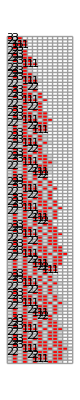
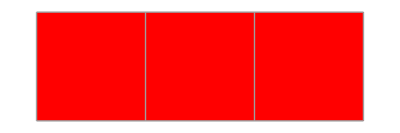
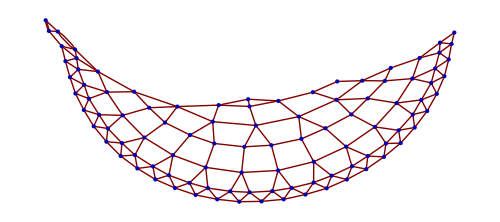
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 101

```mathematica
(*d*)SSS[{"BBB"->"BA","AA"->"AB","BA"->"AAB"},"BAB",100,EarlyReturn->True,SSSMax->100,VertexLabeling->Tooltip,NetSize->500]
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
SSSEvolve[300]
```

OK

```mathematica
SSSAnimateByDistance
```

```mathematica
?*Distance*
```

Global`SSSAnimateByDistance

SSSAnimateByDistance:=Module[{g,mx=Length[DistanceTally]},g=SSSDisplay[UseDistances→True,VertexLabeling→True,NetMethod→{GraphPlot,NoSSS}]⟦1,1,1,1⟧;Animate[Graphics[g/.Text[Framed[Subscript[n,s_Style],_List],node_]:>Text[Framed[Subscript[n,s],{Background→Green,FrameStyle→Black,FrameMargins→Automatic},RoundingRadius→10],node]/.Text[Framed[Subscript[m:Except[n,_Integer],s_Style],_List],node_]:>Point[node],ImageSize→Large],{n,1,mx,1,Appearance→Labeled,AnimationRate→1,AnimationRunning→True}]]

```mathematica
IdentifyPseudorepeating
```

match ({-1,8,16,32,64}) with Partition[data,3], starting at 1

match ({7,16,32,64,128}) with Partition[data,2], starting at 1

{{failed,3 | 9 | 14 | 20 | 29 | 33 | 42 | 47 | 56 | 61 | 72 | 76 | 85 | 90 | 101 | 106 | 115 | 120 | 131 | 136 | 145 | 150 | 163 | 167 | 176 | 181 | 192 | 197 | 206 | 211 | 224 | 229 | 238 | 243 | 254 | 259 | 268 | 273 | 286 | 291 | 300 | 305 | 316 | 321 | 330 | 335 | 350 | 354 | 363 | 368 | 379 | 384 | 393 | 398 | 411 | 416 | 425 | 430 | 441 | 446 | 455 | 460 | 475 | 480 | 489 | 494 | 505 | 510 | 519 | 524 | 537 | 542 | 551 | 556 | 567 | 572 | 581 | 586 | 601 | 606 | 615 | 620 | 631 | 636 | 645 | 650 | 663 | 668 | 677 | 682 | 693 | 698 | 707 | 712 | 729 | 733 | 742 | 747 | 758 | 763 | 772 | 777 | 790 | 795 | 804 | 809 | 820 | 825 | 834 | 839 | 854 | 859 | 868 | 873 | 884 | 889 | 898 | 903 | 916 | 921 | 930 | 935 | 946 | 951 | 960 | 965 | 982 | 987 | 993
6 | 5 | 6 | 9 | 4 | 9 | 5 | 9 | 5 | 11 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 17 | 4 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 15 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 13 | 5 | 9 | 5 | 11 | 5 | 9 | 5 | 17 | 5 | 6 | 
-1 | 1 | 3 | -5 | 5 | -4 | 4 | -4 | 6 | -7 | 5 | -4 | 6 | -6 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -9 | 5 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -11 | 5 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -10 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -10 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 12 | -13 | 5 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 10 | -10 | 4 | -4 | 6 | -6 | 4 | -4 | 8 | -8 | 4 | -4 | 6 | -6 | 4 | -4 | 12 | -12 | 1 |  | ,{-1.,3.,-1.66667,-1.,-0.8,-1.,-1.,-1.5,-1.16667,-0.714286,-0.8,-1.5,-1.,-0.666667,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.125,-0.555556,-0.8,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.1,-0.454545,-0.8,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.,-0.4,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.,-0.4,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-3.,-1.08333,-0.384615,-0.8,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-2.5,-1.,-0.4,-1.,-1.5,-1.,-0.666667,-1.,-2.,-1.,-0.5,-1.,-1.5,-1.,-0.666667,-1.,-3.,-1.,-0.0833333}},{exp,{2,∞},2 | 9 | 14 | 20 | 26 | 39 | 53 | 67 | 96 | 126 | 156 | 217 | 279 | 341 | 466 | 592 | 718 | 971
7 | 5 | 6 | 6 | 13 | 14 | 14 | 29 | 30 | 30 | 61 | 62 | 62 | 125 | 126 | 126 | 253 | 
-2 | 1 | 0 | 7 | 1 | 0 | 15 | 1 | 0 | 31 | 1 | 0 | 63 | 1 | 0 | 127 |  | ,{-8,2,2,2}},{failed,
,{}},{exp,{3,∞},3 | 9 | 16 | 29 | 43 | 72 | 102 | 163 | 225 | 350 | 476 | 729 | 983
6 | 7 | 13 | 14 | 29 | 30 | 61 | 62 | 125 | 126 | 253 | 254 | 
1 | 6 | 1 | 15 | 1 | 31 | 1 | 63 | 1 | 127 | 1 |  | ,{16/7,2,2,2}}}

sssSummary: {{exp,{2,∞}},{exp,{3,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 107
2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{0,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

CAUTION: SSS tests and distance tally tests disagree: {{exp,exp},{2}}

{True,2xexp,{{2,∞}}}

```mathematica
SSSAnimateByDistance
```

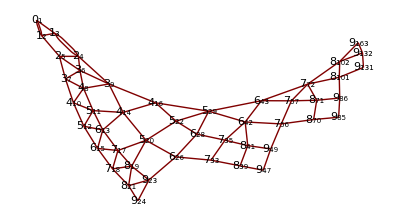

```mathematica
SSSDisplay[UseDistances->True,DistanceMax->9,NetMethod->{NoSSS,GraphPlot}]
```

```mathematica
SSSEvolve[1300]
```

OK

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{2,7,9,14,20,26,39,53,67,96,126,156,217,279,341,466,592,718,971,1225,1479,1988}

{2,9,14,20,26,39,53,67,96,126,156,217,279,341,466,592,718,971,1225,1479,1988}

match ({-1,8,16,32,64,128}) with Partition[data,3], starting at 1

{exp,2 | 9 | 14 | 20 | 26 | 39 | 53 | 67 | 96 | 126 | 156 | 217 | 279 | 341 | 466 | 592 | 718 | 971 | 1225 | 1479 | 1988
7 | 5 | 6 | 6 | 13 | 14 | 14 | 29 | 30 | 30 | 61 | 62 | 62 | 125 | 126 | 126 | 253 | 254 | 254 | 509 | 
-2 | 1 | 0 | 7 | 1 | 0 | 15 | 1 | 0 | 31 | 1 | 0 | 63 | 1 | 0 | 127 | 1 | 0 | 255 |  | ,{-8,2,2,2,2}}

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{3,5,9,16,29,43,72,102,163,225,350,476,729,983,1492}

{3,9,16,29,43,72,102,163,225,350,476,729,983,1492}

match ({7,16,32,64,128,256}) with Partition[data,2], starting at 1

{exp,3 | 9 | 16 | 29 | 43 | 72 | 102 | 163 | 225 | 350 | 476 | 729 | 983 | 1492
6 | 7 | 13 | 14 | 29 | 30 | 61 | 62 | 125 | 126 | 253 | 254 | 509 | 
1 | 6 | 1 | 15 | 1 | 31 | 1 | 63 | 1 | 127 | 1 | 255 |  | ,{16/7,2,2,2,2}}

```mathematica
checkDimension[DistanceTally]
```

{dim,2,3 | 5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 93 | 107 | 122 | 138 | 155 | 173
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
FindSequenceFunction[DistanceTally,n]
```

1/2 (4+n+n^2)

```mathematica
$SSSRuleUsage
```

{1473,2960,1497}

```mathematica
Length/@MinRulePositions
Length/@ MergeIntervals/@MinRulePositions
```

{1473}

{748}

```mathematica
CommonestHistoryPositions
```

Insufficient data

{}

```mathematica
SSSEvolve[9200]
```

OK

```mathematica
CommonestHistoryPositions
MergeIntervals[%]
checkDimension[%]
```

{277,590,1223,2496,5049}

{277,590,1223,2496,5049}

{failed,277 | 590 | 1223 | 2496 | 5049
313 | 633 | 1273 | 2553 | 
320 | 640 | 1280 |  | ,{2.,2.}}

```mathematica
checkDimension[{277,590,1223,2496,5049,10162}]
```

{exp,2,277,277 | 590 | 1223 | 2496 | 5049 | 10162
313 | 633 | 1273 | 2553 | 5113 | 
320 | 640 | 1280 | 2560 |  | ,{2,2,2}}

This seems to indicate that the SSS exhibits exponential behavior while the network is 2-d and its growing edge is 1-d!  But it certainly looks exponential.

```mathematica
DistanceTally
```

{3,5,8,12,17,23,30,38,47,57,68,80,93,107,122,138,155,173}

```mathematica
Length[DistanceTally]
```

18

```mathematica
testForFractionalExponential
```

#### p. 91e

This network makes me doubt any definition of dimension.  According to the number of nodes a certain distance from the origin, it has dimension 2.  But visually the network is becoming too dense for 2-d or indeed any dimension, along the “ruffled” edge.  How?  Of course, none of these are effects of future events on the “inner” edge, so maybe there’s no problem.

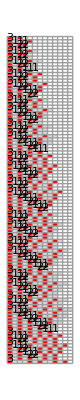
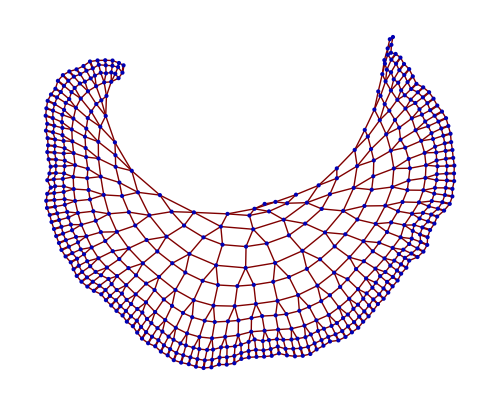
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 601

```mathematica
(*e*)SSS[{"AAA"->"AB","BB"->"BA","B"->"BAA"},"BAB",600,EarlyReturn->True,SSSMax->100,VertexLabeling->Tooltip,NetSize->500]
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
SSSEvolve[500]
```

OK

```mathematica
IdentifyPseudorepeating
```

match ({5,10,20,40,80}) with Partition[data,3], starting at 1

match ({13,20,40,80,160}) with Partition[data,2], starting at 2

{{failed,1 | 4 | 7 | 11 | 14 | 19 | 22 | 27 | 30 | 36 | 39 | 44 | 47 | 54 | 57 | 62 | 65 | 72 | 75 | 80 | 83 | 91 | 94 | 99 | 102 | 109 | 112 | 117 | 120 | 129 | 132 | 137 | 140 | 147 | 150 | 155 | 158 | 167 | 170 | 175 | 178 | 185 | 188 | 193 | 196 | 206 | 209 | 214 | 217 | 224 | 227 | 232 | 235 | 244 | 247 | 252 | 255 | 262 | 265 | 270 | 273 | 284 | 287 | 292 | 295 | 302 | 305 | 310 | 313 | 322 | 325 | 330 | 333 | 340 | 343 | 348 | 351 | 362 | 365 | 370 | 373 | 380 | 383 | 388 | 391 | 400 | 403 | 408 | 411 | 418 | 421 | 426 | 429 | 441 | 444 | 449 | 452 | 459 | 462 | 467 | 470 | 479 | 482 | 487 | 490 | 497 | 500 | 505 | 508 | 519 | 522 | 527 | 530 | 537 | 540 | 545 | 548 | 557 | 560 | 565 | 568 | 575 | 578 | 583 | 586 | 599 | 602 | 607 | 610 | 617 | 620 | 625 | 628 | 637 | 640 | 645 | 648 | 655 | 658 | 663 | 666 | 677 | 680 | 685 | 688 | 695 | 698 | 703 | 706 | 715 | 718 | 723 | 726 | 733 | 736 | 741 | 744 | 757 | 760 | 765 | 768 | 775 | 778 | 783 | 786 | 795 | 798 | 803 | 806 | 813 | 816 | 821 | 824 | 835 | 838 | 843 | 846 | 853 | 856 | 861 | 864 | 873 | 876 | 881 | 884 | 891 | 894 | 899 | 902 | 916 | 919 | 924 | 927 | 934 | 937 | 942 | 945 | 954 | 957 | 962 | 965 | 972 | 975 | 980 | 983 | 994 | 997 | 1002 | 1005 | 1012 | 1015 | 1020 | 1023 | 1032 | 1035 | 1040 | 1043 | 1050 | 1053 | 1058 | 1061 | 1074 | 1077 | 1082 | 1085 | 1092 | 1095 | 1100
3 | 3 | 4 | 3 | 5 | 3 | 5 | 3 | 6 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 8 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 10 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 12 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 13 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 13 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 14 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 11 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 9 | 3 | 5 | 3 | 7 | 3 | 5 | 3 | 13 | 3 | 5 | 3 | 7 | 3 | 5 | ,{1.,1.33333,0.75,1.66667,0.6,1.66667,0.6,2.,0.5,1.66667,0.6,2.33333,0.428571,1.66667,0.6,2.33333,0.428571,1.66667,0.6,2.66667,0.375,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.33333,0.3,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.,0.25,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.33333,0.230769,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.33333,0.230769,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.66667,0.214286,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.66667,0.272727,1.66667,0.6,2.33333,0.428571,1.66667,0.6,3.,0.333333,1.66667,0.6,2.33333,0.428571,1.66667,0.6,4.33333,0.230769,1.66667,0.6,2.33333,0.428571,1.66667}},{exp,{2,∞},2 | 5 | 8 | 15 | 23 | 31 | 48 | 66 | 84 | 121 | 159 | 197 | 274 | 352 | 430 | 587 | 745 | 903
3 | 3 | 7 | 8 | 8 | 17 | 18 | 18 | 37 | 38 | 38 | 77 | 78 | 78 | 157 | 158 | 158 | 
0 | 4 | 1 | 0 | 9 | 1 | 0 | 19 | 1 | 0 | 39 | 1 | 0 | 79 | 1 | 0 |  | ,{2,2,2,2}},{failed,
,{}},{exp,{7,∞},4 | 7 | 11 | 18 | 35 | 53 | 90 | 128 | 205 | 283 | 440 | 598 | 915
3 | 4 | 7 | 17 | 18 | 37 | 38 | 77 | 78 | 157 | 158 | 317 | 
1 | 3 | 10 | 1 | 19 | 1 | 39 | 1 | 79 | 1 | 159 |  | ,{20/13,2,2,2}}}

sssSummary: {{exp,{2,∞}},{exp,{7,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

CAUTION: SSS tests and distance tally tests disagree: {{exp,exp},{2}}

{True,2xexp,{{2,∞}}}

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
checkDimension@DistanceTally
```

{2,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSEvolve[1000]
```

OK

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

match ({5,10,20,40,80,160}) with Partition[data,3], starting at 1

{exp,2 | 5 | 8 | 15 | 23 | 31 | 48 | 66 | 84 | 121 | 159 | 197 | 274 | 352 | 430 | 587 | 745 | 903 | 1220 | 1538
3 | 3 | 7 | 8 | 8 | 17 | 18 | 18 | 37 | 38 | 38 | 77 | 78 | 78 | 157 | 158 | 158 | 317 | 318 | 
0 | 4 | 1 | 0 | 9 | 1 | 0 | 19 | 1 | 0 | 39 | 1 | 0 | 79 | 1 | 0 | 159 | 1 |  | ,{2,2,2,2,2}}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

match ({4,11,20,40,80,160}) with Partition[data,2], starting at 1

{exp,4 | 7 | 11 | 18 | 35 | 53 | 90 | 128 | 205 | 283 | 440 | 598 | 915 | 1233
3 | 4 | 7 | 17 | 18 | 37 | 38 | 77 | 78 | 157 | 158 | 317 | 318 | 
1 | 3 | 10 | 1 | 19 | 1 | 39 | 1 | 79 | 1 | 159 | 1 |  | ,{11/4,20/11,2,2,2}}

```mathematica
checkDimension@DistanceTally
```

{dim,2,3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66 | 78 | 91 | 105 | 120
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSAnimateByDistance
```

```mathematica
$SSSRuleUsage
```

{639,633,328}

```mathematica
CommonestHistoryPositions
```

Insufficient data

{}

#### p. 91f

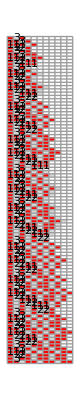
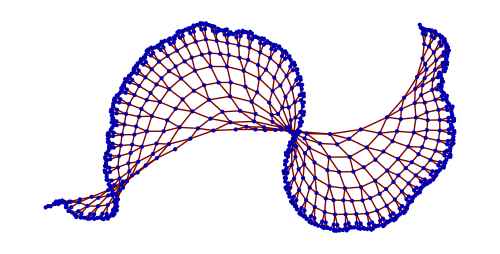
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 801

```mathematica
(*f*)SSS[{"BBB"->"BA","AA"->"AB","A"->"BA"},"BAB",800,EarlyReturn->True,SSSMax->100,VertexLabeling->Tooltip,NetSize->500]
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
SSSEvolve[500]
```

OK

```mathematica
IdentifyPseudorepeating
```

match ({6,12,24,48,96}) with Partition[data,3], starting at 1

match ({16,24,48,96,192}) with Partition[data,2], starting at 2

{{failed,4 | 8 | 13 | 19 | 23 | 29 | 33 | 39 | 44 | 50 | 54 | 62 | 66 | 72 | 76 | 84 | 88 | 94 | 98 | 106 | 111 | 117 | 121 | 129 | 133 | 139 | 143 | 153 | 157 | 163 | 167 | 175 | 179 | 185 | 189 | 199 | 203 | 209 | 213 | 221 | 225 | 231 | 235 | 245 | 250 | 256 | 260 | 268 | 272 | 278 | 282 | 292 | 296 | 302 | 306 | 314 | 318 | 324 | 328 | 340 | 344 | 350 | 354 | 362 | 366 | 372 | 376 | 386 | 390 | 396 | 400 | 408 | 412 | 418 | 422 | 434 | 438 | 444 | 448 | 456 | 460 | 466 | 470 | 480 | 484 | 490 | 494 | 502 | 506 | 512 | 516 | 528 | 533 | 539 | 543 | 551 | 555 | 561 | 565 | 575 | 579 | 585 | 589 | 597 | 601 | 607 | 611 | 623 | 627 | 633 | 637 | 645 | 649 | 655 | 659 | 669 | 673 | 679 | 683 | 691 | 695 | 701 | 705 | 719 | 723 | 729 | 733 | 741 | 745 | 751 | 755 | 765 | 769 | 775 | 779 | 787 | 791 | 797 | 801 | 813 | 817 | 823 | 827 | 835 | 839 | 845 | 849 | 859 | 863 | 869 | 873 | 881 | 885 | 891 | 895 | 909 | 913 | 919 | 923 | 931 | 935 | 941 | 945 | 955 | 959 | 965 | 969 | 977 | 981 | 987 | 991 | 1003 | 1007 | 1013 | 1017 | 1025 | 1029 | 1035 | 1039 | 1049 | 1053 | 1059 | 1063 | 1071 | 1075 | 1081 | 1085 | 1099 | 1104 | 1110 | 1114 | 1122 | 1126 | 1132 | 1136 | 1146 | 1150 | 1156 | 1160 | 1168 | 1172 | 1178 | 1182 | 1194 | 1198 | 1204 | 1208 | 1216 | 1220 | 1226 | 1230 | 1240 | 1244 | 1250 | 1254 | 1262 | 1266 | 1272 | 1276 | 1290 | 1294 | 1298
4 | 5 | 6 | 4 | 6 | 4 | 6 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 8 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 5 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 12 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 10 | 4 | 6 | 4 | 8 | 4 | 6 | 4 | 14 | 4 | 4 | ,{1.25,1.2,0.666667,1.5,0.666667,1.5,0.833333,1.2,0.666667,2.,0.5,1.5,0.666667,2.,0.5,1.5,0.666667,2.,0.625,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.5,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.416667,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.285714,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.285714,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.357143,1.2,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.,0.333333,1.5,0.666667,2.,0.5,1.5,0.666667,2.5,0.4,1.5,0.666667,2.,0.5,1.5,0.666667,3.5,0.285714,1.}},{exp,{3,∞},3 | 7 | 16 | 26 | 36 | 57 | 79 | 101 | 146 | 192 | 238 | 331 | 425 | 519 | 708 | 898 | 1088
4 | 9 | 10 | 10 | 21 | 22 | 22 | 45 | 46 | 46 | 93 | 94 | 94 | 189 | 190 | 190 | 
5 | 1 | 0 | 11 | 1 | 0 | 23 | 1 | 0 | 47 | 1 | 0 | 95 | 1 | 0 |  | ,{2,2,2,2}},{failed,
,{}},{exp,{7,∞},3 | 7 | 12 | 19 | 40 | 62 | 107 | 153 | 246 | 340 | 529 | 719 | 1100
4 | 5 | 7 | 21 | 22 | 45 | 46 | 93 | 94 | 189 | 190 | 381 | 
1 | 2 | 14 | 1 | 23 | 1 | 47 | 1 | 95 | 1 | 191 |  | ,{3/2,2,2,2}}}

sssSummary: {{exp,{3,∞}},{exp,{7,∞}}}

distanceTallyAns: {{2,{1,∞},1 | 3 | 5 | 9 | 15 | 22 | 30 | 39 | 49 | 60 | 72 | 85 | 99 | 114
2 | 2 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 
0 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2, riffling by ,1,: ,{0,2,2,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

CAUTION: SSS tests and distance tally tests disagree: {{exp,exp},{2}}

{True,2xexp,{{3,∞}}}

```mathematica
SSSEvolve[500]
```

OK

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{2,3,7,16,26,36,57,79,101,146,192,238,331,425,519,708,898,1088,1469}

{3,7,16,26,36,57,79,101,146,192,238,331,425,519,708,898,1088,1469}

match ({6,12,24,48,96}) with Partition[data,3], starting at 1

{exp,3 | 7 | 16 | 26 | 36 | 57 | 79 | 101 | 146 | 192 | 238 | 331 | 425 | 519 | 708 | 898 | 1088 | 1469
4 | 9 | 10 | 10 | 21 | 22 | 22 | 45 | 46 | 46 | 93 | 94 | 94 | 189 | 190 | 190 | 381 | 
5 | 1 | 0 | 11 | 1 | 0 | 23 | 1 | 0 | 47 | 1 | 0 | 95 | 1 | 0 | 191 |  | ,{2,2,2,2}}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

match ({3,15,24,48,96,192}) with Partition[data,2], starting at 1

{exp,3 | 7 | 12 | 19 | 40 | 62 | 107 | 153 | 246 | 340 | 529 | 719 | 1100 | 1482
4 | 5 | 7 | 21 | 22 | 45 | 46 | 93 | 94 | 189 | 190 | 381 | 382 | 
1 | 2 | 14 | 1 | 23 | 1 | 47 | 1 | 95 | 1 | 191 | 1 |  | ,{5,8/5,2,2,2}}

```mathematica
checkDimension@DistanceTally
```

{dim,2,3 | 5 | 9 | 15 | 22 | 30 | 39 | 49 | 60 | 72 | 85 | 99 | 114 | 130
2 | 4 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
$SSSRuleUsage
```

{596,590,614}

```mathematica
CommonestHistoryPositions
MergeIntervals[%]
checkDimension[%]
```

Insufficient data

{}

{}

{failed,
,{}}

```mathematica
checkDimension@{238,519,1088,2233,4530,9131}
```

{exp,2,238,238 | 519 | 1088 | 2233 | 4530 | 9131
281 | 569 | 1145 | 2297 | 4601 | 
288 | 576 | 1152 | 2304 |  | ,{2,2,2}}

#### p. 91g

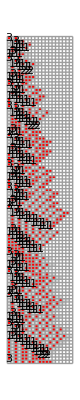
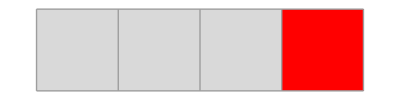
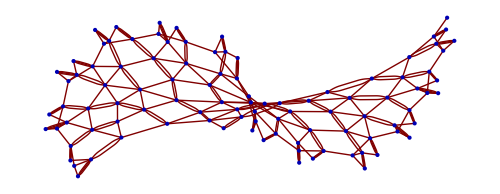
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

OK

```mathematica
(*g*)SSS[{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},"BAB",100,VertexLabeling->Tooltip,NetSize->500]
SSSEvolve[1000]
```

```mathematica
SSSEvolve[1000]
```

OK

```mathematica
SSSEvolve[4000]
```

OK

```mathematica
IdentifyPseudorepeating
```

No successful SSS tests

{True,2}

```mathematica
SSSEvolve[1000]
```

OK

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
SSSEvolve[1000]
IdentifyPseudorepeating
```

```mathematica
Length[$SSSEvolution]
```

15000

```mathematica
SSSEvolve[1899]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

13000

```mathematica
SSSEvolve[1899]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

14899

```mathematica
SSSEvolve[101]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

15000

```mathematica
SSSEvolve[1000]
Length[$SSSEvolution]
IdentifyPseudorepeating
```

OK

20000

No successful SSS tests

{True,2qq}

```mathematica
RiffleDistanceTally
```

{2, riffling by ,2,: ,{3,3,4,4,4,4,4,4}}

```mathematica
IdentifyPseudorepeating
```

No successful SSS tests

{True,2qq}

```mathematica
Differences[DistanceTally]
```

{3,4,6,7,10,11,14,15,18,19}

```mathematica
Differences[DistanceTally,1,2]
```

{7,10,13,17,21,25,29,33,37}

```mathematica
MaxStateLengthPositions
MergeIntervals[%]
checkDimension[%]
```

{2,3,8,9,17,19,24,44,49,54,55,93,133,195,197,265,291,356,406,408,557,676,770,1012,1281,1487,1492,1493,2949,4037,4039,5583,7318,7719,7720,13569,14603}

{9,24,93,197,557,1012,2949,5583,7318}

{failed,9 | 24 | 93 | 197 | 557 | 1012 | 2949 | 5583 | 7318
15 | 69 | 104 | 360 | 455 | 1937 | 2634 | 1735 | 
54 | 35 | 256 | 95 | 1482 | 697 | -899 |  | 
-19 | 221 | -161 | 1387 | -785 | -1596 |  |  | 
240 | -382 | 1548 | -2172 | -811 |  |  |  | 
-622 | 1930 | -3720 | 1361 |  |  |  |  | 
2552 | -5650 | 5081 |  |  |  |  |  | ,{-2.21395,-0.899292}}

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Differences[MergeIntervals@MaxStateLengthPositions,n],{n,0,6}]]
```

1971.33 | 2734.66
913.625 | 1026.43
245.714 | 724.156
-158.833 | 1001.1
-315.4 | 1367.27
-262.75 | 2551.23
661. | 5609.86

```mathematica
Grid[Table[LinearModelFit[Differences[MergeIntervals@MaxStateLengthPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

-2398.67+874. x | 0.766088
-718.107+362.607 x | 0.748801
289.857-11.0357 x | 0.00108379
776.667-267.286 x | 0.249499
852.2-389.2 x | 0.20257
-337.5+29.9 x | 0.000228924
-1868.+1264.5 x | 0.0508082

```mathematica
Grid[Table[N@Ratios@Differences[MergeIntervals[MaxStateLengthPositions],n],{n,0,6}]]
```

2.66667 | 3.875 | 2.11828 | 2.82741 | 1.81688 | 2.91403 | 1.89318 | 1.31076
4.6 | 1.50725 | 3.46154 | 1.26389 | 4.25714 | 1.35983 | 0.658694 | 
0.648148 | 7.31429 | 0.371094 | 15.6 | 0.47031 | -1.28981 |  | 
-11.6316 | -0.728507 | -8.61491 | -0.56597 | 2.03312 |  |  | 
-1.59167 | -4.05236 | -1.4031 | 0.373389 |  |  |  | 
-3.10289 | -1.92746 | -0.36586 |  |  |  |  | 
-2.21395 | -0.899292 |  |  |  |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[MergeIntervals@MaxStateLengthPositions,n],{n,0,6}]]
```

2.42778 | 0.806241
2.44405 | 1.61266
3.85234 | 6.48473
-3.90157 | 5.88183
-1.66843 | 1.8192
-1.79874 | 1.37305
-1.55662 | 0.929603

```mathematica
Grid[Table[LinearModelFit[N@Ratios@Differences[MergeIntervals@MaxStateLengthPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

3.39333-0.214568 x | 0.424962
4.06164-0.404398 x | 0.293452
5.35162-0.428367 x | 0.0152727
-12.1491+2.74919 x | 0.546167
-3.80454+0.854442 x | 0.367667
-4.53577+1.36852 x | 0.993408
-3.52861+1.31466 x | 1.

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{6,10,28,66,205,417,1110,2200,5734,11260}

{10,28,66,205,417,1110,2200,5734,11260}

{failed,10 | 28 | 66 | 205 | 417 | 1110 | 2200 | 5734 | 11260
18 | 38 | 139 | 212 | 693 | 1090 | 3534 | 5526 | 
20 | 101 | 73 | 481 | 397 | 2444 | 1992 |  | 
81 | -28 | 408 | -84 | 2047 | -452 |  |  | 
-109 | 436 | -492 | 2131 | -2499 |  |  |  | 
545 | -928 | 2623 | -4630 |  |  |  |  | 
-1473 | 3551 | -7253 |  |  |  |  |  | ,{-2.41073,-2.04252}}

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Differences[MergeIntervals@DistanceLastPositions,n],{n,0,6}]]
```

2336.67 | 3821.31
1406.25 | 2033.29
786.857 | 1001.01
328.667 | 886.256
-106.6 | 1671.33
-597.5 | 3057.63
-1725. | 5406.41

```mathematica
Differences[Differences[MergeIntervals@DistanceLastPositions,3],1,2]
```

{327,-56,1639,-368}

```mathematica
Grid[Table[LinearModelFit[Differences[MergeIntervals@DistanceLastPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

-3270.92+1121.52 x | 0.646022
-1774.29+706.786 x | 0.724983
-774.+390.214 x | 0.709151
21.8667+87.6571 x | 0.0342393
818.9-308.5 x | 0.0851776
2396.-1197.4 x | 0.255599
4055.-2890. x | 0.285745

```mathematica
Grid[Table[N@Ratios@Differences[MergeIntervals[DistanceLastPositions],n],{n,0,6}]]
```

2.8 | 2.35714 | 3.10606 | 2.03415 | 2.66187 | 1.98198 | 2.60636 | 1.96373
2.11111 | 3.65789 | 1.52518 | 3.26887 | 1.57287 | 3.2422 | 1.56367 | 
5.05 | 0.722772 | 6.58904 | 0.825364 | 6.15617 | 0.815057 |  | 
-0.345679 | -14.5714 | -0.205882 | -24.369 | -0.220811 |  |  | 
-4. | -1.12844 | -4.3313 | -1.17269 |  |  |  | 
-1.70275 | -2.82651 | -1.76515 |  |  |  |  | 
-2.41073 | -2.04252 |  |  |  |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[MergeIntervals@DistanceLastPositions,n],{n,0,6}]]
```

2.43891 | 0.423983
2.42026 | 0.93773
3.35973 | 2.86208
-7.94257 | 11.0789
-2.65811 | 1.7461
-2.09814 | 0.631558
-2.22662 | 0.260359

```mathematica
Mean[{2.43891,2.42026,3.35973}]
```

2.73963

```mathematica
Grid[Table[LinearModelFit[N@Ratios@Differences[MergeIntervals@DistanceLastPositions,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

2.83279-0.0875278 x | 0.255709
2.76683-0.0866438 x | 0.0398406
4.42355-0.303948 x | 0.0394734
-5.0782-0.954788 x | 0.0185679
-3.97788+0.527907 x | 0.152344
-2.03574-0.0312011 x | 0.00244068
-2.77893+0.368203 x | 1.

```mathematica
checkDimension@DistanceTally
```

{failed,1 | 4 | 8 | 14 | 21 | 31 | 42 | 56 | 71 | 89 | 108
3 | 4 | 6 | 7 | 10 | 11 | 14 | 15 | 18 | 19 | 
1 | 2 | 1 | 3 | 1 | 3 | 1 | 3 | 1 |  | 
1 | -1 | 2 | -2 | 2 | -2 | 2 | -2 |  |  | 
-2 | 3 | -4 | 4 | -4 | 4 | -4 |  |  |  | 
5 | -7 | 8 | -8 | 8 | -8 |  |  |  |  | 
-12 | 15 | -16 | 16 | -16 |  |  |  |  |  | 
27 | -31 | 32 | -32 |  |  |  |  |  |  | 
-58 | 63 | -64 |  |  |  |  |  |  |  | ,{-1.08621,-1.01587}}

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Differences[DistanceTally,n],{n,0,5}]]
```

33.7 | 30.1553
9.77778 | 5.1908
1.875 | 0.991031
0.285714 | 1.88982
0.166667 | 3.92003
1.2 | 8.04363

```mathematica
Grid[Table[LinearModelFit[Differences[DistanceTally,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,6}]]
```

-23.3091+10.6273 x | 0.940963
0.4+1.87273 x | 0.990539
1.52778+0.05 x | 0.0198529
0.75-0.166667 x | 0.0448718
0.142857-0.142857 x | 0.00623053
3.26667-1.02857 x | 0.0562175
-0.5-0.7 x | 0.00444162

```mathematica
Grid[Table[N@Ratios@Differences[DistanceTally,n],{n,0,3}]]
```

4. | 2. | 1.75 | 1.5 | 1.47619 | 1.35484 | 1.33333 | 1.26786 | 1.25352
1.33333 | 1.5 | 1.16667 | 1.42857 | 1.1 | 1.27273 | 1.07143 | 1.2 | 
2. | 0.5 | 3. | 0.333333 | 3. | 0.333333 | 3. |  | 
-1. | -2. | -1. | -1. | -1. | -1. |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[DistanceTally,n],{n,0,2}]]
```

1.77064 | 0.870873
1.25909 | 0.153539
1.7381 | 1.31183

```mathematica
Grid[Table[LinearModelFit[N@Ratios@Differences[DistanceTally,n],x,x][#]&/@{"BestFit","RSquared"},{n,0,2}]]
```

2.95071-0.236014 x | 0.550842
1.42444-0.036745 x | 0.343645
1.35714+0.0952381 x | 0.0245965

```mathematica
RiffleDistanceTally
```

dim riffling by 2: {3,3,4,4,4,4,4}

```mathematica
Grid[{Range[1,9],Differences[DistanceTally]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
3 | 4 | 6 | 7 | 10 | 11 | 14 | 15 | 18

```mathematica
$SSSRuleUsage
```

{6048,8,3044}

```mathematica
checkDimension/@ MergeIntervals /@ MinRulePositions
```

{{failed,11 | 28 | 99 | 205 | 567 | 1110 | 2963 | 5734
17 | 71 | 106 | 362 | 543 | 1853 | 2771 | 
54 | 35 | 256 | 181 | 1310 | 918 |  | 
-19 | 221 | -75 | 1129 | -392 |  |  | 
240 | -296 | 1204 | -1521 |  |  |  | 
-536 | 1500 | -2725 |  |  |  |  | ,{-2.79851,-1.81667}}}

```mathematica
MergeIntervals /@ MinRulePositions
```

{{11,28,99,205,567,1110,2963,5734}}

```mathematica
Grid[Table[N@Ratios@Differences[First[MinRulePositions],n],{n,0,4}]]
```

2.54545 | 3.53571 | 2.07071 | 2.76585 | 1.95767 | 2.66937 | 1.9352
4.17647 | 1.49296 | 3.41509 | 1.5 | 3.41252 | 1.49541 | 
0.648148 | 7.31429 | 0.707031 | 7.23757 | 0.700763 |  | 
-11.6316 | -0.339367 | -15.0533 | -0.34721 |  |  | 
-1.23333 | -4.06757 | -1.26329 |  |  |  |

```mathematica
Grid[Table[{Mean[#],StandardDeviation[#]}&@N@Ratios@Differences[First[MinRulePositions],n],{n,0,6}]]
```

StandardDeviation::shlen: The argument {-2.07515} should have at least two elements.

2.49714 | 0.57322
2.58208 | 1.22177
3.32156 | 3.61
-6.84287 | 7.63397
-2.18806 | 1.62777
-2.30759 | 0.694266
-2.07515 | StandardDeviation[{-2.07515}]

Just taking ratios, we see that the first row wavers around 2 or 2.5, sounds like exponential growth, although it doesn’t stabilize and in fact the fluctuation becomes worse in successive rows.  Try clumping by twos to adjust for fluctuation:

```mathematica
Grid[Table[N@Ratios@Differences[Total/@Partition[First[MinRulePositions],2],n],{n,0,2}]]
```

7.79487 | 5.51645 | 5.18605
5.18113 | 5.11289 | 
5.09657 |  |

Or just skip every other one before forming ratos of repeated differences:

```mathematica
Last/@Partition[First[MinRulePositions],2]
```

{28,205,1110,5734}

```mathematica
Grid[Table[N@Ratios@Differences[Last/@Partition[First[MinRulePositions],2],n],{n,0,2}]]
```

7.32143 | 5.41463 | 5.16577
5.11299 | 5.10939 | 
5.10852 |  |

Either way, it’s very tempting to call this exponential dimension 5.10/2=2.55.

```mathematica
CommonestHistoryPositions
MergeIntervals[%]
checkDimension[%]
```

Insufficient data

{}

{}

{failed,
,{}}

#### p. 91h

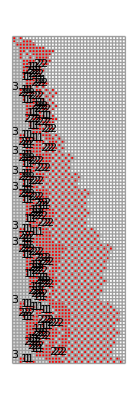
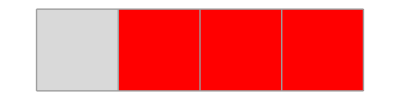
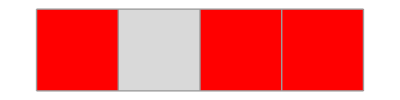
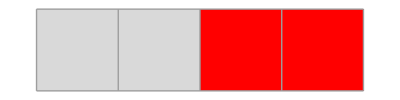
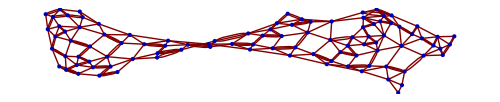
-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Length[$SSSEvolution]: 1101

```mathematica
(*h*)SSS[{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"},"BAB",100,VertexLabeling->Tooltip,NetSize->500]
SSSEvolve[1000];
"Length[$SSSEvolution]: "<>ToString@Length[$SSSEvolution]
```

```mathematica
SSSEvolve[6000]
```

$Aborted

```mathematica
SSSDisplay[VertexLabeling->Tooltip,NetSize->500]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
MaxStateLengthPositions
MergeIntervals@%
checkDimension[%]
```

{2,3,4,5,18,31,32,33,37,38,43,44,48,49,60,61,62,65,66,85,86,101,102,103,140,141,146,155,156,157,186,187,192,245,246,251,406,407,408,409,410,411,416,539,540,545,702,841,842,847,988,993,1132,1133,1138,1285,1286,1291,1428,1429,1430,1435,1590,1595,1746,1747,1752,1925,1930,2079,2080,2081,2086,2251,2256,2449,2450,2455,2750,2751,2752,2753,2754,2755,2760,3023,3024,3029,3326,3605,3606,3611,3892,3897,4176,4177,4182,4469,4470,4475,4752,4753,4754,4759,5054,5059,5350,5351,5356,5669,5674,5963,5964,5965,5970,6275,6280,6613,6614,6619,7054,7055,7056,7057,7058,7059,7064}

{5,18,33,38,44,49,62,66,86,103,146,157,192,251,416,545,702,847,993,1138,1291,1435,1595,1752,1930,2086,2256,2455,2760,3029,3326,3611,3897,4182,4475,4759,5059,5356,5674,5970,6280,6619,7059}

```mathematica
DistanceLastPositions
MergeIntervals[%]
checkDimension@%
```

{9,14,29,391,679,2721,3289,7011}

{14,29,391,679,2721,3289,7011}

{failed,14 | 29 | 391 | 679 | 2721 | 3289 | 7011
15 | 362 | 288 | 2042 | 568 | 3722 | 
347 | -74 | 1754 | -1474 | 3154 |  | 
-421 | 1828 | -3228 | 4628 |  |  | 
2249 | -5056 | 7856 |  |  |  | ,{-2.24811,-1.5538}}

```mathematica
checkDimension@DistanceTally
```

{failed,1 | 4 | 9 | 16 | 25 | 38 | 55 | 78 | 111
3 | 5 | 7 | 9 | 13 | 17 | 23 | 33 | 
2 | 2 | 2 | 4 | 4 | 6 | 10 |  | 
0 | 0 | 2 | 0 | 2 | 4 |  |  | 
0 | 2 | -2 | 2 | 2 |  |  |  | 
2 | -4 | 4 | 0 |  |  |  |  | 
-6 | 8 | -4 |  |  |  |  |  | ,{-1.33333,-0.5}}

```mathematica
RiffleDistanceTally
```

{failed}

```mathematica
$SSSRuleUsage
```

{3526,3529,45}

```mathematica
MinRulePositions
MergeIntervals /@ %
checkDimension/@%
```

{{1,3,4,16,30,36,42,47,59,64,82,99,136,153,182,239,396,525,680,826,972,1117,1269,1414,1572,1729,1906,2063,2232,2429,2726,2995,3290,3576,3862,4147,4439,4724,5022,5319,5636,5933,6242,6579,7016,7425,7860,8286,8712}}

{{4,16,30,36,42,47,59,64,82,99,136,153,182,239,396,525,680,826,972,1117,1269,1414,1572,1729,1906,2063,2232,2429,2726,2995,3290,3576,3862,4147,4439,4724,5022,5319,5636,5933,6242,6579,7016,7425,7860,8286,8712}}

```mathematica
CommonestHistoryPositions
```

{1729,1906,2063,2232,2429,5319,5636,5933,6242,6579}

```mathematica
MergeIntervals[%]
checkDimension[%]
```

{1729,1906,2063,2232,2429,5319,5636,5933,6242,6579}

{failed,1729 | 1906 | 2063 | 2232 | 2429 | 5319 | 5636 | 5933 | 6242 | 6579
177 | 157 | 169 | 197 | 2890 | 317 | 297 | 309 | 337 | 
-20 | 12 | 28 | 2693 | -2573 | -20 | 12 | 28 |  | 
32 | 16 | 2665 | -5266 | 2553 | 32 | 16 |  |  | 
-16 | 2649 | -7931 | 7819 | -2521 | -16 |  |  |  | 
2665 | -10580 | 15750 | -10340 | 2505 |  |  |  |  | 
-13245 | 26330 | -26090 | 12845 |  |  |  |  |  | ,{-1.98792,-0.990885,-0.492334}}

### Other Examples ctrl+shift+[ ]

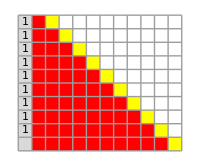
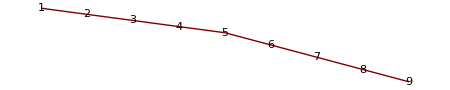
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSS[{"A"->"AB"},"ABC",9,SSSSize->200,NetSize->450]
```

```mathematica
SSSEvolve[10]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

{{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1,{3,1},3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }}

sssSummary: {{1,{1,1}},{1,{2,1}},{1,{3,1}},{1,{2,1}}}

distanceTallyAns: {{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{2, riffling by ,1,: ,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

distanceTallySummary: {1,2}

{True,{1,{1,1}}}

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }}

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{1,{3,1},3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
checkDimension[DistanceTally]
```

{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

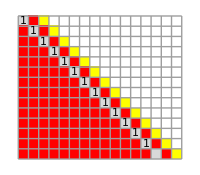
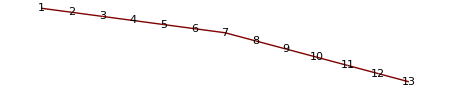
-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

```mathematica
SSS[{"A"->"BA"},"ABC",13,SSSSize->200,NetSize->450]
```

```mathematica
IdentifyPseudorepeating
```

{{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1,{4,1},4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }}

sssSummary: {{1,{1,1}},{1,{2,1}},{1,{4,1}},{1,{2,1}}}

distanceTallyAns: {{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{2, riffling by ,1,: ,{0,0,0,0,0,0,0,0,0,0,0}}}

distanceTallySummary: {1,2}

{True,{1,{1,1}}}

```mathematica
SSSEvolve[5]
```

1

```mathematica
checkDimension@MergeIntervals@DistanceLastPositions
```

{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{1,{2,1},2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }}

```mathematica
checkDimension[DistanceTally]
```

{1,{1,1},1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }

```mathematica
RiffleDistanceTally
```

{2, riffling by ,1,: ,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### Manual constructing a ruleset of specified dimension

#### Constructing a constant-width band (1-d case): one rule that creates a diagonal path across a SSS, creating and destroying a series of cells, and would die out without another rule to start over. Here the number of As defines the width of the band, but the band remains one-dimensional.

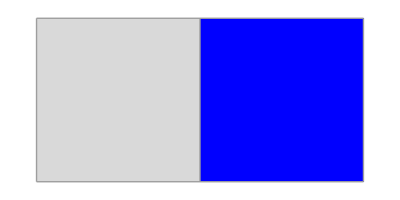
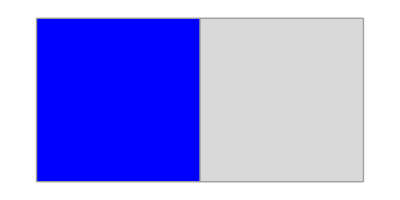
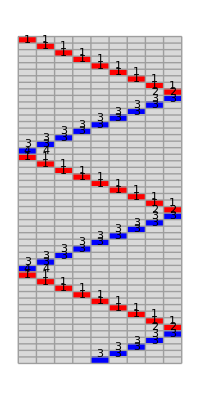
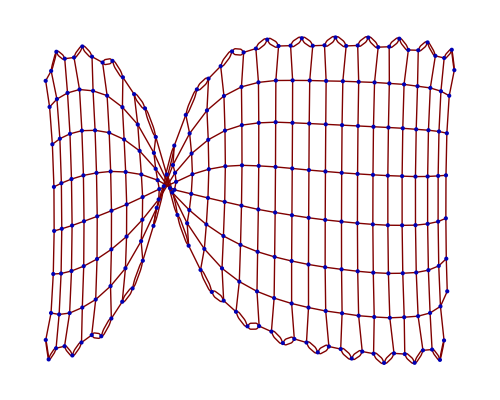
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
SSS[{"BA"->"AB","AB"->"AF","AF"->"FA","FA"->"BA"},"BAAAAAAAA",250,SSSMax->50,SSSSize->{200,400},NetSize->{500,400},VertexLabeling->False,ShowRule->Left]
```

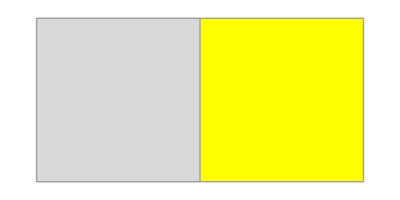
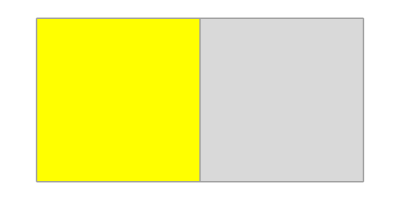
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
SSSDisplay[NetMax->200,SSSSize->{200,400},NetSize->{500,400},VertexLabeling->False,ShowRule->Left]
```

```mathematica
IdentifyPseudorepeating
```

{{1,{20,20},20 | 40 | 60 | 80 | 100 | 120 | 140 | 160 | 180 | 200 | 220 | 240
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | },{failed,
,{}},{1,{1,20},1 | 21 | 41 | 61 | 81 | 101 | 121 | 141 | 161 | 181 | 201 | 221 | 241
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | },{1,{22,20},22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | }}

sssSummary: {{1,{20,20}},{1,{1,20}},{1,{22,20}}}

distanceTallyAns: {{1,{10,5},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 65 | 75 | 85 | 95 | 105 | 115 | 125 | 135 | 145 | 155 | 165 | 175 | 185 | 195 | 205 | 215
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{exp, riffling by ,4,: ,{1,3/4,1/2,1/4,0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

distanceTallySummary: {1,exp}

{True,{1,{1,20}}}

```mathematica
SSSEvolve[100]
```

Repeating

```mathematica
IdentifyPseudorepeating
```

{{1,{{10,20},10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | }},{failed,
,{}},{1,{1,20},1 | 21 | 41 | 61 | 81 | 101 | 121 | 141 | 161 | 181 | 201 | 221 | 241 | 261 | 281 | 301 | 321 | 341
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | },{1,{22,20},22 | 42 | 62 | 82 | 102 | 122 | 142 | 162 | 182 | 202 | 222 | 242 | 262 | 282 | 302 | 322 | 342
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | }}

sssSummary: {{1,{{10,20},10 | 30 | 50 | 70 | 90 | 110 | 130 | 150 | 170 | 190 | 210 | 230 | 250 | 270 | 290 | 310 | 330 | 350
20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | }},{1,{1,20}},{1,{22,20}}}

distanceTallyAns: {{1,{10,5},1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 65 | 75 | 85 | 95 | 105 | 115 | 125 | 135 | 145 | 155 | 165 | 175 | 185 | 195 | 205 | 215 | 225 | 235 | 245 | 255 | 265 | 275 | 285 | 295 | 305 | 315
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{exp, riffling by ,4,: ,{1,3/4,1/2,1/4,0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

distanceTallySummary: {1,exp}

{True,{1,{1,20}}}

```mathematica
{$SSSVerdict,{$SSSRepetitionInterval,$SSSRepetitionStart}}
```

{Repeating,{20,1}}

#### This related ruleset changes width depending on the number of Bs, and edge behavior depending on the number of As, but is still one-dimensional:

```mathematica
SSS[{"BA"->"AB","AB"->"AC","AC"->"CA","C"->"B"},"BBBAAAAA",125,SSSMax->75,SSSSize->{200,400},NetSize->{500,400},VertexLabeling->Tooltip,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
IdentifyPseudorepeating
```

{{failed,36 | 72 | 106
36 | 34 | ,{0.944444}},{failed,
,{}},{failed,1 | 37 | 73 | 109
36 | 36 | 36 | ,{1.,1.}},{failed,34 | 70 | 94 | 111
36 | 24 | 17 | ,{0.666667,0.708333}}}

sssSummary: {}

distanceTallyAns: {{1,{3,3},1 | 3 | 6 | 10 | 16 | 24 | 35 | 47 | 59 | 71 | 83 | 95
2 | 3 | 4 | 6 | 8 | 11 | 12 | 12 | 12 | 12 | 12 | },{failed}}

distanceTallySummary: {1}

No successful SSS tests

{True,1qq}

```mathematica
SSSEvolve[100]
```

Repeating

```mathematica
SSSEvolve[100]
```

Repeating

```mathematica
IdentifyPseudorepeating
```

{{1,{24,36},24 | 60 | 96 | 132 | 168 | 204 | 240 | 276 | 304
36 | 36 | 36 | 36 | 36 | 36 | 36 | 28 | },{failed,
,{}},{1,{1,36},1 | 37 | 73 | 109 | 145 | 181 | 217 | 253 | 289 | 325
36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | },{1,{34,36},34 | 70 | 106 | 142 | 178 | 214 | 250 | 286 | 310
36 | 36 | 36 | 36 | 36 | 36 | 36 | 24 | }}

sssSummary: {{1,{24,36}},{1,{1,36}},{1,{34,36}}}

distanceTallyAns: {{1,{3,3},1 | 3 | 6 | 10 | 16 | 24 | 35 | 47 | 59 | 71 | 83 | 95 | 107 | 119 | 131 | 143 | 155 | 167 | 179 | 191 | 203 | 215 | 227 | 239 | 251 | 263 | 275 | 287 | 299
2 | 3 | 4 | 6 | 8 | 11 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | },{exp, riffling by ,2,: ,{2,5/3,1,1/5,0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

distanceTallySummary: {1,exp}

{True,{1,{1,36}}}

#### It’s not necessary to do the diagonal retrace to restart, since a new rule can simply restart the next right diagonal.

```mathematica
SSS[{"BA"->"AB","A"->"BA"},"AAAAAAAAA",250,SSSMax->50,SSSSize->{200,400},NetSize->{500,400},VertexLabeling->False,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
IdentifyPseudorepeating
```

{{1,{1,10},1 | 11 | 21 | 31 | 41 | 51 | 61 | 71 | 81 | 91 | 101 | 111 | 121 | 131 | 141 | 151 | 161 | 171 | 181 | 191 | 201 | 211 | 221 | 231 | 241
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{1,{2,10},2 | 12 | 22 | 32 | 42 | 52 | 62 | 72 | 82 | 92 | 102 | 112 | 122 | 132 | 142 | 152 | 162 | 172 | 182 | 192 | 202 | 212 | 222 | 232 | 242
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{1,{71,10},71 | 81 | 91 | 101 | 111 | 121 | 131 | 141 | 151 | 161 | 171 | 181 | 191 | 201 | 211 | 221 | 231 | 241
10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | },{1,{11,2},11 | 13 | 23 | 33 | 43 | 53 | 63 | 73 | 83 | 93 | 103 | 113 | 123 | 133 | 143 | 153 | 163 | 173 | 183 | 193 | 203 | 213 | 223 | 233 | 243
2 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | }}

sssSummary: {{1,{1,10}},{1,{2,10}},{1,{71,10}},{1,{11,2}}}

distanceTallyAns: {{1,{7,4},1 | 2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 55 | 64 | 73 | 82 | 91 | 100 | 109 | 118 | 127 | 136 | 145 | 154 | 163 | 172 | 181 | 190 | 199
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | 9 | },{exp, riffling by ,4,: ,{1,3/4,1/2,1/4,0,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}}

distanceTallySummary: {1,exp}

{True,{1,{1,10}}}

```mathematica
$SSSVerdict
```

1

#### 2-d: Incrementing the number of As at the beginning of each diagonal stroke turns the constant width band into a 2-d case.

```mathematica
SSS[{"BA"->"AB","A"->"BAA"},"A",50,SSSMax->50,SSSSize->{200,400},NetSize->{500,400},VertexLabeling->False,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
IdentifyPseudorepeating
```

{{2,{1,∞},1 | 4 | 8 | 13 | 19 | 26 | 34 | 43 | 53 | 64 | 76 | 89 | 103 | 118 | 134 | 151 | 169 | 188 | 208 | 229
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{2,∞},2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65 | 77 | 90 | 104 | 119 | 135 | 152 | 170 | 189 | 209 | 230
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{53,∞},53 | 64 | 76 | 89 | 103 | 118 | 134 | 151 | 169 | 188 | 208 | 229
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2,{3,∞},3 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63 | 75 | 88 | 102 | 117 | 133 | 150 | 168 | 187 | 207 | 228
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

sssSummary: {{2,{1,∞}},{2,{2,∞}},{2,{53,∞}},{2,{3,∞}}}

match ({1,1,1,1,1,1,1,1,1}) with Partition[data,2], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 3 | 5 | 8 | 11 | 15 | 19 | 24 | 29 | 35 | 41 | 48 | 55 | 63 | 71 | 80 | 89 | 99 | 109 | 120
2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 | 7 | 7 | 8 | 8 | 9 | 9 | 10 | 10 | 11 | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 |  | },{2, riffling by ,2,: ,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

distanceTallySummary: {2}

{True,{2,{1,∞}}}

#### Exponential: Adding an extra A at the beginning of each diagonal stroke makes each pass one step longer, and turns the network into an exponential case.

```mathematica
SSS[{"BA"->"AAB","A"->"BA"},"A",1000,SSSMax->50,SSSSize->{200,200},NetSize->{500,200},VertexLabels->None,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
SSSDisplay[NetMax->850,SSSMax->50,SSSSize->{200,200},NetSize->{500,200},VertexLabels->None,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
IdentifyPseudorepeating
```

{{exp,{1,∞},1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 |  | ,{2,2,2,2,2,2}},{exp,{3,∞},3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 266
3 | 5 | 9 | 17 | 33 | 65 | 129 | 2 | 
2 | 4 | 8 | 16 | 32 | 64 | -127 |  | ,{2,2,2,2,2,-127/64}},{failed,
,{}},{exp,{2,∞},2 | 5 | 10 | 19 | 36 | 69 | 134 | 263
3 | 5 | 9 | 17 | 33 | 65 | 129 | 
2 | 4 | 8 | 16 | 32 | 64 |  | ,{2,2,2,2,2}}}

sssSummary: {{exp,{1,∞}},{exp,{3,∞}},{exp,{2,∞}}}

distanceTallyAns: {{failed,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89 | 175
1 | 2 | 3 | 6 | 11 | 22 | 43 | 86 | 
1 | 1 | 3 | 5 | 11 | 21 | 43 |  | 
0 | 2 | 2 | 6 | 10 | 22 |  |  | 
2 | 0 | 4 | 4 | 12 |  |  |  | 
-2 | 4 | 0 | 8 |  |  |  |  | 
6 | -4 | 8 |  |  |  |  |  | ,{-0.666667,-2.}},{exp, riffling by ,2,: ,{4,4,4,4}}}

distanceTallySummary: {exp}

{True,{exp,{1,∞}}}

```mathematica
SSSEvolve[750]
IdentifyPseudorepeating
```

exp

{{exp,{1,∞},1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521 | 1034
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 513 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 |  | ,{2,2,2,2,2,2,2,2}},{exp,{3,∞},3 | 6 | 11 | 20 | 37 | 70 | 135 | 264 | 521 | 1034 | 1036
3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 513 | 2 | 
2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | -511 |  | ,{2,2,2,2,2,2,2,-511/256}},{failed,264 | 521 | 1034
257 | 513 | ,{1.99611}},{exp,{2,∞},2 | 5 | 10 | 19 | 36 | 69 | 134 | 263 | 520
3 | 5 | 9 | 17 | 33 | 65 | 129 | 257 | 
2 | 4 | 8 | 16 | 32 | 64 | 128 |  | ,{2,2,2,2,2,2}}}

sssSummary: {{exp,{1,∞}},{exp,{3,∞}},{exp,{2,∞}}}

match ({2,8,32,128}) with Partition[data,2], starting at 1

distanceTallyAns: {{exp,{1,∞},1 | 2 | 4 | 7 | 13 | 24 | 46 | 89 | 175 | 346
1 | 2 | 3 | 6 | 11 | 22 | 43 | 86 | 171 | 
1 | 1 | 3 | 5 | 11 | 21 | 43 | 85 |  | ,{4,4,4}},{exp, riffling by ,2,: ,{4,4,4,4,4}}}

distanceTallySummary: {exp}

{True,{exp,{1,∞}}}

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

{exp,2 | 5 | 10 | 19 | 36 | 69 | 134
3 | 5 | 9 | 17 | 33 | 65 | 
2 | 4 | 8 | 16 | 32 |  | ,{2,2,2,2}}

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{exp,3 | 6 | 11 | 20 | 37 | 70 | 135 | 137
3 | 5 | 9 | 17 | 33 | 65 | 2 | 
2 | 4 | 8 | 16 | 32 | -63 |  | ,{2,2,2,2,-63/32}}

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{exp,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135
2 | 3 | 5 | 9 | 17 | 33 | 65 | 
1 | 2 | 4 | 8 | 16 | 32 |  | ,{2,2,2,2,2}}}

```mathematica
SSSEvolve[750]
```

OK

```mathematica
checkDimension[DistanceTally]
```

match ({2,8,32,128}) with Partition[data,2], starting at 1

{exp,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89 | 175 | 346
1 | 2 | 3 | 6 | 11 | 22 | 43 | 86 | 171 | 
1 | 1 | 3 | 5 | 11 | 21 | 43 | 85 |  | ,{4,4,4}}

```mathematica
SSSEvolve[500]
```

OK

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

Insufficient data

{failed,
,{}}

#### 3-d: The constant increase can be changed to a linearly increasing effect by incrementing the number of As whenever the diagonal stroke passes a vertical bar (C), and adding in a new C at the beginning of each diagonal stroke. The entire network is now 3-dimensional.

```mathematica
toReducedRank@ToCanonical@{"BA"->"AB","BC"->"ACB","A"->"BC"}
```

492829795388006

```mathematica
SSS[{"BA"->"AB","BC"->"ACB","A"->"BC"},"A",500,SSSMax->44,SSSSize->{150,250},NetSize->{500,250},VertexLabels->None,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
SSSEvolve[300]
```

OK

```mathematica
IdentifyPseudorepeating
```

{{3,{6,∞},6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 311 | 391
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | },{3,{6,∞},6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 311 | 391 | 396
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 80 | 5 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | -75 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -87 |  |  | },{failed,
,{}},{3,{5,∞},5 | 10 | 18 | 30 | 47 | 70 | 100 | 138 | 185 | 242 | 310
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 68 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | }}

sssSummary: {{3,{6,∞}},{3,{6,∞}},{3,{5,∞}}}

match ({1,1,1,1,1}) with Partition[data,2], starting at 1

distanceTallyAns: {{3,{1,∞},1 | 2 | 4 | 7 | 12 | 19 | 29 | 42 | 59 | 80 | 106 | 137 | 174
1 | 2 | 3 | 5 | 7 | 10 | 13 | 17 | 21 | 26 | 31 | 37 | 
1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 |  | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 |  |  | },{failed}}

distanceTallySummary: {3}

{True,{3,{5,∞}}}

```mathematica
toReducedRank@$SSSRuleSet
```

2842591750402631

```mathematica
toReducedRank@ToCanonical[$SSSRuleSet]
```

492829795388006

```mathematica
N@%
```

4.9283×10^14

```mathematica
ToCanonical[$SSSRuleSet]
```

{AB→BA,AC→BCA,B→AC}

```mathematica
FindSequenceFunction[{1,2,4,7,12,19,29,42,59,80,106,137,174},n]
```

1/48 (-1)^n (-3+3 (-1)^n+44 (-1)^n n-6 (-1)^n n^2+4 (-1)^n n^3)

```mathematica
FullSimplify[1/48 (-1)^n (-3+3 (-1)^n+44 (-1)^n n-6 (-1)^n n^2+4 (-1)^n n^3)]
```

```mathematica
1/48  (-3(-1)^n+3+2 n (22+n (-3+2 n)))
```

```mathematica
1/48 (3(1- (-1)^n)+44 n -6 n^2+4 n^3)
```

### Distance tally (was) broken! ###

```mathematica
RiffleDistanceTally
```

{failed}

```mathematica
DistanceTally
```

{1,2,4,7,12,19,29,42,59,80,106,137,174}

```mathematica
checkDimension@%
```

match ({1,1,1,1,1}) with Partition[data,2], starting at 1

{3,{1,∞},1 | 2 | 4 | 7 | 12 | 19 | 29 | 42 | 59 | 80 | 106 | 137 | 174
1 | 2 | 3 | 5 | 7 | 10 | 13 | 17 | 21 | 26 | 31 | 37 | 
1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 |  | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 |  |  | }

```mathematica
SSSEvolve[200]
```

OK

```mathematica
IdentifyPseudorepeating
```

match ({1,1,1,1,1}) with Partition[data,2], starting at 1

{True,3}

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

{dim,3,5 | 10 | 18 | 30 | 47 | 70 | 100 | 138 | 185 | 242
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | }

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,3,6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243 | 248
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 5 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | -52 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | -62 |  |  | }

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{dim,3,6 | 11 | 19 | 31 | 48 | 71 | 101 | 139 | 186 | 243
5 | 8 | 12 | 17 | 23 | 30 | 38 | 47 | 57 | 
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
1 | 1 | 1 | 1 | 1 | 1 | 1 |  |  | }}

```mathematica
SSSEvolve[200]
```

OK

```mathematica
checkDimension[DistanceTally]
```

match ({1,1,1,1,1}) with Partition[data,2], starting at 1

{dim,3,1 | 2 | 4 | 7 | 12 | 19 | 29 | 42 | 59 | 80 | 106 | 137 | 174 | 217
1 | 2 | 3 | 5 | 7 | 10 | 13 | 17 | 21 | 26 | 31 | 37 | 43 | 
1 | 1 | 2 | 2 | 3 | 3 | 4 | 4 | 5 | 5 | 6 | 6 |  | 
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 |  |  | }

```mathematica
SSSEvolve[700]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{dim,3,311 | 391 | 484 | 591 | 713 | 851 | 1006 | 1179
80 | 93 | 107 | 122 | 138 | 155 | 173 | 
13 | 14 | 15 | 16 | 17 | 18 |  | 
1 | 1 | 1 | 1 | 1 |  |  | }

#### 4-d: A quadratic increase is achieved by creating a C at the beginning of each diagonal stroke, a D whenever the diagonal stroke passes a C, and an A whenever it passes a D. The entire network is now 4-dimensional.

```mathematica
SSS[{"BA"->"AB","BD"->"ADB","BC"->"ADCB","A"->"BC"},"AAAA",500,SSSMax->50,SSSSize->{200,250},NetSize->{500,300},VertexLabels->None,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

{dim,4,2 | 9 | 21 | 42 | 77 | 132 | 214 | 331 | 492
7 | 12 | 21 | 35 | 55 | 82 | 117 | 161 | 
5 | 9 | 14 | 20 | 27 | 35 | 44 |  | 
4 | 5 | 6 | 7 | 8 | 9 |  |  | 
1 | 1 | 1 | 1 | 1 |  |  |  | }

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{dim,4,3 | 10 | 22 | 43 | 78 | 133 | 215 | 332 | 493 | 500
7 | 12 | 21 | 35 | 55 | 82 | 117 | 161 | 7 | 
5 | 9 | 14 | 20 | 27 | 35 | 44 | -154 |  | 
4 | 5 | 6 | 7 | 8 | 9 | -198 |  |  | 
1 | 1 | 1 | 1 | 1 | -207 |  |  |  | }

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{dim,4,6 | 13 | 25 | 46 | 81 | 136 | 218 | 335 | 496
7 | 12 | 21 | 35 | 55 | 82 | 117 | 161 | 
5 | 9 | 14 | 20 | 27 | 35 | 44 |  | 
4 | 5 | 6 | 7 | 8 | 9 |  |  | 
1 | 1 | 1 | 1 | 1 |  |  |  | }}

```mathematica
SSSEvolve[500]
```

OK

```mathematica
SSSEvolve[500]
```

OK

```mathematica
SSSEvolve[500]
```

OK

```mathematica
SSSEvolve[500]
```

OK

```mathematica
checkDimension[DistanceTally]
```

match ({1,1,1,1,1}) with Partition[data,2], starting at 2

{dim,4,1 | 2 | 6 | 14 | 29 | 52 | 87 | 137 | 207 | 301 | 425 | 584 | 785 | 1034 | 1339
1 | 4 | 8 | 15 | 23 | 35 | 50 | 70 | 94 | 124 | 159 | 201 | 249 | 305 | 
3 | 4 | 7 | 8 | 12 | 15 | 20 | 24 | 30 | 35 | 42 | 48 | 56 |  | 
1 | 3 | 1 | 4 | 3 | 5 | 4 | 6 | 5 | 7 | 6 | 8 |  |  | 
2 | -2 | 3 | -1 | 2 | -1 | 2 | -1 | 2 | -1 | 2 |  |  |  | }

#### 5-d: Creating a C at the beginning of each diagonal stroke, a D whenever the diagonal stroke passes a C, an E whenever the diagonal stroke passes a D, and an A whenever it passes an E. The entire network is now 5-dimensional.

```mathematica
SSS[{"BA"->"AB","BE"->"AEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",300,SSSMax->50,SSSSize->{150,250},NetSize->{500,300},VertexLabeling->False,ShowRule->Left]
```

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

```mathematica
checkDimension[DistanceTally]
```

```mathematica
Length[$SSSEvolution]
```

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

```mathematica
SSSEvolve[1000]
```

```mathematica
Length[$SSSEvolution]
```

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

```mathematica
checkDimension[DistanceTally]
```

#### 6-d

```mathematica
SSS[{"BA"->"AB","BF"->"AFB","BE"->"AFEB","BD"->"AEDB","BC"->"ADCB","A"->"BC"},"A",1500,SSSMax->50,SSSSize->{140,210},NetSize->{500,300},VertexLabeling->False,ShowRule->Left]
```

```mathematica
SSSEvolve[7000]
```

```mathematica
Length[$SSSEvolution]
```

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

Insufficient data

{failed,
,{}}

```mathematica
n=d^6+2 d^4-5 d^2+8
```

#### Other n-d cases

```mathematica
SSS[{"BC"->"ACB","BA"->"AB","B"->"CA","A"->"BA"},"A",44,SSSSize->{150,300},NetSize->{500,300},VertexLabeling->Tooltip,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
SSS[{"BC"->"CAB","BA"->"AB","B"->"CA","A"->"BA"},"A",44,SSSSize->{150,300},NetSize->{500,300},VertexLabeling->Tooltip,ShowRule->Left]
```

```mathematica
SSS[{"BD"->"ADB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",500,SSSMax->50,SSSSize->{150,300},NetSize->{500,300},VertexLabeling->False,ShowRule->Left]
```

```mathematica
SSS[{"BE"->"AEB","BD"->"EDB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",1500,SSSMax->100,SSSSize->{140,210},NetSize->{500,300},VertexLabeling->False,ShowRule->Left]
```

```mathematica
SSS[{"BF"->"AFB","BE"->"FEB","BD"->"EDB","BC"->"DCB","BA"->"AB","B"->"CA","A"->"BA"},"A",5100,SSSMax->100,NetMax->700,SSSSize->{140,210},NetSize->{500,300},Mesh->False,VertexLabeling->False,ShowRule->Left]
```

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

```mathematica
MinRulePositions
checkDimension/@MergeIntervals/@%
MaxStateLengthPositions
CommonestHistoryPositions
checkDimension@MergeIntervals@%
DistanceLastPositions
checkDimension@MergeIntervals@%
checkDimension@DistanceTally
```

2^nd use of Differences gave a row of constants:  2-D.  What if we look at rows where the match occurred at the beginning of the state string?

Same behavior seen when we look at vertex (out-) degrees:

```mathematica
$SSSNet  (* This would show all graph "edges" (links) of the network, but first just count output links for event 1, then for all events: *)
```

```mathematica
VertexOutDegree[Graph[$SSSNet]]
```

```mathematica
Flatten@Position[%,3] (* Then find event numbers havin 3 outlinks *)
```

{2,8,16,26,38,52,68,86,106,128,152,178,206,236,268,302,338,376,416,458,502,548,596,646,698,752}

```mathematica
checkDimension@MergeIntervals@%
```

{dim,2,2 | 8 | 16 | 26 | 38 | 52 | 68 | 86 | 106 | 128 | 152 | 178 | 206 | 236 | 268 | 302 | 338 | 376 | 416 | 458 | 502 | 548 | 596 | 646 | 698 | 752
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }

No point in doing the same for in-degree:

```mathematica
Tally[VertexInDegree@Graph@$SSSNet]
```

{{0,1},{2,799}}

```mathematica
SSS[{"D"->"B","ABE"->"AAEB","BE"->"EB","BA"->"AB","AB"->"ACEA","AC"->"CA","EC"->"CE","C"->"D"},"DEAA",500,VertexLabeling->None,Mesh->False,SSSMax->50,SSSSize->{200,250},NetSize->{600,500}]
```

```mathematica
SSS[{"ABE"->"AAEB","BE"->"EB","BA"->"AB","AB"->"ACEA","AC"->"CA","EC"->"CE","CE"->"DE","DE"->"BE"},"BEA",500,VertexLabeling->None,Mesh->False,SSSMin->20,SSSMax->70,SSSSize->{200,250},NetSize->{600,500},ShowRule->Left,NetMethod->{}]
```

```mathematica
SSS[{"D"->"B","ABE"->"AAEB","BE"->"EB","BA"->"AB","AB"->"ACEA","AC"->"CA","EC"->"CE","FC"->"FD"},"FDEAA",200,VertexLabeling->None,NetSize->400,Mesh->False]
```

```mathematica
SSS[{"B"->"D","DA"->"AD","AD"->"AC","AC"->"CA","CA"->"BAA"},"DA",206,SSSSize->{250,300},SSSMax->50,NetSize->300,VertexLabeling->Tooltip]
$SSSVerdict
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSEvolve[10]
```

OK

```mathematica
SSSEvolve[50]
```

OK

```mathematica
SSSEvolve[500]
```

Pseudorepeating

```mathematica
IdentifyPseudorepeating
```

{{2,{{2,∞},2 | 8 | 16 | 26 | 38 | 52 | 68 | 86 | 106 | 128 | 152 | 178 | 206 | 236 | 268 | 302 | 338 | 376 | 416 | 458 | 502 | 548 | 596 | 646 | 698 | 752 | 808 | 866
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }},{2,{5,∞},5 | 12 | 21 | 32 | 45 | 60 | 77 | 96 | 117 | 140 | 165 | 192 | 221 | 252 | 285 | 320 | 357 | 396 | 437 | 480 | 525 | 572 | 621 | 672 | 725 | 780 | 837
7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 29 | 31 | 33 | 35 | 37 | 39 | 41 | 43 | 45 | 47 | 49 | 51 | 53 | 55 | 57 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{failed,1
,{}},{2,{2,∞},2 | 7 | 15 | 24 | 36 | 50 | 66 | 84 | 104 | 126 | 150 | 176 | 204 | 234 | 266 | 300 | 336 | 374 | 414 | 456 | 500 | 546 | 594 | 644 | 696 | 750 | 806 | 864
5 | 8 | 9 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 
3 | 1 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }}

sssSummary: {{2,{{2,∞},2 | 8 | 16 | 26 | 38 | 52 | 68 | 86 | 106 | 128 | 152 | 178 | 206 | 236 | 268 | 302 | 338 | 376 | 416 | 458 | 502 | 548 | 596 | 646 | 698 | 752 | 808 | 866
6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24 | 26 | 28 | 30 | 32 | 34 | 36 | 38 | 40 | 42 | 44 | 46 | 48 | 50 | 52 | 54 | 56 | 58 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }},{2,{5,∞}},{2,{2,∞}}}

match ({3,2,2,2,2,2,2,2,2}) with Partition[data,6], starting at 1

distanceTallyAns: {{2,{1,∞},1 | 2 | 3 | 4 | 7 | 9 | 11 | 15 | 18 | 21 | 26 | 30 | 35 | 41 | 47 | 52 | 60 | 66 | 73 | 81 | 89 | 96 | 106 | 114 | 123 | 133 | 143 | 152 | 164 | 174 | 185 | 197 | 209 | 220 | 234 | 246 | 259 | 273 | 287 | 300 | 316 | 330 | 345 | 361 | 377 | 392 | 410 | 426 | 443 | 461 | 479 | 496 | 516 | 534 | 553 | 573 | 593 | 612
1 | 1 | 1 | 3 | 2 | 2 | 4 | 3 | 3 | 5 | 4 | 5 | 6 | 6 | 5 | 8 | 6 | 7 | 8 | 8 | 7 | 10 | 8 | 9 | 10 | 10 | 9 | 12 | 10 | 11 | 12 | 12 | 11 | 14 | 12 | 13 | 14 | 14 | 13 | 16 | 14 | 15 | 16 | 16 | 15 | 18 | 16 | 17 | 18 | 18 | 17 | 20 | 18 | 19 | 20 | 20 | 19 | 
0 | 0 | 2 | -1 | 0 | 2 | -1 | 0 | 2 | -1 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 | 3 | -2 | 1 | 1 | 0 | -1 |  | },{failed}}

distanceTallySummary: {2}

{True,{2,{2,∞}}}

```mathematica
$SSSRuleUsage
```

{12,91,13,88,12}

```mathematica
MinRulePositions
```

{{4,11,20,31,44,59,76,95,116,139,164,191},{5,12,21,32,45,60,77,96,117,140,165,192}}

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{dim,2,4 | 11 | 20 | 31 | 44 | 59 | 76 | 95 | 116 | 139 | 164 | 191
7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | },{dim,2,5 | 12 | 21 | 32 | 45 | 60 | 77 | 96 | 117 | 140 | 165 | 192
7 | 9 | 11 | 13 | 15 | 17 | 19 | 21 | 23 | 25 | 27 | 
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 |  | }}

```mathematica
%347⟦All,1;;2⟧
```

{{dim,2},{dim,2}}

```mathematica
SSS[{"D"->"B","BE"->"EB","BA"->"AB","AB"->"ACEA","AC"->"CA","EC"->"CE","FC"->"FD","CA"->"DA"},"FDEA",100,VertexLabeling->None,NetSize->400,Mesh->False]
```

#### Constructing an expononentially growing case: adding the extra A at each step of the right diagonal doubles each pass.

```mathematica
SSS[{"BA"->"AAB","AB"->"AC","AC"->"CA","CA"->"BA"},"BA",800,SSSMax->50,SSSSize->{200,300},NetSize->{500,400},VertexLabeling->Tooltip,ShowRule->Left]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: -Graphics--Graphics-

```mathematica
IdentifyPseudorepeating
```

{{exp,{2,∞},2 | 8 | 18 | 36 | 70 | 136 | 266 | 524
6 | 10 | 18 | 34 | 66 | 130 | 258 | 
4 | 8 | 16 | 32 | 64 | 128 |  | ,{2,2,2,2,2}},{exp,{2,∞},2 | 8 | 18 | 36 | 70 | 136 | 266 | 524 | 783
6 | 10 | 18 | 34 | 66 | 130 | 258 | 259 | 
4 | 8 | 16 | 32 | 64 | 128 | 1 |  | ,{2,2,2,2,2,1/128}},{failed,
,{}},{exp,{5,∞},5 | 12 | 24 | 48 | 94 | 184 | 362 | 716
7 | 12 | 24 | 46 | 90 | 178 | 354 | 
5 | 12 | 22 | 44 | 88 | 176 |  | ,{12/5,11/6,2,2,2}}}

sssSummary: {{exp,{2,∞}},{exp,{2,∞}},{exp,{5,∞}}}

distanceTallyAns: {{failed,1 | 3 | 5 | 7 | 11 | 15 | 21 | 29 | 41 | 55 | 79 | 107 | 153 | 209 | 301 | 411 | 595
2 | 2 | 2 | 4 | 4 | 6 | 8 | 12 | 14 | 24 | 28 | 46 | 56 | 92 | 110 | 184 | 
0 | 0 | 2 | 0 | 2 | 2 | 4 | 2 | 10 | 4 | 18 | 10 | 36 | 18 | 74 |  | 
0 | 2 | -2 | 2 | 0 | 2 | -2 | 8 | -6 | 14 | -8 | 26 | -18 | 56 |  |  | 
2 | -4 | 4 | -2 | 2 | -4 | 10 | -14 | 20 | -22 | 34 | -44 | 74 |  |  |  | 
-6 | 8 | -6 | 4 | -6 | 14 | -24 | 34 | -42 | 56 | -78 | 118 |  |  |  |  | 
14 | -14 | 10 | -10 | 20 | -38 | 58 | -76 | 98 | -134 | 196 |  |  |  |  |  | 
-28 | 24 | -20 | 30 | -58 | 96 | -134 | 174 | -232 | 330 |  |  |  |  |  |  | 
52 | -44 | 50 | -88 | 154 | -230 | 308 | -406 | 562 |  |  |  |  |  |  |  | 
-96 | 94 | -138 | 242 | -384 | 538 | -714 | 968 |  |  |  |  |  |  |  |  | 
190 | -232 | 380 | -626 | 922 | -1252 | 1682 |  |  |  |  |  |  |  |  |  | 
-422 | 612 | -1006 | 1548 | -2174 | 2934 |  |  |  |  |  |  |  |  |  |  | 
1034 | -1618 | 2554 | -3722 | 5108 |  |  |  |  |  |  |  |  |  |  |  | 
-2652 | 4172 | -6276 | 8830 |  |  |  |  |  |  |  |  |  |  |  |  | 
6824 | -10448 | 15106 |  |  |  |  |  |  |  |  |  |  |  |  |  | ,{-1.53107,-1.44583}},{exp, riffling by ,6,: ,{8,8,8,8}}}

distanceTallySummary: {exp}

{True,{exp,{2,∞}}}

```mathematica
RiffleDistanceTally
```

exp riffling by 6: {8,8,8,8}

```mathematica
While[$SSSVerdict=="",SSSEvolve[100]]
```

```mathematica
Length[$SSSEvolution]
```

1101

```mathematica
checkDimension[MergeIntervals@DistanceLastPositions]
```

{exp,7 | 16 | 33 | 65 | 127 | 249 | 491 | 973
9 | 17 | 32 | 62 | 122 | 242 | 482 | 
8 | 15 | 30 | 60 | 120 | 240 |  | ,{15/8,2,2,2,2}}

```mathematica
checkDimension@MergeIntervals@MaxStateLengthPositions
```

{exp,2 | 8 | 18 | 36 | 70 | 136 | 266 | 524 | 783
6 | 10 | 18 | 34 | 66 | 130 | 258 | 259 | 
4 | 8 | 16 | 32 | 64 | 128 | 1 |  | ,{2,2,2,2,2,1/128}}

```mathematica
checkDimension/@MergeIntervals/@MinRulePositions
```

{{exp,5 | 13 | 27 | 53 | 103 | 201 | 395 | 781
8 | 14 | 26 | 50 | 98 | 194 | 386 | 
6 | 12 | 24 | 48 | 96 | 192 |  | ,{2,2,2,2,2}}}

```mathematica
SSSEvolve[1000]
```

Pseudorepeating

```mathematica
checkDimension@MergeIntervals@CommonestHistoryPositions
```

{exp,70 | 136 | 266 | 524 | 1038 | 2064
66 | 130 | 258 | 514 | 1026 | 
64 | 128 | 256 | 512 |  | ,{2,2,2}}

```mathematica
Map[First[Tally[#]]&,Split/@ ((Flatten[Position[$SSSDistance,#]]&/@Range[0,22]) /. n_Integer:>$SSSOutDegreePotential⟦n⟧ ),{2}]/.{n_Integer,m_Integer}:>Superscript[n,m]//Grid
```

3^1 |  |  |  |  |  | 
2^2 |  |  |  |  |  | 
2^2 |  |  |  |  |  | 
3^2 |  |  |  |  |  | 
2^4 |  |  |  |  |  | 
2^2 | 3^2 |  |  |  |  | 
3^2 | 2^4 |  |  |  |  | 
2^4 | 3^4 |  |  |  |  | 
2^2 | 3^2 | 2^8 |  |  |  | 
3^2 | 2^4 | 3^8 |  |  |  | 
2^4 | 3^4 | 2^16 |  |  |  | 
2^2 | 3^2 | 2^8 | 3^16 |  |  | 
3^2 | 2^4 | 3^8 | 2^32 |  |  | 
2^4 | 3^4 | 2^16 | 3^32 |  |  | 
2^2 | 3^2 | 2^8 | 3^16 | 2^64 |  | 
3^2 | 2^4 | 3^8 | 2^32 | 3^64 |  | 
2^4 | 3^4 | 2^16 | 3^32 | 2^128 |  | 
2^2 | 3^2 | 2^8 | 3^16 | 2^64 | 3^128 | 
3^2 | 2^4 | 3^8 | 2^32 | 3^64 | 2^256 | 
2^4 | 3^4 | 2^16 | 3^32 | 2^128 | 3^256 | 
2^2 | 3^2 | 2^8 | 3^16 | 2^64 | 3^128 | 2^512
3^2 | 2^4 | 3^8 | 2^32 | 3^64 | 2^256 | 3^512
2^4 | 3^4 | 2^16 | 3^32 | 2^128 | 3^256 | 2^1024

## Loop through RSS enumeration, making long-jumps

### Current

```mathematica
(* SetDirectory["C:\\Users\\caviness\\Desktop\\Research"] *)
```

```mathematica
SSSFileDisplay[filenamePrefix_:"SSS",mode_:"tofile"]:=Module[{filename=filenamePrefix<>"/"<>filenamePrefix<>"."<>ToString[toReducedRank[$SSSRuleSet]]<>"w"<>ToString[$SSSRuleSetWeight],g,g1,g2,lbl},
g1=SSSDisplay[VertexLabeling->True,ShowRule->Left,Mesh->False,HideStart->True,ImageSize->{400,400},
SSSMax->If[MatchQ[$SSSVerdict,""|"Repeating"|"D1"],6 First[Flatten[{$SSSRepetitionInterval}]],50],
NetMax->If[MatchQ[$SSSVerdict,""|"Repeating"|"D1"],6 First[Flatten[{$SSSRepetitionInterval}]],200],VertexLabeling->True];
g=SSSDisplay[VertexLabeling->True,HideStart->True,NetMethod->{GraphPlot,NoSSS},
NetMax->If[MatchQ[$SSSVerdict,""|"Repeating"|"D1"],25 First[Flatten[{$SSSRepetitionInterval}]],∞]
]⟦1,1,1,1⟧;g2=Graphics[g/.Text[Framed[m:Except[1,_Integer],l_List],node_]:>Point[node],ImageSize->{400,400}];

lbl=Switch[$SSSVerdict,
"",{"Unknown"},
"Repeating",{"R1",{$SSSRepetitionStart,$SSSRepetitionInterval},FilterSSSNet[]},
"D1",{"D1",Flatten@{$SSSRepetitionStart,$SSSRepetitionInterval},FilterSSSNet[]},
_,{$SSSVerdict,{$SSSRepetitionStart,$SSSRepetitionInterval},FilterSSSNet[]}
];

If[mode==="tofile",
lbl>>>filenamePrefix<>".txt";
Export[filename<>".jpg",GraphicsGrid[{{g1,g2}}]];
"Current SSS image "<>ToString[lbl]<>" saved to "<>filename,

Print["prospective output to ",filenamePrefix<>".txt: ",lbl];
Print["prospective output to "<>filename<>".jpg:\n",GraphicsGrid[{{g1,g2}}]];
""
]
]
```

```mathematica
Directory[]
```

C:\Users\caviness\Documents

```mathematica
seenSSSs={};
Module[{n=1,currentexp=0,rs,tfrr,tfir,tfisr,tfcr,tfur,lim,k,success,exp,is,pos,myfirsts,t,todo={}},
$MessagePrePrint=($MessagePrePrint=Automatic;Print[Stack[]];Row[{#," (occurred when n was ",n,")"}])&;
t=SessionTime[];

SSSInitialize[fromReducedRank[1],"A"];
exp=Floor@Log[10,n];
While[exp<1,
(* every so often show a sign of life: *)
If[exp≥currentexp,currentexp++;Print[10^ToString[exp]," (weight ",$SSSRuleSetWeight,"), ",SessionTime[]-t,"; MemoryInUse[]: ",MemoryInUse[]]];   

rs=fromReducedRank[n];    (* Print[n," = ",rs,":"]; *)

Switch[Length[tfrr=TestForRenamedRuleSet[rs]], (* fall through if 0 *)
1,n++;Continue[],
2,n=toReducedRank[Last@tfrr]+1; Continue[]       (* remember, it's the jump-over ruleset: + 1 ! *)
];
Switch[Length[tfcr=TestForConflictingRules[rs]], (* fall through if 0 *)
1,n++;Continue[],
2,n=toReducedRank[Last@tfcr]; Continue[]
];
Switch[Length[tfir=TestForIdentityRule[rs]],  (* fall through if 0 *)
(* 1,n++;Continue[], *)
2, n=toReducedRank[Last@tfir]; Continue[]
];
Switch[Length[tfisr=TestForInitialSubstringRule[rs]],   (* fall through if 0 *)
1,n++;Continue[],
2,n=toReducedRank[Last@tfisr]; Continue[]
];

If[ShorteningRuleSetQ[rs], n++;Continue[]]; (* or use NonLengtheningRuleSetQ *)
If[UnbalancedRuleSetQ[rs], n++;Continue[]];

SSSInitialize[rs,SSSInitialState[rs],"Silent"];
SSSEvolve[5000,EarlyReturn->True]; (* take no more than 5000 steps checking for repetition & pseudorepetition *)
If[$SSSVerdict==="Dead",n++;Continue[]];

If[$SSSVerdict==="Pseudorepeating",
VerifyPseudorepeating;
If[$SSSVerdict==="Pseudorepeating",SSSEvolve[1000,EarlyReturn->False]]; (* extra steps to try identifying *)
VerifyPseudorepeating
];
If[$SSSVerdict==="Dead",n++;Continue[]];

Switch[Length[tfur=TestForUnusedRules], (* fall through if 0 *)
1,n++;Continue[],
2,n=toReducedRank[Last@tfur]; Continue[]   
];

(* real cases (Repeating, D<n>, E<n>, unknown, to save or compare against already saved ones *)

If[MatchQ[$SSSVerdict,"Repeating"|"D1"], SSSEvolve[Max[1,26First@Flatten[{$SSSRepetitionInterval}]-Length[$SSSEvolution]]]];
(* for 1-d cases, need at least 25 reps to display *)

If[Length[$SSSNet]==0,n++; Continue[]];  (* if no network, skip on *)
If[Length[FilterSSSNet[]]==0,n++; Continue[]];  (* if no network after filtering, skip on *)



(* 

	Here must adjust $SSSRepetitionStart based on logical criteria:


	shortest string and/or smallest weight in $SSSEvolution?largest $SSSOutDegreeActual?

least indegree?

rotate until filtered net is connected?

*)


$SSSRepetitionStart=Max[$SSSRepetitionStart,Min[FilterSSSNet["both"] /. Rule->List]]; (* smallest starting node *)

FilterSSSNet["reduced"];

If[!MemberQ[seenSSSs,{$SSSVerdict,$SSSRepetitionInterval,$SSSNetFiltered}],
AppendTo[seenSSSs,{$SSSVerdict,$SSSRepetitionInterval,$SSSNetFiltered}];
SSSFileDisplay[If[$SSSVerdict==="","SSS.UN","SSS."<>$SSSVerdict],"test"]
];
n++
];
$MessagePrePrint=Automatic
];
```

```mathematica
FilterSSSNet["both"]
```

{2→3}

```mathematica
FilterSSSNet["reduced"]
```

{1→2}

```mathematica
$SSSNetFiltered
```

{1→2}

### Display results!

```mathematica
Row@{$SSSRuleSet,", ",Length[$SSSEvolution]," steps, {weight,length}="<>ToString[{$SSSRuleSetWeight,$SSSRuleSetLength}],", ",Last[$SSSHistory]}
```

```mathematica
Row@{$SSSRuleSet,", ",Length[$SSSEvolution]," steps, {weight,length}="<>ToString[{$SSSRuleSetWeight,$SSSRuleSetLength}],", ",Last[$SSSHistory]}
```

```mathematica
Row@{n$," = ",$SSSRuleSet,", ",Length[$SSSEvolution]," steps, {weight,length}="<>ToString[{$SSSRuleSetWeight,$SSSRuleSetLength}],", ",Last[$SSSHistory]}
```

```mathematica
d
```

#### filterFile

```mathematica
filterFile[rec:{n_Integer,rs0_,__}]:=Module[{rs=fromGeneralizedRank[n],tfur},
If[rs0≠rs,Print["Error: ",rs0,rec];Return[]];
If[MemberQ[deadList,n],Print[n," = ", rs,":  this SSS has already been marked dead"];Return[]];
If[MemberQ[d2List,n],Print[n," = ", rs,":  2-d, saving"];rec>>>"USSS6ResultsNew.txt";Return[]];
If[MemberQ[expList,n],Print[n," = ", rs,":  exponential, saving"];rec>>>"USSS6ResultsNew.txt";Return[]];
If[Length[TestAgainstKnownRuleSets[rs]]>0,Print[n," = ", rs,":  this SSS should have been skipped by TestAgainstKnownRuleSets"];Return[]];
Print[n," = ", rs,":  new"];
rec>>>"USSS6ResultsNew.txt"; Return[];
]
```

```mathematica
filterFile /@ ReadList["USSS6Results.txt"];
```

## Display runs for testing the tests

```mathematica
Clear[RateRuleSet];
RateRuleSet[rs_,mode_:"First"] := (* mode:  First, GSS, RSS, Unlabeled, All *)
Module[{ans,tests,colors},
{tests,colors}=Transpose[{                            (* put the tests in order of increasing importance:  *)
{ShorteningRuleSetQ,Pink},
{UnbalancedRuleSetQ,Yellow},
{TestForRenamedRuleSet,Orange},
{TestForIdentityRule,Purple},
{TestForInitialSubstringRule,Blue},
{TestForConflictingRules,Red},
{TestForNonFinalCreationRule,Green}
}];
colors=Lighter[Lighter[Lighter[#]]]&/@colors;

If[rs===0,Column[MapThread[Style[#1,Large,Background->#2]&,{tests,colors}]],
(* else *)
steps=Switch[mode,
"GSS"|GSS|"AllGSS"|AllGSS,Row@Most@fromGeneralizedRankShowSteps[toGeneralizedRank[rs]],
"RSS"|RSS|"AllRSS"|AllRSS,Row@Most@fromReducedRankShowSteps[toReducedRank[rs]],
(* All *) _,{}
];
ans=(#[rs]& /@ tests) ;
ans=If[Length[#]==1,Append[#,rs],#]& /@ ans;  (* If no longjump possible, the "jump past" ruleset is the current one *)

Switch[mode,
"First"|First,#⟦1,2⟧&,
"Labeled"|Labeled,#⟦1,2;;⟧&,
"GSS"|GSS|"RSS"|RSS, Prepend[RotateLeft[First[#]],steps]&,
"AllGSS"|AllGSS|"AllRSS"|AllRSS,Column[{steps,Grid[RotateLeft/@#]}]&,
"AllLabeled"|AllLabeled,Grid[(Rest/@#)]&,
(* All *) _,(Function[x,x⟦2⟧]/@#)&
]@
If[First@First@#==0,{{0,#⟦1,2⟧,""}},DeleteCases[#,{0,__}]]&  @
Reverse@
Sort[
Transpose[{
If[Length[#]==0,0,
Switch[mode,"RSS"|RSS|"AllRSS"|AllRSS,toReducedRank,_,toGeneralizedRank]@Last@#]& /@ ans,
MapThread[MapAt[Function[x,Style[x,Background->#2]],rs,If[Length[#1]==0,{},First@#1]]&,{ans,colors}],MapThread[Style[#1,Background->#2]&,{StringReplace[ToString[#],{"TestFor"->"","Q"->""}]&/@tests,colors}]
}],First[#1]≤First[#2]&]
]
];
RateRuleSet[0]
```

ShorteningRuleSetQ
UnbalancedRuleSetQ
TestForRenamedRuleSet
TestForIdentityRule
TestForInitialSubstringRule
TestForConflictingRules
TestForNonFinalCreationRule

```mathematica
{{ShorteningRuleSetQ}, {UnbalancedRuleSetQ}, {TestForRenamedRuleSet}, {TestForIdentityRule}, {TestForInitialSubstringRule}, {TestForConflictingRules}}
```

#### Many different modes: First, Labeled, RSS, GSS, All, AllLabeled, AllRSS, AllGSS

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""}]
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},First]
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},Labeled]
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},RSS]//Row[#,"  "]&
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},GSS]//Row[#," "]&
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},All]//Column
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},AllLabeled]
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},AllRSS]
```

```mathematica
RateRuleSet[{"A"->"AA",""->"","A"->""},AllGSS]
```

```mathematica
{#,RateRuleSet[fromReducedRank[#]]}&/@(Range[0,25]+1)//Grid[#,Alignment->Left]&
```

#### How to display a run of rulesets with RSS information, showing which test would give the longest long-jump:

```mathematica
RateRuleSet[fromReducedRank[#],RSS]& /@ Range[100] //Grid[#,Alignment->Left]&
```

```mathematica
Module[{n=1,ans,next},
While[n<10^6,
ans={RateRuleSet[fromReducedRank@n,RSS]};
next=Last@Last@ans;
Switch[next,0|n,n++,_,n=next+1;AppendTo[ans,RateRuleSet[fromReducedRank@next,RSS]]];
Print@Grid[ans,Alignment->Left];
]]
```

```mathematica
Module[{n=1,ans,next},
While[n<10^7,
ans={RateRuleSet[fromReducedRank@n,RSS]};
next=Last@Last@ans;
Switch[next,0,Print@Grid[Most/@ans,Alignment->Left];n++,n,n++,_,n=next+1];
]]
```

```mathematica
{{1: w=1, □□_5" =>, {"A"->""}}, {2":"" w=2,□□Subscript[0, 5]" => ", {"A"->"",""->"A"}}, {3":"" w=2, offset=("3+5^1")/4, reduced = 1 = "Subscript[1, 5]" => ", {"A"->"","A"->""}}, {85":"" w=4, offset=("3+5^3")/4, reduced = 53 = "Subscript[203, 5]" => ", {"A"->"A",""->"","AA"->""}}}
```

```mathematica
(Range[0,25]+10^5)
```

```mathematica
fromReducedRankShowSteps[11]
```

```mathematica
?fromReducedRankShowSteps
```

## Single test studies

```mathematica
expandReducedRank[i_Integer/;i>0]:=Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4 i-3]];j=i-1/4 (5^n+3);
quinaryDigits=IntegerDigits[j,5,n];Scan[Switch[#1,
0,ans=Join[ans,{{},{},{1}}],
1,ans=Join[ans,{{},{1}}],
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++]&,quinaryDigits];
strings=Apply[StringJoin,FromCharacterWeights/@ans,{1}];
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];{i,"(w="<>ToString[n+1]<>")",Subscript[Row[quinaryDigits],5],Apply[Rule,Partition[strings,2,2],{1}]}]
```

```mathematica
expandGeneralizedRank[i_Integer/;i>0]:=Module[{n,j,bit,quinaryDigits,numberOfEOS,chopPos,ans,strings,ruleset},
n=Floor[Log[5,10i-5]];
j=i-(5^n+5)/10;
{bit,j}=QuotientRemainder[j,5^(n-1)];
quinaryDigits=IntegerDigits[j,5,n-1];
ans=Switch[bit,
0,{{},{1}},
1,{{1}}
];
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
{i,"(w="<>ToString[n]<>")",Subscript[Row[Flatten[{bit,quinaryDigits}]],5],Apply[Rule,Partition[strings,2,2],{1}]}]
```

```mathematica
expandGeneralizedRank/@ Range[500]//Grid
```

1 | (w=1) | 0_5 | {→A}
2 | (w=1) | 1_5 | {A→}
3 | (w=2) | 00_5 | {→A,→,A→}
4 | (w=2) | 01_5 | {→A,→A}
5 | (w=2) | 02_5 | {→A,A→}
6 | (w=2) | 03_5 | {→AA}
7 | (w=2) | 04_5 | {→B}
8 | (w=2) | 10_5 | {A→,→A}
9 | (w=2) | 11_5 | {A→,A→}
10 | (w=2) | 12_5 | {A→A}
11 | (w=2) | 13_5 | {AA→}
12 | (w=2) | 14_5 | {B→}
13 | (w=3) | 000_5 | {→A,→,A→,→A}
14 | (w=3) | 001_5 | {→A,→,A→,A→}
15 | (w=3) | 002_5 | {→A,→,A→A}
16 | (w=3) | 003_5 | {→A,→,AA→}
17 | (w=3) | 004_5 | {→A,→,B→}
18 | (w=3) | 010_5 | {→A,→A,→,A→}
19 | (w=3) | 011_5 | {→A,→A,→A}
20 | (w=3) | 012_5 | {→A,→A,A→}
21 | (w=3) | 013_5 | {→A,→AA}
22 | (w=3) | 014_5 | {→A,→B}
23 | (w=3) | 020_5 | {→A,A→,→A}
24 | (w=3) | 021_5 | {→A,A→,A→}
25 | (w=3) | 022_5 | {→A,A→A}
26 | (w=3) | 023_5 | {→A,AA→}
27 | (w=3) | 024_5 | {→A,B→}
28 | (w=3) | 030_5 | {→AA,→,A→}
29 | (w=3) | 031_5 | {→AA,→A}
30 | (w=3) | 032_5 | {→AA,A→}
31 | (w=3) | 033_5 | {→AAA}
32 | (w=3) | 034_5 | {→AB}
33 | (w=3) | 040_5 | {→B,→,A→}
34 | (w=3) | 041_5 | {→B,→A}
35 | (w=3) | 042_5 | {→B,A→}
36 | (w=3) | 043_5 | {→BA}
37 | (w=3) | 044_5 | {→C}
38 | (w=3) | 100_5 | {A→,→A,→,A→}
39 | (w=3) | 101_5 | {A→,→A,→A}
40 | (w=3) | 102_5 | {A→,→A,A→}
41 | (w=3) | 103_5 | {A→,→AA}
42 | (w=3) | 104_5 | {A→,→B}
43 | (w=3) | 110_5 | {A→,A→,→A}
44 | (w=3) | 111_5 | {A→,A→,A→}
45 | (w=3) | 112_5 | {A→,A→A}
46 | (w=3) | 113_5 | {A→,AA→}
47 | (w=3) | 114_5 | {A→,B→}
48 | (w=3) | 120_5 | {A→A,→,A→}
49 | (w=3) | 121_5 | {A→A,→A}
50 | (w=3) | 122_5 | {A→A,A→}
51 | (w=3) | 123_5 | {A→AA}
52 | (w=3) | 124_5 | {A→B}
53 | (w=3) | 130_5 | {AA→,→A}
54 | (w=3) | 131_5 | {AA→,A→}
55 | (w=3) | 132_5 | {AA→A}
56 | (w=3) | 133_5 | {AAA→}
57 | (w=3) | 134_5 | {AB→}
58 | (w=3) | 140_5 | {B→,→A}
59 | (w=3) | 141_5 | {B→,A→}
60 | (w=3) | 142_5 | {B→A}
61 | (w=3) | 143_5 | {BA→}
62 | (w=3) | 144_5 | {C→}
63 | (w=4) | 0000_5 | {→A,→,A→,→A,→,A→}
64 | (w=4) | 0001_5 | {→A,→,A→,→A,→A}
65 | (w=4) | 0002_5 | {→A,→,A→,→A,A→}
66 | (w=4) | 0003_5 | {→A,→,A→,→AA}
67 | (w=4) | 0004_5 | {→A,→,A→,→B}
68 | (w=4) | 0010_5 | {→A,→,A→,A→,→A}
69 | (w=4) | 0011_5 | {→A,→,A→,A→,A→}
70 | (w=4) | 0012_5 | {→A,→,A→,A→A}
71 | (w=4) | 0013_5 | {→A,→,A→,AA→}
72 | (w=4) | 0014_5 | {→A,→,A→,B→}
73 | (w=4) | 0020_5 | {→A,→,A→A,→,A→}
74 | (w=4) | 0021_5 | {→A,→,A→A,→A}
75 | (w=4) | 0022_5 | {→A,→,A→A,A→}
76 | (w=4) | 0023_5 | {→A,→,A→AA}
77 | (w=4) | 0024_5 | {→A,→,A→B}
78 | (w=4) | 0030_5 | {→A,→,AA→,→A}
79 | (w=4) | 0031_5 | {→A,→,AA→,A→}
80 | (w=4) | 0032_5 | {→A,→,AA→A}
81 | (w=4) | 0033_5 | {→A,→,AAA→}
82 | (w=4) | 0034_5 | {→A,→,AB→}
83 | (w=4) | 0040_5 | {→A,→,B→,→A}
84 | (w=4) | 0041_5 | {→A,→,B→,A→}
85 | (w=4) | 0042_5 | {→A,→,B→A}
86 | (w=4) | 0043_5 | {→A,→,BA→}
87 | (w=4) | 0044_5 | {→A,→,C→}
88 | (w=4) | 0100_5 | {→A,→A,→,A→,→A}
89 | (w=4) | 0101_5 | {→A,→A,→,A→,A→}
90 | (w=4) | 0102_5 | {→A,→A,→,A→A}
91 | (w=4) | 0103_5 | {→A,→A,→,AA→}
92 | (w=4) | 0104_5 | {→A,→A,→,B→}
93 | (w=4) | 0110_5 | {→A,→A,→A,→,A→}
94 | (w=4) | 0111_5 | {→A,→A,→A,→A}
95 | (w=4) | 0112_5 | {→A,→A,→A,A→}
96 | (w=4) | 0113_5 | {→A,→A,→AA}
97 | (w=4) | 0114_5 | {→A,→A,→B}
98 | (w=4) | 0120_5 | {→A,→A,A→,→A}
99 | (w=4) | 0121_5 | {→A,→A,A→,A→}
100 | (w=4) | 0122_5 | {→A,→A,A→A}
101 | (w=4) | 0123_5 | {→A,→A,AA→}
102 | (w=4) | 0124_5 | {→A,→A,B→}
103 | (w=4) | 0130_5 | {→A,→AA,→,A→}
104 | (w=4) | 0131_5 | {→A,→AA,→A}
105 | (w=4) | 0132_5 | {→A,→AA,A→}
106 | (w=4) | 0133_5 | {→A,→AAA}
107 | (w=4) | 0134_5 | {→A,→AB}
108 | (w=4) | 0140_5 | {→A,→B,→,A→}
109 | (w=4) | 0141_5 | {→A,→B,→A}
110 | (w=4) | 0142_5 | {→A,→B,A→}
111 | (w=4) | 0143_5 | {→A,→BA}
112 | (w=4) | 0144_5 | {→A,→C}
113 | (w=4) | 0200_5 | {→A,A→,→A,→,A→}
114 | (w=4) | 0201_5 | {→A,A→,→A,→A}
115 | (w=4) | 0202_5 | {→A,A→,→A,A→}
116 | (w=4) | 0203_5 | {→A,A→,→AA}
117 | (w=4) | 0204_5 | {→A,A→,→B}
118 | (w=4) | 0210_5 | {→A,A→,A→,→A}
119 | (w=4) | 0211_5 | {→A,A→,A→,A→}
120 | (w=4) | 0212_5 | {→A,A→,A→A}
121 | (w=4) | 0213_5 | {→A,A→,AA→}
122 | (w=4) | 0214_5 | {→A,A→,B→}
123 | (w=4) | 0220_5 | {→A,A→A,→,A→}
124 | (w=4) | 0221_5 | {→A,A→A,→A}
125 | (w=4) | 0222_5 | {→A,A→A,A→}
126 | (w=4) | 0223_5 | {→A,A→AA}
127 | (w=4) | 0224_5 | {→A,A→B}
128 | (w=4) | 0230_5 | {→A,AA→,→A}
129 | (w=4) | 0231_5 | {→A,AA→,A→}
130 | (w=4) | 0232_5 | {→A,AA→A}
131 | (w=4) | 0233_5 | {→A,AAA→}
132 | (w=4) | 0234_5 | {→A,AB→}
133 | (w=4) | 0240_5 | {→A,B→,→A}
134 | (w=4) | 0241_5 | {→A,B→,A→}
135 | (w=4) | 0242_5 | {→A,B→A}
136 | (w=4) | 0243_5 | {→A,BA→}
137 | (w=4) | 0244_5 | {→A,C→}
138 | (w=4) | 0300_5 | {→AA,→,A→,→A}
139 | (w=4) | 0301_5 | {→AA,→,A→,A→}
140 | (w=4) | 0302_5 | {→AA,→,A→A}
141 | (w=4) | 0303_5 | {→AA,→,AA→}
142 | (w=4) | 0304_5 | {→AA,→,B→}
143 | (w=4) | 0310_5 | {→AA,→A,→,A→}
144 | (w=4) | 0311_5 | {→AA,→A,→A}
145 | (w=4) | 0312_5 | {→AA,→A,A→}
146 | (w=4) | 0313_5 | {→AA,→AA}
147 | (w=4) | 0314_5 | {→AA,→B}
148 | (w=4) | 0320_5 | {→AA,A→,→A}
149 | (w=4) | 0321_5 | {→AA,A→,A→}
150 | (w=4) | 0322_5 | {→AA,A→A}
151 | (w=4) | 0323_5 | {→AA,AA→}
152 | (w=4) | 0324_5 | {→AA,B→}
153 | (w=4) | 0330_5 | {→AAA,→,A→}
154 | (w=4) | 0331_5 | {→AAA,→A}
155 | (w=4) | 0332_5 | {→AAA,A→}
156 | (w=4) | 0333_5 | {→AAAA}
157 | (w=4) | 0334_5 | {→AAB}
158 | (w=4) | 0340_5 | {→AB,→,A→}
159 | (w=4) | 0341_5 | {→AB,→A}
160 | (w=4) | 0342_5 | {→AB,A→}
161 | (w=4) | 0343_5 | {→ABA}
162 | (w=4) | 0344_5 | {→AC}
163 | (w=4) | 0400_5 | {→B,→,A→,→A}
164 | (w=4) | 0401_5 | {→B,→,A→,A→}
165 | (w=4) | 0402_5 | {→B,→,A→A}
166 | (w=4) | 0403_5 | {→B,→,AA→}
167 | (w=4) | 0404_5 | {→B,→,B→}
168 | (w=4) | 0410_5 | {→B,→A,→,A→}
169 | (w=4) | 0411_5 | {→B,→A,→A}
170 | (w=4) | 0412_5 | {→B,→A,A→}
171 | (w=4) | 0413_5 | {→B,→AA}
172 | (w=4) | 0414_5 | {→B,→B}
173 | (w=4) | 0420_5 | {→B,A→,→A}
174 | (w=4) | 0421_5 | {→B,A→,A→}
175 | (w=4) | 0422_5 | {→B,A→A}
176 | (w=4) | 0423_5 | {→B,AA→}
177 | (w=4) | 0424_5 | {→B,B→}
178 | (w=4) | 0430_5 | {→BA,→,A→}
179 | (w=4) | 0431_5 | {→BA,→A}
180 | (w=4) | 0432_5 | {→BA,A→}
181 | (w=4) | 0433_5 | {→BAA}
182 | (w=4) | 0434_5 | {→BB}
183 | (w=4) | 0440_5 | {→C,→,A→}
184 | (w=4) | 0441_5 | {→C,→A}
185 | (w=4) | 0442_5 | {→C,A→}
186 | (w=4) | 0443_5 | {→CA}
187 | (w=4) | 0444_5 | {→D}
188 | (w=4) | 1000_5 | {A→,→A,→,A→,→A}
189 | (w=4) | 1001_5 | {A→,→A,→,A→,A→}
190 | (w=4) | 1002_5 | {A→,→A,→,A→A}
191 | (w=4) | 1003_5 | {A→,→A,→,AA→}
192 | (w=4) | 1004_5 | {A→,→A,→,B→}
193 | (w=4) | 1010_5 | {A→,→A,→A,→,A→}
194 | (w=4) | 1011_5 | {A→,→A,→A,→A}
195 | (w=4) | 1012_5 | {A→,→A,→A,A→}
196 | (w=4) | 1013_5 | {A→,→A,→AA}
197 | (w=4) | 1014_5 | {A→,→A,→B}
198 | (w=4) | 1020_5 | {A→,→A,A→,→A}
199 | (w=4) | 1021_5 | {A→,→A,A→,A→}
200 | (w=4) | 1022_5 | {A→,→A,A→A}
201 | (w=4) | 1023_5 | {A→,→A,AA→}
202 | (w=4) | 1024_5 | {A→,→A,B→}
203 | (w=4) | 1030_5 | {A→,→AA,→,A→}
204 | (w=4) | 1031_5 | {A→,→AA,→A}
205 | (w=4) | 1032_5 | {A→,→AA,A→}
206 | (w=4) | 1033_5 | {A→,→AAA}
207 | (w=4) | 1034_5 | {A→,→AB}
208 | (w=4) | 1040_5 | {A→,→B,→,A→}
209 | (w=4) | 1041_5 | {A→,→B,→A}
210 | (w=4) | 1042_5 | {A→,→B,A→}
211 | (w=4) | 1043_5 | {A→,→BA}
212 | (w=4) | 1044_5 | {A→,→C}
213 | (w=4) | 1100_5 | {A→,A→,→A,→,A→}
214 | (w=4) | 1101_5 | {A→,A→,→A,→A}
215 | (w=4) | 1102_5 | {A→,A→,→A,A→}
216 | (w=4) | 1103_5 | {A→,A→,→AA}
217 | (w=4) | 1104_5 | {A→,A→,→B}
218 | (w=4) | 1110_5 | {A→,A→,A→,→A}
219 | (w=4) | 1111_5 | {A→,A→,A→,A→}
220 | (w=4) | 1112_5 | {A→,A→,A→A}
221 | (w=4) | 1113_5 | {A→,A→,AA→}
222 | (w=4) | 1114_5 | {A→,A→,B→}
223 | (w=4) | 1120_5 | {A→,A→A,→,A→}
224 | (w=4) | 1121_5 | {A→,A→A,→A}
225 | (w=4) | 1122_5 | {A→,A→A,A→}
226 | (w=4) | 1123_5 | {A→,A→AA}
227 | (w=4) | 1124_5 | {A→,A→B}
228 | (w=4) | 1130_5 | {A→,AA→,→A}
229 | (w=4) | 1131_5 | {A→,AA→,A→}
230 | (w=4) | 1132_5 | {A→,AA→A}
231 | (w=4) | 1133_5 | {A→,AAA→}
232 | (w=4) | 1134_5 | {A→,AB→}
233 | (w=4) | 1140_5 | {A→,B→,→A}
234 | (w=4) | 1141_5 | {A→,B→,A→}
235 | (w=4) | 1142_5 | {A→,B→A}
236 | (w=4) | 1143_5 | {A→,BA→}
237 | (w=4) | 1144_5 | {A→,C→}
238 | (w=4) | 1200_5 | {A→A,→,A→,→A}
239 | (w=4) | 1201_5 | {A→A,→,A→,A→}
240 | (w=4) | 1202_5 | {A→A,→,A→A}
241 | (w=4) | 1203_5 | {A→A,→,AA→}
242 | (w=4) | 1204_5 | {A→A,→,B→}
243 | (w=4) | 1210_5 | {A→A,→A,→,A→}
244 | (w=4) | 1211_5 | {A→A,→A,→A}
245 | (w=4) | 1212_5 | {A→A,→A,A→}
246 | (w=4) | 1213_5 | {A→A,→AA}
247 | (w=4) | 1214_5 | {A→A,→B}
248 | (w=4) | 1220_5 | {A→A,A→,→A}
249 | (w=4) | 1221_5 | {A→A,A→,A→}
250 | (w=4) | 1222_5 | {A→A,A→A}
251 | (w=4) | 1223_5 | {A→A,AA→}
252 | (w=4) | 1224_5 | {A→A,B→}
253 | (w=4) | 1230_5 | {A→AA,→,A→}
254 | (w=4) | 1231_5 | {A→AA,→A}
255 | (w=4) | 1232_5 | {A→AA,A→}
256 | (w=4) | 1233_5 | {A→AAA}
257 | (w=4) | 1234_5 | {A→AB}
258 | (w=4) | 1240_5 | {A→B,→,A→}
259 | (w=4) | 1241_5 | {A→B,→A}
260 | (w=4) | 1242_5 | {A→B,A→}
261 | (w=4) | 1243_5 | {A→BA}
262 | (w=4) | 1244_5 | {A→C}
263 | (w=4) | 1300_5 | {AA→,→A,→,A→}
264 | (w=4) | 1301_5 | {AA→,→A,→A}
265 | (w=4) | 1302_5 | {AA→,→A,A→}
266 | (w=4) | 1303_5 | {AA→,→AA}
267 | (w=4) | 1304_5 | {AA→,→B}
268 | (w=4) | 1310_5 | {AA→,A→,→A}
269 | (w=4) | 1311_5 | {AA→,A→,A→}
270 | (w=4) | 1312_5 | {AA→,A→A}
271 | (w=4) | 1313_5 | {AA→,AA→}
272 | (w=4) | 1314_5 | {AA→,B→}
273 | (w=4) | 1320_5 | {AA→A,→,A→}
274 | (w=4) | 1321_5 | {AA→A,→A}
275 | (w=4) | 1322_5 | {AA→A,A→}
276 | (w=4) | 1323_5 | {AA→AA}
277 | (w=4) | 1324_5 | {AA→B}
278 | (w=4) | 1330_5 | {AAA→,→A}
279 | (w=4) | 1331_5 | {AAA→,A→}
280 | (w=4) | 1332_5 | {AAA→A}
281 | (w=4) | 1333_5 | {AAAA→}
282 | (w=4) | 1334_5 | {AAB→}
283 | (w=4) | 1340_5 | {AB→,→A}
284 | (w=4) | 1341_5 | {AB→,A→}
285 | (w=4) | 1342_5 | {AB→A}
286 | (w=4) | 1343_5 | {ABA→}
287 | (w=4) | 1344_5 | {AC→}
288 | (w=4) | 1400_5 | {B→,→A,→,A→}
289 | (w=4) | 1401_5 | {B→,→A,→A}
290 | (w=4) | 1402_5 | {B→,→A,A→}
291 | (w=4) | 1403_5 | {B→,→AA}
292 | (w=4) | 1404_5 | {B→,→B}
293 | (w=4) | 1410_5 | {B→,A→,→A}
294 | (w=4) | 1411_5 | {B→,A→,A→}
295 | (w=4) | 1412_5 | {B→,A→A}
296 | (w=4) | 1413_5 | {B→,AA→}
297 | (w=4) | 1414_5 | {B→,B→}
298 | (w=4) | 1420_5 | {B→A,→,A→}
299 | (w=4) | 1421_5 | {B→A,→A}
300 | (w=4) | 1422_5 | {B→A,A→}
301 | (w=4) | 1423_5 | {B→AA}
302 | (w=4) | 1424_5 | {B→B}
303 | (w=4) | 1430_5 | {BA→,→A}
304 | (w=4) | 1431_5 | {BA→,A→}
305 | (w=4) | 1432_5 | {BA→A}
306 | (w=4) | 1433_5 | {BAA→}
307 | (w=4) | 1434_5 | {BB→}
308 | (w=4) | 1440_5 | {C→,→A}
309 | (w=4) | 1441_5 | {C→,A→}
310 | (w=4) | 1442_5 | {C→A}
311 | (w=4) | 1443_5 | {CA→}
312 | (w=4) | 1444_5 | {D→}
313 | (w=5) | 00000_5 | {→A,→,A→,→A,→,A→,→A}
314 | (w=5) | 00001_5 | {→A,→,A→,→A,→,A→,A→}
315 | (w=5) | 00002_5 | {→A,→,A→,→A,→,A→A}
316 | (w=5) | 00003_5 | {→A,→,A→,→A,→,AA→}
317 | (w=5) | 00004_5 | {→A,→,A→,→A,→,B→}
318 | (w=5) | 00010_5 | {→A,→,A→,→A,→A,→,A→}
319 | (w=5) | 00011_5 | {→A,→,A→,→A,→A,→A}
320 | (w=5) | 00012_5 | {→A,→,A→,→A,→A,A→}
321 | (w=5) | 00013_5 | {→A,→,A→,→A,→AA}
322 | (w=5) | 00014_5 | {→A,→,A→,→A,→B}
323 | (w=5) | 00020_5 | {→A,→,A→,→A,A→,→A}
324 | (w=5) | 00021_5 | {→A,→,A→,→A,A→,A→}
325 | (w=5) | 00022_5 | {→A,→,A→,→A,A→A}
326 | (w=5) | 00023_5 | {→A,→,A→,→A,AA→}
327 | (w=5) | 00024_5 | {→A,→,A→,→A,B→}
328 | (w=5) | 00030_5 | {→A,→,A→,→AA,→,A→}
329 | (w=5) | 00031_5 | {→A,→,A→,→AA,→A}
330 | (w=5) | 00032_5 | {→A,→,A→,→AA,A→}
331 | (w=5) | 00033_5 | {→A,→,A→,→AAA}
332 | (w=5) | 00034_5 | {→A,→,A→,→AB}
333 | (w=5) | 00040_5 | {→A,→,A→,→B,→,A→}
334 | (w=5) | 00041_5 | {→A,→,A→,→B,→A}
335 | (w=5) | 00042_5 | {→A,→,A→,→B,A→}
336 | (w=5) | 00043_5 | {→A,→,A→,→BA}
337 | (w=5) | 00044_5 | {→A,→,A→,→C}
338 | (w=5) | 00100_5 | {→A,→,A→,A→,→A,→,A→}
339 | (w=5) | 00101_5 | {→A,→,A→,A→,→A,→A}
340 | (w=5) | 00102_5 | {→A,→,A→,A→,→A,A→}
341 | (w=5) | 00103_5 | {→A,→,A→,A→,→AA}
342 | (w=5) | 00104_5 | {→A,→,A→,A→,→B}
343 | (w=5) | 00110_5 | {→A,→,A→,A→,A→,→A}
344 | (w=5) | 00111_5 | {→A,→,A→,A→,A→,A→}
345 | (w=5) | 00112_5 | {→A,→,A→,A→,A→A}
346 | (w=5) | 00113_5 | {→A,→,A→,A→,AA→}
347 | (w=5) | 00114_5 | {→A,→,A→,A→,B→}
348 | (w=5) | 00120_5 | {→A,→,A→,A→A,→,A→}
349 | (w=5) | 00121_5 | {→A,→,A→,A→A,→A}
350 | (w=5) | 00122_5 | {→A,→,A→,A→A,A→}
351 | (w=5) | 00123_5 | {→A,→,A→,A→AA}
352 | (w=5) | 00124_5 | {→A,→,A→,A→B}
353 | (w=5) | 00130_5 | {→A,→,A→,AA→,→A}
354 | (w=5) | 00131_5 | {→A,→,A→,AA→,A→}
355 | (w=5) | 00132_5 | {→A,→,A→,AA→A}
356 | (w=5) | 00133_5 | {→A,→,A→,AAA→}
357 | (w=5) | 00134_5 | {→A,→,A→,AB→}
358 | (w=5) | 00140_5 | {→A,→,A→,B→,→A}
359 | (w=5) | 00141_5 | {→A,→,A→,B→,A→}
360 | (w=5) | 00142_5 | {→A,→,A→,B→A}
361 | (w=5) | 00143_5 | {→A,→,A→,BA→}
362 | (w=5) | 00144_5 | {→A,→,A→,C→}
363 | (w=5) | 00200_5 | {→A,→,A→A,→,A→,→A}
364 | (w=5) | 00201_5 | {→A,→,A→A,→,A→,A→}
365 | (w=5) | 00202_5 | {→A,→,A→A,→,A→A}
366 | (w=5) | 00203_5 | {→A,→,A→A,→,AA→}
367 | (w=5) | 00204_5 | {→A,→,A→A,→,B→}
368 | (w=5) | 00210_5 | {→A,→,A→A,→A,→,A→}
369 | (w=5) | 00211_5 | {→A,→,A→A,→A,→A}
370 | (w=5) | 00212_5 | {→A,→,A→A,→A,A→}
371 | (w=5) | 00213_5 | {→A,→,A→A,→AA}
372 | (w=5) | 00214_5 | {→A,→,A→A,→B}
373 | (w=5) | 00220_5 | {→A,→,A→A,A→,→A}
374 | (w=5) | 00221_5 | {→A,→,A→A,A→,A→}
375 | (w=5) | 00222_5 | {→A,→,A→A,A→A}
376 | (w=5) | 00223_5 | {→A,→,A→A,AA→}
377 | (w=5) | 00224_5 | {→A,→,A→A,B→}
378 | (w=5) | 00230_5 | {→A,→,A→AA,→,A→}
379 | (w=5) | 00231_5 | {→A,→,A→AA,→A}
380 | (w=5) | 00232_5 | {→A,→,A→AA,A→}
381 | (w=5) | 00233_5 | {→A,→,A→AAA}
382 | (w=5) | 00234_5 | {→A,→,A→AB}
383 | (w=5) | 00240_5 | {→A,→,A→B,→,A→}
384 | (w=5) | 00241_5 | {→A,→,A→B,→A}
385 | (w=5) | 00242_5 | {→A,→,A→B,A→}
386 | (w=5) | 00243_5 | {→A,→,A→BA}
387 | (w=5) | 00244_5 | {→A,→,A→C}
388 | (w=5) | 00300_5 | {→A,→,AA→,→A,→,A→}
389 | (w=5) | 00301_5 | {→A,→,AA→,→A,→A}
390 | (w=5) | 00302_5 | {→A,→,AA→,→A,A→}
391 | (w=5) | 00303_5 | {→A,→,AA→,→AA}
392 | (w=5) | 00304_5 | {→A,→,AA→,→B}
393 | (w=5) | 00310_5 | {→A,→,AA→,A→,→A}
394 | (w=5) | 00311_5 | {→A,→,AA→,A→,A→}
395 | (w=5) | 00312_5 | {→A,→,AA→,A→A}
396 | (w=5) | 00313_5 | {→A,→,AA→,AA→}
397 | (w=5) | 00314_5 | {→A,→,AA→,B→}
398 | (w=5) | 00320_5 | {→A,→,AA→A,→,A→}
399 | (w=5) | 00321_5 | {→A,→,AA→A,→A}
400 | (w=5) | 00322_5 | {→A,→,AA→A,A→}
401 | (w=5) | 00323_5 | {→A,→,AA→AA}
402 | (w=5) | 00324_5 | {→A,→,AA→B}
403 | (w=5) | 00330_5 | {→A,→,AAA→,→A}
404 | (w=5) | 00331_5 | {→A,→,AAA→,A→}
405 | (w=5) | 00332_5 | {→A,→,AAA→A}
406 | (w=5) | 00333_5 | {→A,→,AAAA→}
407 | (w=5) | 00334_5 | {→A,→,AAB→}
408 | (w=5) | 00340_5 | {→A,→,AB→,→A}
409 | (w=5) | 00341_5 | {→A,→,AB→,A→}
410 | (w=5) | 00342_5 | {→A,→,AB→A}
411 | (w=5) | 00343_5 | {→A,→,ABA→}
412 | (w=5) | 00344_5 | {→A,→,AC→}
413 | (w=5) | 00400_5 | {→A,→,B→,→A,→,A→}
414 | (w=5) | 00401_5 | {→A,→,B→,→A,→A}
415 | (w=5) | 00402_5 | {→A,→,B→,→A,A→}
416 | (w=5) | 00403_5 | {→A,→,B→,→AA}
417 | (w=5) | 00404_5 | {→A,→,B→,→B}
418 | (w=5) | 00410_5 | {→A,→,B→,A→,→A}
419 | (w=5) | 00411_5 | {→A,→,B→,A→,A→}
420 | (w=5) | 00412_5 | {→A,→,B→,A→A}
421 | (w=5) | 00413_5 | {→A,→,B→,AA→}
422 | (w=5) | 00414_5 | {→A,→,B→,B→}
423 | (w=5) | 00420_5 | {→A,→,B→A,→,A→}
424 | (w=5) | 00421_5 | {→A,→,B→A,→A}
425 | (w=5) | 00422_5 | {→A,→,B→A,A→}
426 | (w=5) | 00423_5 | {→A,→,B→AA}
427 | (w=5) | 00424_5 | {→A,→,B→B}
428 | (w=5) | 00430_5 | {→A,→,BA→,→A}
429 | (w=5) | 00431_5 | {→A,→,BA→,A→}
430 | (w=5) | 00432_5 | {→A,→,BA→A}
431 | (w=5) | 00433_5 | {→A,→,BAA→}
432 | (w=5) | 00434_5 | {→A,→,BB→}
433 | (w=5) | 00440_5 | {→A,→,C→,→A}
434 | (w=5) | 00441_5 | {→A,→,C→,A→}
435 | (w=5) | 00442_5 | {→A,→,C→A}
436 | (w=5) | 00443_5 | {→A,→,CA→}
437 | (w=5) | 00444_5 | {→A,→,D→}
438 | (w=5) | 01000_5 | {→A,→A,→,A→,→A,→,A→}
439 | (w=5) | 01001_5 | {→A,→A,→,A→,→A,→A}
440 | (w=5) | 01002_5 | {→A,→A,→,A→,→A,A→}
441 | (w=5) | 01003_5 | {→A,→A,→,A→,→AA}
442 | (w=5) | 01004_5 | {→A,→A,→,A→,→B}
443 | (w=5) | 01010_5 | {→A,→A,→,A→,A→,→A}
444 | (w=5) | 01011_5 | {→A,→A,→,A→,A→,A→}
445 | (w=5) | 01012_5 | {→A,→A,→,A→,A→A}
446 | (w=5) | 01013_5 | {→A,→A,→,A→,AA→}
447 | (w=5) | 01014_5 | {→A,→A,→,A→,B→}
448 | (w=5) | 01020_5 | {→A,→A,→,A→A,→,A→}
449 | (w=5) | 01021_5 | {→A,→A,→,A→A,→A}
450 | (w=5) | 01022_5 | {→A,→A,→,A→A,A→}
451 | (w=5) | 01023_5 | {→A,→A,→,A→AA}
452 | (w=5) | 01024_5 | {→A,→A,→,A→B}
453 | (w=5) | 01030_5 | {→A,→A,→,AA→,→A}
454 | (w=5) | 01031_5 | {→A,→A,→,AA→,A→}
455 | (w=5) | 01032_5 | {→A,→A,→,AA→A}
456 | (w=5) | 01033_5 | {→A,→A,→,AAA→}
457 | (w=5) | 01034_5 | {→A,→A,→,AB→}
458 | (w=5) | 01040_5 | {→A,→A,→,B→,→A}
459 | (w=5) | 01041_5 | {→A,→A,→,B→,A→}
460 | (w=5) | 01042_5 | {→A,→A,→,B→A}
461 | (w=5) | 01043_5 | {→A,→A,→,BA→}
462 | (w=5) | 01044_5 | {→A,→A,→,C→}
463 | (w=5) | 01100_5 | {→A,→A,→A,→,A→,→A}
464 | (w=5) | 01101_5 | {→A,→A,→A,→,A→,A→}
465 | (w=5) | 01102_5 | {→A,→A,→A,→,A→A}
466 | (w=5) | 01103_5 | {→A,→A,→A,→,AA→}
467 | (w=5) | 01104_5 | {→A,→A,→A,→,B→}
468 | (w=5) | 01110_5 | {→A,→A,→A,→A,→,A→}
469 | (w=5) | 01111_5 | {→A,→A,→A,→A,→A}
470 | (w=5) | 01112_5 | {→A,→A,→A,→A,A→}
471 | (w=5) | 01113_5 | {→A,→A,→A,→AA}
472 | (w=5) | 01114_5 | {→A,→A,→A,→B}
473 | (w=5) | 01120_5 | {→A,→A,→A,A→,→A}
474 | (w=5) | 01121_5 | {→A,→A,→A,A→,A→}
475 | (w=5) | 01122_5 | {→A,→A,→A,A→A}
476 | (w=5) | 01123_5 | {→A,→A,→A,AA→}
477 | (w=5) | 01124_5 | {→A,→A,→A,B→}
478 | (w=5) | 01130_5 | {→A,→A,→AA,→,A→}
479 | (w=5) | 01131_5 | {→A,→A,→AA,→A}
480 | (w=5) | 01132_5 | {→A,→A,→AA,A→}
481 | (w=5) | 01133_5 | {→A,→A,→AAA}
482 | (w=5) | 01134_5 | {→A,→A,→AB}
483 | (w=5) | 01140_5 | {→A,→A,→B,→,A→}
484 | (w=5) | 01141_5 | {→A,→A,→B,→A}
485 | (w=5) | 01142_5 | {→A,→A,→B,A→}
486 | (w=5) | 01143_5 | {→A,→A,→BA}
487 | (w=5) | 01144_5 | {→A,→A,→C}
488 | (w=5) | 01200_5 | {→A,→A,A→,→A,→,A→}
489 | (w=5) | 01201_5 | {→A,→A,A→,→A,→A}
490 | (w=5) | 01202_5 | {→A,→A,A→,→A,A→}
491 | (w=5) | 01203_5 | {→A,→A,A→,→AA}
492 | (w=5) | 01204_5 | {→A,→A,A→,→B}
493 | (w=5) | 01210_5 | {→A,→A,A→,A→,→A}
494 | (w=5) | 01211_5 | {→A,→A,A→,A→,A→}
495 | (w=5) | 01212_5 | {→A,→A,A→,A→A}
496 | (w=5) | 01213_5 | {→A,→A,A→,AA→}
497 | (w=5) | 01214_5 | {→A,→A,A→,B→}
498 | (w=5) | 01220_5 | {→A,→A,A→A,→,A→}
499 | (w=5) | 01221_5 | {→A,→A,A→A,→A}
500 | (w=5) | 01222_5 | {→A,→A,A→A,A→}

```mathematica
fromGeneralizedRank[1000]
```

{A→,→A,A→A,A→}

```mathematica
expandGeneralizedRank[1000]
```

{1000,(w=5),10222_5,{A→,→A,A→A,A→}}

```mathematica
expandReducedRank[1000]
```

{1000,(w=6),01333_5,{A→,→A,→AAAA}}

```mathematica
expandReducedRank /@ Range[25]//Grid[#,Alignment->Left]&
```

1 | (w=1) | _5 | {A→}
2 | (w=2) | 0_5 | {A→,→A}
3 | (w=2) | 1_5 | {A→,A→}
4 | (w=2) | 2_5 | {A→A}
5 | (w=2) | 3_5 | {AA→}
6 | (w=2) | 4_5 | {B→}
7 | (w=3) | 00_5 | {A→,→A,→,A→}
8 | (w=3) | 01_5 | {A→,→A,→A}
9 | (w=3) | 02_5 | {A→,→A,A→}
10 | (w=3) | 03_5 | {A→,→AA}
11 | (w=3) | 04_5 | {A→,→B}
12 | (w=3) | 10_5 | {A→,A→,→A}
13 | (w=3) | 11_5 | {A→,A→,A→}
14 | (w=3) | 12_5 | {A→,A→A}
15 | (w=3) | 13_5 | {A→,AA→}
16 | (w=3) | 14_5 | {A→,B→}
17 | (w=3) | 20_5 | {A→A,→,A→}
18 | (w=3) | 21_5 | {A→A,→A}
19 | (w=3) | 22_5 | {A→A,A→}
20 | (w=3) | 23_5 | {A→AA}
21 | (w=3) | 24_5 | {A→B}
22 | (w=3) | 30_5 | {AA→,→A}
23 | (w=3) | 31_5 | {AA→,A→}
24 | (w=3) | 32_5 | {AA→A}
25 | (w=3) | 33_5 | {AAA→}

```mathematica
TestForConflictingRules[{"A"->"AA","A"->"AAA"}]
```

{{{2}},{A→AA,AC→}}

```mathematica
applyTest[mytest_,i_Integer/;i>0,enumeration:("generalized"|"reduced")] := Module[{tests,colors,mycolor,ans,rs,testresult},
{tests,colors}=Transpose[{
{ShorteningRuleSetQ,Pink},
{UnbalancedRuleSetQ,Yellow},
{TestForRenamedRuleSet,Orange},
{TestForIdentityRule,Purple},
{TestForInitialSubstringRule,Blue},
{TestForConflictingRules,Red},
{TestForNonFinalCreationRule,Green}
}];
colors=Lighter[Lighter[Lighter[#]]]&/@colors;
If[Position[tests,mytest]==={},Return["First argument must be a valid test to apply to the ruleset"],
mycolor=colors⟦First@First@Position[tests,mytest]⟧
];
ans=Switch[enumeration,
"generalized",Print["g"];expandGeneralizedRank[i],
_,Print["r"];expandReducedRank[i]
];
rs=Last[ans];
testresult=mytest[rs];
If[Length[testresult]>0,
ans=Most[ans];
ans=Join[ans,
{MapAt[Style[#,Background->mycolor]&,rs,{First@testresult}],Row[{toReducedRank[Last[testresult]],":",Last[testresult]}]
}]];
Riffle[ans,{"",":","≡","⇒"}⟦;;Length[ans]-1⟧]
]
```

```mathematica
fromReducedRank[111]
```

{AA→,→B}

```mathematica
applyTest[TestForConflictingRules,111,"reduced"]
```

r

{111,,(w=4),:,304_5,≡,{AA→,→B}}

```mathematica
applyTest[TestForConflictingRules,111,"generalized"]
```

g

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

$Aborted

```mathematica
expandGeneralizedRank[111]
```

{111,(w=4),0143_5,{→A,→BA}}

```mathematica
Last[%]
```

{→A,→BA}

```mathematica
TestForConflictingRules[%]
```

{2,{→AAAA}}

```mathematica
{#,fromGeneralizedRank[#]}& /@ Range[10]//Grid
```

1 | {→A}
2 | {A→}
3 | {→A,→,A→}
4 | {→A,→A}
5 | {→A,A→}
6 | {→AA}
7 | {→B}
8 | {A→,→A}
9 | {A→,A→}
10 | {A→A}

```mathematica
{#[[1]],#[[2]],TestForConflictingRules[Last[#]]}& /@ ({#,fromGeneralizedRank[#]}& /@ Range[111])//Grid
```

1 | {→A} | {}
2 | {A→} | {}
3 | {→A,→,A→} | {2,{→AA}}
4 | {→A,→A} | {2,{→AA}}
5 | {→A,A→} | {2,{→AA}}
6 | {→AA} | {}
7 | {→B} | {}
8 | {A→,→A} | {}
9 | {A→,A→} | {2}
10 | {A→A} | {}
11 | {AA→} | {}
12 | {B→} | {}
13 | {→A,→,A→,→A} | {2,{→AAA}}
14 | {→A,→,A→,A→} | {2,{→AAA}}
15 | {→A,→,A→A} | {2,{→AAA}}
16 | {→A,→,AA→} | {2,{→AAA}}
17 | {→A,→,B→} | {2,{→AAA}}
18 | {→A,→A,→,A→} | {2,{→AAA}}
19 | {→A,→A,→A} | {2,{→AAA}}
20 | {→A,→A,A→} | {2,{→AAA}}
21 | {→A,→AA} | {2,{→AAA}}
22 | {→A,→B} | {2,{→AAA}}
23 | {→A,A→,→A} | {2,{→AAA}}
24 | {→A,A→,A→} | {2,{→AAA}}
25 | {→A,A→A} | {2,{→AAA}}
26 | {→A,AA→} | {2,{→AAA}}
27 | {→A,B→} | {2,{→AAA}}
28 | {→AA,→,A→} | {2,{→AAA}}
29 | {→AA,→A} | {2,{→AAA}}
30 | {→AA,A→} | {2,{→AAA}}
31 | {→AAA} | {}
32 | {→AB} | {}
33 | {→B,→,A→} | {2,{→BA}}
34 | {→B,→A} | {2,{→BA}}
35 | {→B,A→} | {2,{→BA}}
36 | {→BA} | {}
37 | {→C} | {}
38 | {A→,→A,→,A→} | {3,{A→,→AA}}
39 | {A→,→A,→A} | {3,{A→,→AA}}
40 | {A→,→A,A→} | {3,{A→,→AA}}
41 | {A→,→AA} | {}
42 | {A→,→B} | {}
43 | {A→,A→,→A} | {2,{A→,B→}}
44 | {A→,A→,A→} | {2,{A→,B→}}
45 | {A→,A→A} | {2,{A→,B→}}
46 | {A→,AA→} | {2,{A→,B→}}
47 | {A→,B→} | {}
48 | {A→A,→,A→} | {3,{A→A,→A}}
49 | {A→A,→A} | {}
50 | {A→A,A→} | {2}
51 | {A→AA} | {}
52 | {A→B} | {}
53 | {AA→,→A} | {}
54 | {AA→,A→} | {}
55 | {AA→A} | {}
56 | {AAA→} | {}
57 | {AB→} | {}
58 | {B→,→A} | {}
59 | {B→,A→} | {}
60 | {B→A} | {}
61 | {BA→} | {}
62 | {C→} | {}
63 | {→A,→,A→,→A,→,A→} | {2,{→AAAA}}
64 | {→A,→,A→,→A,→A} | {2,{→AAAA}}
65 | {→A,→,A→,→A,A→} | {2,{→AAAA}}
66 | {→A,→,A→,→AA} | {2,{→AAAA}}
67 | {→A,→,A→,→B} | {2,{→AAAA}}
68 | {→A,→,A→,A→,→A} | {2,{→AAAA}}
69 | {→A,→,A→,A→,A→} | {2,{→AAAA}}
70 | {→A,→,A→,A→A} | {2,{→AAAA}}
71 | {→A,→,A→,AA→} | {2,{→AAAA}}
72 | {→A,→,A→,B→} | {2,{→AAAA}}
73 | {→A,→,A→A,→,A→} | {2,{→AAAA}}
74 | {→A,→,A→A,→A} | {2,{→AAAA}}
75 | {→A,→,A→A,A→} | {2,{→AAAA}}
76 | {→A,→,A→AA} | {2,{→AAAA}}
77 | {→A,→,A→B} | {2,{→AAAA}}
78 | {→A,→,AA→,→A} | {2,{→AAAA}}
79 | {→A,→,AA→,A→} | {2,{→AAAA}}
80 | {→A,→,AA→A} | {2,{→AAAA}}
81 | {→A,→,AAA→} | {2,{→AAAA}}
82 | {→A,→,AB→} | {2,{→AAAA}}
83 | {→A,→,B→,→A} | {2,{→AAAA}}
84 | {→A,→,B→,A→} | {2,{→AAAA}}
85 | {→A,→,B→A} | {2,{→AAAA}}
86 | {→A,→,BA→} | {2,{→AAAA}}
87 | {→A,→,C→} | {2,{→AAAA}}
88 | {→A,→A,→,A→,→A} | {2,{→AAAA}}
89 | {→A,→A,→,A→,A→} | {2,{→AAAA}}
90 | {→A,→A,→,A→A} | {2,{→AAAA}}
91 | {→A,→A,→,AA→} | {2,{→AAAA}}
92 | {→A,→A,→,B→} | {2,{→AAAA}}
93 | {→A,→A,→A,→,A→} | {2,{→AAAA}}
94 | {→A,→A,→A,→A} | {2,{→AAAA}}
95 | {→A,→A,→A,A→} | {2,{→AAAA}}
96 | {→A,→A,→AA} | {2,{→AAAA}}
97 | {→A,→A,→B} | {2,{→AAAA}}
98 | {→A,→A,A→,→A} | {2,{→AAAA}}
99 | {→A,→A,A→,A→} | {2,{→AAAA}}
100 | {→A,→A,A→A} | {2,{→AAAA}}
101 | {→A,→A,AA→} | {2,{→AAAA}}
102 | {→A,→A,B→} | {2,{→AAAA}}
103 | {→A,→AA,→,A→} | {2,{→AAAA}}
104 | {→A,→AA,→A} | {2,{→AAAA}}
105 | {→A,→AA,A→} | {2,{→AAAA}}
106 | {→A,→AAA} | {2,{→AAAA}}
107 | {→A,→AB} | {2,{→AAAA}}
108 | {→A,→B,→,A→} | {2,{→AAAA}}
109 | {→A,→B,→A} | {2,{→AAAA}}
110 | {→A,→B,A→} | {2,{→AAAA}}
111 | {→A,→BA} | {2,{→AAAA}}

```mathematica
applyTest[TestForConflictingRules,1000,"reduced"]
```

r

{1000,,(w=6),:,01333_5,≡,{A→,→A,→AAAA},⇒,1250:{A→,→AAAAA}}

```mathematica
applyTest[TestForConflictingRules,#,"generalized"]& /@ Range[1000,1010]
```

g

g

g

«8 more identical outputs»

{{1000,,(w=5),:,10222_5,≡,{A→,→A,A→A,A→},⇒,250:{A→,→AAAA}},{1001,,(w=5),:,10223_5,≡,{A→,→A,A→AA},⇒,250:{A→,→AAAA}},{1002,,(w=5),:,10224_5,≡,{A→,→A,A→B},⇒,250:{A→,→AAAA}},{1003,,(w=5),:,10230_5,≡,{A→,→A,AA→,→A},⇒,250:{A→,→AAAA}},{1004,,(w=5),:,10231_5,≡,{A→,→A,AA→,A→},⇒,250:{A→,→AAAA}},{1005,,(w=5),:,10232_5,≡,{A→,→A,AA→A},⇒,250:{A→,→AAAA}},{1006,,(w=5),:,10233_5,≡,{A→,→A,AAA→},⇒,250:{A→,→AAAA}},{1007,,(w=5),:,10234_5,≡,{A→,→A,AB→},⇒,250:{A→,→AAAA}},{1008,,(w=5),:,10240_5,≡,{A→,→A,B→,→A},⇒,250:{A→,→AAAA}},{1009,,(w=5),:,10241_5,≡,{A→,→A,B→,A→},⇒,250:{A→,→AAAA}},{1010,,(w=5),:,10242_5,≡,{A→,→A,B→A},⇒,250:{A→,→AAAA}}}

```mathematica
applyTest[t_,{start_Integer,stop_Integer}] := applyTest[t,#]& /@ Range[start,stop]//Grid[#,Alignment->Left]&
```

## 2015.03.17-30: Stepping through the GSS enumeration, displaying results

(Re-execute commands (<Shift>-<Enter>) to see the output, where it has been deleted.)

### Get SSS ruleset from index code:

Show me the ruleset of a specified index, and display the SSS and network:

```mathematica
fromGeneralizedRank[558693786]
```

{ABA→AAB,A→ABA}

```mathematica
SSSInitialState[%]
```

ABABA

```mathematica
ToLowerCase["ABABA"]
```

ababa

```mathematica
SSS[{"ABA"->"AAB","A"->"ABA"},"ABABA",35]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
$SSSHistory⟦All,2⟧
```

{1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2}

```mathematica
Flatten@Position[%,2]
```

{2,5,9,14,20,27,35}

```mathematica
Grid[Table[Prepend[#,ToString[n]<>": "]& @ Differences[%,n],{n,0,2}],
Background->{None,-1->Yellow,{{{-1,-1},{1,1}}->Green}}]//Style[#,"Subsection"]&
```

0:  | 2 | 5 | 9 | 14 | 20 | 27 | 35
1:  | 3 | 4 | 5 | 6 | 7 | 8 | 
2:  | 1 | 1 | 1 | 1 | 1 |  |

```mathematica
SSS[{"ABA"->"AAB","A"->"ABA"},"ABAA",30,NetSize->{400,300},SSSSize->{200,300}]
```

```mathematica
?SSS
```

SSS[
StyleBox[
 StyleBox["rule",
FontSlant->"Italic"]set]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["init",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["n",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]
StyleBox["opts",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]creates and displays a sequential substitution system (SSS) and its causal network, using 
StyleBox["ruleset",
FontSlant->"Italic"] starting with the state 
StyleBox["init",
FontSlant->"Italic"] (using string notation), allowing the SSS to evolve for 
StyleBox["n",
FontSlant->"Italic"] steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(After creation the current SSS can be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly using the global variables $SSSRuleSet, $SSSEvolution and $SSSNet.)

```mathematica
SSSAnimate[]
```

```mathematica
$SSSNet
```

{1→2,1→2,1→3,3→4,3→4,3→4,4→5,4→5,2→5,5→6,5→6,2→6,4→7,7→8,7→8,7→8,8→9,8→9,5→9,9→10,9→10,6→10,10→11,10→11,6→11,8→12,12→13,12→13,12→13,13→14,13→14,9→14,14→15,14→15,10→15,15→16,15→16,11→16,16→17,16→17,11→17,13→18,18→19,18→19,18→19,19→20,19→20,14→20,20→21,20→21,15→21,21→22,21→22,16→22,22→23,22→23,17→23,23→24,23→24,17→24,19→25,25→26,25→26,25→26,26→27,26→27,20→27,27→28,27→28,21→28,28→29,28→29,22→29,29→30,29→30,23→30}

```mathematica
Select[$SSSNet /. n_Integer :> n-1,FreeQ[#,0]&]
```

{2→3,2→3,2→3,3→4,3→4,1→4,4→5,4→5,1→5,3→6,6→7,6→7,6→7,7→8,7→8,4→8,8→9,8→9,5→9,9→10,9→10,5→10,7→11,11→12,11→12,11→12,12→13,12→13,8→13,13→14,13→14,9→14,14→15,14→15,10→15,15→16,15→16,10→16,12→17,17→18,17→18,17→18,18→19,18→19,13→19,19→20,19→20,14→20,20→21,20→21,15→21,21→22,21→22,16→22,22→23,22→23,16→23,18→24,24→25,24→25,24→25,25→26,25→26,19→26,26→27,26→27,20→27,27→28,27→28,21→28,28→29,28→29,22→29}

Note:  It is possible to renumber the nodes to effectively change the starting point, and then compare the network ($SSSNet) to other already seen networks.  If this comparison can be automated, the human researcher can be notified far less frequently and the iteration can proceed far faster.

Potential problems:   It will probably be necessary to eliminate 1 node at a time and compare again, maybe necessary to do this for both networks being compared,  It may also be necessary to clip the ends to make an identification.  All this is slow and inefficient, so we should keep looking for better methods.  Also there is the problem that non-equivalent networks might appear equivalet if we delete too many nodes!

```mathematica
SSS[{"A"->"C","B"->"A"},"BBBBBBBB",15]
```

```mathematica
$SSSVerdict
```

```mathematica
SSSEvolve[25]
```

```mathematica
$SSSEvolution
```

{BBBBBBBB,ABBBBBBB,CBBBBBBB,CABBBBBB,CCBBBBBB,CCABBBBB,CCCBBBBB,CCCABBBB,CCCCBBBB,CCCCABBB,CCCCCBBB,CCCCCABB,CCCCCCBB,CCCCCCAB,CCCCCCCB,CCCCCCCA,CCCCCCCC,CCCCCCCC}

```mathematica
$SSSTEvolution
```

{s[{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{0,9},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{0,11},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{0,13},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{1,4},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{0,15},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{1,5},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{0,17},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{1,6},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{0,19},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{1,7},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{0,21},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{1,8}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{0,23}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24}],s[{2,10},{2,12},{2,14},{2,16},{2,18},{2,20},{2,22},{2,24}]}

```mathematica
Length[$SSSEvolution]
```

18

Show the steps in constructing the ruleset:

```mathematica
fromGeneralizedRankShowSteps[558693786] // Row
```

558693786: w=13, offset=(5+5^13)/10, reduced = 436623473 = 1_2343233422343_5 => {ABA→AAB,A→ABA}

### Translation algorithm:

1. Initial binary digit signals the first action to be taken in constructing the ruleset:  
		(0)	start with {"", "A"}
		(1)	start with {"A"}

	2. Any further digits are base-5 and signal these actions:
		(0)	end the current string, insert two empty strings, and start a new string with an "A".
		(1)	end the current string, insert one empty string, and start a new string with an "A".
		(2)	end the current string and start a new string with an "A".
		(3)	append an "A" to the end of the current string.
		(4)	increment the last character of the current string.

	3. Add arrows at every other position between strings, and an empty string at the end in the case of an odd number of strings

#### Example:

```mathematica
Grid[#[[-4;;]]& /@ fromGeneralizedRankShowSteps/@ {2,
(5+5^2)/10+FromDigits[{1,3},5],
(5+5^3)/10+FromDigits[{1,3,4},5],
(5+5^4)/10+FromDigits[{1,3,4,3},5],
(5+5^5)/10+FromDigits[{1,3,4,3,2},5],
(5+5^6)/10+FromDigits[{1,3,4,3,2,3},5],
(5+5^7)/10+FromDigits[{1,3,4,3,2,3,3},5],
(5+5^8)/10+FromDigits[{1,3,4,3,2,3,3,4},5],
(5+5^9)/10+FromDigits[{1,3,4,3,2,3,3,4,2},5],
(5+5^10)/10+FromDigits[{1,3,4,3,2,3,3,4,2,2},5],
(5+5^11)/10+FromDigits[{1,3,4,3,2,3,3,4,2,2,3},5],
(5+5^12)/10+FromDigits[{1,3,4,3,2,3,3,4,2,2,3,4},5],
(5+5^13)/10+FromDigits[{1,3,4,3,2,3,3,4,2,2,3,4,3},5]},Alignment->Left]
```

1_2 | _5 |  =>  | {A→}
1_2 | 3_5 |  =>  | {AA→}
1_2 | 34_5 |  =>  | {AB→}
1_2 | 343_5 |  =>  | {ABA→}
1_2 | 3432_5 |  =>  | {ABA→A}
1_2 | 34323_5 |  =>  | {ABA→AA}
1_2 | 343233_5 |  =>  | {ABA→AAA}
1_2 | 3432334_5 |  =>  | {ABA→AAB}
1_2 | 34323342_5 |  =>  | {ABA→AAB,A→}
1_2 | 343233422_5 |  =>  | {ABA→AAB,A→A}
1_2 | 3432334223_5 |  =>  | {ABA→AAB,A→AA}
1_2 | 34323342234_5 |  =>  | {ABA→AAB,A→AB}
1_2 | 343233422343_5 |  =>  | {ABA→AAB,A→ABA}

### List rulesets for a range of indices:

```mathematica
fromGeneralizedRank/@ Range[10]
```

{{→A},{A→},{→A,→,A→},{→A,→A},{→A,A→},{→AA},{→B},{A→,→A},{A→,A→},{A→A}}

### Or give starting and ending points of the range:

```mathematica
Grid[fromGeneralizedRankShowSteps/@ Range[558693786,558693786+10],Alignment->Left]
```

558693786 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623473 =  | 1_2 | 343233422343_5 |  =>  | {ABA→AAB,A→ABA}
558693787 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623474 =  | 1_2 | 343233422344_5 |  =>  | {ABA→AAB,A→AC}
558693788 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623475 =  | 1_2 | 343233422400_5 |  =>  | {ABA→AAB,A→B,→,A→,→A}
558693789 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623476 =  | 1_2 | 343233422401_5 |  =>  | {ABA→AAB,A→B,→,A→,A→}
558693790 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623477 =  | 1_2 | 343233422402_5 |  =>  | {ABA→AAB,A→B,→,A→A}
558693791 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623478 =  | 1_2 | 343233422403_5 |  =>  | {ABA→AAB,A→B,→,AA→}
558693792 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623479 =  | 1_2 | 343233422404_5 |  =>  | {ABA→AAB,A→B,→,B→}
558693793 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623480 =  | 1_2 | 343233422410_5 |  =>  | {ABA→AAB,A→B,→A,→,A→}
558693794 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623481 =  | 1_2 | 343233422411_5 |  =>  | {ABA→AAB,A→B,→A,→A}
558693795 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623482 =  | 1_2 | 343233422412_5 |  =>  | {ABA→AAB,A→B,→A,A→}
558693796 | : |  w=13, offset=( | 5+5^13 | )/10, reduced = 436623483 =  | 1_2 | 343233422413_5 |  =>  | {ABA→AAB,A→B,→AA}

```mathematica
??SSSEvolve
```

### Step through the enumeration, trying each ruleset:

```mathematica
n=1;
While[n<555,
rs=fromGeneralizedRank[n];
Print["========================================================"];
Which[
(* Condition 1 *) SSSInitialize[rs,SSSInitialState[rs]]==False,
(* Result 1 *) Print[n,". ",rs," : Dead at step 0"],

SSSEvolve[15];

(* Condition 2 *) $SSSVerdict=="Dead",
(* Result 2 *) 
Print[n,". ",rs," : Dead at  "<>ToString[Length[$SSSEvolution]]]; 
Print@SSSDisplay[NetSize->{300,300}],

(* Condition 3 *) Length[$SSSNet]==0,
(* Result 3 *) 
Print[n,". ",rs," : No network "]; 
Print@SSSDisplay[NetMethod->{}],

(* Condition 4 *) True,
(* Result 4 *) 
Print[n,". ",rs," : ",$SSSVerdict,": ",PronounceVerdict]; 
Print@SSSDisplay[NetSize->{600,300}]
];
n++
]
```

========================================================

1. {→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

2. {A→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

3. {→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

4. {→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

5. {→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

6. {→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

7. {→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

8. {A→,→A} : Repeating: {Repeating,{1,2}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

9. {A→,A→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

10. {A→A} : Repeating: {Repeating,{1,1}}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

11. {AA→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

12. {B→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

13. {→A,→,A→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

14. {→A,→,A→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

15. {→A,→,A→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

16. {→A,→,AA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

17. {→A,→,B→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

18. {→A,→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

19. {→A,→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

20. {→A,→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

21. {→A,→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

22. {→A,→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

23. {→A,A→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

24. {→A,A→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

25. {→A,A→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

26. {→A,AA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

27. {→A,B→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

28. {→AA,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

29. {→AA,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

30. {→AA,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

31. {→AAA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

32. {→AB} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

33. {→B,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

34. {→B,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

35. {→B,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

36. {→BA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

37. {→C} : No network

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:

========================================================

38. {A→,→A,→,A→} : Repeating: {Repeating,{1,2}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

39. {A→,→A,→A} : Repeating: {Repeating,{1,2}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

40. {A→,→A,A→} : Repeating: {Repeating,{1,2}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

41. {A→,→AA} : Repeating: {Repeating,{1,3}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

42. {A→,→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

43. {A→,A→,→A} : Repeating: {Repeating,{1,2}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

44. {A→,A→,A→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

45. {A→,A→A} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

46. {A→,AA→} : Dead at  4

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

47. {A→,B→} : Dead at  4

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

48. {A→A,→,A→} : Repeating: {Repeating,{1,1}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

49. {A→A,→A} : Repeating: {Repeating,{1,1}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

50. {A→A,A→} : Repeating: {Repeating,{1,1}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

51. {A→AA} : Pseudorepeating: {Pseudorepeating,{4,1}}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

52. {A→B} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

53. {AA→,→A} : Repeating: {Repeating,{1,3}}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

54. {AA→,A→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

55. {AA→A} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

56. {AAA→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

57. {AB→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

58. {B→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

59. {B→,A→} : Dead at  4

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

60. {B→A} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

61. {BA→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

62. {C→} : Dead at  3

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

63. {→A,→,A→,→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

64. {→A,→,A→,→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

65. {→A,→,A→,→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

66. {→A,→,A→,→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

67. {→A,→,A→,→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

68. {→A,→,A→,A→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

69. {→A,→,A→,A→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

70. {→A,→,A→,A→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

71. {→A,→,A→,AA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

72. {→A,→,A→,B→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

73. {→A,→,A→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

74. {→A,→,A→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

75. {→A,→,A→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

76. {→A,→,A→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

77. {→A,→,A→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

78. {→A,→,AA→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

79. {→A,→,AA→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

80. {→A,→,AA→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

81. {→A,→,AAA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

82. {→A,→,AB→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

83. {→A,→,B→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

84. {→A,→,B→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

85. {→A,→,B→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

86. {→A,→,BA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

87. {→A,→,C→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

88. {→A,→A,→,A→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

89. {→A,→A,→,A→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

90. {→A,→A,→,A→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

91. {→A,→A,→,AA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

92. {→A,→A,→,B→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

93. {→A,→A,→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

94. {→A,→A,→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

95. {→A,→A,→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

96. {→A,→A,→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

97. {→A,→A,→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

98. {→A,→A,A→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

99. {→A,→A,A→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

100. {→A,→A,A→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

101. {→A,→A,AA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

102. {→A,→A,B→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

103. {→A,→AA,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

104. {→A,→AA,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

105. {→A,→AA,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

106. {→A,→AAA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

107. {→A,→AB} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

108. {→A,→B,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

109. {→A,→B,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

110. {→A,→B,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

111. {→A,→BA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

112. {→A,→C} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

113. {→A,A→,→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

114. {→A,A→,→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

115. {→A,A→,→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

116. {→A,A→,→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

117. {→A,A→,→B} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

118. {→A,A→,A→,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

119. {→A,A→,A→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

120. {→A,A→,A→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

121. {→A,A→,AA→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

122. {→A,A→,B→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

123. {→A,A→A,→,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

124. {→A,A→A,→A} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

125. {→A,A→A,A→} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

126. {→A,A→AA} : No network

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

========================================================

127. {→A,A→B} : No network

$Aborted

## 2015.04.28: Stepping through the RSS enumeration, displaying results

### Step through the enumeration, skipping rulesets or making long jumps when tests indicate, then checking whether ruleset is dead or has no network:

```mathematica
$debug=False;
```

```mathematica
$debug=True;
```

```mathematica
$print=True;  print=If[$print,Print,List];
```

```mathematica
$print=False;  print=If[$print,Print,List];
```

```mathematica
n=550;
While[n<555,
rs=fromReducedRank[n];
Which[

result=TestForRenamedRuleSet[rs];
(* Condition 1 *) Length[result]==1,
(* Result 1 *) print[n,". ",rs," : Ruleset not in canonical form starting at rule ",First@result,"."]; n++,

(* Condition 2 *) Length[result]==2,
(* Result 2 *) print[n,". ",rs," : Ruleset not in canonical form starting at rule ",First@result,", jumping to ",n=1+toReducedRank[Last[result]],"."],

result=TestForConflictingRules[rs];
(* Condition 3 *) Length[result]==1,
(* Result 3 *) print[n,". ",rs," : Rule ",First@result," conflicts with a previous rule."]; n++,

(* Condition 4 *) Length[result]==2,
(* Result 4 *) print[n,". ",rs," : Rule ",First@result," conflicts with a previous rule, jumping to ",n=toReducedRank[Last[result]],"."],
 
result=TestForNonSoloInitialProperSubstringRule[rs];
(* Condition 5 *) Length[result]==1,
(* Result 5 *) print[n,". ",rs," : Rule ",First@result," is an initial proper substring rule."]; n++,

(* Condition 6 *) Length[result]==2,
(* Result 6 *) print[n,". ",rs," : Rule ",First@result," is an initial proper substring rule, jumping to ",n=toReducedRank[Last[result]],"."],

result=TestForNonSoloIdentityRule[rs];
(* Condition 7 *) Length[result]==2,  
(* Result 7 *) print[n,". ",rs," : Rule ",First@result," is a non-solo identity rule, jumping to ",n=toReducedRank[Last[result]],"."],

(* Condition 8 *) ShorteningRuleSetQ[rs],
(* Result 8 *) print[n,". ",rs," : Shortening ruleset, will die out."]; n++,

(* Condition 9 *) UnbalancedRuleSetQ[rs],
(* Result 9 *) print[n,". ",rs," : Unbalanced ruleset, skipping."]; n++,

(* Condition 10 *) SSSInitialize[rs,SSSInitialState[rs]]==False,
(* Result 10 *) print[n,". ",rs," : Dead at step 0"];n++,

SSSEvolve[100,EarlyReturn->True];
Switch[$SSSVerdict,
"",SSSEvolve[200],
"Repeating",SSSEvolve[6 $SSSRepetitionInterval],
"Pseudorepeating",SSSEvolve[200]
];

(* Condition 11 *) $SSSVerdict=="Dead",
(* Result 11 *) print[n,". ",rs," : Dead at  "<>ToString[-1+Length[$SSSEvolution]]];n++,

(* Condition 12 *) Length[$SSSNet]==0,
(* Result 12 *) print[n,". ",rs," : No network "];n++,

If[$SSSVerdict≠"Repeating",IdentifyPseudorepeating];

result=TestForUnusedRules;
(* Condition 13 *) Length[result]==1, 

(* Result 13 *) print[n,". ",rs," : Skipping, unused rules: ",First@result,"."]; n++,

(* Condition 14 *) Length[result]==2,
(* Result 14 *) print[n,". ",rs," : Unused rules: ",First@result, ", jumping to ", n=toReducedRank[Last[result]],"."],

(* Condition 15 *)  True,
(* Result 15 *) 
Print["========================================================"];
Print[n,". ",rs," : ",Row[PronounceVerdict,": "]]; 
Print@SSSDisplay[HideStart->True,NetSize->{600,300},Switch[$SSSVerdict,
"Repeating"|"1",Max->$SSSRepetitionStart+6$SSSRepetitionInterval,
_,SSSMax->75
]];
n++
]
];
n
```

550. {AA→,→AAA} : Unused rules: {2}, jumping to 590.

590

```mathematica
$print=True;  print=If[$print,Print,List];
```

```mathematica
$print=False;  print=If[$print,Print,List];
```

```mathematica
n=1;
While[n<551,
rs=fromReducedRank[n];
Which[

If[$debug,Print[1]];
result=TestForRenamedRuleSet[rs];
(* Condition 1 *) Length[result]==1,
(* Result 1 *) print[n,". ",rs," : Ruleset not in canonical form starting at rule ",First@result,"."]; n++,

(* Condition 2 *) Length[result]==2,
(* Result 2 *) print[n,". ",rs," : Ruleset not in canonical form starting at rule ",First@result,", jumping to ",n=1+toReducedRank[Last[result]],"."],

If[$debug,Print[3]];
result=TestForConflictingRules[rs];
(* Condition 3 *) Length[result]==1,
(* Result 3 *) print[n,". ",rs," : Rule ",First@result," conflicts with a previous rule."]; n++,

(* Condition 4 *) Length[result]==2,
(* Result 4 *) print[n,". ",rs," : Rule ",First@result," conflicts with a previous rule, jumping to ",n=toReducedRank[Last[result]],"."],
 
If[$debug,Print[5]];
result=TestForNonSoloInitialProperSubstringRule[rs];
(* Condition 5 *) Length[result]==1,
(* Result 5 *) print[n,". ",rs," : Rule ",First@result," is an initial proper substring rule."]; n++,

(* Condition 6 *) Length[result]==2,
(* Result 6 *) print[n,". ",rs," : Rule ",First@result," is an initial proper substring rule, jumping to ",n=toReducedRank[Last[result]],"."],

If[$debug,Print[7]];
result=TestForNonSoloIdentityRule[rs];
(* Condition 7 *) Length[result]==2,  
(* Result 7 *) print[n,". ",rs," : Rule ",First@result," is a non-solo identity rule, jumping to ",n=toReducedRank[Last[result]],"."],

If[$debug,Print[8]];
(* Condition 8 *) ShorteningRuleSetQ[rs],
(* Result 8 *) print[n,". ",rs," : Shortening ruleset, will die out."]; n++,

If[$debug,Print[9]];
(* Condition 9 *) UnbalancedRuleSetQ[rs],
(* Result 9 *) print[n,". ",rs," : Unbalanced ruleset, skipping."]; n++,

If[$debug,Print[10,"a"]];
(* Condition 10 *) SSSInitialize[rs,SSSInitialState[rs]]==False,
(* Result 10 *) print[n,". ",rs," : Dead at step 0"];n++,

If[$debug,Print[10,"b"]];
SSSEvolve[100,EarlyReturn->True];

If[$debug,Print[10,"c"]];

While[Length[$SSSEvolution]<2000 && ($SSSVerdict=="Pseudorepeating" || $SSSVerdict==""),
If[$debug,Print[10,"d"]];
SSSEvolve[500];
If[$debug,Print[10,"e"]];
If[10 Max[$SSSNet/.Rule->List]<Length[$SSSEvolution],
If[$debug,Print[n,". ",rs," : No network after step ",Max[$SSSNet/.Rule->List],", now at ",Length[$SSSEvolution]]];Break[]
];
If[$debug,Print[10,"f"]];
IdentifyPseudorepeating
];
If[$debug,Print[10,"g"]];

If[$SSSVerdict=="Repeating" || $SSSVerdict=="1",SSSEvolve[6 $SSSRepetitionInterval]];

If[$debug,Print[11]];
(* Condition 11 *) $SSSVerdict=="Dead",
(* Result 11 *) print[n,". ",rs," : Dead at  "<>ToString[-1+Length[$SSSEvolution]]];n++,

If[$debug,Print[12,"a"]];
(* Condition 12a *) Length[$SSSNet]==0,
(* Result 12a *) print[n,". ",rs," : No network "];n++,

If[$debug,Print[12,"b"]];
(* Condition 12b *) 10 Max[$SSSNet/.Rule->List]<Length[$SSSEvolution],
(* Result 12b *) If[$debug,Print[n,". ",rs," : No network after step ",Max[$SSSNet/.Rule->List],", now at ",Length[$SSSEvolution]]];n++,

If[$SSSVerdict≠"Repeating",IdentifyPseudorepeating];

result=If[$SSSRepetitionStart≠∞,TestForUnusedRules,{}];
If[$debug,Print[13]];
(* Condition 13 *) Length[result]==1, 
(* Result 13 *) If[$debug,Print[n,". ",rs," : Skipping, unused rules: ",First@result,"."]]; n++,

(* Condition 14 *) Length[result]==2,
(* Result 14 *)If[$debug,Print[n,". ",rs," : Unused rules: ",First@result, ", jumping to ", n=toReducedRank[Last[result]],"."]],

If[$debug,Print[15]];
(* Condition 15 *)  True,
(* Result 15 *) 
Print["========================================================"];
Print[n,". ",rs," : ",Row[PronounceVerdict,": "]]; 
Print@SSSDisplay[HideStart->True,NetSize->{600,300},Switch[$SSSVerdict,
"Repeating"|"1",Max->Min[Length[$SSSEvolution],$SSSRepetitionStart+6$SSSRepetitionInterval],
_,SSSMax->75
]];
n++
]
];
n
```

========================================================

2. {A→,→A} : : : Repeating{1,2}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

4. {A→A} : : : Repeating{1,1}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

10. {A→,→AA} : : : Repeating{1,3}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

20. {A→AA} : : : 1{1,1}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

22. {AA→,→A} : : : Repeating{1,3}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

50. {A→,→AAA} : : : Repeating{1,4}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

110. {AA→,→AA} : : : Repeating{1,2}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

118. {AA→A,→A} : : : Repeating{1,2}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

120. {AA→AA} : : : Repeating{1,1}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

========================================================

122. {AAA→,→A} : : : Repeating{1,4}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

250. {A→,→AAAA} : : : Repeating{1,5}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

========================================================

550. {AA→,→AAA} : : : Repeating{1,5}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

551

```mathematica
n
```

10

```mathematica
ToCanonical[{"B"->"",""->"A"}]
```

{A→,→B}

```mathematica
ToCanonical[{"E"->"F","F"->"α"}]
```

{A→B,B→C}

```mathematica
α
```

```mathematica
a
```

## 2018.04.10

```mathematica
n=1;
While[n<14850,n++;
rs=fromReducedRank[n];
If[Length[TestForConflictingRules[rs]]>0,Continue[]];
If[Length[TestForNonSoloIdentityRule[rs]]>0,Continue[]];
If[Length[TestForNonSoloInitialProperSubstringRule[rs]]>0,Continue[]];
If[Length[TestForRenamedRuleSet[rs]]>0,Continue[]];
If[ShorteningRuleSetQ[rs],Continue[]];
If[UnbalancedRuleSetQ[rs],Continue[]];
If[Length[TestForRenamedRuleSet[rs]]>0,Continue[]];

If[SSSInitialize[rs,SSSInitialState[rs]]==False,Print[n,": Cannot initialize"];Continue[]];
SSSEvolve[100,EarlyReturn->True];
If[$SSSVerdict=="Dead",Continue[]];
If[$SSSVerdict≠"Repeating",Continue[]];
SSSEvolve[4 $SSSRepetitionInterval];
If[(Sort@$SSSNet)⟦1,1⟧>1,
SSS[rs,$SSSEvolution⟦(Sort@$SSSNet)⟦1,1⟧⟧,100,EarlyReturn->True];
SSSEvolve[4 $SSSRepetitionInterval];
];
Print[n,": ",rs];
Print[Sort@$SSSNet];
Print[SSSDisplay[SSSSize->{100,100},NetSize->200]]
]
```

2: {A→,→A}

{1→2,3→4,5→6,7→8,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

4: {A→A}

{1→2,2→3,3→4,4→5,5→6}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

10: {A→,→AA}

{1→2,1→3,4→5,4→6,7→8,7→9,10→11,10→12,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

22: {AA→,→A}

{1→3,2→3,4→6,5→6,7→9,8→9,10→12,11→12,13→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

50: {A→,→AAA}

{1→2,1→3,1→4,5→6,5→7,5→8,9→10,9→11,9→12,13→14,13→15,13→16,17→18,17→19,17→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

110: {AA→,→AA}

{1→2,1→2,3→4,3→4,5→6,5→6,7→8,7→8,9→10,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

112: {AA→,A→,→A}

{1→2,3→4,5→6,7→8,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

118: {AA→A,→A}

{1→3,2→3,3→5,4→5,5→7,6→7,7→9,8→9}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

120: {AA→AA}

{1→2,1→2,2→3,2→3,3→4,3→4,4→5,4→5,5→6,5→6}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

122: {AAA→,→A}

{1→4,2→4,3→4,5→8,6→8,7→8,9→12,10→12,11→12,13→16,14→16,15→16,17→20,18→20,19→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

250: {A→,→AAAA}

{1→2,1→3,1→4,1→5,6→7,6→8,6→9,6→10,11→12,11→13,11→14,11→15,16→17,16→18,16→19,16→20,21→22,21→23,21→24,21→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

550: {AA→,→AAA}

{1→2,1→2,1→5,3→4,3→4,3→5,6→7,6→7,6→10,8→9,8→9,8→10,11→12,11→12,11→15,13→14,13→14,13→15,16→17,16→17,16→20,18→19,18→19,18→20,21→22,21→22,21→25,23→24,23→24,23→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

560: {AA→,A→,→AA}

{1→2,1→2,3→4,3→4,5→6,5→6,7→8,7→8,9→10,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

590: {AA→A,→AA}

{1→4,2→3,2→3,3→4,4→7,5→6,5→6,6→7,7→10,8→9,8→9,9→10,10→13,11→12,11→12,12→13,14→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

592: {AA→A,A→,→A}

{1→2,3→4,5→6,7→8,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

610: {AAA→,→AA}

{1→3,1→5,2→3,2→3,4→5,4→5,6→8,6→10,7→8,7→8,9→10,9→10,11→13,11→15,12→13,12→13,14→15,14→15,16→18,16→20,17→18,17→18,19→20,19→20,21→23,21→25,22→23,22→23,24→25,24→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

612: {AAA→,A→,→A}

{1→2,3→4,5→6,7→8,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

618: {AAA→A,→A}

{1→4,2→4,3→4,4→7,5→7,6→7,7→10,8→10,9→10,10→13,11→13,12→13}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

622: {AAAA→,→A}

{1→5,2→5,3→5,4→5,6→10,7→10,8→10,9→10,11→15,12→15,13→15,14→15,16→20,17→20,18→20,19→20,21→25,22→25,23→25,24→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1250: {A→,→AAAAA}

{1→2,1→3,1→4,1→5,1→6,7→8,7→9,7→10,7→11,7→12,13→14,13→15,13→16,13→17,13→18,19→20,19→21,19→22,19→23,19→24,25→26,25→27,25→28,25→29,25→30}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1926: {A→,B→,→AB}

{1→2,1→3,4→5,4→6,7→8,7→9,10→11,10→12,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1930: {A→,B→,→BA}

{1→2,1→3,4→5,4→6,7→8,7→9,10→11,10→12,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1966: {A→,B→A,→B}

{1→2,3→4,4→5,6→7,7→8,9→10,10→11,12→13,13→14}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1976: {A→,B→AB}

{1→2,1→3,3→4,3→5,5→6,5→7,7→8,7→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

1980: {A→,B→BA}

{1→2,1→3,3→4,3→5,5→6,5→7,7→8,7→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2602: {A→B,B→,→A}

{1→2,4→5,5→6,7→8,8→9,10→11,11→12,13→14,14→15,16→17}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2604: {A→B,B→A}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2750: {AA→,→AAAA}

{1→2,1→2,1→3,1→3,4→5,4→5,4→6,4→6,7→8,7→8,7→9,7→9,10→11,10→11,10→12,10→12,13→14,13→14,13→15,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2800: {AA→,A→,→AAA}

{1→2,1→2,1→3,4→5,4→5,4→6,7→8,7→8,7→9,10→11,10→11,10→12,13→14,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2848: {AA→,A→AA,→A}

{1→2,2→3,2→3,4→5,5→6,5→6,7→8,8→9,8→9,10→11,11→12,11→12,13→14,14→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2950: {AA→A,→AAA}

{1→5,2→3,2→3,2→4,3→4,4→5,5→9,6→7,6→7,6→8,7→8,8→9,9→13,10→11,10→11,10→12,11→12,12→13,13→17,14→15,14→15,14→16,15→16,16→17,18→19,18→19,18→20,19→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2960: {AA→A,A→,→AA}

{1→2,3→4,3→4,4→5,6→7,6→7,7→8,9→10,9→10,10→11,12→13,12→13,13→14}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

2970: {AA→A,A→AA}

{1→2,2→3,2→3,3→4,4→5,4→5,5→6,6→7,6→7,7→8,8→9,8→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3050: {AAA→,→AAA}

{1→2,1→2,1→2,3→4,3→4,3→4,5→6,5→6,5→6,7→8,7→8,7→8,9→10,9→10,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3060: {AAA→,A→,→AA}

{1→2,1→3,4→5,4→6,7→8,7→9,10→11,10→12,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3072: {AAA→,AA→,→A}

{1→3,2→3,4→6,5→6,7→9,8→9,10→12,11→12,13→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3090: {AAA→A,→AA}

{1→3,2→3,2→3,3→5,4→5,4→5,5→7,6→7,6→7,7→9,8→9,8→9}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3092: {AAA→A,A→,→A}

{1→2,3→4,5→6,7→8,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3098: {AAA→AA,→A}

{1→3,1→3,2→3,3→5,3→5,4→5,5→7,5→7,6→7,7→9,7→9,8→9}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3100: {AAA→AAA}

{1→2,1→2,1→2,2→3,2→3,2→3,3→4,3→4,3→4,4→5,4→5,4→5,5→6,5→6,5→6}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

3110: {AAAA→,→AA}

{1→3,1→3,2→3,2→3,4→6,4→6,5→6,5→6,7→9,7→9,8→9,8→9,10→12,10→12,11→12,11→12,13→15,13→15,14→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3112: {AAAA→,A→,→A}

{1→2,3→4,5→6,7→8,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3118: {AAAA→A,→A}

{1→5,2→5,3→5,4→5,5→9,6→9,7→9,8→9,9→13,10→13,11→13,12→13,13→17,14→17,15→17,16→17}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3122: {AAAAA→,→A}

{1→6,2→6,3→6,4→6,5→6,7→12,8→12,9→12,10→12,11→12,13→18,14→18,15→18,16→18,17→18,19→24,20→24,21→24,22→24,23→24,25→30,26→30,27→30,28→30,29→30}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3176: {AB→,→AB}

{1→2,1→2,3→4,3→4,5→6,5→6,7→8,7→8,9→10,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3180: {AB→,→BA}

{1→3,2→3,2→5,4→5,4→7,6→7,6→9,8→9,8→11,10→11}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

3226: {AB→AB}

{1→2,1→2,2→3,2→3,3→4,3→4,4→5,4→5,5→6,5→6}

-Graphics-
 
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

3228: {AB→B,→A}

{1→3,2→3,3→5,4→5,5→7,6→7,7→9,8→9}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

6250: {A→,→AAAAAA}

{1→2,1→3,1→4,1→5,1→6,1→7,8→9,8→10,8→11,8→12,8→13,8→14,15→16,15→17,15→18,15→19,15→20,15→21,22→23,22→24,22→25,22→26,22→27,22→28,29→30,29→31,29→32,29→33,29→34,29→35}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9626: {A→,B→,→AAB}

{1→2,1→3,1→4,5→6,5→7,5→8,9→10,9→11,9→12,13→14,13→15,13→16,17→18,17→19,17→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9630: {A→,B→,→ABA}

{1→2,1→3,1→4,5→6,5→7,5→8,9→10,9→11,9→12,13→14,13→15,13→16,17→18,17→19,17→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9650: {A→,B→,→BAA}

{1→2,1→3,1→4,5→6,5→7,5→8,9→10,9→11,9→12,13→14,13→15,13→16,17→18,17→19,17→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9826: {A→,B→A,→AB}

{1→2,3→4,3→5,5→6,7→8,7→9,9→10,11→12,11→13,13→14,15→16,15→17,17→18,19→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9830: {A→,B→A,→BA}

{1→2,3→4,3→5,5→6,7→8,7→9,9→10,11→12,11→13,13→14,15→16,15→17,17→18,19→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9866: {A→,B→AA,→B}

{1→2,1→3,4→5,5→6,5→7,8→9,9→10,9→11,12→13,13→14,13→15,16→17,17→18,17→19}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9876: {A→,B→AAB}

{1→2,1→3,1→4,4→5,4→6,4→7,7→8,7→9,7→10,10→11,10→12,10→13,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9878: {A→,B→AB,→A}

{1→2,1→3,3→4,3→5,5→6,5→7,7→8,7→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9880: {A→,B→ABA}

{1→2,1→3,1→4,4→5,4→6,4→7,7→8,7→9,7→10,10→11,10→12,10→13,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9898: {A→,B→BA,→A}

{1→2,1→3,3→4,3→5,5→6,5→7,7→8,7→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

9900: {A→,B→BAA}

{1→2,1→3,1→4,4→5,4→6,4→7,7→8,7→9,7→10,10→11,10→12,10→13,13→14,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

13010: {A→B,B→,→AA}

{1→2,4→5,4→6,5→7,6→8,9→10,9→11,10→12,11→13,14→15,14→16,15→17,16→18,19→20,19→21,20→22,21→23,24→25,24→26}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

13018: {A→B,B→A,→A}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

13750: {AA→,→AAAAA}

{1→2,1→2,1→3,1→3,1→7,4→5,4→5,4→6,4→6,4→7,8→9,8→9,8→10,8→10,8→14,11→12,11→12,11→13,11→13,11→14,15→16,15→16,15→17,15→17,15→21,18→19,18→19,18→20,18→20,18→21,22→23,22→23,22→24,22→24,22→28,25→26,25→26,25→27,25→27,25→28,29→30,29→30,29→31,29→31,29→35,32→33,32→33,32→34,32→34,32→35}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14000: {AA→,A→,→AAAA}

{1→2,1→2,1→3,1→3,4→5,4→5,4→6,4→6,7→8,7→8,7→9,7→9,10→11,10→11,10→12,10→12,13→14,13→14,13→15,13→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14240: {AA→,A→AA,→AA}

{1→2,1→2,3→4,3→4,5→6,5→6,7→8,7→8,9→10,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14248: {AA→,A→AAA,→A}

{1→2,2→3,2→3,2→4,4→5,4→5,4→6,6→7,6→7,6→8,8→9,8→9,8→10,10→11,10→11}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14426: {AA→,B→,→AB}

{1→2,1→5,3→4,3→5,6→7,6→10,8→9,8→10,11→12,11→15,13→14,13→15,16→17,16→20,18→19,18→20,21→22,21→25,23→24,23→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14430: {AA→,B→,→BA}

{1→2,1→4,3→4,3→5,6→7,6→9,8→9,8→10,11→12,11→14,13→14,13→15,16→17,16→19,18→19,18→20,21→22,21→24,23→24,23→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14466: {AA→,B→A,→B}

{1→4,2→3,3→4,5→6,6→9,7→8,8→9,10→11,11→14,12→13,13→14,15→16,16→19,17→18,18→19,20→21,21→24,22→23,23→24}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14476: {AA→,B→AB}

{1→2,1→3,2→3,2→4,4→5,4→6,5→6,5→7,7→8,7→9,8→9,8→10,10→11,10→12,11→12,11→13,13→14,13→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14480: {AA→,B→BA}

{1→2,1→3,2→3,2→4,4→5,4→6,5→6,5→7,7→8,7→9,8→9,8→10,10→11,10→12,11→12,11→13,13→14,13→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14750: {AA→A,→AAAA}

{1→6,2→3,2→3,2→4,2→5,3→4,4→5,5→6,6→11,7→8,7→8,7→9,7→10,8→9,9→10,10→11,11→16,12→13,12→13,12→14,12→15,13→14,14→15,15→16,16→21,17→18,17→18,17→19,17→20,18→19,19→20,20→21,22→23,22→23,22→24,22→25,23→24,24→25}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14800: {AA→A,A→,→AAA}

{1→2,3→4,3→4,3→5,4→5,5→6,7→8,7→8,7→9,8→9,9→10,11→12,11→12,11→13,12→13,13→14,15→16,15→16,15→17,16→17,17→18,19→20,19→20}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14848: {AA→A,A→AA,→A}

{1→2,2→3,2→3,3→4,4→5,4→5,5→6,6→7,6→7,7→8,8→9,8→9,9→10}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

14850: {AA→A,A→AAA}

{1→2,2→3,2→3,2→4,3→4,4→5,5→6,5→6,5→7,6→7,7→8,8→9,8→9,8→10,9→10,10→11,11→12,11→12,11→13,12→13,13→14,14→15,14→15}

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
toReducedRank[{"AB"->"BA",""->"A"}]
```

16148

```mathematica
SSS[{"AB"->"BA",""->"A"},"BBAB",25,SSSMax->20,ShowRule->Top,IconSize->{Automatic,15},SSSSize->{Automatic,150},NetSize->{350,Automatic},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
Sort@$SSSNet
```

{1→5,2→3,3→4,3→7,4→5,4→8,5→9,6→7,7→8,7→11,8→9,8→12,9→13,10→11,11→12,11→15,12→13,12→16,13→17,14→15,15→16,15→19,16→17,16→20,17→21,18→19,19→20,19→23,20→21,20→24,21→25,22→23,23→24,24→25}

```mathematica
{1->5,2->3,3->4,3->7,4->5,4->8,
5->9,6->7,7->8,7->11,8->9,8->12,
9->13,10->11,11->12,11->15,12->13,12->16,
13->17,14->15,15->16,15->19,16->17,16->20,
17->21,18->19,19->20,19->23,20->21,20->24,
21->25,22->23,23->24,24->25}
```

```mathematica
NetDifferences[$SSSNet]
```

{4,1,1,4,1,4,4,1,1,4,1,4,4,1,1,4,1,4,4,1,1,4,1,4,4,1,1,4,1,4,4,1,1,1}

Next step: I try to recover the missing starting node info by grouping differences that refer to links starting at the same node:

```mathematica
NetDifferenceSets[$SSSNet]
```

{{4},{1},{1,4},{1,4},{4},{1},{1,4},{1,4},{4},{1},{1,4},{1,4},{4},{1},{1,4},{1,4},{4},{1},{1,4},{1,4},{4},{1},{1},{1}}

```mathematica
diffsSummarize[%]
```

{4,24}

Summary: {{4},{1},{1,4},{1,4}} : 6. reps = 100%

{{4},{1},{1,4},{1,4}}
{{4},{1},{1,4},{1,4}}
{{4},{1},{1,4},{1,4}}
{{4},{1},{1,4},{1,4}}
{{4},{1},{1,4},{1,4}}
{{4},{1},{1},{1}}

```mathematica
NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]//Column
```

{{4},{1},{1,4},{1,4}}
{{1},{1,4},{1,4},{4}}
{{1,4},{1,4},{4},{1}}
{{1,4},{4},{1},{1,4}}

```mathematica
NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]//Sort//Column  (* "Normal" Sort order *)
```

{{1},{1,4},{1,4},{4}}
{{4},{1},{1,4},{1,4}}
{{1,4},{4},{1},{1,4}}
{{1,4},{1,4},{4},{1}}

```mathematica
FromDifferenceSets /@ Sort@NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]  // Column (* "Normal" Sort order *)
```

{1→2,2→3,2→6,3→4,3→7,4→8}
{1→5,2→3,3→4,3→7,4→5,4→8}
{1→2,1→5,2→6,3→4,4→5,4→8}
{1→2,1→5,2→3,2→6,3→7,4→5}

```mathematica
GraphPlot[#,VertexLabeling->True, DirectedEdges->True,ImageSize->200]& /@ FromDifferenceSets /@ Sort@NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]  // Row (* "Normal" Sort order *)
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

```mathematica
FromDifferenceSets /@ NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]  // Sort // Column (* Link Sort order *)
```

{1→2,1→5,2→3,2→6,3→7,4→5}
{1→2,1→5,2→6,3→4,4→5,4→8}
{1→2,2→3,2→6,3→4,3→7,4→8}
{1→5,2→3,3→4,3→7,4→5,4→8}

```mathematica
GraphPlot[#,VertexLabeling->True, DirectedEdges->True,ImageSize->200]& /@ (FromDifferenceSets /@ NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]  // Sort) // Row (* Link Sort order *)
```

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

```mathematica
FromDifferenceSets
```

```mathematica
NestList[RotateLeft,{{4},{1},{1,4},{1,4}}, 3]//Sort//Column  (* Sort order *)
```

```mathematica
SSS[{"AA"->"A","A"->"",""->"AAAA"},"",15,SSSMax->20,ShowRule->Top,IconSize->{Automatic,15},SSSSize->{Automatic,350},NetSize->{350,400},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
Sort[$SSSNet]
```

{1→2,1→2,1→3,1→4,2→3,3→4,4→5,6→7,6→7,6→8,6→9,7→8,8→9,9→10,11→12,11→12,11→13,11→14,12→13,13→14,14→15}

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{5,14}

Summary: {{1,1,2,3},{1},{1},{1},{}} : 2.8 reps = 100%

{{1,1,2,3},{1},{1},{1},{}}
{{1,1,2,3},{1},{1},{1},{}}
{{1,1,2,3},{1},{1},{1}}

```mathematica
SSS[{"AA"->"A",""->"AAAAA"},"A",24,SSSMax->19,ShowRule->Top,IconSize->{Automatic,15},SSSSize->{Automatic,100},NetSize->{350,Automatic},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{6,23}

Summary: {{1,1,2,3,4},{1},{1},{1},{1},{6}} : 3.8 reps = 100%

{{1,1,2,3,4},{1},{1},{1},{1},{6}}
{{1,1,2,3,4},{1},{1},{1},{1},{6}}
{{1,1,2,3,4},{1},{1},{1},{1},{6}}
{{1,1,2,3,4},{1},{1},{1},{1}}

```mathematica
SSS[{"AA"->"A","B"->"AB"},"BBAB",15,SSSMax->12,ShowRule->Top,IconSize->{Automatic,10},SSSSize->{Automatic,150},NetSize->{400,300},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{2,14}

Summary: {{1,2},{1,2}} : 7. reps = 100%

{{1,2},{1,2}}
{{2},{1,2}}
{{2},{1,2}}
{{2},{1,2}}
{{2},{1,2}}
{{2},{1,2}}
{{2},{1}}

Hmmm!  We must insist on an exact match for 5 reps, I think.  Or anyway, after the match has turned exact, we should not allow it to return to subsets.

```mathematica
SSS[{"AAB"->"BA",""->"A"},"BBB",100,NetMax->45,SSSMax->20,ShowRule->Top,IconSize->{Automatic,10},SSSSize->{Automatic,150},NetSize->{400,Automatic},VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{15,99}

Summary: {{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{15}} : 6.6 reps = 100%

{{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{15}}
{{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{15}}
{{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{15}}
{{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{15}}
{{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{15}}
{{2},{1},{3,4},{2},{1},{1,4},{7,8},{2},{1},{3,4},{2},{1},{1,5},{1,8},{}}
{{2},{1},{3,4},{2},{1},{1,4},{},{2},{1}}

(I’m very surprised to see an exact repetition, I thought this was at least 2-d.)

```mathematica
SSS[{"AA"->"A","A"->"",""->"AAAAA"},"",24,SSSMax->19,ShowRule->Top,IconSize->{Automatic,18},SSSSize->{Automatic,100},NetSize->{300,200},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{6,23}

Summary: {{1,1,2,3,4},{1},{1},{1},{1},{}} : 3.8 reps = 100%

{{1,1,2,3,4},{1},{1},{1},{1},{}}
{{1,1,2,3,4},{1},{1},{1},{1},{}}
{{1,1,2,3,4},{1},{1},{1},{1},{}}
{{1,1,2,3,4},{1},{1},{1},{1}}

```mathematica
SSS[{"AA"->"A","B"->"BAA"},"BAB",18,SSSMax->18,ShowRule->Top,IconSize->{Automatic,9},SSSSize->{Automatic,100},NetSize->{450,Automatic},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{3,17}

Summary: {{1,1,3},{1},{3}} : 5.7 reps = 100%

{{1,1,3},{1},{3}}
{{1,1,3},{1},{3}}
{{1,1,3},{1},{3}}
{{1,1,3},{1},{3}}
{{1,1,3},{1},{3}}
{{1,1},{1}}

```mathematica
SSS[{"AA"->"AB","B"->"AA"},"AAB",18,SSSMax->18,ShowRule->Top,IconSize->{Automatic,9},SSSSize->{Automatic,100},NetSize->{450,Automatic},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{3,13}

Summary: {{1,2},{2,3},{3}} : 4.3 reps = 81%

{{1,2},{2,3},{3}}
{{1,2},{2,3},{3}}
{{1,2},{2,3},{3}}
{{1,2},{2,3},{3}}
{{1,2}}

```mathematica
SSS[{"AA"->"ABA","B"->"A"},"AA",16,SSSMax->18,ShowRule->Top,IconSize->{Automatic,9},SSSSize->{Automatic,100},NetSize->{450,Automatic},DirectedEdges->True,VertexLabeling->True]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{3,15}

Summary: {{1,2,3},{1},{1,2,3}} : 5. reps = 100%

{{1,2,3},{1},{1,2,3}}
{{3},{1},{1,2,3}}
{{3},{1},{1,2,3}}
{{3},{1},{1,2,3}}
{{3},{1},{1}}

```mathematica
toReducedRank[{"AAA"->"",""->"AA"}]
```

610

```mathematica
SSS[{"AAA"->"",""->"AA"},"",50,Max->20,NetSize->400]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{5,49}

Summary: {{2,4},{1,1},{},{1,1},{}} : 9.8 reps = 100%

{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1}}

```mathematica
NestList[RotateLeft,{a,b,c,d,e}, 5]
```

{{a,b,c,d,e},{b,c,d,e,a},{c,d,e,a,b},{d,e,a,b,c},{e,a,b,c,d},{a,b,c,d,e}}

```mathematica
NestList[RotateLeft,{{2,4},{1,1},{},{1,1},{}}, 5]//Column
```

{{2,4},{1,1},{},{1,1},{}}
{{1,1},{},{1,1},{},{2,4}}
{{},{1,1},{},{2,4},{1,1}}
{{1,1},{},{2,4},{1,1},{}}
{{},{2,4},{1,1},{},{1,1}}
{{2,4},{1,1},{},{1,1},{}}

```mathematica
Column[{#,FromDifferenceSets@#,GraphPlot[FromDifferenceSets @ #,VertexLabeling->True, DirectedEdges->True,ImageSize->200]}]& /@ Sort@NestList[RotateLeft,{{2,4},{1,1},{},{1,1},{}}, 4] // Row  (* "Normal" Sort order for difference set lists *)
```

{{},{1,1},{},{2,4},{1,1}}
{2→3,2→3,4→6,4→8,5→6,5→6}
-Graphics-{{},{2,4},{1,1},{},{1,1}}
{2→4,2→6,3→4,3→4,5→6,5→6}
-Graphics-{{1,1},{},{1,1},{},{2,4}}
{1→2,1→2,3→4,3→4,5→7,5→9}
-Graphics-{{1,1},{},{2,4},{1,1},{}}
{1→2,1→2,3→5,3→7,4→5,4→5}
-Graphics-{{2,4},{1,1},{},{1,1},{}}
{1→3,1→5,2→3,2→3,4→5,4→5}
-Graphics-

```mathematica
Column[{NetDifferenceSets[#],#,GraphPlot[#,VertexLabeling->True, DirectedEdges->True,ImageSize->200]}]& /@ Sort[FromDifferenceSets /@ NestList[RotateLeft,{{2,4},{1,1},{},{1,1},{}}, 4]]  // Row  (* "Normal" Sort order for networks *)
```

{{1,1},{},{1,1},{},{2,4}}
{1→2,1→2,3→4,3→4,5→7,5→9}
-Graphics-{{1,1},{},{2,4},{1,1}}
{1→2,1→2,3→5,3→7,4→5,4→5}
-Graphics-{{2,4},{1,1},{},{1,1}}
{1→3,1→5,2→3,2→3,4→5,4→5}
-Graphics-{{},{1,1},{},{2,4},{1,1}}
{2→3,2→3,4→6,4→8,5→6,5→6}
-Graphics-{{},{2,4},{1,1},{},{1,1}}
{2→4,2→6,3→4,3→4,5→6,5→6}
-Graphics-

```mathematica
Sort[NestList[RotateLeft,{{0,2},{0,2},{3,0},{0,2},{3,0}},4]]//Column
```

{{0,2},{0,2},{3,0},{0,2},{3,0}}
{{0,2},{3,0},{0,2},{0,2},{3,0}}
{{0,2},{3,0},{0,2},{3,0},{0,2}}
{{3,0},{0,2},{0,2},{3,0},{0,2}}
{{3,0},{0,2},{3,0},{0,2},{0,2}}

```mathematica
toReducedRank[{"BA"->"AB",""->"AB"}]
```

465701

```mathematica
SSS[{"BA"->"AB",""->"AB"},"",100,NetMax->46,SSSMax->20,ShowRule->Top,IconSize->{Automatic,12},SSSSize->{Automatic,100},NetSize->{400,Automatic},DirectedEdges->True,VertexLabeling->Tooltip]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:
 
-Graphics--Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{13,26}

Summary: {{1,13},{1,13},{1,13},{1,13},{13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14}} : 2. reps = 26%

{{1,13},{1,13},{1,13},{1,13},{13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14}}
{{1},{1},{1},{1},{},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
NetDifferenceSets[$SSSNet]
```

{{2},{1,3},{3},{1,4},{1,4},{4},{1,5},{1,5},{1,5},{5},{1,6},{1,6},{1,6},{1,6},{6},{1,7},{1,7},{1,7},{1,7},{1,7},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1},{1},{1},{1},{},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
{
{2},
{1,3},{3},
{1,4},{1,4},{4},
{1,5},{1,5},{1,5},{5},
{1,6},{1,6},{1,6},{1,6},{6},
{1,7},{1,7},{1,7},{1,7},{1,7},{7},
{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8},
{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9},
{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},
{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},
{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},
{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},
{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1},{1},{1},{1},{},
{1},{1},{1},{1},{1},{1},{1},{1}}
```

∀n∈{3,4,5,…}:(n-2)x{1,n}, {n}
∀n∈{0,1,2,…}: n x{1,n+2}, {n+2}

```mathematica
SSS[{"AB"->"AA","A"->"B",""->"A"},"",155,SSSMax->30,ShowRule->Bottom,IconSize->{Automatic,12},SSSSize->{Automatic,200},NetSize->{400,300},DirectedEdges->False,VertexLabeling->Tooltip]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
diffsSummarize[NetDifferenceSets[$SSSNet]]
```

{1,11}

Summary: {{1,11}} : 11. reps = 8%

{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{1,11}}
{{11}}

```mathematica
NetDifferenceSets[$SSSNet]
```

{{1},{2},{1},{1,2},{3},{3},{1},{1,2},{2,3},{4},{4},{4},{1},{1,3},{1,3},{3,4},{5},{5},{5},{5},{1},{1,4},{1,4},{1,4},{4,5},{6},{6},{6},{6},{6},{1},{1,5},{1,5},{1,5},{1,5},{5,6},{7},{7},{7},{7},{7},{7},{1},{1,6},{1,6},{1,6},{1,6},{1,6},{6,7},{8},{8},{8},{8},{8},{8},{8},{1},{1,7},{1,7},{1,7},{1,7},{1,7},{1,7},{7,8},{9},{9},{9},{9},{9},{9},{9},{9},{1},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{10},{10},{10},{10},{10},{10},{10},{10},{10},{1},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{11},{11},{11},{11},{11},{11},{11},{11},{11},{11},{1},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{12},{1},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11}}

∀n∈{2,3,4,…}:         {1},(n-3)x{1,n-2}, {n-2,n-1}, (n-1)x{n}

∀n∈{-1,0,1,…}:      {1},        n      x{1,n+1}, {n+1,n+2}, (n+2)x{n+3}

### Net Link Differences?

```mathematica
NetDifferences[net:{__Rule}] :=
 Sort[net]/. Rule -> Subtract // -#&
```

```mathematica
NetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ Sort[net];
Map[Last,
Rest /@ Gather[
Sort[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs]],
First[#1]==First[#2]&],
{2}]
]
```

```mathematica
FromDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]]
```

```mathematica
diffsSummarize[L:List[__List]]:=Module[{k,j,bestk=0, bestj=0},
For[k=1, k<Length[L]/2, k++,
j=2k;(* pass the final subsequence *)
While[(* if still within bounds compare neighboring subsequences *)
j≤Length[L] && And@@MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}],
If[j>bestj, bestj=j; bestk=k]; (* update best *)
j += k;  (* jump to next pair to compare *)
];
j-=k; (* backup to the last good match *)
While[(* now advance backwards one at a time: RotateLeft subsequences *)
j≤Length[L] && And@@MapThread[SubsetQ,{L⟦-j;;-j+k-1⟧, L⟦-j+k;;-j+2k-1⟧}],
If[j>bestj, bestj=j; bestk=k]; (* update best *)
j++
]
];
Print@{bestk, bestj};
Print["Summary: ", L⟦-bestj;;-bestj+bestk-1⟧, " : ",Round[bestj/bestk,.1]," reps = ",Round[100*bestj/Length[L],1],"%" ];
Print["Canonical: ", 
Row[{#," ⇔ ",FromDifferenceSets[#]}]& @ First[Sort@NestList[RotateLeft,L⟦-bestj;;-bestj+bestk-1⟧, bestk]]];
Print@Column@Partition[L⟦-bestj;;-1⟧,bestk,bestk,1,{}];
]
```

```mathematica
diffsSummarize[{{2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}, {}, {2, 4}, {1, 1}, {}, {1, 1}}]
```

{5,49}

Summary: {{2,4},{1,1},{},{1,1},{}} : 9.8 reps = 100%

Canonical: {{},{1,1},{},{2,4},{1,1}} ⇔ {2→3,2→3,4→6,4→8,5→6,5→6}

{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1}}

```mathematica
Sort@NestList[RotateLeft,{{2,4},{1,1},{},{1,1},{}}, 5]//Column
```

{{},{1,1},{},{2,4},{1,1}}
{{},{2,4},{1,1},{},{1,1}}
{{1,1},{},{1,1},{},{2,4}}
{{1,1},{},{2,4},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}
{{2,4},{1,1},{},{1,1},{}}

```mathematica
NetDifferenceSets@{1->2,3->4,5->6,7->8,9->10}
```

{{1},{},{1},{},{1},{},{1},{},{1}}

I also have a function that tries to create a difference set summary from a difference set list.  At the moment it’s still under construction, since I don’t yet have a clear “canonical” choice:

```mathematica
diffsSummarize@{{1},{},{1},{},{1},{},{1},{},{1}}
```

{2,9}

Summary: {{1},{}} : 4.5 reps = 100%

Canonical: {{},{1}} ⇔ {2→3}

{{1},{}}
{{1},{}}
{{1},{}}
{{1},{}}
{{1}}

```mathematica
FromDifferenceSets@{{1},{},{1},{},{1},{},{1},{},{1}}
```

{1→2,3→4,5→6,7→8,9→10}

```mathematica
SSSNetSummarize:=Module[{net0=$SSSNet,start,stop,len,i,found=False},
start=1; stop=Round[0.1Length[net0]];
i=start;
len=1;
While[!found&&i<stop,
```

```mathematica
SSSNetSummarize:=Module[{net1,net2, min, i=1,found=False},
While[!found&&i<Length[$SSSNet],
Print[$SSSNet];
net1=Sort[$SSSNet];
Print[net1];
min=First@First@net1;
net1 = net1 /. _?(k_Integer :> n-min+1);
Print[net1];
```

```mathematica
2^3
```

8

```mathematica
fromReducedRank[158448842380]
```

{ABA→AAB,ABA→,A→ABA}

```mathematica
toReducedRank[%]
```

158448842380

```mathematica
IntegerPart[120301867968/5^5] 5^5
```

120301865625

```mathematica
BaseForm[%,5]
```

3432334234200000_5

```mathematica
fromReducedRankShowSteps[%]//Row
```

158448840625: w=17, offset=(3+5^16)/4, reduced = 120301867968 = 3432334234233333_5 => {ABA→AAB,AB→AAAAAA}

```mathematica
toReducedRankQuinaryCode[rs_List]:=Module[{rl,wl,w,code=""},
rl=Flatten[List@@@rs];
If[Last[rl]=="",rl=Most[rl]]; (*drop ultimate empty string,if needed*)(*wl=1+fromAlpha/@rl;*)
wl=ToCharacterWeights/@rl;(*to lists of lists of numbers "A"->1,etc.,but ""->{},not 0*)
wl=wl/.0->{};
w=Total[Flatten[wl]];(*weight of this rule set*)
While[wl≠{{1}},
Which[
wl[[-1]][[-1]]>1,code="4"<>code;wl[[-1]][[-1]]--,
wl[[-1]][[-1]]==1&&Length[wl[[-1]]]>1,code="3"<>code; wl[[-1]]=Most[wl[[-1]]],
Length[wl]≥3&&wl[[-3;;]]=={{},{},{1}},code="0"<>code; wl=Drop[wl,-3],
Length[wl]≥2&&wl[[-2;;]]=={{},{1}},code="1"<>code; wl=Drop[wl,-2],
wl[[-1]]=={1},code="2"<>code;wl=Drop[wl,-1]
]
];
code];

fromReducedRankQuinaryCode[s_String]:=Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},quinaryDigits=ToCharacterCode[s]-48;
Scan[
Switch[#,0,ans=Join[ans,{{},{},{1}}],1,ans=Join[ans,{{},{1}}],2,AppendTo[ans,{1}],3,AppendTo[ans[[-1]],1],4,ans[[-1]][[-1]]++]&,
(*Print@quinaryDigits;*)quinaryDigits];
strings=StringJoin@@@(FromCharacterWeights/@ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
Rule@@@Partition[strings,2,2]];
```

```mathematica
fromReducedRankToQuinaryCode[i_Integer/;i>0] := Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4i-3]];
j=i-(5^n+3)/4;
quinaryDigits=IntegerDigits[j,5,n];
StringJoin @@ (ToString/@quinaryDigits)
];
```

```mathematica
toReducedRankFromQuinaryCode[s_String]:=Module[{w},
quinaryDigits=ToCharacterCode[s]-48;
w=Length[quinaryDigits]+1;
(FromDigits[quinaryDigits,5]+(5^(w-1)+3)/4)  (* add number of rulesets of smaller weights to quinary code *)
];
```

```mathematica
fromReducedRankToQuinaryCode /@ Range[32]
```

```mathematica
{"","0","1","2","3","4","00","01","02","03","04","10","11","12","13","14","20","21","22","23","24","30","31","32","33","34","40","41","42","43","44","000"}
```

```mathematica
toReducedRankFromQuinaryCode/@%
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
fromReducedRank /@ Range[25]
```

{{A→},{A→,→A},{A→,A→},{A→A},{AA→},{B→},{A→,→A,→,A→},{A→,→A,→A},{A→,→A,A→},{A→,→AA},{A→,→B},{A→,A→,→A},{A→,A→,A→},{A→,A→A},{A→,AA→},{A→,B→},{A→A,→,A→},{A→A,→A},{A→A,A→},{A→AA},{A→B},{AA→,→A},{AA→,A→},{AA→A},{AAA→}}

```mathematica
toReducedRankQuinaryCode /@ %
```

{,0,1,2,3,4,00,01,02,03,04,10,11,12,13,14,20,21,22,23,24,30,31,32,33}

```mathematica
fromReducedRankQuinaryCode@"24144200000"
```

{A→B,→C,A→,→A,→,A→,→A,→,A→,→A}

```mathematica
toReducedRank[{"A"->"CC","C"->"A"}]
```

8284904

```mathematica
toReducedRank[{"A"->"CC","B"->"B","C"->"A"}]
```

5178059904

```mathematica
toReducedRankQuinaryCode[{"A"->"CC","B"->"B","C"->"A"}]
```

24434424242442

```mathematica
toReducedRankQuinaryCode[{"A"->"CC","C"->"A"}]
```

2443442442

```mathematica
SSS[{"A"->"CC","B"->"B","C"->"A"},
```

```mathematica
SSSRuleIcon[{"A"->"CC","B"->"B","C"->"A"}]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
fromReducedRankQuinaryCode["24434424240000"]
```

{A→CC,B→B,→,A→,→A,→,A→,→A}

```mathematica
toReducedRank[%]
```

5178059532

```mathematica
fromReducedRankQuinaryCode@"2434424242442"
```

{A→BC,B→B,C→A}

```mathematica
fromReducedRankQuinaryCode@"243442424"
```

{A→BC,B→B}

```mathematica
fromReducedRankQuinaryCode@"2434424240000"
```

{A→BC,B→B,→,A→,→A,→,A→,→A}

```mathematica
fromReducedRankQuinaryCode@"2434424243000"
```

{A→BC,B→BA,→,A→,→A,→,A→}

```mathematica
FromDigits["2434424242442",5]
```

722493497

```mathematica
5^4 IntegerPart[%/5^4]
```

722493125

```mathematica
IntegerDigits[%,5]
```

{2,4,3,4,4,2,4,2,4,0,0,0,0}

```mathematica
toReducedRankFromQuinaryCode["2434424242442"]
```

1027669279

```mathematica
5^4 IntegerPart[%/5^4]
```

1027668750

```mathematica
fromReducedRank[%]
```

{A→BC,B→AAAAAA}

```mathematica
SSS[{"AC"->"","AB"->"AA","A"->"BAC","B"->"AA"},"A",20]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
$SSSEvolution
```

{A,BAC,B,AA,BACA,BA,BBAC,BB,AAB,AAA,BACAA,BAA,BBACA,BBA,BBBAC,BBB,AABB,AAAB,AAAA,BACAAA,BAAA}

```mathematica
$SSSRuleUsage
```

{7,3,7,3}

```mathematica
$SSSHistory[[All,2]]
```

{3,1,4,3,1,3,1,4,2,3,1,3,1,3,1,4,2,2,3,1}

```mathematica
toReducedRank[{"AC"->"","AB"->"AA","A"->"BAC","B"->"AA"}]
```

19928943753645

```mathematica
fromReducedRankToQuinaryCode[%]
```

3441342322433442423

```mathematica
toReducedRankQuinaryCode[{"A"->"AA","A"->"BA"}]
```

232243

```mathematica
fromReducedRankQuinaryCode["1444"]
```

{A→,D→}

```mathematica
fromReducedRankQuinaryCode["2000"]
```

{A→A,→,A→,→A,→,A→}

```mathematica
fromReducedRankQuinaryCode["2344"]
```

{A→AC}

```mathematica
fromReducedRankQuinaryCode["2400"]
```

{A→B,→,A→,→A}

```mathematica
toReducedRankQuinaryCode[{"A"->"B","B"->"A"}]
```

24242

```mathematica
toReducedRankQuinaryCode[{"B"->"A","A"->"B"}]
```

42224

```mathematica
toReducedRankQuinaryCode[{"A"->"D","D"->"A"}]
```

244424442

```mathematica
fromReducedRankQuinaryCode["2"]
```

{A→A}

```mathematica
fromReducedRankQuinaryCode["24"]
```

{A→B}

```mathematica
fromReducedRankQuinaryCode["244"]
```

{A→C}

```mathematica
fromReducedRankQuinaryCode["244444444"]
```

{A→I}

```mathematica
fromReducedRankQuinaryCode["244444444"]
```

```mathematica
toReducedRankQuinaryCode[{"A"->"ABA","C"->"ABEA"}]
```

2343244234344443

```mathematica
fromReducedRankQuinaryCode["2343244234344444"]
```

{A→ABA,C→ABF}

```mathematica
SSS[{"A"->"B","B"->"A"},"A",15,NetSize->400]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[{"I"->"U","U"->"I"},"I",15,NetSize->400]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
toReducedRank[{"I"->"U","U"->"I"}]
```

216840256861416946776071563363075255566406

```mathematica
toReducedRank[{"B"->"A","A"->"B"}]
```

3596

```mathematica
toReducedRank[{"A"->"B","B"->"A"}]
```

2604

```mathematica
ToCanonical[{"I"->"U","U"->"I"}]
```

{A→B,B→A}

```mathematica
ToCanonical[{"A"->"U","U"->"A"}]
```

{A→B,B→A}

```mathematica
toReducedRank[{"A"->"I"}]
```

1660156

```mathematica
fromReducedRank[1660156+1]
```

{AA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}

```mathematica
toReducedRank[%]
```

1660157

```mathematica
fromReducedRankToQuinaryCode[%]
```

300000000

```mathematica
toReducedRank[{"B"->"A","A"->"B"}]
```

3596

```mathematica
fromReducedRankToQuinaryCode[3596]
```

42224

```mathematica
fromReducedRankToQuinaryCode[3597]
```

42230

```mathematica
?*Quinary*
```

```mathematica
toReducedRankFromQuinaryCode["44444"]
```

3906

```mathematica
fromReducedRankToQuinaryCode[%+1]
```

000000

```mathematica
toReducedRank[{"A"->"BB"}]
```

526

```mathematica
fromReducedRankToQuinaryCode[%]
```

2434

```mathematica
toReducedRank[{"B"->"AA"}]
```

145

```mathematica
fromReducedRankToQuinaryCode[%]
```

423

```mathematica
toReducedRankFromQuinaryCode["34244444444"]
```

50488281

```mathematica
fromReducedRank[%]
```

{AB→I}

## “Timings” for 4 Tests

### W/O removing short-hops after long-jumps

#### 10^3:

```mathematica
n=1; tested=0; max=10^2;
While[n<max,
Print[n];
rs=fromReducedRank[n];
result=TestForConflictingRules[rs]; tested++;
If[Length[result]≤1,n++,n=Last[result]]
];
N[tested/max]
```

1

2

3

4

5

6

7

10

11

12

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

50

51

52

55

56

57

60

77

78

79

80

81

82

90

91

92

96

97

98

99

0.47

```mathematica
n=1; tested=0; max=10^3;
While[n<max,
rs=fromReducedRank[n];
result=TestForIdentityRule[rs]; tested++;
If[Length[result]≤1,n++,n=Last[result]]
];
N[tested/max]
```

0.655

```mathematica
n=1; tested=0; max=10^3;
While[n<max,
rs=fromReducedRank[n];
result=TestForInitialSubstringRule[rs]; tested++;
If[Length[result]≤1,n++,n=Last[result]]
];
N[tested/max]
```

0.881

```mathematica
n=1; tested=0; max=10^3;
While[n<max,
rs=fromReducedRank[n];
result=TestForRenamedRuleSet[rs]; tested++;
If[Length[result]≤1,n++,n=Last[result]]
];
N[tested/max]
```

0.827

#### 10^6:

```mathematica
max=10^6; n=1; tested=0; 
While[n<max,rs=fromReducedRank[n]; tested++;
result=TestForConflictingRules[rs];  If[Length[result]≤1,n++,n=Last[result]]]; N[tested/max]
```

0.036124

```mathematica
max=10^6; n=1; tested=0; While[n<max,rs=fromReducedRank[n]; tested++;
result=TestForIdentityRule[rs];  If[Length[result]≤1,n++,n=Last[result]]]; N[tested/max]
```

0.376299

```mathematica
max=10^6; n=1; tested=0; While[n<max,rs=fromReducedRank[n]; tested++;
result=TestForInitialSubstringRule[rs];  If[Length[result]≤1,n++,n=Last[result]]]; N[tested/max]
```

0.910169

```mathematica
max=10^6; n=1; tested=0; While[n<max,rs=fromReducedRank[n]; tested++;
result=TestForRenamedRuleSet[rs];  If[Length[result]≤1,n++,n=Last[result]]]; N[tested/max]
```

0.779083

```mathematica
n
```

### WITH removing short-hops after long-jumps

#### 10^3:

```mathematica
max=10^3; n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForConflictingRules[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.289

```mathematica
max=10^3; n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForIdentityRule[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.349

```mathematica
max=10^3; n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForInitialSubstringRule[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.872

```mathematica
max=10^3; n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForRenamedRuleSet[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.423

```mathematica
All
```

All

```mathematica
max=10^3; n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
nxt=Max[
(Join[#,{n+1,n+1}])⟦2⟧& /@ {TestForConflictingRules[rs], TestForIdentityRule[rs], TestForRenamedRuleSet[rs], TestForInitialSubstringRule[rs]}];
If[nxt==n+1, n=nxt,
rs=fromReducedRank[nxt];
result=TestForConflictingRules[rs];
n=If[Length[result]≤1,nxt+1,Last[result]]
]
]; 
N[tested/max]
```

0.153

```mathematica
max=10^3; n=1; tested=0; 
While[n<max,
Print[n];
rs=fromReducedRank[n]; tested++;
nxt=Max[
(Join[#,{n+1,n+1}])⟦2⟧& /@ {TestForConflictingRules[rs], TestForIdentityRule[rs], TestForRenamedRuleSet[rs], TestForInitialSubstringRule[rs]}];
If[nxt==n+1, n=nxt,
rs=fromReducedRank[nxt];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]
]
]; 
N[tested/max]
```

```mathematica
max=10^6; n=1; tested=0; 
While[n<max,
Print[n];
rs=fromReducedRank[n]; tested++;
nxt=Max[
(Join[#,{n+1,n+1}])⟦2⟧& /@ {TestForConflictingRules[rs], TestForIdentityRule[rs], TestForRenamedRuleSet[rs], TestForInitialSubstringRule[rs]}];
If[nxt==n+1, n=nxt,
rs=fromReducedRank[nxt];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]
]
]; 
N[tested/max]
```

```mathematica
max=10^9; n=1; tested=0; 
While[n<max,
Print[n];
rs=fromReducedRank[n]; tested++;
nxt=Max[
(Join[#,{n+1,n+1}])⟦2⟧& /@ {TestForConflictingRules[rs], TestForIdentityRule[rs], TestForRenamedRuleSet[rs], TestForInitialSubstringRule[rs]}];
If[nxt==n+1, n=nxt,
rs=fromReducedRank[nxt];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]
]
]; 
N[tested/max]
```

```mathematica
max=10^12; n=1; tested=0; 
While[n<max,
Print[n];
rs=fromReducedRank[n]; tested++;
nxt=Max[
(Join[#,{n+1,n+1}])⟦2⟧& /@ {TestForConflictingRules[rs], TestForIdentityRule[rs], TestForRenamedRuleSet[rs], TestForInitialSubstringRule[rs]}];
If[nxt==n+1, n=nxt,
rs=fromReducedRank[nxt];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]
]
]; 
N[tested/max]
```

#### 10^6:

```mathematica
max=10^6;
```

```mathematica
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForConflictingRules[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.028601

```mathematica
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForIdentityRule[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.038266

```mathematica
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForInitialSubstringRule[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.902342

```mathematica
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForRenamedRuleSet[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.086598

#### 10^9:

```mathematica
max=10^9;
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForConflictingRules[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.00243878

0.0335692

```mathematica
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForIdentityRule[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.0034341

```mathematica
max=10^9;
n=136370711; tested=124111903;
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForInitialSubstringRule[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

$Aborted

0.124221

```mathematica
Print["n="<>ToString[n]<>"; tested="<>ToString[tested]];
Print@Row[{"n = ",n,"; tested/n = ", N[tested/n], ": ",rs}];
```

n=136370711; tested=124111903

n = 136370711; tested/n = 0.910107: {A→,A→AA,B→,A→A,→B,A→,→AA}

```mathematica
.
```

```mathematica
n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
result=TestForRenamedRuleSet[rs]; 
If[Length[result]≤1,n++, n=Last[result]; rs=fromReducedRank[n];
result=TestForConflictingRules[rs];
If[Length[result]≤1,n++,n=Last[result]]]]; 
N[tested/max]
```

0.0335692

## For JCS improved enumeration paper

```mathematica
toReducedRank[{"AA"->"BA","AB"->"AA","B"->"A"}]
```

236252479

```mathematica
fromGeneralizedRank[2707141301]
```

{AA→BA,AB→AA,B→AA}

```mathematica
toReducedRank[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

1181262395

```mathematica
?SSSDisplay
```

```mathematica
SSS[{"AA"->"BA","AB"->"AA","B"->"AA"},"B",100,SSSMax->19,NetSize->400,VertexLabels->None]
$SSSEvolution[[;;10]]
$SSSHistory[[;;10,2]]
```

-Graphics-
 
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{B,AA,BA,AAA,BAA,BBA,AABA,BABA,BAAA,BBAA}

{3,1,3,1,1,3,1,2,1,1}

```mathematica
fromGeneralizedRank[111407551]
```

{AB→AA,A→B,B→AA}

```mathematica
UnrankIntegerComposition[i_Integer]:= Module[{weight=BitLength[i],t=1},
Reap[Scan[If[#==0,Sow[t];t=1,t++]&,IntegerDigits[i-2^(weight-1),2,weight-1]];Sow[t]]⟦2,1⟧];
UnrankString[i_Integer] := FromCharacterCode[UnrankIntegerComposition[i]+64];
redFirst[s_String] := Row[{Style[StringTake[s,1],Red],StringDrop[s,1]}];
```

```mathematica
Table[UnrankIntegerComposition[n],{n,1,25}]
```

{{1},{1,1},{2},{1,1,1},{1,2},{2,1},{3},{1,1,1,1},{1,1,2},{1,2,1},{1,3},{2,1,1},{2,2},{3,1},{4},{1,1,1,1,1},{1,1,1,2},{1,1,2,1},{1,1,3},{1,2,1,1},{1,2,2},{1,3,1},{1,4},{2,1,1,1},{2,1,2}}

```mathematica
Transpose@Table[{n,Subscript[redFirst@IntegerString[n,2],2],UnrankString[n]},{n,1,10}]//Grid[#,Alignment->Left]&
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1_2 | 10_2 | 11_2 | 100_2 | 101_2 | 110_2 | 111_2 | 1000_2 | 1001_2 | 1010_2
A | AA | B | AAA | AB | BA | C | AAAA | AAB | ABA

```mathematica
fromGeneralizedRankShowSteps[i_Integer/;i>0]:=Module[{n,j,bit,quinaryDigits,numberOfEOS,chopPos,ans,strings,ruleset},n=Floor[Log[5,10 i-5]];j=i-1/10 (5^n+5);{bit,j}=QuotientRemainder[j,5^(n-1)];quinaryDigits=IntegerDigits[j,5,n-1];ans=Switch[bit,
0,{{},{1}},
1,{{1}}];Scan[Switch[#1,
0,ans=Join[ans,{{},{},{1}}],
1,ans=Join[ans,{{},{1}}],
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++]&,quinaryDigits];strings=Apply[StringJoin,FromCharacterWeights/@ans,{1}];If[OddQ[Length[strings]],strings=AppendTo[strings,""]];{i,Row[{Subscript[bit, 2],Subscript[Row[quinaryDigits], 5]}],Apply[Rule,Partition[strings,2,2],{1}]}]
```

```mathematica
Partition[fromGeneralizedRankShowSteps /@ Range[66],22]
```

```mathematica
Grid[
ArrayFlatten[{
Partition[fromGeneralizedRankShowSteps /@ Range[66],22]
}],
Alignment->Left,Spacings->{{3,3,3,6,3,3,6,3,3},Automatic}]
```

1 | 0_2_5 | {→A} | 23 | 0_220_5 | {→A,A→,→A} | 45 | 1_212_5 | {A→,A→A}
2 | 1_2_5 | {A→} | 24 | 0_221_5 | {→A,A→,A→} | 46 | 1_213_5 | {A→,AA→}
3 | 0_20_5 | {→A,→,A→} | 25 | 0_222_5 | {→A,A→A} | 47 | 1_214_5 | {A→,B→}
4 | 0_21_5 | {→A,→A} | 26 | 0_223_5 | {→A,AA→} | 48 | 1_220_5 | {A→A,→,A→}
5 | 0_22_5 | {→A,A→} | 27 | 0_224_5 | {→A,B→} | 49 | 1_221_5 | {A→A,→A}
6 | 0_23_5 | {→AA} | 28 | 0_230_5 | {→AA,→,A→} | 50 | 1_222_5 | {A→A,A→}
7 | 0_24_5 | {→B} | 29 | 0_231_5 | {→AA,→A} | 51 | 1_223_5 | {A→AA}
8 | 1_20_5 | {A→,→A} | 30 | 0_232_5 | {→AA,A→} | 52 | 1_224_5 | {A→B}
9 | 1_21_5 | {A→,A→} | 31 | 0_233_5 | {→AAA} | 53 | 1_230_5 | {AA→,→A}
10 | 1_22_5 | {A→A} | 32 | 0_234_5 | {→AB} | 54 | 1_231_5 | {AA→,A→}
11 | 1_23_5 | {AA→} | 33 | 0_240_5 | {→B,→,A→} | 55 | 1_232_5 | {AA→A}
12 | 1_24_5 | {B→} | 34 | 0_241_5 | {→B,→A} | 56 | 1_233_5 | {AAA→}
13 | 0_200_5 | {→A,→,A→,→A} | 35 | 0_242_5 | {→B,A→} | 57 | 1_234_5 | {AB→}
14 | 0_201_5 | {→A,→,A→,A→} | 36 | 0_243_5 | {→BA} | 58 | 1_240_5 | {B→,→A}
15 | 0_202_5 | {→A,→,A→A} | 37 | 0_244_5 | {→C} | 59 | 1_241_5 | {B→,A→}
16 | 0_203_5 | {→A,→,AA→} | 38 | 1_200_5 | {A→,→A,→,A→} | 60 | 1_242_5 | {B→A}
17 | 0_204_5 | {→A,→,B→} | 39 | 1_201_5 | {A→,→A,→A} | 61 | 1_243_5 | {BA→}
18 | 0_210_5 | {→A,→A,→,A→} | 40 | 1_202_5 | {A→,→A,A→} | 62 | 1_244_5 | {C→}
19 | 0_211_5 | {→A,→A,→A} | 41 | 1_203_5 | {A→,→AA} | 63 | 0_2000_5 | {→A,→,A→,→A,→,A→}
20 | 0_212_5 | {→A,→A,A→} | 42 | 1_204_5 | {A→,→B} | 64 | 0_2001_5 | {→A,→,A→,→A,→A}
21 | 0_213_5 | {→A,→AA} | 43 | 1_210_5 | {A→,A→,→A} | 65 | 0_2002_5 | {→A,→,A→,→A,A→}
22 | 0_214_5 | {→A,→B} | 44 | 1_211_5 | {A→,A→,A→} | 66 | 0_2003_5 | {→A,→,A→,→AA}

```mathematica
{{fromReducedRankShowSteps[i_Integer/;i>0]:=Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},n=Floor[Log[5,4 i-3]];j=i-1/4 (5^n+3);quinaryDigits=IntegerDigits[j,5,n];Scan[Switch[#1,
0,ans=Join[ans,{{},{},{1}}],
1,ans=Join[ans,{{},{1}}],
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++]&,quinaryDigits];strings=Apply[StringJoin,FromCharacterWeights/@ans,{1}];If[OddQ[Length[strings]],strings=AppendTo[strings,""]];{i,Subscript[Row[quinaryDigits], 5],Apply[Rule,Partition[strings,2,2],{1}]}];}}
```

```mathematica
{{fromReducedRankShowSteps[i_Integer/;i>0]:=Module[{n,j,quinaryDigits,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},n=Floor[Log[5,4 i-3]];j=i-1/4 (5^n+3);quinaryDigits=IntegerDigits[j,5,n];Scan[Switch[#1,
0,ans=Join[ans,{{},{},{1}}],
1,ans=Join[ans,{{},{1}}],
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++]&,quinaryDigits];strings=Apply[StringJoin,FromCharacterWeights/@ans,{1}];If[OddQ[Length[strings]],strings=AppendTo[strings,""]];{i,Subscript[Row[quinaryDigits], 5],Apply[Rule,Partition[strings,2,2],{1}]}]}}
```

```mathematica
Grid[
ArrayFlatten[{
Partition[fromReducedRankShowSteps /@ Range[66],22]
}],
Alignment->Left,Spacings->{{3,3,3,6,3,3,6,3,3},Automatic}]
```

1 | _5 | {A→} | 23 | 31_5 | {AA→,A→} | 45 | 023_5 | {A→,→A,AA→}
2 | 0_5 | {A→,→A} | 24 | 32_5 | {AA→A} | 46 | 024_5 | {A→,→A,B→}
3 | 1_5 | {A→,A→} | 25 | 33_5 | {AAA→} | 47 | 030_5 | {A→,→AA,→,A→}
4 | 2_5 | {A→A} | 26 | 34_5 | {AB→} | 48 | 031_5 | {A→,→AA,→A}
5 | 3_5 | {AA→} | 27 | 40_5 | {B→,→A} | 49 | 032_5 | {A→,→AA,A→}
6 | 4_5 | {B→} | 28 | 41_5 | {B→,A→} | 50 | 033_5 | {A→,→AAA}
7 | 00_5 | {A→,→A,→,A→} | 29 | 42_5 | {B→A} | 51 | 034_5 | {A→,→AB}
8 | 01_5 | {A→,→A,→A} | 30 | 43_5 | {BA→} | 52 | 040_5 | {A→,→B,→,A→}
9 | 02_5 | {A→,→A,A→} | 31 | 44_5 | {C→} | 53 | 041_5 | {A→,→B,→A}
10 | 03_5 | {A→,→AA} | 32 | 000_5 | {A→,→A,→,A→,→A} | 54 | 042_5 | {A→,→B,A→}
11 | 04_5 | {A→,→B} | 33 | 001_5 | {A→,→A,→,A→,A→} | 55 | 043_5 | {A→,→BA}
12 | 10_5 | {A→,A→,→A} | 34 | 002_5 | {A→,→A,→,A→A} | 56 | 044_5 | {A→,→C}
13 | 11_5 | {A→,A→,A→} | 35 | 003_5 | {A→,→A,→,AA→} | 57 | 100_5 | {A→,A→,→A,→,A→}
14 | 12_5 | {A→,A→A} | 36 | 004_5 | {A→,→A,→,B→} | 58 | 101_5 | {A→,A→,→A,→A}
15 | 13_5 | {A→,AA→} | 37 | 010_5 | {A→,→A,→A,→,A→} | 59 | 102_5 | {A→,A→,→A,A→}
16 | 14_5 | {A→,B→} | 38 | 011_5 | {A→,→A,→A,→A} | 60 | 103_5 | {A→,A→,→AA}
17 | 20_5 | {A→A,→,A→} | 39 | 012_5 | {A→,→A,→A,A→} | 61 | 104_5 | {A→,A→,→B}
18 | 21_5 | {A→A,→A} | 40 | 013_5 | {A→,→A,→AA} | 62 | 110_5 | {A→,A→,A→,→A}
19 | 22_5 | {A→A,A→} | 41 | 014_5 | {A→,→A,→B} | 63 | 111_5 | {A→,A→,A→,A→}
20 | 23_5 | {A→AA} | 42 | 020_5 | {A→,→A,A→,→A} | 64 | 112_5 | {A→,A→,A→A}
21 | 24_5 | {A→B} | 43 | 021_5 | {A→,→A,A→,A→} | 65 | 113_5 | {A→,A→,AA→}
22 | 30_5 | {AA→,→A} | 44 | 022_5 | {A→,→A,A→A} | 66 | 114_5 | {A→,A→,B→}

```mathematica
fromReducedRank[158448842380]
```

{ABA→AAB,ABA→,A→ABA}

```mathematica
SSSRuleIcon[fromReducedRank[158448842380]]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[fromReducedRank[5178059904]]
```

-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

#### 10^12:

```mathematica
All
```

All

```mathematica
max=10^12; n=1; tested=0; 
While[n<max,
rs=fromReducedRank[n]; tested++;
nxt=Max[
(Join[#,{n+1,n+1}])⟦2⟧& /@ {TestForConflictingRules[rs], TestForIdentityRule[rs], TestForRenamedRuleSet[rs], TestForInitialSubstringRule[rs]}];
If[nxt==n+1, n=nxt,
rs=fromReducedRank[nxt];
result=TestForConflictingRules[rs];
n=If[Length[result]≤1,nxt+1,Last[result]]
]
]; 
N[tested/max]
```

$Aborted

0.0000533009

#### stuff

```mathematica
Row[{"tested/n = ",tested,"/",n," = ",N[tested/n],", ",rs, " (weight ",RuleSetWeight[rs],")"}]
```

tested/n = 53295201/756580441017 = 0.0000704422, {AAA→AA,AA→A,BA→,C→,B→A,→,A→} (weight 18)

```mathematica
.
```

tested/n = 52797612/755847969380 = 0.0000698522, {AAA→A,BA→A,B→AABABA} (weight 18)

```mathematica
e
```

tested/n = 47248413/738327800028 = 0.0000639938, {AA→BA,BA→A,B→BAC,→A} (weight 18)

tested/n = 41129084/703084222376 = 0.0000584981, {AA→,ABA→B,B→,AC→AAB} (weight 18)

tested/n = 39685811/635723050026 = 0.0000624263, {A→B,B→AA,→ABABABB} (weight 18)

tested/n = 38516462/158945609973 = 0.000242325, {ABBBB→A,ABA→AA,→,A→}

28327800452: 0.000197802, {AA→,BB→A,B→C,A→,A→,→AA}

```mathematica
Row[{n,": ",N[tested/n],", ",rs}]
```

#### performance graphs

```mathematica
data=Transpose[{{10^3,10^6,10^9},#}]& /@ {
{0.872,0.902,0.910},
{0.423,0.0866,0.01900},
{0.349,0.0383,0.00343},
{0.289,0.0286,0.00244},
{0.153,0.00971,0.000641}}
```

```mathematica
ListLogLogPlot[Transpose[{{10^3,10^6,10^9},#}]& /@ {
{0.872,0.902,0.732},
{0.423,0.0866,0.0336},
{0.349,0.0383,0.00343},
{0.289,0.0286,0.00244},
{0.153,0.00971,0.000641}},
Joined->True,PlotMarkers->Automatic,PlotLegends->{"substring","renamed","identity","conflicting","all"},
AxesLabel->{"n","r"}]
```

-Graphics-

```mathematica
ListPlot[Log[Transpose[{{10^3,10^6,10^9},#}]]& /@ {
{0.872,0.902,0.910},
{0.423,0.0866,0.0336},
{0.349,0.0383,0.00343},
{0.289,0.0286,0.00244},
{0.153,0.00971,0.000641}},
Joined->True,PlotMarkers->Automatic,PlotLegends->{"substring","renamed","identity","conflicting","all"},
AxesLabel->{"ln(n)","ln(r)"}]
```

-Graphics-

```mathematica
ListPlot[Log[Transpose[{{10^3,10^6,10^9,10^12,10^15},#}]]& /@ {
{0.872,0.902,0.910,0,0},
{0.423,0.0866,0.0336,0,0},
{0.349,0.0383,0.00343,0,0},
{0.289,0.0286,0.00244,0,0},
{0.153,0.00971,0.000641,0.000110,6.68239 10^(-6)}},
Joined->True,PlotMarkers->Automatic,PlotLegends->{"substring","renamed","identity","conflicting","all"},
AxesLabel->{"ln(n)","ln(r)"}]
```

-Graphics-

```mathematica
nlm=NonlinearModelFit[
Transpose[{{10^3,10^6,10^9,10^12,10^15},{0.153,0.00971,0.000641,0.000110,6.68239 10^(-6)}}],
a * x^b,{a,b},x]
```

FittedModel[2.40983/x^0.399099]

```mathematica
nlm["ANOVATable"]
```

| DF | SS | MS
Model | 2 | 0.0235037 | 0.0117519
Error | 3 | 5.64066×10^-9 | 1.88022×10^-9
Uncorrected Total | 5 | 0.0235037 | 
Corrected Total | 4 | 0.0181594 |

```mathematica
nlm["CorrelationMatrix"]
```

{{1.,-0.997991},{-0.997991,1.}}

```mathematica
LogLogPlot[2.40983/n^0.399099,{n,1,10^15}]
```

-Graphics-

```mathematica
ListLogLogPlot[Transpose[{{10^3,10^6,10^9,10^12,10^15},{0.153,0.00971,0.000641,0.000110,6.68239 10^(-6)}}],Joined->False,PlotMarkers->Automatic,
AxesLabel->{"n","r"}]
```

-Graphics-

```mathematica
Show[{%11,%12}]
```

-Graphics-

```mathematica
ListPlot[Transpose[Log@{{10^3,10^6,10^9,10^12,10^15},{0.153,0.00971,0.000641,0.000110,6.68239 10^(-6)}}]]
```

-Graphics-

```mathematica
FindFormula[
Log@Transpose[{{10^3,10^6,10^9},{0.153,0.00971,0.000641}}],
x,TargetFunctions->{Plus,Times}]
```

0.853698-0.396306 x

```mathematica
FindFormula[
Log@Transpose[{{10^3,10^6,10^9},{0.153,0.00971,0.000641}}],
x,TargetFunctions->{Plus,Times}]
```

```mathematica
.
```

```mathematica
FindFormula[
Log@Transpose[{{10^3,10^6,10^9,10^12,10^15},{0.153,0.00971,0.000641,0.000110,6.68239 10^(-6)}}],
x,TargetFunctions->{Plus,Times}]
```

-0.348337 x

```mathematica
+
```

#### Take 1

```mathematica
0.8536979250165032-0.39630556688313046 x /. x->15
```

-5.09089

Log[r] == 0.8536979250165032` - 0.39630556688313046` Log[n]

```mathematica
Log[r]==0.8536979250165032-0.39630556688313046 Log[n]
```

Log[r] == 0.8536979250165032` - 0.39630556688313046` Log[n]

r==ⅇ^(0.853698 -0.396306 Log[n])

r==ⅇ^0.853698 ⅇ^(-0.396306 Log[n])

r==2.34831 n^-0.396306

```mathematica
2.3483147072114727 n^-0.39630556688313046/.n->10^15
```

0.000580742

#### Take 2

```mathematica
Log[r]==0.3882673545869-0.3555115256469 Log[n]
```

Log[r]==0.388267-0.355512 Log[n]

r==ⅇ^0.3882673545869 ⅇ^(-0.355512 Log[n])

```mathematica
ⅇ^0.3882673545869
```

1.47442

r==1.47442 n^-0.348337

Log[r]==0.388267-0.355512 Log[n]